# Reader for DSNB Prediction with 2 Progenitor Parameters

```mathematica
(*t0=AbsoluteTime[] ;(*get initial time in seconds since January 1,1900*)*)
SetOptions[EvaluationNotebook[],CellContext->Notebook](*REQUIRED to prevent global variables for all mathematica notebooks*)
```

## Description

import dsnb data from all runs

## Major Initialization

### miscellaneous

#### Color Lists

```mathematica
defaultColor = ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
colorMax=ColorData[115,"ColorList"]
```

{RGBColor[0.28167652932669124, 0.7439810115566989, 0.7159369769542155],RGBColor[1., 0.698095873073322, 0.],RGBColor[0.41964656738590755, 0.5775856841205024, 1.],RGBColor[0.5761969906979064, 0.7853256164579526, 0.32195951726463024],RGBColor[1., 0.4999995129898486, 1.858554870697112*^-7],RGBColor[0.27652708861974046, 0.6753832376684563, 0.9328927009064774],RGBColor[0.8286279663152102, 0.7848644107797287, 0.],RGBColor[0.575208358760958, 0.45740691915684484, 0.9873970180070679],RGBColor[0.9449650943045883, 0.7693668060715807, 0.],RGBColor[0.8394114907330819, 0.23326577168065704, 0.9208378035430813],RGBColor[0.0031489596404683214, 0.7998961178731057, 0.49491374495367313],RGBColor[0.9426633652283049, 0.37232234516382795, 0.20449550079606912],RGBColor[0.47540006462446976, 0.5271660300075113, 1.],RGBColor[0.563335548587758, 0.8013634541690962, 0.],RGBColor[0.9391248153309648, 0.18408090527650847, 0.6793830974887461]}

```mathematica
MatrixForm[Table[{i,ColorData[i,"ColorList"]},{i,1,115}]]
```

(1 | {RGBColor[0.24720000000000017, 0.24, 0.6],RGBColor[0.6, 0.24, 0.4428931686004542],RGBColor[0.6, 0.5470136627990908, 0.24],RGBColor[0.24, 0.6, 0.33692049419863584],RGBColor[0.24, 0.35317267440181815, 0.6],RGBColor[0.6, 0.24, 0.5632658430022722],RGBColor[0.6, 0.4266409883972719, 0.24],RGBColor[0.2634521802031821, 0.6, 0.24],RGBColor[0.24, 0.47354534880363613, 0.6],RGBColor[0.5163614825959097, 0.24, 0.6],RGBColor[0.6, 0.3062683139954558, 0.24],RGBColor[0.3838248546049982, 0.6, 0.24],RGBColor[0.24, 0.5939180232054561, 0.6],RGBColor[0.3959888081940937, 0.24, 0.6],RGBColor[0.6, 0.24, 0.2941043604063603]}
2 | {RGBColor[0.8588235294117647, 0.00784313725490196, 0.00784313725490196],RGBColor[1., 0.26666666666666666, 0.],RGBColor[1., 0.4549019607843137, 0.2549019607843137],RGBColor[0.4823529411764706, 0.18823529411764706, 0.03529411764705882],RGBColor[1., 0.8784313725490196, 0.5058823529411764],RGBColor[0.7019607843137254, 0.7450980392156863, 0.8235294117647058],RGBColor[0.20784313725490197, 0.23921568627450981, 0.3215686274509804],RGBColor[0.08627450980392157, 0.1411764705882353, 0.28627450980392155],RGBColor[0.33725490196078434, 0.403921568627451, 0.6235294117647059]}
3 | {RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]}
4 | {RGBColor[0.2235294117647059, 0.2235294117647059, 0.2235294117647059],RGBColor[0.21176470588235294, 0.13725490196078433, 0.11372549019607843],RGBColor[0.5372549019607843, 0.3843137254901961, 0.2549019607843137],RGBColor[0.4235294117647059, 0.3254901960784314, 0.20784313725490197],RGBColor[0.9372549019607843, 0.7607843137254902, 0.403921568627451],RGBColor[0.996078431372549, 0.9058823529411765, 0.38823529411764707],RGBColor[0.6235294117647059, 0.592156862745098, 0.4],RGBColor[0.6980392156862745, 0.6745098039215687, 0.3686274509803922],RGBColor[0.41568627450980394, 0.45098039215686275, 0.3764705882352941],RGBColor[0.3333333333333333, 0.38823529411764707, 0.2901960784313726]}
5 | {RGBColor[0.4588235294117647, 0.1411764705882353, 0.1411764705882353],RGBColor[0.6274509803921569, 0.23137254901960785, 0.23137254901960785],RGBColor[0.3803921568627451, 0.2784313725490196, 0.20784313725490197],RGBColor[0.5882352941176471, 0.44313725490196076, 0.33725490196078434],RGBColor[0.592156862745098, 0.4196078431372549, 0.2823529411764706],RGBColor[0.8235294117647058, 0.5019607843137255, 0.09411764705882353],RGBColor[0.9764705882352941, 0.6901960784313725, 0.3215686274509804],RGBColor[0.396078431372549, 0.396078431372549, 0.17647058823529413],RGBColor[0.41568627450980394, 0.41568627450980394, 0.3058823529411765],RGBColor[0.6313725490196078, 0.6313725490196078, 0.24705882352941178]}
6 | {RGBColor[0.3411764705882353, 0.3411764705882353, 0.3411764705882353],RGBColor[0.6431372549019608, 0.10588235294117647, 0.043137254901960784],RGBColor[0.19215686274509805, 0.10588235294117647, 0.06274509803921569],RGBColor[0.792156862745098, 0.7333333333333333, 0.611764705882353],RGBColor[0.8117647058823529, 0.596078431372549, 0.027450980392156862],RGBColor[0.10588235294117647, 0.2549019607843137, 0.1607843137254902],RGBColor[0.12549019607843137, 0.30980392156862746, 0.42745098039215684],RGBColor[0.0784313725490196, 0.1450980392156863, 0.3176470588235294],RGBColor[0.6588235294117647, 0.6039215686274509, 0.7019607843137254],RGBColor[0.5215686274509804, 0.4196078431372549, 0.4549019607843137],RGBColor[0.48627450980392156, 0.03137254901960784, 0.09411764705882353]}
7 | {RGBColor[0.5019607843137255, 0.4980392156862745, 0.4980392156862745],RGBColor[0.796078431372549, 0.5137254901960784, 0.4980392156862745],RGBColor[0.40784313725490196, 0.24313725490196078, 0.20784313725490197],RGBColor[0.803921568627451, 0.6862745098039216, 0.6039215686274509],RGBColor[0.28627450980392155, 0.23921568627450981, 0.2],RGBColor[0.7568627450980392, 0.7058823529411765, 0.5764705882352941],RGBColor[0.6980392156862745, 0.7254901960784313, 0.5647058823529412],RGBColor[0.4588235294117647, 0.5764705882352941, 0.5058823529411764],RGBColor[0.5725490196078431, 0.6313725490196078, 0.6705882352941176],RGBColor[0.3411764705882353, 0.34509803921568627, 0.34901960784313724],RGBColor[0.2627450980392157, 0.3411764705882353, 0.4470588235294118]}
8 | {RGBColor[0.611764705882353, 0.2980392156862745, 0.29411764705882354],RGBColor[1., 0.8549019607843137, 0.8274509803921568],RGBColor[0.8588235294117647, 0.5607843137254902, 0.4588235294117647],RGBColor[0.6549019607843137, 0.2980392156862745, 0.08235294117647059],RGBColor[0.8705882352941177, 0.9254901960784314, 0.21568627450980393],RGBColor[0.5019607843137255, 0.6862745098039216, 0.03529411764705882],RGBColor[0.21568627450980393, 0.36470588235294116, 0.16470588235294117],RGBColor[0.24313725490196078, 0.3176470588235294, 0.30980392156862746],RGBColor[0.6862745098039216, 0.19215686274509805, 0.24705882352941178]}
9 | {RGBColor[0.9372549019607843, 0.6470588235294118, 0.6431372549019608],RGBColor[0.6745098039215687, 0.07450980392156863, 0.043137254901960784],RGBColor[0.8627450980392157, 0.5215686274509804, 0.34509803921568627],RGBColor[0.9686274509803922, 0.6039215686274509, 0.],RGBColor[0.38823529411764707, 0.42745098039215684, 0.396078431372549],RGBColor[0.11764705882352941, 0.10588235294117647, 0.3843137254901961],RGBColor[0.09411764705882353, 0.08235294117647059, 0.2901960784313726],RGBColor[0.2823529411764706, 0.21176470588235294, 0.27450980392156865],RGBColor[0.6470588235294118, 0.5686274509803921, 0.611764705882353]}
10 | {RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275],RGBColor[0.09803921568627451, 0.06666666666666667, 0.25098039215686274],RGBColor[0.5607843137254902, 0.5254901960784314, 0.5647058823529412]}
11 | {RGBColor[0.6588235294117647, 0.3411764705882353, 0.32941176470588235],RGBColor[0.8823529411764706, 0.28627450980392155, 0.20392156862745098],RGBColor[0.8901960784313725, 0.788235294117647, 0.6509803921568628],RGBColor[0.6666666666666666, 0.5058823529411764, 0.19607843137254902],RGBColor[0.6666666666666666, 0.6980392156862745, 0.403921568627451],RGBColor[0.5843137254901961, 0.7725490196078432, 0.3411764705882353],RGBColor[0.7137254901960784, 0.7607843137254902, 0.9176470588235294],RGBColor[0.6549019607843137, 0.6509803921568628, 0.8156862745098039]}
12 | {RGBColor[0.6235294117647059, 0.1450980392156863, 0.12549019607843137],RGBColor[0.6588235294117647, 0.3058823529411765, 0.17254901960784313],RGBColor[0.24313725490196078, 0.11764705882352941, 0.058823529411764705],RGBColor[0.9450980392156862, 0.7529411764705882, 0.6352941176470588],RGBColor[0.8392156862745098, 0.4745098039215686, 0.21176470588235294],RGBColor[0.8274509803921568, 0.7254901960784313, 0.43529411764705883],RGBColor[0.44313725490196076, 0.4980392156862745, 0.5490196078431373],RGBColor[0.24705882352941178, 0.30980392156862746, 0.37254901960784315],RGBColor[0.16862745098039217, 0.23921568627450981, 0.3803921568627451],RGBColor[0.2980392156862745, 0.17647058823529413, 0.19607843137254902]}
13 | {RGBColor[0.6588235294117647, 0.4980392156862745, 0.49019607843137253],RGBColor[0.7215686274509804, 0.1843137254901961, 0.050980392156862744],RGBColor[0.803921568627451, 0.5450980392156862, 0.4588235294117647],RGBColor[0.8156862745098039, 0.6901960784313725, 0.6313725490196078],RGBColor[0.9490196078431372, 0.8745098039215686, 0.7176470588235294],RGBColor[0.3803921568627451, 0.3843137254901961, 0.6352941176470588],RGBColor[0.23137254901960785, 0.20784313725490197, 0.5529411764705883],RGBColor[0.5843137254901961, 0.5607843137254902, 0.6627450980392157],RGBColor[0.4666666666666667, 0.27450980392156865, 0.34901960784313724],RGBColor[0.596078431372549, 0.27450980392156865, 0.36470588235294116]}
14 | {RGBColor[0.8352941176470589, 0.5764705882352941, 0.5607843137254902],RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744],RGBColor[1., 0.7333333333333333, 0.2],RGBColor[0.996078431372549, 0.9490196078431372, 0.44313725490196076],RGBColor[0.7058823529411765, 0.6862745098039216, 0.30196078431372547],RGBColor[0.41568627450980394, 0.5450980392156862, 0.12156862745098039],RGBColor[0.0196078431372549, 0.20784313725490197, 0.4627450980392157],RGBColor[0.6862745098039216, 0.7215686274509804, 0.8117647058823529],RGBColor[0.42745098039215684, 0.06666666666666667, 0.1568627450980392],RGBColor[0.8549019607843137, 0.19607843137254902, 0.27450980392156865]}
15 | {RGBColor[0.40784313725490196, 0.15294117647058825, 0.13725490196078433],RGBColor[0.6588235294117647, 0.5607843137254902, 0.5333333333333333],RGBColor[0.8313725490196079, 0.43529411764705883, 0.12941176470588237],RGBColor[0.8941176470588236, 0.8274509803921568, 0.7647058823529411],RGBColor[0.9372549019607843, 0.7764705882352941, 0.3137254901960784],RGBColor[0.23921568627450981, 0.27058823529411763, 0.4627450980392157],RGBColor[0.23529411764705882, 0.1450980392156863, 0.4588235294117647],RGBColor[0.36470588235294116, 0.23921568627450981, 0.43137254901960786],RGBColor[0.2196078431372549, 0.12549019607843137, 0.18823529411764706],RGBColor[0.5529411764705883, 0.12941176470588237, 0.2235294117647059],RGBColor[0.7058823529411765, 0.2627450980392157, 0.27058823529411763]}
16 | {RGBColor[0.4549019607843137, 0.050980392156862744, 0.023529411764705882],RGBColor[0.6784313725490196, 0.3137254901960784, 0.],RGBColor[0.9058823529411765, 0.6392156862745098, 0.07058823529411765],RGBColor[0.16470588235294117, 0.41568627450980394, 0.11764705882352941],RGBColor[0.8549019607843137, 0.9607843137254902, 1.],RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333],RGBColor[0.6392156862745098, 0.5607843137254902, 0.7529411764705882],RGBColor[0.1450980392156863, 0.11372549019607843, 0.16470588235294117],RGBColor[0.9411764705882353, 0., 0.00784313725490196]}
17 | {RGBColor[0.2823529411764706, 0.22745098039215686, 0.2235294117647059],RGBColor[0.5647058823529412, 0.23137254901960785, 0.15294117647058825],RGBColor[0.6392156862745098, 0.39215686274509803, 0.3333333333333333],RGBColor[0.8627450980392157, 0.6196078431372549, 0.2627450980392157],RGBColor[0.9647058823529412, 0.788235294117647, 0.5254901960784314],RGBColor[0.4588235294117647, 0.592156862745098, 0.4627450980392157],RGBColor[0.23921568627450981, 0.45098039215686275, 0.24705882352941178],RGBColor[0.34509803921568627, 0.5803921568627451, 0.6901960784313725],RGBColor[0.1843137254901961, 0.39215686274509803, 0.49019607843137253],RGBColor[0.5686274509803921, 0.7490196078431373, 0.8431372549019608]}
18 | {RGBColor[0.7647058823529411, 0.5568627450980392, 0.5411764705882353],RGBColor[0.9921568627450981, 0.788235294117647, 0.7568627450980392],RGBColor[0.29411764705882354, 0.19215686274509805, 0.10588235294117647],RGBColor[0.37254901960784315, 0.2784313725490196, 0.19215686274509805],RGBColor[0.29411764705882354, 0.27058823529411763, 0.18823529411764706],RGBColor[0.7098039215686275, 0.6980392156862745, 0.5058823529411764],RGBColor[0.8705882352941177, 0.8784313725490196, 0.6901960784313725],RGBColor[0.27058823529411763, 0.33725490196078434, 0.28627450980392155],RGBColor[0.6980392156862745, 0.43529411764705883, 0.4470588235294118]}
19 | {RGBColor[0.5686274509803921, 0.043137254901960784, 0.],RGBColor[0.5607843137254902, 0.22745098039215686, 0.2],RGBColor[0.6627450980392157, 0.3333333333333333, 0.],RGBColor[0.8470588235294118, 0.6392156862745098, 0.42745098039215684],RGBColor[0.7686274509803922, 0.4627450980392157, 0.14901960784313725],RGBColor[0.01568627450980392, 0.19215686274509805, 0.09803921568627451],RGBColor[0.19215686274509805, 0.3686274509803922, 0.27450980392156865],RGBColor[0.4, 0.5254901960784314, 0.4588235294117647],RGBColor[0.06666666666666667, 0.15294117647058825, 0.20784313725490197]}
20 | {RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098],RGBColor[0.9019607843137255, 0.19607843137254902, 0.12941176470588237],RGBColor[0.3568627450980392, 0.054901960784313725, 0.01568627450980392],RGBColor[0.6823529411764706, 0.41568627450980394, 0.],RGBColor[0.8352941176470589, 0.6274509803921569, 0.08627450980392157],RGBColor[0.9803921568627451, 0.7803921568627451, 0.25882352941176473],RGBColor[1., 0.9058823529411765, 0.6549019607843137],RGBColor[0.3843137254901961, 0.6, 0.8784313725490196],RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784],RGBColor[0.12549019607843137, 0.36470588235294116, 0.6784313725490196]}
21 | {RGBColor[0.9411764705882353, 0.49411764705882355, 0.45098039215686275],RGBColor[0.8745098039215686, 0.4666666666666667, 0.32941176470588235],RGBColor[1., 0.35294117647058826, 0.12156862745098039],RGBColor[0.9725490196078431, 0.8, 0.5450980392156862],RGBColor[0.9137254901960784, 0.803921568627451, 0.6078431372549019],RGBColor[0.7843137254901961, 0.6901960784313725, 0.5176470588235295],RGBColor[0.4588235294117647, 0.37254901960784315, 0.18823529411764706],RGBColor[0.6941176470588235, 0.6235294117647059, 0.3803921568627451],RGBColor[0.43529411764705883, 0.30980392156862746, 0.3764705882352941],RGBColor[0.20392156862745098, 0.0784313725490196, 0.12156862745098039]}
22 | {RGBColor[0.40784313725490196, 0.06666666666666667, 0.03137254901960784],RGBColor[0.8627450980392157, 0.403921568627451, 0.027450980392156862],RGBColor[0.9372549019607843, 0.7764705882352941, 0.],RGBColor[0.6392156862745098, 0.7568627450980392, 0.8980392156862745],RGBColor[0.3137254901960784, 0.3686274509803922, 0.6470588235294118],RGBColor[0.596078431372549, 0.5529411764705883, 0.8117647058823529],RGBColor[0.15294117647058825, 0.050980392156862744, 0.10196078431372549],RGBColor[0.8705882352941177, 0.5333333333333333, 0.6392156862745098],RGBColor[0.7215686274509804, 0.13333333333333333, 0.24705882352941178]}
23 | {RGBColor[0.35294117647058826, 0.043137254901960784, 0.],RGBColor[0.44313725490196076, 0.17254901960784313, 0.0196078431372549],RGBColor[0.42745098039215684, 0.2, 0.054901960784313725],RGBColor[0.8509803921568627, 0.5568627450980392, 0.32941176470588235],RGBColor[0.9607843137254902, 0.7529411764705882, 0.5568627450980392],RGBColor[0.7725490196078432, 0.5568627450980392, 0.24313725490196078],RGBColor[0.803921568627451, 0.5333333333333333, 0.13725490196078433],RGBColor[0.9333333333333333, 0.7215686274509804, 0.34509803921568627]}
24 | {RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373]}
25 | {RGBColor[0.20392156862745098, 0.03529411764705882, 0.00392156862745098],RGBColor[0.6, 0.16470588235294117, 0.07450980392156863],RGBColor[0.3411764705882353, 0.06274509803921569, 0.00392156862745098],RGBColor[0.796078431372549, 0.4, 0.09019607843137255],RGBColor[0.796078431372549, 0.4823529411764706, 0.19215686274509805],RGBColor[0.6705882352941176, 0.4666666666666667, 0.24705882352941178],RGBColor[0.3843137254901961, 0.24313725490196078, 0.027450980392156862],RGBColor[0.49411764705882355, 0.3607843137254902, 0.023529411764705882],RGBColor[0.14901960784313725, 0.2, 0.043137254901960784]}
26 | {RGBColor[0.47058823529411764, 0.14901960784313725, 0.08627450980392157],RGBColor[0.9098039215686274, 0.3607843137254902, 0.21568627450980393],RGBColor[0.8705882352941177, 0.3607843137254902, 0.050980392156862744],RGBColor[0.803921568627451, 0.7254901960784313, 0.6313725490196078],RGBColor[0.4392156862745098, 0.27450980392156865, 0.06666666666666667],RGBColor[0.9254901960784314, 0.8549019607843137, 0.7529411764705882],RGBColor[0.9176470588235294, 0.6862745098039216, 0.32941176470588235],RGBColor[0.3254901960784314, 0.4549019607843137, 0.4745098039215686]}
27 | {RGBColor[0.6549019607843137, 0.10980392156862745, 0.],RGBColor[0.9803921568627451, 0.7294117647058823, 0.5490196078431373],RGBColor[0.9490196078431372, 0.596078431372549, 0.2196078431372549],RGBColor[0.996078431372549, 1., 0.8588235294117647],RGBColor[0.37254901960784315, 0.5333333333333333, 0.3686274509803922],RGBColor[0.8666666666666667, 0.9294117647058824, 0.8901960784313725],RGBColor[0.49019607843137253, 0.7176470588235294, 0.6235294117647059],RGBColor[0.49019607843137253, 0.6627450980392157, 0.6745098039215687],RGBColor[0.6235294117647059, 0.807843137254902, 0.8705882352941177],RGBColor[0.8, 0.43529411764705883, 0.5176470588235295]}
28 | {RGBColor[0.9058823529411765, 0.3803921568627451, 0.27450980392156865],RGBColor[0.8392156862745098, 0.5529411764705883, 0.47843137254901963],RGBColor[0.6549019607843137, 0.4392156862745098, 0.3607843137254902],RGBColor[0.9647058823529412, 0.7058823529411765, 0.17254901960784313],RGBColor[0.8196078431372549, 0.7411764705882353, 0.2980392156862745],RGBColor[0.03529411764705882, 0.49411764705882355, 0.7058823529411765],RGBColor[0.24705882352941178, 0.44313725490196076, 0.5803921568627451],RGBColor[0., 0.4745098039215686, 0.8549019607843137],RGBColor[0.6431372549019608, 0.4196078431372549, 0.47843137254901963]}
29 | {RGBColor[0.7568627450980392, 0.28627450980392155, 0.18823529411764706],RGBColor[0.7372549019607844, 0.37254901960784315, 0.2],RGBColor[0.7843137254901961, 0.6274509803921569, 0.49019607843137253],RGBColor[0.8509803921568627, 0.6862745098039216, 0.15294117647058825],RGBColor[0.3333333333333333, 0.2980392156862745, 0.17647058823529413],RGBColor[0.6784313725490196, 0.7176470588235294, 0.6196078431372549],RGBColor[0.21176470588235294, 0.3215686274509804, 0.5686274509803921],RGBColor[0., 0.09019607843137255, 0.3411764705882353],RGBColor[0.4549019607843137, 0.30196078431372547, 0.3137254901960784],RGBColor[0.49019607843137253, 0.27058823529411763, 0.2823529411764706]}
30 | {RGBColor[0.23137254901960785, 0.17647058823529413, 0.16470588235294117],RGBColor[0.36470588235294116, 0.1843137254901961, 0.12549019607843137],RGBColor[0.5333333333333333, 0.26666666666666666, 0.11372549019607843],RGBColor[0.6431372549019608, 0.5215686274509804, 0.2],RGBColor[0.8705882352941177, 0.8901960784313725, 0.6784313725490196],RGBColor[0.6784313725490196, 0.7725490196078432, 0.6705882352941176],RGBColor[0.4117647058823529, 0.5254901960784314, 0.5490196078431373],RGBColor[0.4, 0.403921568627451, 0.4117647058823529],RGBColor[0.5176470588235295, 0.5098039215686274, 0.5137254901960784]}
31 | {RGBColor[0.8705882352941177, 0.30980392156862746, 0.1450980392156863],RGBColor[0.9803921568627451, 0.37254901960784315, 0.19215686274509805],RGBColor[0.4196078431372549, 0.21176470588235294, 0.1411764705882353],RGBColor[0.8980392156862745, 0.611764705882353, 0.45098039215686275],RGBColor[0.7725490196078432, 0.5098039215686274, 0.15294117647058825],RGBColor[0.8352941176470589, 0.7333333333333333, 0.2],RGBColor[0.596078431372549, 0.8196078431372549, 0.6901960784313725],RGBColor[0.2196078431372549, 0.5568627450980392, 0.37254901960784315],RGBColor[0.23921568627450981, 0.4196078431372549, 0.5215686274509804]}
32 | {RGBColor[0.4, 0.10196078431372549, 0.],RGBColor[0.9803921568627451, 0.807843137254902, 0.7333333333333333],RGBColor[0.7490196078431373, 0.43529411764705883, 0.24705882352941178],RGBColor[0.8235294117647058, 0.6039215686274509, 0.34901960784313724],RGBColor[0.4745098039215686, 0.3607843137254902, 0.11764705882352941],RGBColor[0.8352941176470589, 0.7372549019607844, 0.5058823529411764],RGBColor[1., 0.9098039215686274, 0.6627450980392157],RGBColor[0.8588235294117647, 0.9254901960784314, 0.7764705882352941],RGBColor[0.4588235294117647, 0.25098039215686274, 0.2901960784313726]}
33 | {RGBColor[0.5882352941176471, 0.3058823529411765, 0.20784313725490197],RGBColor[0.7411764705882353, 0.5294117647058824, 0.3843137254901961],RGBColor[0.8509803921568627, 0.7333333333333333, 0.592156862745098],RGBColor[0.8235294117647058, 0.7254901960784313, 0.39215686274509803],RGBColor[0.8823529411764706, 0.8196078431372549, 0.6039215686274509],RGBColor[0.5843137254901961, 0.6705882352941176, 0.43529411764705883],RGBColor[0.8352941176470589, 0.8784313725490196, 0.7607843137254902],RGBColor[0.3137254901960784, 0.43529411764705883, 0.10588235294117647]}
34 | {RGBColor[0.4, 0.3254901960784314, 0.2901960784313726],RGBColor[0.6705882352941176, 0.6274509803921569, 0.49411764705882355],RGBColor[0.796078431372549, 0.803921568627451, 0.7725490196078432],RGBColor[0.8705882352941177, 0.9490196078431372, 0.7176470588235294],RGBColor[0.6705882352941176, 0.7607843137254902, 0.615686274509804],RGBColor[0.9490196078431372, 0.9803921568627451, 0.9882352941176471]}
35 | {RGBColor[0.803921568627451, 0.30980392156862746, 0.07058823529411765],RGBColor[1., 0.7254901960784313, 0.09411764705882353],RGBColor[0.9568627450980393, 0.796078431372549, 0.13725490196078433],RGBColor[0.9529411764705882, 0.9803921568627451, 0.5725490196078431],RGBColor[0.4117647058823529, 0.592156862745098, 0.4],RGBColor[0.30980392156862746, 0.47058823529411764, 0.34509803921568627],RGBColor[0.2980392156862745, 0.28627450980392155, 0.5490196078431373],RGBColor[0.27058823529411763, 0.1843137254901961, 0.3764705882352941],RGBColor[0.8784313725490196, 0.10196078431372549, 0.20784313725490197],RGBColor[0.8, 0.058823529411764705, 0.07450980392156863]}
36 | {RGBColor[0.8235294117647058, 0.7333333333333333, 0.6862745098039216],RGBColor[0.40784313725490196, 0.42745098039215684, 0.26666666666666666],RGBColor[0.615686274509804, 0.6862745098039216, 0.48627450980392156],RGBColor[0.33725490196078434, 0.43529411764705883, 0.39215686274509803],RGBColor[0.5254901960784314, 0.592156862745098, 0.6],RGBColor[0.4235294117647059, 0.4588235294117647, 0.4823529411764706],RGBColor[0.39215686274509803, 0.49411764705882355, 0.5686274509803921],RGBColor[0.6078431372549019, 0.5607843137254902, 0.5803921568627451]}
37 | {RGBColor[0.8549019607843137, 0.39215686274509803, 0.14901960784313725],RGBColor[0.7176470588235294, 0.27450980392156865, 0.0392156862745098],RGBColor[1., 0.5568627450980392, 0.3215686274509804],RGBColor[1., 0.807843137254902, 0.4627450980392157],RGBColor[0.8156862745098039, 0.6078431372549019, 0.23137254901960785],RGBColor[0.6588235294117647, 0.596078431372549, 0.27058823529411763],RGBColor[0.9294117647058824, 0.9058823529411765, 0.7803921568627451],RGBColor[0.8117647058823529, 0.7607843137254902, 0.47843137254901963],RGBColor[0.6588235294117647, 0.7803921568627451, 0.9411764705882353],RGBColor[0.4235294117647059, 0.6039215686274509, 0.8431372549019608],RGBColor[0.2, 0.41568627450980394, 0.7019607843137254]}
38 | {RGBColor[0.5686274509803921, 0.2980392156862745, 0.1450980392156863],RGBColor[0.7058823529411765, 0.6980392156862745, 0.4980392156862745],RGBColor[0.6509803921568628, 0.7607843137254902, 0.22745098039215686],RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961],RGBColor[0.8235294117647058, 0.8941176470588236, 0.9490196078431372],RGBColor[0.22745098039215686, 0.19215686274509805, 0.4],RGBColor[0.5019607843137255, 0.23921568627450981, 0.4470588235294118],RGBColor[0.6705882352941176, 0.12941176470588237, 0.22745098039215686]}
39 | {RGBColor[0.8705882352941177, 0.3411764705882353, 0.0196078431372549],RGBColor[0.8117647058823529, 0.3686274509803922, 0.06274509803921569],RGBColor[0.9372549019607843, 0.7176470588235294, 0.14901960784313725],RGBColor[0.13333333333333333, 0.2784313725490196, 0.10980392156862745],RGBColor[0.2549019607843137, 0.5411764705882353, 0.3215686274509804],RGBColor[0.3215686274509804, 0.5058823529411764, 0.615686274509804],RGBColor[0.3686274509803922, 0.4470588235294118, 0.5764705882352941],RGBColor[0.5411764705882353, 0.5411764705882353, 0.5725490196078431]}
40 | {RGBColor[0.7450980392156863, 0.30196078431372547, 0.],RGBColor[0.8823529411764706, 0.49411764705882355, 0.09411764705882353],RGBColor[0.8274509803921568, 0.8117647058823529, 0.4549019607843137],RGBColor[0.6823529411764706, 0.6901960784313725, 0.6470588235294118],RGBColor[0.611764705882353, 0.6901960784313725, 0.3411764705882353],RGBColor[0.27058823529411763, 0.45098039215686275, 0.3411764705882353],RGBColor[0.1607843137254902, 0.2784313725490196, 0.37254901960784315],RGBColor[0.14901960784313725, 0.27058823529411763, 0.4823529411764706],RGBColor[0.0784313725490196, 0.1607843137254902, 0.3686274509803922],RGBColor[0.6588235294117647, 0.6352941176470588, 0.807843137254902]}
41 | {RGBColor[0.7372549019607844, 0.4745098039215686, 0.2],RGBColor[0.5058823529411764, 0.28627450980392155, 0.047058823529411764],RGBColor[0.24705882352941178, 0.2980392156862745, 0.25882352941176473],RGBColor[0.396078431372549, 0.5450980392156862, 0.43137254901960786],RGBColor[0.5411764705882353, 0.5019607843137255, 0.6352941176470588],RGBColor[0.21568627450980393, 0.11764705882352941, 0.32941176470588235],RGBColor[0.36470588235294116, 0.2980392156862745, 0.4392156862745098]}
42 | {RGBColor[0.9254901960784314, 0.8666666666666667, 0.7568627450980392],RGBColor[0.7333333333333333, 0.6666666666666666, 0.5411764705882353],RGBColor[0.5843137254901961, 0.5333333333333333, 0.4117647058823529],RGBColor[0.6862745098039216, 0.6470588235294118, 0.27450980392156865]}
43 | {RGBColor[1., 0.796078431372549, 0.2627450980392157],RGBColor[0.9215686274509803, 0.8862745098039215, 0.592156862745098],RGBColor[0.9607843137254902, 0.9176470588235294, 0.00784313725490196],RGBColor[0.1803921568627451, 0.06274509803921569, 0.5803921568627451],RGBColor[0.1803921568627451, 0.011764705882352941, 0.3333333333333333],RGBColor[0.5294117647058824, 0.40784313725490196, 0.6392156862745098],RGBColor[0.7372549019607844, 0.18823529411764706, 0.3411764705882353],RGBColor[0.7843137254901961, 0.07058823529411765, 0.23137254901960785],RGBColor[0.9058823529411765, 0., 0.0784313725490196]}
44 | {RGBColor[0.692302, 0.618341, 0.375174],RGBColor[0.4533, 0.506783, 0.175158],RGBColor[0.814481, 0.0706188, 0.0264134],RGBColor[0.705882, 0.578744, 0.240635],RGBColor[0.606332, 0.199557, 0.0732433],RGBColor[0.788418, 0.814481, 0.359167],RGBColor[0.755657, 0.279011, 0.0189212],RGBColor[0.742077, 0.466728, 0.0988632],RGBColor[0.697078, 0.302922, 0.383215],RGBColor[1, 0.501961, 0],RGBColor[0.529412, 0.322988, 0.0804608],RGBColor[0.660639, 0.659358, 0.122408],RGBColor[0.936645, 0.79704, 0.0903487]}
45 | {RGBColor[0.797253, 0.904982, 0.410498],RGBColor[0.934691, 0.945708, 0.75346],RGBColor[0.769879, 0.92369, 0.977371],RGBColor[1, 0.566415, 0.0386511],RGBColor[1, 1, 0.4],RGBColor[1, 0.784756, 0.323308],RGBColor[0.909499, 0.582605, 0.44213],RGBColor[0.621866, 0.909026, 0.965408],RGBColor[1, 0.542397, 0.309712],RGBColor[0.645075, 0.644968, 0.978851],RGBColor[0.755657, 0.61117, 0.154498]}
46 | {RGBColor[0.855879, 0.665019, 0.302953],RGBColor[0.780926, 0.753979, 0.604883],RGBColor[0.807065, 0.511589, 0.285222],RGBColor[0.866682, 0.764462, 0.397528],RGBColor[0.735576, 0.755901, 0.876387],RGBColor[0.855879, 0.62414, 0.192096],RGBColor[1, 0.815946, 0.794202],RGBColor[1, 0.922957, 0.384054],RGBColor[0.733028, 0.519722, 0.0599069],RGBColor[0.788251, 0.806806, 0.950225],RGBColor[0.793454, 0.387564, 0.166766],RGBColor[0.877821, 0.790021, 0.310719],RGBColor[0.601816, 0.416114, 0.0997787],RGBColor[0.936645, 0.910887, 0.747143],RGBColor[0.60705, 0.625162, 0.72398]}
47 | {GrayLevel[0.501961],GrayLevel[0.660639],RGBColor[0.593454, 0.888609, 0.918547],RGBColor[0.346227, 0.71075, 0.927596],RGBColor[0.355077, 0.714931, 0.54519],RGBColor[0.2869, 0.583703, 0.280903],RGBColor[0.490944, 0.719463, 0.356405],RGBColor[0.377615, 0.477134, 0.916426],RGBColor[0.305684, 0.394965, 0.755657],RGBColor[0.168902, 0.250996, 0.633478],GrayLevel[0.393668],RGBColor[0.43949, 0.503655, 0.619913]}
48 | {RGBColor[0.805432, 0.43006, 0.438804],RGBColor[0.963806, 0.591257, 0.601724],RGBColor[0.63801, 0.0991073, 0.147646],RGBColor[0.733028, 0.239811, 0.279622],RGBColor[0.873304, 0.567529, 0.217945],RGBColor[0.316747, 0.0594034, 0.0387579],RGBColor[0.316747, 0.224979, 0.242267],RGBColor[0.873304, 0.356405, 0.384848],RGBColor[0.606332, 0.370703, 0.114763],RGBColor[0.687785, 0.0596323, 0.0222934]}
49 | {RGBColor[0.823529, 0.788464, 0.657969],RGBColor[0.710414, 0.677302, 0.556176],RGBColor[0.687785, 0.640955, 0.477546],RGBColor[0.610864, 0.569268, 0.42414],RGBColor[0.493217, 0.434531, 0.340993],RGBColor[0.37557, 0.330877, 0.259648],RGBColor[0.271489, 0.239185, 0.187701],RGBColor[0.153841, 0.135546, 0.106355],RGBColor[0.271489, 0.262257, 0.201144],RGBColor[0.244526, 0.215335, 0.14963]}
50 | {RGBColor[0.714931, 0.604425, 0.0751812],RGBColor[0.950225, 0.85272, 0.062623],RGBColor[0.968322, 0.939544, 0.0737011],RGBColor[0.987869, 1, 0.364248],RGBColor[0.904982, 0.80087, 0.0986343],RGBColor[0.976333, 1, 0.501946],RGBColor[0.850675, 0.768994, 0.314717],RGBColor[0.565606, 0.469108, 0.0232242],RGBColor[0.976333, 1, 0.501946],RGBColor[1, 1, 0],RGBColor[0.63801, 0.562615, 0.258091]}
51 | {RGBColor[1, 0.753262, 0.0437629],RGBColor[0.945708, 0.661402, 0.128328],RGBColor[1, 0.854948, 0.112474],RGBColor[0.850675, 0.561089, 0.0324254],RGBColor[1, 0.70927, 0.144472],RGBColor[0.714931, 0.467216, 0.0763714],RGBColor[1, 0.79234, 0.292164],RGBColor[0.592767, 0.410986, 0.121248],RGBColor[1, 0.917754, 0.0541543],RGBColor[0.371038, 0.280095, 0.0870375]}
52 | {RGBColor[0.773754, 0.420615, 0.187213],RGBColor[0.443442, 0.110262, 0.100633],RGBColor[0.877699, 0.728923, 0.228702],RGBColor[0.882353, 0.597772, 0.124285],RGBColor[0.266972, 0.112123, 0.117922],RGBColor[0.683253, 0.00616464, 0.0506752],RGBColor[1, 0.8, 0.4],RGBColor[0.70135, 0.246342, 0.10016],RGBColor[0.969253, 0.932845, 0.614572],RGBColor[0.131228, 0.074464, 0.0730449]}
53 | {RGBColor[0.922972, 0.986419, 0.46389],RGBColor[0.501961, 0, 0],RGBColor[0.773754, 0.146609, 0.00296025],RGBColor[0.986419, 0.905287, 0.0534218],RGBColor[0.417227, 0.46154, 0.157656],RGBColor[0.900893, 0.727153, 0.205951],RGBColor[0.900893, 0.344152, 0.236088],RGBColor[0.447959, 0.27097, 0.0874037],RGBColor[0.877821, 0.53579, 0.248753],RGBColor[0.986419, 0.945861, 0.519921],RGBColor[0.358999, 0.36199, 0.0027924],RGBColor[0.986419, 0.918746, 0.320531],RGBColor[0.683253, 0.497841, 0.0674754]}
54 | {RGBColor[0.782803, 0.164904, 0.400458],RGBColor[0.909499, 0.613916, 0.204196],RGBColor[0.806577, 0.385397, 0.762768],RGBColor[0.698817, 0.873304, 0.295247],RGBColor[0.378897, 0.873304, 0.787549],RGBColor[1, 0.529198, 0.324819],RGBColor[1, 0.998367, 0.434775],RGBColor[0.873304, 0.150484, 0.255131],RGBColor[0.723598, 0.791043, 0.963806],RGBColor[0.85037, 0.558389, 0],RGBColor[1, 0.998856, 0.00207523],RGBColor[0.273106, 0.542992, 0.495583],RGBColor[1, 0.740871, 0.828473],RGBColor[0.630091, 0.148196, 0.579461],RGBColor[0.346715, 0.587594, 0.244526],RGBColor[0.927596, 0.725414, 0.204257],RGBColor[0.332128, 0.305196, 0.579187],RGBColor[1, 0.778332, 0.734707],RGBColor[0.501961, 0.501961, 0],RGBColor[0.501961, 0, 0.25098],RGBColor[1, 1, 0.762768]}
55 | {RGBColor[0.709133, 0.747539, 0.83711],RGBColor[0.813855, 0.974746, 0.996429],RGBColor[0.76527, 0.954757, 0.912932],RGBColor[0.581781, 0.801038, 0.828061],RGBColor[0.66154, 0.87277, 0.882353],RGBColor[0.616999, 0.753475, 0.909499],RGBColor[0.88957, 0.713878, 1],RGBColor[0.737484, 0.745327, 0.909499],RGBColor[0.775662, 0.632776, 0.918547],RGBColor[0.642084, 0.509957, 0.868772],RGBColor[0.507195, 0.428443, 0.710414],RGBColor[0.393545, 0.336843, 0.561089],RGBColor[0.342138, 0.241611, 0.452491]}
56 | {RGBColor[0.814481, 0.432822, 0.406287],RGBColor[1, 0.4, 0.4],RGBColor[0.954757, 0.215122, 0.0483253],RGBColor[0.268833, 0.246555, 0.506783],RGBColor[0.570138, 0.0971847, 0.0971847],RGBColor[0.409247, 0.384085, 0.823529],RGBColor[0.924651, 0.699779, 0.839963],RGBColor[0.349065, 0.298116, 0.642527],RGBColor[0.380087, 0.118044, 0.155291],RGBColor[0.640833, 0.661311, 0.886885],RGBColor[0.823529, 0.00888075, 0.0356909],RGBColor[0.211917, 0.157198, 0.411765]}
57 | {RGBColor[0.339361, 0.306752, 0.0416419],RGBColor[0.76817, 0.891402, 0.871962],RGBColor[0.610864, 0.327443, 0.219913],RGBColor[0.909773, 0.932128, 0.699825],RGBColor[0.418616, 0.48278, 0.719463],GrayLevel[0.642527],RGBColor[0.814481, 0.554788, 0.334264],RGBColor[0.832578, 0.811261, 0.567498],RGBColor[0.696834, 0.400534, 0.293294],RGBColor[0.592264, 0.649119, 0.873304],RGBColor[0.380087, 0.377371, 0.298589],RGBColor[0.986908, 1, 0.771313],RGBColor[0.367086, 0.40798, 0.547509],RGBColor[0.266972, 0.247196, 0.155093],RGBColor[0.52784, 0.214603, 0.157061]}
58 | {RGBColor[0.742077, 0.0624857, 0.00605783],RGBColor[0, 0.501961, 0],RGBColor[0.891279, 0.721172, 0.777905],RGBColor[0.0620432, 0.521904, 0.704387],RGBColor[0.823529, 0.663981, 0.00828565],RGBColor[1, 0.0175937, 0.505959],RGBColor[0.975067, 1, 0.906294],RGBColor[0.162524, 0.167422, 0.153964],RGBColor[0.904982, 0.676844, 0.566705],RGBColor[0.475792, 0.675181, 0.189776],RGBColor[0.760174, 0.00823987, 0.412406],RGBColor[0, 0.390173, 0.773754],RGBColor[1, 0.904479, 0.279423],RGBColor[0.0184939, 0.438911, 0.147189]}
59 | {RGBColor[0.151827, 0.281636, 0.714931],RGBColor[0.753628, 0.82591, 0.991257],RGBColor[1, 0.937255, 0.224521],RGBColor[0.915969, 0.930159, 0.97409],RGBColor[1, 0.993332, 0.352972],RGBColor[0.208026, 0.25182, 0.529198],RGBColor[0.742367, 0.822126, 1],RGBColor[0.401907, 0.317494, 0.138964],RGBColor[0.98175, 0.967147, 0.930663],RGBColor[0.285069, 0.261799, 0.21828],RGBColor[0.508965, 0.787335, 0.578561],RGBColor[0.777829, 0.453574, 0.511559],RGBColor[0.647059, 0, 0.141192],RGBColor[0.968322, 0.591943, 0.687633]}
60 | {RGBColor[0.90045, 0.0204013, 0.0301823],RGBColor[0.829938, 0.725154, 1],RGBColor[1, 0.511666, 0.141085],RGBColor[0.566842, 0.967407, 1],RGBColor[1, 0.926772, 0.151904],GrayLevel[1],RGBColor[0.759213, 0.886885, 0.319265],RGBColor[0.4, 0.8, 1],RGBColor[0.959274, 0.614496, 0.466316],RGBColor[0.790433, 0.450294, 1],RGBColor[0.895369, 0.716976, 0.346883],RGBColor[1, 0.0980392, 0.392157],RGBColor[1, 1, 0.392157],RGBColor[1, 0.4, 0.4],RGBColor[0.545876, 1, 0.558755],RGBColor[0.391867, 0.710414, 0.663966],RGBColor[1, 0.8, 0.4],RGBColor[1, 0.4, 0.4],RGBColor[1, 0, 1],RGBColor[0.563638, 0.606256, 0.935851],RGBColor[0.868772, 0.73959, 0.218616]}
61 | {RGBColor[0.70135, 0.093019, 0.00140383],RGBColor[0.289647, 0.222614, 0.484169],RGBColor[0.98677, 0.98793, 0.458686],RGBColor[0.42948, 0.524086, 0.719463],RGBColor[0.30808, 0.443137, 0.124895],RGBColor[0.895125, 0.71606, 0.0964523],RGBColor[0.138415, 0.184848, 0.429862],RGBColor[0.882353, 0.0253147, 0.11165],RGBColor[0.895125, 0.870893, 0.632624]}
62 | {RGBColor[0.90045, 0.765209, 0.745602],RGBColor[0.864256, 0.544503, 0.601099],RGBColor[0.719463, 0.374975, 0.35935],RGBColor[0.312215, 0.134813, 0.182895],RGBColor[0.488685, 0.199069, 0.220294],RGBColor[0.963806, 0.945785, 0.623575],RGBColor[0.299687, 0.352941, 0.114382],RGBColor[0.606516, 0.669688, 0.306233],RGBColor[1, 0.886915, 0.754116],RGBColor[0.704433, 0.864256, 0.469459],RGBColor[1, 0.978103, 0.943175],RGBColor[0.280537, 0.234745, 0.149096],RGBColor[0.338262, 0.480644, 0.141192]}
63 | {RGBColor[0.73, 0.245061, 0.1971],RGBColor[0.1971, 0.5022473119339774, 0.73],RGBColor[0.5356156238679548, 0.73, 0.1971],RGBColor[0.5712760641980676, 0.1971, 0.73],RGBColor[0.1971, 0.73, 0.5379077522640902],RGBColor[0.73, 0.5045394403301129, 0.1971],RGBColor[0.1971, 0.24276887160386468, 0.73],RGBColor[0.276137183537842, 0.73, 0.1971],RGBColor[0.73, 0.1971, 0.6292454954718195],RGBColor[0.1971, 0.662613807405797, 0.73],RGBColor[0.6959821193397744, 0.73, 0.1971],RGBColor[0.4109095687262532, 0.1971, 0.73],RGBColor[0.1971, 0.73, 0.3775412567922708],RGBColor[0.73, 0.34417294485828825, 0.1971],RGBColor[0.1971, 0.4031353670756841, 0.73]}
64 | {Hue[0.5, 0.5, 0.4],Hue[0.11, 0.75, 0.8],Hue[0.04, 1, 0.8],Hue[0.5, 0.5, 0.6],Hue[0.67, 0.33, 0.5],Hue[0.33, 0.5, 0.6],Hue[0, 0.67, 0.6],Hue[0.17, 0.9, 0.7],Hue[0, 0.5, 0.6],Hue[0.17, 0.33, 0.6]}
65 | {Hue[0.64, 0.5, 0.7],Hue[0.11, 0.75, 0.7],Hue[0.5, 0.7, 0.6],Hue[0.2, 0.66, 0.66],Hue[0.7, 0.4, 0.8],Hue[0.15, 0.67, 0.75],Hue[0.5, 0.6, 0.7],Hue[0.17, 0.6, 0.6],Hue[0.35, 0.33, 0.75],Hue[0.25, 0.67, 0.6]}
66 | {Hue[0.61, 0.7, 1],Hue[0.17, 0.4, 0.65],Hue[0.64, 0.5, 0.75],Hue[0.45, 0.4, 0.7],Hue[0.55, 0.8, 0.6],Hue[0.64, 0.2, 0.7],Hue[0.4, 0.5, 0.5],Hue[0.56, 0.6, 0.85],Hue[0.58, 0.5, 0.6],Hue[0.45, 0.7, 0.7]}
67 | {Hue[0, 1, 1],Hue[0.1, 0.7, 0.9],Hue[0, 0.75, 0.8],Hue[0.05, 0.8, 1],Hue[0.05, 1, 0.8],Hue[0, 0.7, 1],Hue[0, 1, 0.7],Hue[0, 0.8, 0.9],Hue[0.05, 0.9, 0.6],Hue[0.05, 0.7, 0.8]}
68 | {Hue[0.55, 1, 0.7],Hue[0.06, 1, 0.9],Hue[0.25, 1, 0.55],Hue[0.11, 0.9, 0.85],Hue[0.5, 1, 0.5],Hue[0.2, 1, 0.7],Hue[0.08, 1, 0.7],Hue[0.5, 0.8, 0.75],Hue[0.45, 1, 0.5],Hue[0.6, 0.5, 0.9]}
69 | {Hue[0.12, 0.8, 0.8],Hue[0.17, 0.6, 0.5],Hue[0.1, 0.83, 0.96],Hue[0.1, 1, 0.7],Hue[0.11, 0.6, 0.8],Hue[0.06, 0.75, 0.8],Hue[0.13, 0.67, 0.96],Hue[0.11, 0.75, 0.64],Hue[0.11, 0.5, 0.96],Hue[0.08, 0.67, 0.85]}
70 | {Hue[0.04, 1, 1],Hue[0.12, 1, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.15, 0.7, 0.9],Hue[0.06, 1, 0.75],Hue[0.08, 1, 1],Hue[0.67, 0.3, 0.7],Hue[0.1, 0.5, 0.8],Hue[0, 0.67, 0.8],Hue[0.06, 0.7, 0.9]}
71 | {Hue[0.94, 0.7, 0.9],Hue[0, 0.5, 1],Hue[0.9, 0.5, 0.7],Hue[0.05, 0.5, 0.85],Hue[0.9, 0.67, 0.85],Hue[0.05, 0.6, 1],Hue[0.9, 0.8, 0.9],Hue[0.08, 0.8, 1],Hue[0, 0.7, 0.9],Hue[0.12, 0.7, 0.9]}
72 | {Hue[0.08, 1, 0.88],Hue[0.11, 1, 0.66],Hue[0.17, 0.67, 0.66],Hue[0, 0.33, 0.66],Hue[0.11, 0.9, 0.85],Hue[0.15, 0.5, 0.5],Hue[0, 0.5, 0.85],Hue[0.08, 1, 0.7],Hue[0.06, 0.75, 0.88],Hue[0.2, 1, 0.56]}
73 | {Hue[0.12, 0.8, 0.8],Hue[0.17, 0.67, 0.48],Hue[0.11, 0.6, 0.7],Hue[0.06, 0.75, 0.76],Hue[0.17, 0.75, 0.64],Hue[0.11, 0.75, 0.64],Hue[0.13, 0.67, 0.85],Hue[0.17, 0.9, 0.6],Hue[0.08, 0.67, 0.9],Hue[0.17, 0.5, 0.64]}
74 | {Hue[0.33, 0.5, 0.6],Hue[0.11, 0.75, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.83, 0.33, 0.75],Hue[0.17, 0.5, 0.5],Hue[0.67, 0.33, 0.75],Hue[0.83, 0.5, 0.5],Hue[0.17, 0.67, 0.65],Hue[0.92, 0.67, 0.6],Hue[0.08, 0.67, 0.75]}
75 | {Hue[0.22, 1, 0.51],Hue[0.21, 0.8, 0.85],Hue[0.28, 0.75, 0.6],Hue[0.25, 1, 0.85],Hue[0.45, 1, 0.55],Hue[0.22, 1, 0.68],Hue[0.3, 1, 0.51],Hue[0.28, 0.6, 0.85],Hue[0.17, 0.67, 0.51],Hue[0.22, 0.4, 0.85]}
76 | {Hue[0, 1, 0.68],Hue[0.15, 1, 0.25],Hue[0.03, 1, 0.85],Hue[0, 1, 0.4],Hue[0.05, 0.9, 0.7],Hue[0.1, 1, 0.35],Hue[0.04, 1, 0.68],Hue[0.15, 1, 0.35],Hue[0.1, 0.9, 0.7],Hue[0.05, 1, 0.5]}
77 | {Hue[0.08, 1, 0.68],Hue[0.17, 0.5, 0.34],Hue[0.11, 0.75, 0.68],Hue[0.08, 0.67, 0.51],Hue[0.12, 0.8, 0.85],Hue[0.06, 0.9, 0.6],Hue[0.08, 0.8, 0.85],Hue[0.11, 1, 0.51],Hue[0.11, 0.6, 0.85],Hue[0.12, 1, 0.68]}
78 | {Hue[0.21, 1, 0.56],Hue[0.13, 0.83, 0.8],Hue[0.22, 1, 0.42],Hue[0.25, 0.8, 0.7],Hue[0.17, 0.67, 0.42],Hue[0.2, 0.83, 0.84],Hue[0.12, 0.8, 0.6],Hue[0.17, 0.6, 0.7],Hue[0.17, 1, 0.5],Hue[0.21, 0.8, 0.7]}
79 | {Hue[0.06, 1, 0.85],Hue[0.11, 0.9, 0.8],Hue[0, 0.5, 0.44],Hue[0.06, 0.8, 0.8],Hue[0.08, 1, 0.5],Hue[0.17, 0.67, 0.66],Hue[0.83, 0.5, 0.44],Hue[0.13, 1, 0.7],Hue[0.65, 0.5, 0.6],Hue[0.17, 0.9, 0.6]}
80 | {Hue[0.04, 1, 0.8],Hue[0.08, 0.8, 0.9],Hue[0.07, 1, 0.75],Hue[0.08, 1, 1],Hue[0.03, 0.8, 0.75],Hue[0.05, 0.8, 0.9],Hue[0.06, 1, 0.65],Hue[0.06, 0.6, 0.9],Hue[0.07, 0.8, 0.6],Hue[0.11, 0.6, 0.8]}
81 | {Hue[0.58, 1, 0.5],Hue[0.12, 1, 0.9],Hue[0, 1, 0.75],Hue[0.5, 1, 0.6],Hue[0.67, 0.5, 0.7],Hue[0.17, 1, 0.6],Hue[0.9, 1, 0.75],Hue[0.11, 0.7, 0.75],Hue[0.61, 1, 0.9],Hue[0.08, 1, 1]}
82 | {Hue[0.6, 0.7, 0.8],Hue[0.22, 1, 0.7],Hue[0.75, 0.6, 0.7],Hue[0.5, 1, 0.65],Hue[0.7, 0.6, 0.7],Hue[0.15, 0.7, 0.65],Hue[0.63, 0.6, 0.7],Hue[0.4, 0.7, 0.7],Hue[0.55, 1, 0.75],Hue[0.125, 0.9, 0.9]}
83 | {Hue[0.08, 1, 1],Hue[0.17, 0.8, 0.5],Hue[0, 1, 0.8],Hue[0.06, 1, 0.8],Hue[0.33, 0.5, 0.5],Hue[0.08, 1, 0.6],Hue[0.5, 0.5, 0.5],Hue[0.04, 1, 1],Hue[0.11, 1, 0.8],Hue[0, 0.75, 0.9]}
84 | {Hue[0.11, 0.38, 0.64],Hue[0.08, 0.29, 0.5],Hue[0.08, 0.25, 0.64],Hue[0.08, 0.6, 0.6],Hue[0.11, 0.33, 0.72],Hue[0.11, 0.43, 0.5],Hue[0.13, 0.44, 0.72],Hue[0.08, 0.5, 0.6],Hue[0.06, 0.25, 0.7],Hue[0.11, 0.7, 0.55]}
85 | {Hue[0, 1, 0.72],Hue[0.06, 1, 0.9],Hue[0.17, 1, 0.4],Hue[0.11, 1, 0.72],Hue[0.06, 1, 0.72],Hue[0.12, 1, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.17, 1, 0.6],Hue[0, 0.6, 0.6],Hue[0.08, 1, 0.8]}
86 | {Hue[0.6, 0.6, 0.7],Hue[0.11, 0.8, 0.75],Hue[0.2, 1, 0.55],Hue[0.5, 0.7, 0.6],Hue[0.7, 0.55, 0.9],Hue[0.13, 1, 0.8],Hue[0.58, 0.8, 0.8],Hue[0.28, 0.7, 0.7],Hue[0.5, 1, 0.5],Hue[0.55, 0.6, 0.8]}
87 | {Hue[0.05, 1, 1],Hue[0.1, 1, 0.95],Hue[0, 0.7, 0.9],Hue[0.15, 0.7, 0.85],Hue[0.83, 0.33, 0.75],Hue[0.07, 0.7, 0.9],Hue[0.17, 0.7, 0.6],Hue[0.08, 1, 1],Hue[0.67, 0.4, 0.9],Hue[0.11, 1, 0.75]}
88 | {Hue[0.42, 0.67, 0.75],Hue[0.17, 1, 0.75],Hue[0.05, 0.7, 1],Hue[0.5, 0.67, 0.75],Hue[0.67, 0.5, 1],Hue[0.08, 1, 1],Hue[0.25, 0.67, 0.75],Hue[0.11, 0.75, 1],Hue[0.33, 0.33, 0.75],Hue[0.11, 1, 0.9]}
89 | {Hue[0.5, 0.5, 0.4],Hue[0.08, 0.9, 0.8],Hue[0.42, 0.67, 0.6],Hue[0.13, 0.8, 0.85],Hue[0.5, 0.67, 0.6],Hue[0.17, 0.9, 0.6],Hue[0.67, 0.5, 0.7],Hue[0.1, 0.75, 0.8],Hue[0, 0.75, 0.8],Hue[0.04, 0.8, 1]}
90 | {Hue[0.22, 1, 0.6],Hue[0.01, 0.8, 0.8],Hue[0.61, 0.75, 1],Hue[0.11, 1, 0.75],Hue[0.67, 0.6, 0.9],Hue[0.17, 1, 0.5],Hue[0.06, 1, 0.75],Hue[0.8, 0.5, 0.6],Hue[0.25, 1, 0.5],Hue[0.58, 0.67, 0.75]}
91 | {Hue[0.58, 0.67, 0.66],Hue[0.17, 1, 0.66],Hue[0.45, 0.75, 0.6],Hue[0.12, 0.7, 0.7],Hue[0.25, 0.7, 0.6],Hue[0.58, 0.5, 0.8],Hue[0.11, 1, 0.66],Hue[0.06, 0.75, 0.88],Hue[0.5, 0.5, 0.44],Hue[0.67, 0.33, 0.66]}
92 | {Hue[0.12, 1, 0.9],Hue[0.08, 1, 0.7],Hue[0.08, 1, 0.92],Hue[0.17, 1, 0.5],Hue[0.12, 0.7, 0.8],Hue[0, 0.33, 0.6],Hue[0.11, 1, 0.8],Hue[0.5, 0.5, 0.5],Hue[0.17, 1, 0.7],Hue[0.06, 1, 0.69]}
93 | {Hue[0, 0.8, 0.85],Hue[0.11, 0.75, 0.92],Hue[0.17, 0.6, 0.52],Hue[0.06, 0.75, 0.92],Hue[0.5, 0.5, 0.55],Hue[0.17, 0.67, 0.69],Hue[0.67, 0.33, 0.69],Hue[0.5, 0.33, 0.69],Hue[0.94, 0.5, 0.69],Hue[0.25, 0.6, 0.7]}
94 | {RGBColor[0.21014945601196963, 0.4780271451416804, 0.8021972051611045],RGBColor[0.7072977906722242, 0.3673486887042061, 0.2257297555221048],RGBColor[0., 0.5478586253818709, 0.48916968117936716],RGBColor[0.645200512498271, 0.3592874294783095, 0.6737365089505112],RGBColor[0.4795219159573389, 0.47945002873891307, 0.08945260272681405],RGBColor[0., 0.5239612316401561, 0.7467093838620396],RGBColor[0.7618513524513099, 0.3099388204538443, 0.3912083462634076],RGBColor[0., 0.5380739362180029, 0.30119496011165836],RGBColor[0.43063713334897313, 0.436708709853693, 0.7829119916797822],RGBColor[0.636490262893813, 0.4138735338936247, 0.14318308283238135],RGBColor[0., 0.5450046973393923, 0.6028971545328085],RGBColor[0.7222717352231582, 0.3199954619548376, 0.5726767995456541],RGBColor[0.3598232840704924, 0.5088631562169634, 0.14452826809958616],RGBColor[0., 0.4987525440470478, 0.7933735450849133],RGBColor[0.7379326038431493, 0.34055954511839337, 0.28509997624043526]}
95 | {RGBColor[0.5477240862612719, 0.6781403431438215, 0.9198750056398158],RGBColor[0.8706107786759318, 0.6048280298927478, 0.49228582375949304],RGBColor[0.31565582871733483, 0.7398377411666651, 0.6872937358891439],RGBColor[0.8116708417619926, 0.6012303372612685, 0.8258504778335548],RGBColor[0.6930195290945362, 0.6799726542041913, 0.4199367485764253],RGBColor[0.36567743337776615, 0.7160557638306461, 0.8785930075895533],RGBColor[0.9085947212237387, 0.575299158336058, 0.613306058089501],RGBColor[0.45086358015589656, 0.7307293561790307, 0.5496504597577443],RGBColor[0.6615636280718239, 0.6485378131381653, 0.906076272872704],RGBColor[0.8161687424003955, 0.6330895306719609, 0.4416279278184529],RGBColor[0.2787455155813559, 0.7364641737828462, 0.7719275745792776],RGBColor[0.8723095583113799, 0.5806884128732399, 0.7504556833432572],RGBColor[0.6034507860395545, 0.7041959843131746, 0.4482774747027701],RGBColor[0.47503290647978874, 0.6944480760904299, 0.9131871976362649],RGBColor[0.8931666058645387, 0.5902950900935953, 0.5341849824822402]}
96 | {RGBColor[0.23780781740448295, 0.6887454706969063, 1.],RGBColor[1., 0.519599248047801, 0.30967746609094066],RGBColor[0., 0.7904116386138192, 0.7051174262187454],RGBColor[0.9363861336280549, 0.506536968871292, 0.981106505571294],RGBColor[0.6869591096151808, 0.6905739930724654, 0.057750228241946755],RGBColor[0., 0.7563567869713206, 1.],RGBColor[1., 0.42722949122389214, 0.5588739570608667],RGBColor[0., 0.7762674434221832, 0.4226800379603726],RGBColor[0.6109082654453138, 0.6265297699176142, 1.],RGBColor[0.9205970374714395, 0.5917501068748658, 0.17604605258902567],RGBColor[0., 0.7864909951746929, 0.8753581252833449],RGBColor[1., 0.443463026333747, 0.8298249034293068],RGBColor[0.5070263619748053, 0.7339017194947399, 0.17363254555291543],RGBColor[0., 0.7194826879199219, 1.],RGBColor[1., 0.4770663208192674, 0.4000029301063918]}
97 | {RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}
98 | {RGBColor[0.29, 0.588, 0.612],RGBColor[0.886243, 0.527215, 0.0910023],RGBColor[0.613966, 0.37652, 0.585084],RGBColor[0.521981, 0.66, 0.0942065],RGBColor[0.820916, 0.341417, 0.22514],RGBColor[0.436075, 0.482355, 0.72],RGBColor[0.915458, 0.67329, 0.0122632],RGBColor[0.687223, 0.3576, 0.441196],RGBColor[0.217839, 0.655694, 0.494605],RGBColor[0.868187, 0.436936, 0.13357],RGBColor[0.5170108648476139, 0.4061934810914317, 0.72],RGBColor[0.7591933320795998, 0.6647548146755111, 0.],RGBColor[0.7197093139665812, 0.342, 0.3604472092821826],RGBColor[0.28065605017210243, 0.5638751598623181, 0.6247872602065229],RGBColor[0.8683742223893867, 0.5222711119469331, 0.0853895995486561]}
99 | {RGBColor[0.65, 0., 0.],RGBColor[0.0504678, 0.526626, 0.627561],RGBColor[0.752461, 0.362306, 0.125339],RGBColor[0.435888, 0.259065, 0.71028],RGBColor[0.461492, 0.563303, 0.0104797],RGBColor[0.659814, 0.212037, 0.300311],RGBColor[0.212151, 0.39271, 0.8],RGBColor[0.784922, 0.524612, 0.0407096],RGBColor[0.515278, 0.224, 0.530342],RGBColor[0.111025, 0.56, 0.418696],RGBColor[0.6478640450004207, 0.3082039324993689, 0.019660112501051874],RGBColor[0.4078757751993936, 0.27540579780035374, 0.780310562001516],RGBColor[0.7055434835026511, 0.5895048315002945, 0.],RGBColor[0.6531262919989895, 0.2133747416002021, 0.31145618000168407],RGBColor[0.12461179749810647, 0.4603105620015149, 0.7095341569977278]}
100 | {RGBColor[0.0684356, 0.645252, 0.782123],RGBColor[0.98993, 0.699651, 0.0271887],RGBColor[0.450866, 0.379481, 1.],RGBColor[0.369422, 0.7, 0.229826],RGBColor[0.942659, 0.463296, 0.151884],RGBColor[0.214511, 0.528391, 0.957413],RGBColor[0.827693, 0.730855, 0.],RGBColor[0.546532, 0.322857, 0.883671],RGBColor[0.0575287, 0.697632, 0.634101],RGBColor[0.971874, 0.609371, 0.0759396],RGBColor[0.24027755634958686, 0.5134535951530563, 0.9542792262231498],RGBColor[0.664468179450943, 0.7160576871329034, 0.038246733312056906],RGBColor[0.5359107296880482, 0.3292005458464977, 0.8879524511010058],RGBColor[0.09300232680379224, 0.6615923955711573, 0.7003478159388691],RGBColor[0.9875991060491971, 0.716733028919815, 0.01761147689957558]}
101 | {RGBColor[0.21099, 0.531208, 0.953188],RGBColor[0.985248, 0.676238, 0.0398315],RGBColor[0.519913, 0.338384, 0.950217],RGBColor[0.0358167, 0.691123, 0.698773],RGBColor[0.68343, 0.28, 0.602415],RGBColor[0.337228, 0.447663, 1.],RGBColor[0.969644, 0.598219, 0.081962],RGBColor[0.463466, 0.37192, 1.],RGBColor[0.285145, 0.714257, 0.500399],RGBColor[0.64286, 0.28, 0.664831],RGBColor[0.18828803902274632, 0.5504879693392707, 0.9192352434824888],RGBColor[0.9505760973352477, 0.6953462718092502, 0.055680583605735474],RGBColor[0.475066222283263, 0.36512438152833787, 0.9753827652556474],RGBColor[0.11753882025018939, 0.6828649103517802, 0.6691614825959092],RGBColor[0.6378663016116162, 0.2842913052284454, 0.6795869621828632]}
102 | {RGBColor[0.328624, 0.538662, 0.894982],RGBColor[0.7, 0.6825, 0.63],RGBColor[0.125288, 0.70818, 0.634349],RGBColor[0.613538, 0.367936, 0.741154],RGBColor[0.977524, 0.65262, 0.0606854],RGBColor[0.463744, 0.456754, 0.9],RGBColor[0.558991, 0.72, 0.0458291],RGBColor[0.680096, 0.342, 0.596007],RGBColor[0.245115, 0.603908, 0.804138],RGBColor[0.956122, 0.758684, 0.000795641],RGBColor[0.574241468360253, 0.3908642444373939, 0.838631181968133],RGBColor[0.22407201026812862, 0.6968491084604165, 0.5436474698720036],RGBColor[0.9714262952099431, 0.677946553738289, 0.04632385775514594],RGBColor[0.4040692396233678, 0.49415204336176993, 0.8904384771852563],RGBColor[0.5570245539048094, 0.723663866641592, 0.09030031292484225]}
103 | {RGBColor[0.9, 0.378, 0.],RGBColor[0.50284, 0.348442, 0.978155],RGBColor[0.974953, 0.624767, 0.0676258],RGBColor[0.717359, 0.28, 0.550217],RGBColor[0.440683, 0.7, 0.13913],RGBColor[0.7, 0.294, 0.],RGBColor[0., 0.56, 0.8],RGBColor[1., 0.37, 0.1],RGBColor[0.704, 0.32, 0.8],RGBColor[0.641118, 0.710124, 0.],RGBColor[0.8523936301032615, 0.2595212739793477, 0.32934394982789755],RGBColor[0.5248981337345279, 0.33547608865485873, 0.9377546656636803],RGBColor[0.9606172347443527, 0.5530861737217632, 0.10456281381714717],RGBColor[0.7172149031181213, 0.2779326090101591, 0.5491133599529923],RGBColor[0.6660706649114421, 0.7128967405457157, 0.]}
104 | {RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.],RGBColor[0.7975261146797519, 0.7186942135418998, 0.0048647064511951055],RGBColor[0.7923859084890554, 0.27236259665519313, 0.42925433248171463],RGBColor[0.2898874473104776, 0.4784662857701337, 0.9856076382603636],RGBColor[0.9608099646961952, 0.5540482499388383, 0.10429167184150875],RGBColor[0.633426477800347, 0.29115986626009727, 0.6977394286115469]}
105 | {RGBColor[0.227469, 0.518025, 0.972963],RGBColor[0.680612, 0.714512, 0.],RGBColor[0.0173758, 0.686099, 0.720851],RGBColor[0.993469, 0.717345, 0.0176339],RGBColor[0.357314, 0.435612, 1.],RGBColor[0.423978, 0.7, 0.160391],RGBColor[0.14722, 0.582224, 0.876665],RGBColor[0.825059, 0.730562, 0.],RGBColor[0.485021, 0.35902, 0.995068],RGBColor[0.13832, 0.7, 0.523957],RGBColor[0.9765175661484669, 0.6325874863237966, 0.06340274360840834],RGBColor[0.191650600656397, 0.5479201533432326, 0.9225382265146452],RGBColor[0.6550804540394672, 0.7116758210808505, 0.],RGBColor[0.49346408080073273, 0.35403238546983823, 0.9833378239527168],RGBColor[0.04481966874712421, 0.6884336236701241, 0.6787058764163804]}
106 | {RGBColor[0.34398, 0.49112, 0.89936],RGBColor[0.97, 0.606, 0.081],RGBColor[0.91, 0.318, 0.243],RGBColor[0.448, 0.69232, 0.1538],RGBColor[0.62168, 0.2798, 0.6914],RGBColor[0.09096, 0.6296, 0.85532],RGBColor[0.46056, 0.40064, 0.81392],RGBColor[0.94, 0.462, 0.162],RGBColor[0., 0.7, 0.7],RGBColor[0.827051, 0.418034, 0.0243459],RGBColor[0.5511749434976025, 0.32014794962639853, 0.8720626412559938],RGBColor[0.72694101250947, 0.7196601125010522, 0.],RGBColor[0.8680706456216862, 0.2563858708756628, 0.30321559063052295],RGBColor[0.2418693812442152, 0.5065044950046278, 0.9902432574930582],RGBColor[0.9573908706237908, 0.5369543531189542, 0.11504464931576472]}
107 | {RGBColor[0.286842, 0.530395, 1.],RGBColor[0.56, 0.7, 0.7],RGBColor[0.532474, 0.388, 0.736579],RGBColor[0.063618, 0.694106, 0.821342],RGBColor[0.420451, 0.450297, 0.989958],RGBColor[0.351133, 0.745, 0.298103],RGBColor[0.604213, 0.388, 0.626211],RGBColor[0.201578, 0.584574, 0.981873],RGBColor[0.06887021556443013, 0.7453256794146588, 0.661077961423988],RGBColor[0.8136244718606017, 0.6056226003959846, 0.24692371170809135],RGBColor[0.3229995792831513, 0.5100018532148737, 0.9901068158372929],RGBColor[0.5323095112973305, 0.750962244550903, 0.15904377719828733],RGBColor[0.5492354804783978, 0.38964672471539935, 0.7137180500200277],RGBColor[0.12349675084401658, 0.657277925172199, 0.8576132542299063],RGBColor[0.8407851918069871, 0.7414268313175182, 0.17466260082658747]}
108 | {RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}
109 | {RGBColor[1., 0.4, 0.],RGBColor[0.655728, 0.8, 0.],RGBColor[0., 0.742291, 0.873126],RGBColor[1., 0.656408, 0.],RGBColor[0.893126, 0.4, 0.767184],RGBColor[0.295048, 0.8, 0.286932],RGBColor[0.238758, 0.610466, 1.],RGBColor[1., 0.325204, 0.406504],RGBColor[0., 0.786874, 0.739379],RGBColor[1., 0.520437, 0.],RGBColor[0.7529330319872088, 0.4176501130047967, 1.],RGBColor[0.5572809000084149, 0.8, 0],RGBColor[1., 0.06811595600706821, 0.0851449450088353],RGBColor[0, 0.7226017980018511, 0.9321946059944466],RGBColor[1., 0.7154761789941944, 0]}
110 | {RGBColor[0.3, 0.68, 0.88],RGBColor[0.962492, 0.612461, 0.301114],RGBColor[0.659963, 0.445022, 0.850093],RGBColor[0.557756, 0.76, 0.304674],RGBColor[0.889907, 0.406019, 0.450155],RGBColor[0.462306, 0.562616, 1.],RGBColor[0.994953, 0.774767, 0.213626],RGBColor[0.741359, 0.424, 0.690217],RGBColor[0.31102485460500007, 0.76, 0.6186956395936363],RGBColor[0.9323990673495075, 0.4619953367475375, 0.37148214509613275],RGBColor[0.5744565164973487, 0.49532609010159073, 1.],RGBColor[0.8435481467551109, 0.7826164607505679, 0.2],RGBColor[0.7996770155184237, 0.424, 0.6004968992024251],RGBColor[0.3118400557467805, 0.6705279554025756, 0.8942080668961365],RGBColor[0.9648602470993184, 0.6243012354965923, 0.29487733283184014]}
111 | {RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0.969902, 0.60553, 0.0812646],RGBColor[0.779595, 0.27424, 0.452303],RGBColor[0.40798, 0.445781, 0.850056],RGBColor[0.927008, 0.399638, 0.197078],RGBColor[0.653277, 0.291071, 0.630502],RGBColor[0., 0.58, 1.],RGBColor[0.847824, 0.290388, 0.344449],RGBColor[0.506477, 0.365003, 0.780268],RGBColor[0.953518, 0.526886, 0.125502],RGBColor[0.708441481165303, 0.27674501826882736, 0.5600357855595763],RGBColor[0.3060985336763041, 0.5205205410273461, 0.927122845108051],RGBColor[0.8906738003818939, 0.3094173895431091, 0.27453343038402334],RGBColor[0.5721401587059157, 0.32140763975452846, 0.7243765426476845],RGBColor[0.9713577880816032, 0.6125173827916957, 0.07733397217967117]}
112 | {RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882],RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]}
113 | {RGBColor[0.9, 0.27, 0.],RGBColor[0.97331, 0.616548, 0.0720638],RGBColor[0.672892, 0.38748, 0.61777],RGBColor[0.873133, 0.420301, 0.0828321],RGBColor[0.402478, 0.548513, 0.8],RGBColor[0.783249, 0.374, 0.42577],RGBColor[0.919858, 0.523239, 0.0718724],RGBColor[0.608835, 0.424846, 0.777912],RGBColor[0.8899440988397272, 0.3717565232487636, 0.19962732559818178],RGBColor[0.990080746120394, 0.7004037306019699, 0.026781985474936213],RGBColor[0.7274260891371029, 0.374, 0.5116521705583033],RGBColor[0.8810465843002272, 0.46723292150113577, 0.059192856109477554],RGBColor[0.5203677054097946, 0.47778136435093294, 0.799701860478545],RGBColor[0.8423167732415454, 0.36553664535169095, 0.3294720445974244],RGBColor[0.958279505801363, 0.5793074563814994, 0.08115093313273605]}
114 | {LABColor[0.676094128119322, 0.4485405917061707, 0.7359231649869302],LABColor[0.5853360561832326, 0.26865329572568364, -0.6345226984584871],LABColor[0.7666685662099316, -0.29686866095489234, 0.7493140425321488],LABColor[0.5536240832155201, 0.5812633058757083, 0.5136080783379942],LABColor[0.6531895780949206, -0.05943839236609463, -0.49624879073433104],LABColor[0.8167969189733053, 0.14500114740169545, 0.8282532063436999],LABColor[0.5441473923057799, 0.6379543295682208, -0.63308312952776],LABColor[0.7294681042561866, -0.5747995770884293, 0.6536932830079764],LABColor[0.5942132817552934, 0.27727481808030474, 0.6571955276548368],LABColor[0.6972413162362651, -0.38606744451674213, -0.12372511778624035]}
115 | {RGBColor[0.28167652932669124, 0.7439810115566989, 0.7159369769542155],RGBColor[1., 0.698095873073322, 0.],RGBColor[0.41964656738590755, 0.5775856841205024, 1.],RGBColor[0.5761969906979064, 0.7853256164579526, 0.32195951726463024],RGBColor[1., 0.4999995129898486, 1.858554870697112*^-7],RGBColor[0.27652708861974046, 0.6753832376684563, 0.9328927009064774],RGBColor[0.8286279663152102, 0.7848644107797287, 0.],RGBColor[0.575208358760958, 0.45740691915684484, 0.9873970180070679],RGBColor[0.9449650943045883, 0.7693668060715807, 0.],RGBColor[0.8394114907330819, 0.23326577168065704, 0.9208378035430813],RGBColor[0.0031489596404683214, 0.7998961178731057, 0.49491374495367313],RGBColor[0.9426633652283049, 0.37232234516382795, 0.20449550079606912],RGBColor[0.47540006462446976, 0.5271660300075113, 1.],RGBColor[0.563335548587758, 0.8013634541690962, 0.],RGBColor[0.9391248153309648, 0.18408090527650847, 0.6793830974887461]})

#### units

```mathematica
(*energy*)
eCharge=1.602176634*10^-19;(*C*)
erg=10^-7*eCharge^-1*10^-6 MeV(*i.e. MeV/erg*);
(*1E6eV=MeV & 1E9eV=GeV*)
(*eV=1E-6MeV=1E-9GeV*)
```

### fixed parameters

#### conversions

```mathematica
yearToSec=365*24*60*60;(*seconds, i.e. seconds/year*)
```

Remain in natural units, specifically GeV

```mathematica
(*conversions factors*)
(*keep all units in natural, specifically MeV*)
(*fake variable to keep track of units*)
(*from particle data base*)
(*and from conversion table: https://www.saha.ac.in/theory/palashbaran.pal/conv.html*)

(*1E7 erg = 1 J*)
(*eCharge J = 1 eV*)
Clear[MeV]
(*NEED TO BE UNITITY TO RUN CODE!*)
MeV=1 

(*energy*)
eCharge=1.602176634*10^-19;(*C*)
erg=10^-7*eCharge^-1*10^-6 MeV(*i.e. MeV/erg*);
(*1E6eV=MeV & 1E9eV=GeV*)
(*eV=1E-6MeV=1E-9GeV*)
GeV=10^3 MeV (*i.e. MeV/GeV*);
```

1

```mathematica
(*from particle data base*)
(*and from conversion table: https://www.saha.ac.in/theory/palashbaran.pal/conv.html*)

(*for distance*)
(*distance*)
inversecm=1.98*10^-14 GeV(*i.e. GeV cm*);
m = 100*inversecm^-1;
km =1000m (*i.e. m/km*);
Mpc=(3.08567758149*10^16)*(10^6)m (*pc->Mpc i.e. m/Mpc*);

(*time*)
inverseSecond=6.58*10^-25 GeV;
year=365*24*60*60*(inverseSecond)^-1(*i.e. seconds/year*);
yearToSec=365*24*60*60(*seconds, i.e. seconds/year*);

(*mass*)
g=5.62*10^23*GeV(*GeV/g*);
kg=1000*g;
Msol=1.98841*10^30 kg;
```

#### CCSN normalization (and uncertainties)

get CCSN rate normalization used in the original code (2para_DSNB_v19.nb)

```mathematica
(*assumed CCSN rate normalization from Kresse et al. 2021*)
Rcc0=8.93*10^-5*Mpc^-3*year^-1(*Mcp^-3 year^-1 -> MeV^4*);
(*+upper and -lower uncertainties*)
Rcc0upper=8.24*10^-5*Mpc^-3*year^-1(*Mcp^-3 year^-1 -> MeV^4*);
Rcc0lower=3.01*10^-5*Mpc^-3*year^-1(*Mcp^-3 year^-1 -> MeV^4*);
```

### Directory Structure Importation

#### Current & Primary Target Directories

set current and target directories

```mathematica
(*set current directory*)
currentDir = SetDirectory[NotebookDirectory[]]

(*set target directory*)
(*output_BinSynModels_2P is the exportation directory from 2para_DSNB_v7.nb*)
(*targetDir="output_dsnbCode"*)

(*look at all cases of "a" runs*)
PrimaryTargetDir="output_dsnbCode_final/"
```

/Users/dooku/code/projects/Project_2/replication_DSNB

output_dsnbCode_final/

#### Sub-directories in Target Directory

get data full run directories and scenario directories from target directory

data full runs for all alphas: a1.0, a1.5, a2.0, a2.5, and a3.0
scenario directories: bin syn, no bin syn, and progen+engine

```mathematica
(*get data full run directories and scenario directories from target directory*)
(*data full runs for all alphas: a1.0,a1.5,a2.0,a2.5,and a3.0*)
(*scenario directories:bin syn,no bin syn,and progen+engine*)

(*enter current directory, lest previous block was not run*)
SetDirectory[currentDir];
(*enter target dir from current dir*)
SetDirectory[PrimaryTargetDir];

(*prelims*)
(*make depth to get directories*)
maxLevel=2;
(*to store output from search*)
dirLevels={};

Do[
(*get all dirs in present directory*)
tempTargetDir=Select[FileNames["*","",1],DirectoryQ];
(*go into first directory*)
Print[tempTargetDir];
SetDirectory[tempTargetDir[[1]]];
(*save temp dirs*)
AppendTo[dirLevels,{tempTargetDir}];
,{i,maxLevel}];(*end of do loop*)

(*return to current directory, lest previous block was not run*)
(*SetDirectory[currentDir];*)
```

{all_savedData_a1.0,all_savedData_a1.5,all_savedData_a2.0,all_savedData_a2.5,all_savedData_a3.0}

{binSyn_data,nobinSyn_data,progenEngine_data}

```mathematica
dirLevels[[1,1,1]]
```

all_savedData_a1.0

```mathematica
Length[dirLevels[[1,1,All]]]
```

5

form all combos of full run data dirs and scenario dirs

for data importation

```mathematica
(*only keep 1st dir at level 1 and keep all level 2 dir*)
tempDataDirs=Join[{Flatten[dirLevels[[1,1,1;;5]]]},dirLevels[[2]]];

(*create each path combination*)
dataDirs={};
Do[
AppendTo[dataDirs,{tempDataDirs[[1,j]]<>"/"<>tempDataDirs[[2,i]]}]
(*Print[tempDataDirs[[1,i]]<>"/"<>tempDataDirs[[2,j]]]*)
(*Print["i: ",tempDataDirs[[2,i]]];
Print["j: ",tempDataDirs[[1,j]],"\n"];*)
,{i,1,Length[tempDataDirs[[2]]]}
,{j,1,Length[tempDataDirs[[1]]]}];
```

```mathematica
MatrixForm[dataDirs]
```

(all_savedData_a1.0/binSyn_data
all_savedData_a1.5/binSyn_data
all_savedData_a2.0/binSyn_data
all_savedData_a2.5/binSyn_data
all_savedData_a3.0/binSyn_data
all_savedData_a1.0/nobinSyn_data
all_savedData_a1.5/nobinSyn_data
all_savedData_a2.0/nobinSyn_data
all_savedData_a2.5/nobinSyn_data
all_savedData_a3.0/nobinSyn_data
all_savedData_a1.0/progenEngine_data
all_savedData_a1.5/progenEngine_data
all_savedData_a2.0/progenEngine_data
all_savedData_a2.5/progenEngine_data
all_savedData_a3.0/progenEngine_data)

```mathematica
Length[dataDirs]
```

15

### General functions

#### sting (string separator)

split single string of allNS/BH+NS and noMSW/IH/NH into two separate strings

```mathematica
(*replace single strings {"BH+NS no MSW"} or {"all NS no MSW"} with {"BHNS", "no MSW"} or {"allNS", "no MSW"}*)
(*works not only for no MSW but also IH and NH too!*)
sting[x_]:={StringJoin[StringSplit[StringReplace[x,"+"->" "]," ",3][[1;;2]]],StringJoin[StringSplit[StringReplace[x,"+"->" "]," ",3][[3]]]};
```

```mathematica
(*(*BH+NS no MSW/IH/NH*)
sting[rawDataBS[[1]][[3]][[2,1,2,1]][[1]]]
sting[rawDataBS[[1]][[3]][[2,2,2,1]][[1]]]
sting[rawDataBS[[1]][[3]][[2,3,2,1]][[1]]]
(*all NS no MSW/IH/NH*)
sting[rawDataBS[[1]][[2]][[2,1,2,1]][[1]]]
sting[rawDataBS[[1]][[2]][[2,2,2,1]][[1]]]
sting[rawDataBS[[1]][[2]][[2,3,2,1]][[1]]]*)
```

#### string selector

take in reformated DSNB data and extract only cases that contain the string

```mathematica
selectorStr[x_,y_]:=Module[{data=x,str=y},
(*recall format of input data is {{case,intFlux,outliers,DSNBflux,},...}*)
(*select from a list of sublists*)
(*all sublists that match a phrase in the nth index of the list*)
(*i.e. select all cases that contain that phrase in the case*)
(*e.g. get all cases that contain "W18 in them, although none of the items/phrases in the list of strings exactly match this"*)
(*but some may contain this string*)

Select[data,StringContainsQ[ToString[#],str]&]

];(*end module*)
```

#### string anti-selector

```mathematica
antiSelectorStr[x_,y_]:=Module[{data=x,str=y},
(*taken in a list of strings "data" and a string "str"*)
(*opposite of selectorStr func*)
(*select all string elements of data that do NOT contain  "str"*)

Select[data,!StringContainsQ[ToString[#],str]&]

];(*end module*)
```

#### list selector

select a single case from reformated DSNB data

```mathematica
selectorSingle[x_,y_]:=Module[{data=x,item=y},
(*recall format of input data is {{case,intFlux,outliers,DSNBflux,},...}*)
(*select a single case from said data*)
(*input parameters are data, single phrase/item/case list*)
(*e.g. of a single case to choose*)
(*{{{"progen+engine","ExCE01","W18-BH2.3-a2.0",2.3,1,"all NS no MSW"}*)

Flatten[Select[data,MemberQ[#,item]&],1]

];(*end module*)
```

#### DSNB data Reformator

reformat raw DSNB data from loop

```mathematica
dataReformator[x_, t_]:=Module[{data=x,isPEbool=t},
(*reformat raw imported saved data from loop as *)
(*i.e. format as {{case, intDSNBflux, outliers, IntEventRates, DSNBflux,},...}*)
(*where*)
(*case, intFlux, etc are lists*)
(*ath full run = {1,2,...5} represent a1.0, a1.5, a2.0, a2.5, a3.0*)
(*ith case = {1,2,3,4,...240}*)
(*jth scenario = {2 for all NS or 3 for BH+NS (i.e. with criterion)}*)
(*kth microscenario = {1 for no MSW, 2 for IH, and 3 for NH}*)
(*see imported data for details*)

If[isPEbool==1,
(*if isPE bool is true do:*)
	caseIntgrOutput=Flatten[Table[{
	(*join to form case*)
	Join[
	Flatten[{data[[a,i]][[1,1;;4]]}],
	{StringTake[data[[a,i]][[1,3]],-4]},
	{data[[a,i]][[1,5]][[2]]},
	sting[data[[a,i]][[j]][[2,k,2,1]][[1]]]
	(*end join*)],
	(*intDSNBflux*)
	data[[a,i]][[j]][[2,k,2,1]][[4]],
	(*outliers*)
	data[[a,i]][[j]][[2,4]],
	(*IntEventRates*)
	data[[a,i]][[j]][[2,k,2,1]][[6]][[2;;-1]],
	(*DSNBflux*)
	data[[a,i]][[j]][[2,k,2,1]][[2,2]]
	(*end list*)},
	(*table parameters*)
	{a,1,Length[data]},{i,1,Length[data[[1]]]},{j,3,3},{k,1,3}],3];
,(*via comma, otherwise if isPEbool is false do:*)
	caseIntgrOutput=Flatten[Table[{
	(*join to form case*)
	Join[
	Flatten[{data[[a,i]][[1,1;;4]]}],
	{StringTake[data[[a,i]][[1,3]],-4]},
	{data[[a,i]][[1,5]][[2]]},
	sting[data[[a,i]][[j]][[2,k,2,1]][[1]]]
	(*end join*)],
	(*intDSNBflux*)
	data[[a,i]][[j]][[2,k,2,1]][[4]],
	(*outliers*)
	data[[a,i]][[j]][[2,4]],
	(*IntEventRates*)
	data[[a,i]][[j]][[2,k,2,1]][[6]][[2;;-1]],
	(*DSNBflux*)
	data[[a,i]][[j]][[2,k,2,1]][[2,2]]
	(*end list*)},
	(*table parameters*)
	{a,1,Length[data]},{i,1,Length[data[[1]]]},{j,2,3},{k,1,3}],3];
];(*end if*)

caseIntgrOutput

];(*end module*)
```

#### DSNB data selector recursive

take in reformated DSNB data and extract only cases containing a list of items/phrases

```mathematica
selectorRecursive[x_,y_,z_]:=Module[{data=x,itemList=y,n=z},
(*recall format of input data is {{case,intFlux,outliers,DSNBflux,},...}*)
(*select from a list of sublists*)
(*all sublists that match each phrase in the nth index of the list*)
(*i.e. select all cases that contain the list of phrases/items in the case*)

recurviseNext=data;
Do[
recurviseNext=Select[recurviseNext,MemberQ[#[[n]],phrase]&];
,{phrase,itemList}];

(*output*)
recurviseNext

];(*end module*)
```

#### Extrema Finder

find case that has min and max integrated DSNB

for given input data from loop

```mathematica
(*take in DSNB flux data from loop*)
extremaFinder[x_]:=Module[{data=x},
(*recall format (after raw data is reformated via dataReformator module)*)
(*format as {{case,intFlux},...}*)
(*look at solely original integrated DSNB flux values*)
tempIntFluxList=data[[All]][[All,2]][[All,2]];

(*find max and min integrated DSNB flux*)
maxIntFluxVal=Max[tempIntFluxList];
minIntFluxVal=Min[tempIntFluxList];

(*find corresponding indices*)
maxIndex=Flatten[Position[tempIntFluxList,maxIntFluxVal],1][[1]];
minIndex=Flatten[Position[tempIntFluxList,minIntFluxVal],1][[1]];

(*find case*)
maxCase=data[[maxIndex]];
minCase=data[[minIndex]];

(*output*)
{{"max case",maxCase,{"max index",maxIndex}},{"min case",minCase,{"min index",minIndex}}}
];(*end module*)
```

#### SFR uncertainty incorporator

implement upper and lower SFR uncertainty via CCSN renormalization

into extrema data (max and min respectively) i.e. data after using extrema finder 
also update integrated DSNB flux (from 10-30 MeV) accordingly

```mathematica
SFRuncertaintyIncorporator[x_]:=Module[{extremaData=x},
(*rescale DSNB flux data*)
(*implement upper and lower SFR uncertainty via CCSN renormalization*)
(*into extrema data (max and min respectively) i.e.data after using extrema finder*)
(*rescale max and min cases respectively*)
tempMaxDSNBflux=Map[{#[[1]],#[[2]]*(1+Rcc0upper/Rcc0)}&,extremaData[[1,2,5]]];
tempMinDSNBflux=Map[{#[[1]],#[[2]]*(1-Rcc0lower/Rcc0)}&,extremaData[[2,2,5]]];
(*replace max (min) DSNB flux data with new one*)
tempMaxDataJR=ReplacePart[extremaData[[1]],{2,5}->tempMaxDSNBflux];
tempMinDataJR=ReplacePart[extremaData[[2]],{2,5}->tempMinDSNBflux];

(*update integrated DSNB flux*)
(*get new integrated DSNB flux value*)
tempMaxIntDSNB=dsnbFluxIntegrator[tempMaxDSNBflux,{10,30}];
tempMinIntDSNB=dsnbFluxIntegrator[tempMinDSNBflux,{10,30}];
(*replace max (min) integrated DSNB flux with new one*)
tempMaxData=ReplacePart[tempMaxDataJR,{2,2,2}->tempMaxIntDSNB];
tempMinData=ReplacePart[tempMinDataJR,{2,2,2}->tempMinIntDSNB];
(*recombine into new extrema data*)
(*in order of max and min respecitvely*)
newExtremaData={tempMaxData,tempMinData}
];(*end module*)
```

### Import data

#### All Data from Target Dir

reorder data directories list

```mathematica
(*data full run directories and scenario directories from target directory*)
(*data full runs for all alphas: a1.0,a1.5,a2.0,a2.5,and a3.0*)
(*scenario directories: bin syn,no bin syn,and progen+engine*)
dataDirs;
```

```mathematica
(*reorder dataDirs by scenario*)
(*index 1 BinSyn_data*)
(*index 2 no BinSyn_data*)
(*index 3 progenEngine_data*)
(*each is in order of increasing alpha*)
(*a1.0,a1.5,a2.0,a2.5,and a3.0*)
thriceDataDirs={selectorStr[antiSelectorStr[dataDirs,"no"],"binSyn"],selectorStr[dataDirs,"nobinSyn_data"],selectorStr[dataDirs,"progenEngine_data"]};
```

```mathematica
(*enter current dir lest*)
SetDirectory[currentDir];

allRawDataBS={};
allRawDataNoBS={};
allRawDataPE={};
(*each index if a diff alpha*)
(*in increasing order*)
(*(*a1.0,a1.5,a2.0,a2.5,and a3.0*)*)
(*per alpha is the actual data for that particular alpha full run*)

(*import bin syn data for each alpha *)
Do[
AppendTo[allRawDataBS,Import[PrimaryTargetDir<>"/"<>thriceDataDirs[[1,i]][[1]]<>"/binSynData.m"]];
,{i,1,Length[Flatten[thriceDataDirs[[1]]]]}
];

(*import no bin syn data for each alpha *)
Do[
AppendTo[allRawDataNoBS,Import[PrimaryTargetDir<>"/"<>thriceDataDirs[[2,i]][[1]]<>"/nobinSynData.m"]];
,{i,1,Length[Flatten[thriceDataDirs[[1]]]]}
];


(*import progen+engine data for each alpha*)
Do[
AppendTo[allRawDataPE,Import[PrimaryTargetDir<>"/"<>thriceDataDirs[[3,i]][[1]]<>"/progenEngineData.m"]];
,{i,1,Length[Flatten[thriceDataDirs[[1]]]]}
];
```

```mathematica
(*Dimensions[allRawDataBS]
Dimensions[allRawDataNoBS]
Dimensions[allRawDataPE]*)
```

#### Data Structure Maps

full data structure map (in levels) of allRawData

applicable for each scenario (bin syn, no bin syn, and progen+engine) of allRawData

format  allRawData in levels as follows:

level -1:

```mathematica
(*{full run} -> {a1.0, a1.5, a2.0, a2.5, a3.0}*)
```

level 0:

```mathematica
(*{rawData} -> {{single iteration of full data run},...240 iterations total}*)
```

-Graphics-

-Graphics-

format  Rawdata in levels as follows:

NOTE: previous version 5 of dsnbDataReader.nb only imported a single RawData for each scenario

level 1:

```mathematica
(*{{{bsModel,engineModel,Mnsbarylim,is2Pbool},{all NS},{BH+NS},{2Pinfo,1Pinfo,chosenInfo,is2Pbool}*)
```

level 2:

```mathematica
(*{all NS} -> {{no MSW, IH, NH}, outliers}*)
(*{BH+NS} -> {{no MSW, IH, NH}, outliers}*)
(*{2Pinfo}->{2PsuccessFrac,2PcritString,2pCritFunc}*)
(*{1Pinfo}->{1PsuccessFrac,1PcritString,1pCritFunc}*)
(*{chosenInfo}->{chosenPsuccessFrac,chosenCritString,chosenCritFunc}*)
```

level 3:

```mathematica
(*{no MSW, IH, NH} -> {{DSNB flux data},{intDSNB from flux data, intDSNB, event rates}}*)
```

level 4:

```mathematica
(*DSNB flux data for plotting:*)
(*{DSNB flux data} -> {{Enu, flux},...}*)
(*event rates -> {SK-Gd, HK, JUNO}*)
```

```mathematica
(*recall to label all entries*)
```

```mathematica
(*notability note*)
-Graphics-
```

-Graphics-

#### IBD Cross Section Data

Import inverse beta decay (IBD) cross section data 
For computing event rates at SK-Gd later

```mathematica
(*Import inverse beta decay (IBD) cross section data*)
(*from table 1 Strumia et al. 2003 "Precise quasielastic neutrino..."*)
(*manually extracted into text file and imported thus*)
rawIBDcrossData= Import[currentDir<>"/strumia_vissani2003_IBD/IBD_cross.txt","Table"];
Dimensions[rawIBDcrossData]
(*need to remove first column*)
(*in format of (Enu,sigma,Ee+)*)
(*with units of (MeV, 10^-41 cm^2, MeV)*)
IBDcrossColumn=rawIBDcrossData[[1,All]];
IBDcrossData=rawIBDcrossData[[2;;Length[rawIBDcrossData],All]];
```

{46,3}

```mathematica
MatrixForm[IBDcrossColumn]
```

(Enu(MeV)
sigma(10^-41cm^2)
Ee+(MeV))

#### fig 4 data (Horiuchi et al. 2009)

figure 4 from Horiuchi et al. 2009
for different temperatures

```mathematica
importer[x_]:=Import[currentDir<>"/horiuchi2009_DSNB/"<>x]
```

```mathematica
(*figure 4 from Horiuchi et al.2009*)
(*for different temperatures*)
(*spread due to SFR uncertainty*)
(*for T=4MeV*)
fig4MeVbottom=importer["fig4_4MeV_bottom.csv"];
fig4MeVtop=importer["fig4_4MeV_top.csv"];
(*for T=6MeV*)
fig6MeVbottom=importer["fig4_6MeV_bottom.csv"];
fig6MeVtop=importer["fig4_6MeV_top.csv"];
(*for T=8MeV*)
fig8MeVbottom=importer["fig4_8MeV_bottom.csv"];
fig8MeVtop=importer["fig4_8MeV_top.csv"];
(*for SN1987a*)
figSN1987abottom=importer["fig4_SN1987a_bottom.csv"];
figSN1987atop=importer["fig4_SN1987a_top.csv"];
```

#### fig 1 data (Abe et al. 2025)

import digitized fig 1 from Abe et al. 2025 SK-Gd latest paper

```mathematica
importer2[x_]:=Import[currentDir<>"/abe2025_SK/"<>x];
```

```mathematica
(*figure 1 from ABe et al. 2025*)
(*latest SK-Gd paper on DSNB*)
ivanez23=importer2["Ivanez+23.csv"];
nakazato24=importer2["Nakazato+24.csv"];
barranco18=importer2["Barranco+18.csv"];
kaplinghat00=importer2["Kaplinghat+00.csv"];
```

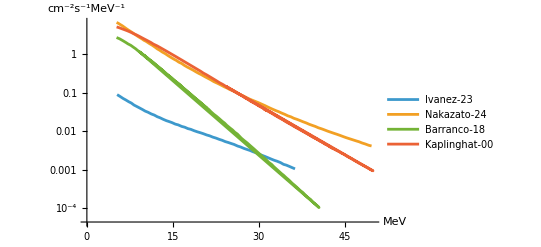

```mathematica
ListLogPlot[{ivanez23,nakazato24,barranco18,kaplinghat00},PlotLegends->{"Ivanez-23","Nakazato-24","Barranco-18","Kaplinghat-00"},Joined->True,AxesLabel->{"MeV","cm^-2s^-1MeV^-1"}]
```

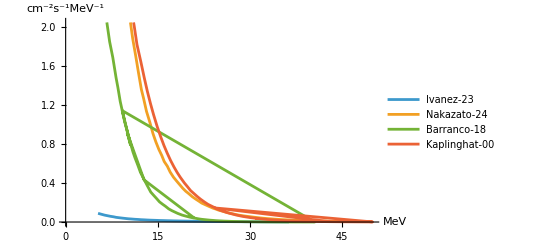

```mathematica
ListPlot[{ivanez23,nakazato24,barranco18,kaplinghat00},PlotLegends->{"Ivanez-23","Nakazato-24","Barranco-18","Kaplinghat-00"},Joined->True,AxesLabel->{"MeV","cm^-2s^-1MeV^-1"}]
```

#### fig 7 data (lunardini et al. 2025)

import figure 7 from Lunardini et al. 2025

```mathematica
(*import figure 7 from Lunardini et al.2025*)
(*put in acsending order*)
fig7Lunardini=Sort[Import[currentDir<>"/lunardini2025_DSNB/"<>"fig7_Lunardini2025.csv"]];
```

#### fig 5 data (Kresse et al. 2021)

import figure 5 data for fiducal (with SFR uncertainty spread)

from Kresse et al. 2021

```mathematica
(*import figure 5 data for fiducal (with SFR uncertainty spread) from kresse et al 2021*)
fig5KresseFiducial=Sort[Import[currentDir<>"/kresse2021_DSNB/"<>"fiducial_kresse2021_fig5.csv"]];
fig5KresseUpper=Sort[Import[currentDir<>"/kresse2021_DSNB/"<>"upperGray_kresse2021_fig5.csv"]];
fig5KresseLower=Sort[Import[currentDir<>"/kresse2021_DSNB/"<>"lowerGray_kresse2021_fig5.csv"]];
```

#### fig 7 data (Horiuchi et al 2021)

```mathematica
(*import figure 7 for fiducial and no binary DSNB from Horiuchi et al. 2021*)
fig7H21Fiducial=Sort[Import[currentDir<>"/horiuchi2021_DSNB/"<>"fiducial_fig7_horiuchi2021.csv"]];
fig7H21noBinary=Sort[Import[currentDir<>"/horiuchi2021_DSNB/"<>"noBinaries_fig7_horiuchi2021.csv"]];
```

### DSNB flux functions

#### DSNB flux plotter

plot DSNB flux

```mathematica
(*for bin syn data, no bin syn data, or progen+engine data*)
(*plot DSNB flux*)
(*in units of MeV^-1 cm^-2 s^-1*)
(*given fiducialData and extrema (min/max) and title*)

dsnbFluxPlotter[x_,y_,z_]:=Module[{fiducialData=x,extrema=y,title=z},
ListLogPlot[
{fiducialData[[1,-1]],extrema[[1,2,-1]],extrema[[2,2,-1]]},
PlotLabel->z,
Joined->True,
Filling->{1->{{2},{Opacity[0.5,defaultColor[[1]]]}},1->{{3},{Opacity[0.5,defaultColor[[1]]]}}},
PlotStyle->{{Black},{defaultColor[[4]],Dashed},{defaultColor[[3]],,Dashed}},PlotLegends->{ToString[fiducialData[[1,1]]],ToString[extrema[[1,2,1]]],ToString[extrema[[2,2,1]]]},
AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},(*PlotRange->{{20,30},{0.01,0.5}}*)(*PlotRange->{{8.5,31.25},{0.01,10^1}}*)PlotRange->{{5,50},{10^-4,5*10^1}}(*PlotRange->{{8.5,31.25},{10^-2,10^3}}*)(*PlotRange->{{0,40},{0.01,10}}*)
]
];(*end module*)
```

#### DSNB flux dual plotter

plot DSNB fluxes

```mathematica
(*for bin syn data, no bin syn data, or progen+engine data*)
(*plot two DSNB fluxes*)
(*in units of MeV^-1 cm^-2 s^-1*)
(*given fiducialData and extrema (min/max) and title*)

dsnbDualFluxPlotter[f1_,e1_,f2_,e2_,z_]:=Module[{fiducialData1=f1,extrema1=e1,fiducialData2=f2,extrema2=e2,extretitle=z},
ListLogPlot[
{fiducialData1[[1,-1]],extrema1[[1,2,-1]],extrema1[[2,2,-1]],fiducialData2[[1,-1]],extrema2[[1,2,-1]],extrema2[[2,2,-1]]},
PlotLabel->z,
Joined->True,
(*Filling->{1->{{2},{Opacity[0.25,defaultColor[[1]]]}},1->{{3},{Opacity[0.25,defaultColor[[1]]]}},4->{{5},{Opacity[0.5,defaultColor[[1]]]}},4->{{6},{Opacity[0.5,defaultColor[[1]]]}}},*)
PlotStyle->{{Black},{defaultColor[[4]]},{defaultColor[[3]]},{Black,Dashed},{defaultColor[[4]],Dashed},{defaultColor[[3]],,Dashed}},PlotLegends->{ToString[fiducialData1[[1,1]]],ToString[extrema1[[1,2,1]]],ToString[extrema1[[2,2,1]]],ToString[fiducialData2[[1,1]]],ToString[extrema2[[1,2,1]]],ToString[extrema2[[2,2,1]]]},
AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},
(*PlotRange->{{8.5,31.25},{0.01,10^1}}*)PlotRange->{{8.5,31.25},{10^-1,10}}(*PlotRange->{{0,40},{0.01,10}}*)
]
];(*end module*)
```

#### integrated DSNB flux errorBar plotter

(*NOTE: that these integrated DSNB values are ALREADY in the data for 10-30 MeV*)

```mathematica
(*plot n cases of integrated DSNB fluxes*)
(*DSNB flux in units of MeV^-1 cm^-2 s^-1*)
(*integrated DSNB flux in units of MeV^-1 cm^-2 s^-1*)
(*given input as {{fiducialData, extremaData(min/max), title},...}*)
(*NOTE: that these integrated DSNB values are ALREADY in the data for 10-30 MeV*)
intDSNBerrBarPlotter[x_,y_]:=Module[{fidExtrTlist=x,plotTitle=y},

(*will be filled as {{point,caseNameXaxis,legendName},...}*)
(*where point = {integer,aroundValue}*)
(*where aroundValue = value^{+^max}_{-min}*)
barPointsT={};

Do[
(*get fiducial data, extrema data, and title*)
tempfidData=fidExtrTlist[[i,1,1]];
tempExtremaData=fidExtrTlist[[i,2]];
tempTitle=fidExtrTlist[[i,3]];
(*make around point of integrated DSNB value +/- max/min*)
(*around[point,{min,max}]*);
tempPointBar=Around[tempfidData[[2]][[2]],{tempfidData[[2]][[2]]-tempExtremaData[[2,2,2]][[2]],tempExtremaData[[1,2,2]][[2]]-tempfidData[[2]][[2]]}];
(*make legendName*)
(*tempLegend=ToString[tempfidData[[1]]];*)
(*tempLegend=ToString[tempExtremaData[[2,2,1]]];*)
(*tempLegend=ToString[tempExtremaData[[1,2,1]]]*)
tempLegend=ToString[tempExtremaData[[1,2,1]]]<>"\n"<>ToString[tempfidData[[1,1]]]<>"\n"<>ToString[tempExtremaData[[2,2,1]]];


(*append to full list of data points*)
(**)
AppendTo[barPointsT,{{{i,tempPointBar}},tempTitle,tempLegend}];
,{i,1,Length[fidExtrTlist]}
];(*end do loop*)
barPointsT;

(*make list of all titles for x axis*)
temptitleList=Table[{i,barPointsT[[i,2]]},{i,1,Length[barPointsT]}];
(*attempt to rotate x axis labels*)
titleList=Map[{#[[1]],Rotate[#[[2]],Pi/2]}&,temptitleList];
Map[{#[[1]],Rotate[#[[2]],Pi/2]}&,titleList];
(*barPointsT[[All,3]]*)
barPointsT[[All,1]][[1]];
(*make plot*)
ListPlot[barPointsT[[All,1]],
PlotRange->{{0,Length[fidExtrTlist]*1.25},All},
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,23}},*)
PlotLabel->plotTitle,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{{"cm^-2s^-1",None},{"",None}},
FrameStyle->Directive[16,Black],
FrameTicks->{{Automatic,Automatic},{titleList,Automatic}},
PlotLegends->barPointsT[[All,3]],
ImageSize->All
(*PlotMarkers->Automatic*)
]

];(*end module*)
```

#### DSNB integrator

```mathematica
(*take in dsnb flux data {Enu,flux}*)
(*Enu~MeV and flux~MeV^-1 cm^-2 s^-1*)
(*and chosen energy range list {Emin,Emax} to integrate*)
(*interpolate and output energy integrated DSNB flux cm^-2 s^-1*)
dsnbFluxIntegrator[x_,y_]:=Module[{fluxData=x,rangeList=y},
tempInterpFlux=Interpolation[fluxData];
NIntegrate[tempInterpFlux[z],{z,rangeList[[1]],rangeList[[2]]}]

];(*end module*)
```

#### integrated DSNB flux plotter

(*NOTE: that these integrated DSNB values are NOT already in the data for EnuLowerBound-40 MeV*)

basically this is a generalized version of integrated DSNB flux errorBar plotter (i.e. does integration explicitly)
and does not take on the already integrated DSNB flux values in the data (already done in previous code for only 10-30 MeV Enu range)

```mathematica
(*plot n cases of integrated DSNB fluxes*)
(*DSNB flux in units of MeV^-1 cm^-2 s^-1*)
(*integrated DSNB flux in units of MeV^-1 cm^-2 s^-1*)
(*given first input fidExtrTlist {{fiducialData, extremaData(min/max), title},...}*)
(*and second input as TempPlotTitle = plot title*)
(*and third input as boundList = {EnuLowerBound,EnuUpperBound,intDSNBfluxUpperBound}*)
(*NOTE: that these integrated DSNB values are NOT already in the data for EnuLowerBound-40 MeV*)
(*thus need to interpolate and integrate the data itself*)
intDSNBplotter[x_,y_,z_]:=Module[{fidExtrTlist=x,TempPlotTitle=y,boundList=z},
(*will be filled as {{point,caseNameXaxis,legendName},...}*)
(*where point = {integer,aroundValue}*)
(*where aroundValue = value^{+^max}_{-min}*)
barPointsT={};

(*make plot title (include energy range)*)
plotTitle=TempPlotTitle<>" ("<>ToString[boundList[[1]]]<>"-"<>ToString[boundList[[2]]]<>" MeV)";

Do[
(*get fiducial data, extrema data, and case x-axis title*)
tempfidData2=fidExtrTlist[[i,1,1]];
tempExtremaData2=fidExtrTlist[[i,2]];
tempTitle2=fidExtrTlist[[i,3]];
(*interpolate then integrated DSNB flux*)
(*over given Enu energy range*)
intDSNBfid=NIntegrate[Interpolation[tempfidData2[[5]]][w],{w,boundList[[1]],boundList[[2]]}];
intDSNBmax=NIntegrate[Interpolation[tempExtremaData2[[1]][[2,5]]][w],{w,boundList[[1]],boundList[[2]]}];
intDSNBmin=NIntegrate[Interpolation[tempExtremaData2[[2]][[2,5]]][w],{w,boundList[[1]],boundList[[2]]}];

(*make around point of integrated DSNB value +/- max/min*)
tempPointBar=Around[intDSNBfid,{intDSNBfid-intDSNBmin,intDSNBmax-intDSNBfid}];
(*Print[tempPointBar];*)
(*make legendName*)
(*tempLegend=ToString[tempfidData[[1]]];*)
(*tempLegend=ToString[tempExtremaData[[2,2,1]]];*)
(*tempLegend=ToString[tempExtremaData[[1,2,1]]]*)
tempLegend2=ToString[tempExtremaData2[[1,2,1]]]<>"\n"<>ToString[tempfidData2[[1,1]]]<>"\n"<>ToString[tempExtremaData2[[2,2,1]]];

(*append to full list of data points*)
AppendTo[barPointsT,{{{i,tempPointBar}},tempTitle2,tempLegend2}];
,{i,1,Length[fidExtrTlist]}
];(*end do loop*)


(*make list of all titles for x axis*)
temotitleList3=Table[{i,barPointsT[[i,2]]},{i,1,Length[barPointsT]}];
(*barPointsT[[All,3]];*)
(*attempt to rotate x axis labels*)
titleList3=Map[{#[[1]],Rotate[#[[2]],Pi/2]}&,temotitleList3];
Map[{#[[1]],Rotate[#[[2]],Pi/2]}&,titleList3];

(*make plot*)
ListPlot[barPointsT[[All,1]],
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},All},*)
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,5}},*)
PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,6.5}},
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,1}},*)
PlotLabel->plotTitle,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{{"cm^-2s^-1 (>"<>ToString[boundList[[1]]]<>" MeV)",None},{"",None}},
FrameStyle->Directive[16,Black],
FrameTicks->{{Automatic,Automatic},{titleList3,Automatic}},
PlotLegends->{barPointsT[[All,3]],LineLegend[{Red},{"SK-Gd bound: "<>ToString[boundList[[3]]]<>" cm^-2s^-1"}]},
GridLines->{None,{boundList[[3]]}},
GridLinesStyle->{Thick,Red},
ImageSize->Full
(*PlotMarkers->Automatic*)
](*end listplot*)


](*end module*)
```

#### integrated DSNB flux plotter Zero

same as integrated DSNB flux plotter except WITHOUT sk bound

(*NOTE: that these integrated DSNB values are NOT already in the data for EnuLowerBound-40 MeV*)

basically this is a generalized version of integrated DSNB flux errorBar plotter (i.e. does integration explicitly)
and does not take on the already integrated DSNB flux values in the data (already done in previous code for only 10-30 MeV Enu range)

```mathematica
(*plot n cases of integrated DSNB fluxes*)
(*DSNB flux in units of MeV^-1 cm^-2 s^-1*)
(*integrated DSNB flux in units of MeV^-1 cm^-2 s^-1*)
(*given first input fidExtrTlist {{fiducialData, extremaData(min/max), title},...}*)
(*and second input as TempPlotTitle = plot title*)
(*and third input as boundList = {EnuLowerBound,EnuUpperBound,intDSNBfluxUpperBound}*)
(*NOTE: that these integrated DSNB values are NOT already in the data for EnuLowerBound-40 MeV*)
(*thus need to interpolate and integrate the data itself*)
(*NOTE: bound list does NOT have 3rd element (SK bound)*)

intDSNBplotter0[x_,y_,z_]:=Module[{fidExtrTlist=x,TempPlotTitle=y,boundList=z},
(*will be filled as {{point,caseNameXaxis,legendName},...}*)
(*where point = {integer,aroundValue}*)
(*where aroundValue = value^{+^max}_{-min}*)
barPointsT={};

(*make plot title (include energy range)*)
plotTitle=TempPlotTitle<>" ("<>ToString[boundList[[1]]]<>"-"<>ToString[boundList[[2]]]<>" MeV)";

Do[
(*get fiducial data, extrema data, and case x-axis title*)
tempfidData2=fidExtrTlist[[i,1,1]];
tempExtremaData2=fidExtrTlist[[i,2]];
tempTitle2=fidExtrTlist[[i,3]];
(*interpolate then integrated DSNB flux*)
(*over given Enu energy range*)
intDSNBfid=NIntegrate[Interpolation[tempfidData2[[5]]][w],{w,boundList[[1]],boundList[[2]]}];
intDSNBmax=NIntegrate[Interpolation[tempExtremaData2[[1]][[2,5]]][w],{w,boundList[[1]],boundList[[2]]}];
intDSNBmin=NIntegrate[Interpolation[tempExtremaData2[[2]][[2,5]]][w],{w,boundList[[1]],boundList[[2]]}];

(*make around point of integrated DSNB value +/- max/min*)
tempPointBar=Around[intDSNBfid,{intDSNBfid-intDSNBmin,intDSNBmax-intDSNBfid}];
(*Print[tempPointBar];*)
(*make legendName*)
(*tempLegend=ToString[tempfidData[[1]]];*)
(*tempLegend=ToString[tempExtremaData[[2,2,1]]];*)
(*tempLegend=ToString[tempExtremaData[[1,2,1]]]*)
tempLegend2=ToString[tempExtremaData2[[1,2,1]]]<>"\n"<>ToString[tempfidData2[[1,1]]]<>"\n"<>ToString[tempExtremaData2[[2,2,1]]];

(*append to full list of data points*)
AppendTo[barPointsT,{{{i,tempPointBar}},tempTitle2,tempLegend2}];
,{i,1,Length[fidExtrTlist]}
];(*end do loop*)


(*make list of all titles for x axis*)
temotitleList3=Table[{i,barPointsT[[i,2]]},{i,1,Length[barPointsT]}];
(*barPointsT[[All,3]];*)
(*attempt to rotate x axis labels*)
titleList3=Map[{#[[1]],Rotate[#[[2]],Pi/2]}&,temotitleList3];
Map[{#[[1]],Rotate[#[[2]],Pi/2]}&,titleList3];

(*make plot*)
ListPlot[barPointsT[[All,1]],
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},All},*)
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,5}},*)
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,6.5}},*)
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,1}},*)
PlotRange->All;
PlotLabel->plotTitle,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{{"cm^-2s^-1 (>"<>ToString[boundList[[1]]]<>" MeV)",None},{"",None}},
FrameStyle->Directive[16,Black],
FrameTicks->{{Automatic,Automatic},{titleList3,Automatic}},
PlotLegends->{barPointsT[[All,3]]}
(*,ImageSize->Full*)
(*PlotMarkers->Automatic*)
](*end listplot*)


](*end module*)
```

#### integrated DSNB flux plotter 2

with SK general bound 2.5-2.8 cm^-2 s^-1 instead

```mathematica
(*plot n cases of integrated DSNB fluxes*)
(*DSNB flux in units of MeV^-1 cm^-2 s^-1*)
(*integrated DSNB flux in units of MeV^-1 cm^-2 s^-1*)
(*given first input fidExtrTlist {{fiducialData, extremaData(min/max), title},...}*)
(*and second input as TempPlotTitle = plot title*)
(*and third input as boundList = {EnuLowerBound,EnuUpperBound,intDSNBfluxUpperBound}*)
(*NOTE: that these integrated DSNB values are NOT already in the data for EnuLowerBound-40 MeV*)
(*thus need to interpolate and integrate the data itself*)
intDSNBplotter2[x_,y_,z_]:=Module[{fidExtrTlist=x,TempPlotTitle=y,boundList=z},
(*will be filled as {{point,caseNameXaxis,legendName},...}*)
(*where point = {integer,aroundValue}*)
(*where aroundValue = value^{+^max}_{-min}*)
barPointsT={};

(*make plot title (include energy range)*)
plotTitle=TempPlotTitle<>" ("<>ToString[boundList[[1]]]<>"-"<>ToString[boundList[[2]]]<>" MeV)";

Do[
(*get fiducial data, extrema data, and case x-axis title*)
tempfidData2=fidExtrTlist[[i,1,1]];
tempExtremaData2=fidExtrTlist[[i,2]];
tempTitle2=fidExtrTlist[[i,3]];
(*interpolate then integrated DSNB flux*)
(*over given Enu energy range*)
intDSNBfid=NIntegrate[Interpolation[tempfidData2[[5]]][w],{w,boundList[[1]],boundList[[2]]}];
intDSNBmax=NIntegrate[Interpolation[tempExtremaData2[[1]][[2,5]]][w],{w,boundList[[1]],boundList[[2]]}];
intDSNBmin=NIntegrate[Interpolation[tempExtremaData2[[2]][[2,5]]][w],{w,boundList[[1]],boundList[[2]]}];

(*make around point of integrated DSNB value +/- max/min*)
tempPointBar=Around[intDSNBfid,{intDSNBfid-intDSNBmin,intDSNBmax-intDSNBfid}];
(*Print[tempPointBar];*)
(*make legendName*)
(*tempLegend=ToString[tempfidData[[1]]];*)
(*tempLegend=ToString[tempExtremaData[[2,2,1]]];*)
(*tempLegend=ToString[tempExtremaData[[1,2,1]]]*)
tempLegend2=ToString[tempExtremaData2[[1,2,1]]]<>"\n"<>ToString[tempfidData2[[1,1]]]<>"\n"<>ToString[tempExtremaData2[[2,2,1]]];

(*append to full list of data points*)
AppendTo[barPointsT,{{{i,tempPointBar}},tempTitle2,tempLegend2}];
,{i,1,Length[fidExtrTlist]}
];(*end do loop*)


(*make list of all titles for x axis*)
temotitleList3=Table[{i,barPointsT[[i,2]]},{i,1,Length[barPointsT]}];
(*barPointsT[[All,3]];*)
(*attempt to rotate x axis labels*)
titleList3=Map[{#[[1]],Rotate[#[[2]],Pi/2]}&,temotitleList3];
Map[{#[[1]],Rotate[#[[2]],Pi/2]}&,titleList3];

(*make plot*)
ListPlot[barPointsT[[All,1]],
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},All},*)
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,5}},*)
PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,6.5}},
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,1}},*)
PlotLabel->plotTitle,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{{"cm^-2s^-1 (>"<>ToString[boundList[[1]]]<>" MeV)",None},{"",None}},
FrameStyle->Directive[16,Black],
FrameTicks->{{Automatic,Automatic},{titleList3,Automatic}},
PlotLegends->{barPointsT[[All,3]],LineLegend[{Red,Red},{"SK-Gd bound: "<>ToString[boundList[[3]]]<>" cm^-2s^-1","SK-Gd bound: "<>ToString[boundList[[3]]-0.3]<>" cm^-2s^-1"}]},
GridLines->{None,{boundList[[3]],boundList[[3]]-0.3}},
GridLinesStyle->{Thick,Red}
(*ImageSize->Full*)
(*PlotMarkers->Automatic*)
](*end listplot*)


](*end module*)
```

#### integrated DSNB flux plotter dual

(*NOTE: that these integrated DSNB values are NOT already in the data for EnuLowerBound-40 MeV*)

basically this is a generalized version of integrated DSNB flux errorBar plotter (i.e. does integration explicitly)
and does not take on the already integrated DSNB flux values in the data (already done in previous code for only 10-30 MeV Enu range)

does this for choice of two energy range with error bars side by side

```mathematica
(*plot n cases of integrated DSNB fluxes*)
(*DSNB flux in units of MeV^-1 cm^-2 s^-1*)
(*integrated DSNB flux in units of MeV^-1 cm^-2 s^-1*)
(*given first input fidExtrTlist {{fiducialData, extremaData(min/max), title},...}*)
(*and second input as TempPlotTitle = plot title*)
(*and third input as boundList = {EnuLowerBound,EnuUpperBound,intDSNBfluxUpperBound}*)
(*NOTE: that these integrated DSNB values are NOT already in the data for EnuLowerBound-40 MeV*)
(*thus need to interpolate and integrate the data itself*)
intDSNBplotterDual[x_,y_,z1_,z2_]:=Module[{fidExtrTlist=x,TempPlotTitle=y,boundList1=z1,boundList2=z2},
(*will be filled as {{point,caseNameXaxis,legendName},...}*)
(*where point = {integer,aroundValue}*)
(*where aroundValue = value^{+^max}_{-min}*)
(*for both energy ranges*)
barPointsT1={};
barPointsT2={};

(*make plot title (include energy range)*)
subtitle1=" ("<>ToString[boundList1[[1]]]<>"-"<>ToString[boundList1[[2]]]<>" MeV)";
subtitle2=" ("<>ToString[boundList2[[1]]]<>"-"<>ToString[boundList2[[2]]]<>" MeV)";
plotTitle=TempPlotTitle<>subtitle1<>" & "<>subtitle2;

Do[
(*get fiducial data, extrema data, and case x-axis title*)
tempfidData4=fidExtrTlist[[i,1,1]];
tempExtremaData4=fidExtrTlist[[i,2]];
tempTitle4=fidExtrTlist[[i,3]];

(*interpolate then integrated DSNB flux*)
(*for both energy ranges*)
(*over given 1st Enu energy range*)
intDSNBfid1=NIntegrate[Interpolation[tempfidData4[[5]]][w],{w,boundList1[[1]],boundList1[[2]]}];
intDSNBmax1=NIntegrate[Interpolation[tempExtremaData4[[1]][[2,5]]][w],{w,boundList1[[1]],boundList1[[2]]}];
intDSNBmin1=NIntegrate[Interpolation[tempExtremaData4[[2]][[2,5]]][w],{w,boundList1[[1]],boundList1[[2]]}];
(*over given 2nd Enu energy range*)
intDSNBfid2=NIntegrate[Interpolation[tempfidData4[[5]]][w],{w,boundList2[[1]],boundList2[[2]]}];
intDSNBmax2=NIntegrate[Interpolation[tempExtremaData4[[1]][[2,5]]][w],{w,boundList2[[1]],boundList2[[2]]}];
intDSNBmin2=NIntegrate[Interpolation[tempExtremaData4[[2]][[2,5]]][w],{w,boundList2[[1]],boundList2[[2]]}];

(*make around point of integrated DSNB value +/- max/min*)
(*for both energy ranges*)
tempPointBar1=Around[intDSNBfid1,{intDSNBfid1-intDSNBmin1,intDSNBmax1-intDSNBfid1}];
tempPointBar2=Around[intDSNBfid2,{intDSNBfid2-intDSNBmin2,intDSNBmax2-intDSNBfid2}];

(*Print[tempPointBar];*)
(*make legendName*)
(*tempLegend=ToString[tempfidData[[1]]];*)
(*tempLegend=ToString[tempExtremaData[[2,2,1]]];*)
(*tempLegend=ToString[tempExtremaData[[1,2,1]]]*)
tempLegend4=ToString[tempExtremaData4[[1,2,1]]]<>"\n"<>ToString[tempExtremaData4[[2,2,1]]];

(*append to full list of data points*)
AppendTo[barPointsT1,{{{i,tempPointBar1}},tempTitle4,tempLegend4}];
AppendTo[barPointsT2,{{{i+0.5,tempPointBar2}},tempTitle4,None}];
,{i,1,Length[fidExtrTlist]}
];(*end do loop*)


(*make list of all titles for x axis*)
(*midway between the two error bars*)
temotitleList4=Table[{i+0.25,barPointsT1[[i,2]]},{i,1,Length[barPointsT1]}];
(*barPointsT[[All,3]];*)
(*attempt to rotate x axis labels*)
titleList4=Map[{#[[1]],Rotate[#[[2]],Pi/2]}&,temotitleList4];
Map[{#[[1]],Rotate[#[[2]],Pi/2]}&,titleList4];

(*combine bar points as flattened list of pairs*)
(*Print["barPoints1:\n",barPointsT1[[All,1]]];
Print["barPoints2:\n",barPointsT2[[All,1]]];*)
(*combine the barpoints as pairs*)
barPointsTall=Flatten[Table[{barPointsT1[[All,1]][[i]],barPointsT2[[All,1]][[i]]},{i,1,Length[barPointsT1[[All,1]]]}],1];
(*Print[barPointsTall];*)

(*get plot styles*)
hairstyle = Flatten[Table[{defaultColor[[i]],defaultColor[[i]]},{i,1,10}]];
legendHairStyle=Flatten[Table[{defaultColor[[i]]},{i,1,10}]];


(*(*make linear plot*)
ListPlot[barPointsTall,
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},All},*)
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,5}},*)
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,6.5}},*)
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,1}},*)
PlotRange->All,
PlotLabel->plotTitle,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{{"cm^-2s^-1",None},{"",None}},
FrameStyle->Directive[16,Black],
FrameTicks->{{Automatic,Automatic},{titleList4,Automatic}},
PlotLegends->LineLegend[legendHairStyle,barPointsT1[[All,3]]],
PlotStyle->hairstyle
(*,ImageSize->Full*)
(*,PlotMarkers->Automatic*)
](*end listplot*)*)

(*make log plot*)
ListLogPlot[barPointsTall,
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},All},*)
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,5}},*)
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,6.5}},*)
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,1}},*)
PlotRange->All,
PlotLabel->plotTitle,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{{"cm^-2s^-1",None},{"",None}},
FrameStyle->Directive[16,Black],
FrameTicks->{{Automatic,Automatic},{titleList4,Automatic}},
PlotLegends->LineLegend[legendHairStyle,barPointsT1[[All,3]]],
PlotStyle->hairstyle
(*,ImageSize->Full*)
(*,PlotMarkers->Automatic*)
](*end listplot*)



];(*end module*)
```

```mathematica
legendHairStyle
```

legendHairStyle

#### integrated DSNB flux plotter 3

only spit out the data values

(*NOTE: that these integrated DSNB values are NOT already in the data for EnuLowerBound-40 MeV*)

basically this is a generalized version of integrated DSNB flux errorBar plotter (i.e. does integration explicitly)
and does not take on the already integrated DSNB flux values in the data (already done in previous code for only 10-30 MeV Enu range)

```mathematica
(*plot n cases of integrated DSNB fluxes*)
(*DSNB flux in units of MeV^-1 cm^-2 s^-1*)
(*integrated DSNB flux in units of MeV^-1 cm^-2 s^-1*)
(*given first input fidExtrTlist {{fiducialData, extremaData(min/max), title},...}*)
(*and second input as TempPlotTitle = plot title*)
(*and third input as boundList = {EnuLowerBound,EnuUpperBound,intDSNBfluxUpperBound}*)
(*NOTE: that these integrated DSNB values are NOT already in the data for EnuLowerBound-40 MeV*)
(*thus need to interpolate and integrate the data itself*)
intDSNBplotter3[x_,y_,z_]:=Module[{fidExtrTlist=x,TempPlotTitle=y,boundList=z},
(*will be filled as {{point,caseNameXaxis,legendName},...}*)
(*where point = {integer,aroundValue}*)
(*where aroundValue = value^{+^max}_{-min}*)
pointsOut={};

(*make plot title (include energy range)*)
plotTitle=TempPlotTitle<>" ("<>ToString[boundList[[1]]]<>"-"<>ToString[boundList[[2]]]<>" MeV)";

Do[
(*get fiducial data, extrema data, and case x-axis title*)
tempfidData3=fidExtrTlist[[i,1,1]];
tempExtremaData3=fidExtrTlist[[i,2]];
tempTitle3=fidExtrTlist[[i,3]];
(*interpolate then integrated DSNB flux*)
(*over given Enu energy range*)
intDSNBfid3=NIntegrate[Interpolation[tempfidData3[[5]]][w],{w,boundList[[1]],boundList[[2]]}];
intDSNBmax3=NIntegrate[Interpolation[tempExtremaData3[[1]][[2,5]]][w],{w,boundList[[1]],boundList[[2]]}];
intDSNBmin3=NIntegrate[Interpolation[tempExtremaData3[[2]][[2,5]]][w],{w,boundList[[1]],boundList[[2]]}];

(*make around point of integrated DSNB value +/- max/min*)
(*tempPointBar3=Around[intDSNBfid3,{intDSNBfid3-intDSNBmin3,intDSNBmax3-intDSNBfid3}];*)
(*Print[tempPointBar];*)
(*make legendName*)
(*tempLegend=ToString[tempfidData[[1]]];*)
(*tempLegend=ToString[tempExtremaData[[2,2,1]]];*)
(*tempLegend=ToString[tempExtremaData[[1,2,1]]]*)
tempLegend3=ToString[tempExtremaData3[[1,2,1]]]<>"\n"<>ToString[tempfidData3[[1,1]]]<>"\n"<>ToString[tempExtremaData3[[2,2,1]]];

(*append to full list of data points*)
AppendTo[pointsOut,{{intDSNBmin3,intDSNBfid3,intDSNBmax3},tempTitle3,tempLegend3}];
,{i,1,Length[fidExtrTlist]}
];(*end do loop*)
(*throw pointsOut out*)
pointsOut

](*end module*)
```

#### Integrated DSNB plotter JR (full range)

```mathematica
(*plot n cases of integrated DSNB fluxes*)
(*DSNB flux in units of MeV^-1 cm^-2 s^-1*)
(*integrated DSNB flux in units of MeV^-1 cm^-2 s^-1*)
(*given first input fidExtrTlist {{fiducialData, extremaData(min/max), title},...}*)
(*and second input as TempPlotTitle = plot title*)
(*and third input as boundList = {EnuLowerBound,EnuUpperBound,intDSNBfluxUpperBound}*)
(*NOTE: that these integrated DSNB values are NOT already in the data for EnuLowerBound-40 MeV*)
(*thus need to interpolate and integrate the data itself*)
intDSNBplotterJR[x_,y_,z_]:=Module[{fidExtrTlist=x,TempPlotTitle=y,boundList=z},
(*will be filled as {{point,caseNameXaxis,legendName},...}*)
(*where point = {integer,aroundValue}*)
(*where aroundValue = value^{+^max}_{-min}*)
barPointsT={};

(*make plot title (include energy range)*)
plotTitle=TempPlotTitle<>" ("<>ToString[boundList[[1]]]<>"-"<>ToString[boundList[[2]]]<>" MeV)";

Do[
(*get fiducial data, extrema data, and case x-axis title*)
tempfidData2=fidExtrTlist[[i,1,1]];
tempExtremaData2=fidExtrTlist[[i,2]];
tempTitle2=fidExtrTlist[[i,3]];
(*interpolate then integrated DSNB flux*)
(*over given Enu energy range*)
intDSNBfid=NIntegrate[Interpolation[tempfidData2[[5]]][w],{w,boundList[[1]],boundList[[2]]}];
intDSNBmax=NIntegrate[Interpolation[tempExtremaData2[[1]][[2,5]]][w],{w,boundList[[1]],boundList[[2]]}];
intDSNBmin=NIntegrate[Interpolation[tempExtremaData2[[2]][[2,5]]][w],{w,boundList[[1]],boundList[[2]]}];

(*make around point of integrated DSNB value +/- max/min*)
tempPointBar=Around[intDSNBfid,{intDSNBfid-intDSNBmin,intDSNBmax-intDSNBfid}];
(*Print[tempPointBar];*)
(*make legendName*)
(*tempLegend=ToString[tempfidData[[1]]];*)
(*tempLegend=ToString[tempExtremaData[[2,2,1]]];*)
(*tempLegend=ToString[tempExtremaData[[1,2,1]]]*)
tempLegend2=ToString[tempExtremaData2[[1,2,1]]]<>"\n"<>ToString[tempfidData2[[1,1]]]<>"\n"<>ToString[tempExtremaData2[[2,2,1]]];

(*append to full list of data points*)
AppendTo[barPointsT,{{{i,tempPointBar}},tempTitle2,tempLegend2}];
,{i,1,Length[fidExtrTlist]}
];(*end do loop*)


(*make list of all titles for x axis*)
titleList=Table[{i,barPointsT[[i,2]]},{i,1,Length[barPointsT]}];
(*barPointsT[[All,3]];*)

(*make plot*)
ListPlot[barPointsT[[All,1]],
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},All},*)
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,5}},*)
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,6.5}},*)
PlotRange->All,
PlotLabel->plotTitle,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{{"cm^-2s^-1 (>"<>ToString[boundList[[1]]]<>" MeV)",None},{"",None}},
FrameStyle->Directive[16,Black],
FrameTicks->{{Automatic,Automatic},{titleList,Automatic}},
PlotLegends->{barPointsT[[All,3]],LineLegend[{Red},{"SK-Gd bound: "<>ToString[boundList[[3]]]<>" cm^-2s^-1"}]},
GridLines->{None,{boundList[[3]]}},
GridLinesStyle->{Thick,Red},
ImageSize->Full
(*PlotMarkers->Automatic*)
](*end listplot*)


](*end module*)
```

#### integrated DSNB flux plotter II

to replicate fig 10 from Kresse et al. 2021

(*NOTE: that these integrated DSNB values are NOT already in the data for EnuLowerBound-40 MeV*)

basically this is a generalized version of integrated DSNB flux errorBar plotter (i.e. does integration explicitly)
and does not take on the already integrated DSNB flux values in the data (already done in previous code for only 10-30 MeV Enu range)

version II of previous, but now only deals with single engines to replicate fig 10 of Kresse et al. 2021

```mathematica
(*plot n cases of integrated DSNB fluxes*)
(*DSNB flux in units of MeV^-1 cm^-2 s^-1*)
(*integrated DSNB flux in units of MeV^-1 cm^-2 s^-1*)
(*given first input fidExtrTlist {{fiducialData, extremaData(min/max), title},...}*)
(*and second input as TempPlotTitle = plot title*)
(*and third input as boundList = {EnuLowerBound,EnuUpperBound,intDSNBfluxUpperBound}*)
(*NOTE: that these integrated DSNB values are NOT already in the data for EnuLowerBound-40 MeV*)
(*thus need to interpolate and integrate the data itself*)
intDSNBplotterII[x_,y_,z_]:=Module[{fidExtrTlist=x,TempPlotTitle=y,boundList=z},
(*will be filled as {{point,caseNameXaxis,legendName},...}*)
(*where point = {integer,aroundValue}*)
(*where aroundValue = value^{+^max}_{-min}*)
barPointsT={};

(*make plot title (include energy range)*)
plotTitle=TempPlotTitle<>" ("<>ToString[boundList[[1]]]<>"-"<>ToString[boundList[[2]]]<>" MeV)";

Do[
(*get fiducial data, extrema data, and case x-axis title*)
tempfidData2=fidExtrTlist[[i,1,1]];
tempExtremaData2=fidExtrTlist[[i,2]];
tempTitle2=fidExtrTlist[[i,3]];
(*interpolate then integrated DSNB flux*)
(*over given Enu energy range*)
intDSNBfid=NIntegrate[Interpolation[tempfidData2[[5]]][w],{w,boundList[[1]],boundList[[2]]}];
intDSNBmax=NIntegrate[Interpolation[tempExtremaData2[[1]][[2,5]]][w],{w,boundList[[1]],boundList[[2]]}];
intDSNBmin=NIntegrate[Interpolation[tempExtremaData2[[2]][[2,5]]][w],{w,boundList[[1]],boundList[[2]]}];

(*make around point of integrated DSNB value +/- max/min*)
tempPointBar=Around[intDSNBfid,{intDSNBfid-intDSNBmin,intDSNBmax-intDSNBfid}];
(*Print[tempPointBar];*)
(*make legendName*)

(*tempLegend=ToString[tempfidData[[1]]];*)
(*tempLegend=ToString[tempExtremaData[[2,2,1]]];*)
(*tempLegend=ToString[tempExtremaData[[1,2,1]]]*)
tempLegend2=ToString[tempExtremaData2[[1,2,1]]]<>"\n"<>ToString[tempfidData2[[1,1]]]<>"\n"<>ToString[tempExtremaData2[[2,2,1]]];

(*append to full list of data points*)
AppendTo[barPointsT,{{{i,tempPointBar}},tempTitle2,tempLegend2}];
,{i,1,Length[fidExtrTlist]}
];(*end do loop*)


(*make list of all titles for x axis*)
temptitleList2=Table[{i,barPointsT[[i,2]]},{i,1,Length[barPointsT]}];
(*barPointsT[[All,3]];*)
(*attempt to rotate x axis labels*)
titleList2=Map[{#[[1]],Rotate[#[[2]],Pi/2]}&,temptitleList2];
Map[{#[[1]],Rotate[#[[2]],Pi/2]}&,titleList2];

(*make plot*)
ListPlot[barPointsT[[All,1]],
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},All},*)
(*PlotRange->{{0,Length[fidExtrTlist]*1.25},{0,5}},*)
PlotRange->{{0,Length[fidExtrTlist]*1.25},{1,6.5}},
PlotLabel->plotTitle,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{{"cm^-2s^-1 (>"<>ToString[boundList[[1]]]<>" MeV)",None},{"",None}},
FrameStyle->Directive[16,Black],
FrameTicks->{{Automatic,Automatic},{titleList2,Automatic}},
PlotLegends->{barPointsT[[All,3]],LineLegend[{Red},{"SK-Gd bound: "<>ToString[boundList[[3]]]<>" cm^-2s^-1"}]},
GridLines->{None,{boundList[[3]]}},
GridLinesStyle->{Thick,Red},
ImageSize->Full,
PlotStyle->{LightBlue,defaultColor[[8]],defaultColor[[7]],defaultColor[[1]],defaultColor[[11]],defaultColor[[13]],DarkBlue,DarkRed}
(*PlotMarkers->Automatic*)

](*end listplot*)


](*end module*)
```

```mathematica
defaultColor[[1;;15]]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
{LightBlue,defaultColor[[8]],defaultColor[[7]],defaultColor[[1]],defaultColor[[11]],defaultColor[[13]],DarkBlue,DarkRed}
```

{RGBColor[0.87, 0.94, 1],RGBColor[1, 0.75, 0],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.07, 0.25, 0.6],RGBColor[0.48, 0.06, 0.06]}

#### SK Bound Evader (points only)

take in a list of data for single case, e.g. binSynModel or maxMNS

and prepare data to be plotted compared to old SK bound

```mathematica
skBoundEvader[x_,in_]:=Module[{dataList=x,varIndex=in},

(*make list of extrema*)
titlesDataList={};
(*start loop of list of data*)
Do[
(*get extrema*)
(*If[
dataList[[i,2]][[2]]>=fiducialData[[1,2]][[2]],
tempExtrema={{"max case",dataList[[i]],{"max index","inapplicable"}},{"min case",fiducialData[[1]],{"min index","inapplicable"}}},
tempExtrema={{"max case",fiducialData[[1]],{"max index","inapplicable"}},{"min case",dataList[[i]],{"min index","inapplicable"}}}
];(*end if branch*)
(*append to full list*)
AppendTo[titlesDataList,{fiducialData,tempExtrema,ToString[dataList[[i]][[1,varIndex]]]}];*)

(*single point version*)
tempExtrema={{"max case",dataList[[i]],{"max index","inapplicable"}},{"min case",dataList[[i]],{"min index","inapplicable"}}};
AppendTo[titlesDataList,{{dataList[[i]]},tempExtrema,ToString[dataList[[i]][[1,varIndex]]]}];


,{i,1,Length[dataList]}];(*end do loop*)
(*output entire list of titledata lists*)
titlesDataList
];(*end module*)
```

#### SK Bound Evader

take in a list of data sets for single case e.g. maxNS

for each maxNS mass keep fix but vary everything else

```mathematica
(*take in a list of data sets for single case e.g.maxNS*)
(*for each maxNS mass keep fix but vary everything else*)
skBoundEvaderII[x_,in_]:=Module[{dataList=x,varIndex=in},

(*make list of extrema*)
titlesDataList={};
(*start loop of list of data*)
Do[
fixedVal=dataList[[1]][[1,varIndex]];
tempData2=selectorRecursive[dataAll,{fixedVal},1];
tempExtrema2=extremaFinder[tempData2];
AppendTo[titlesDataList,{{dataList[[i]]},tempExtrema2,ToString[dataList[[i]][[1,varIndex]]]}];
,{i,1,Length[dataList]}];(*end do loop*)
(*output entire list of titledata lists*)
titlesDataList
];(*end module*)
```

```mathematica
(*(*fix fiducial model except vary only binary synthesis model*)
(*get data*)
binModData=selectorRecursive[dataAll,{"bin syn","W18-BH2.7-a2.0",2.7,1,"BHNS","no MSW"},1];
Length[binModData]
(*find extrema*)
localExtremaBinMod=extremaFinder[binModData];*)
```

#### DSNB fluxes plotter

take in extracted data and plot the DSNB flux for all of them

```mathematica
(*take in e.g. binModData=selectorRecursive[dataAll,{"bin syn","W18-BH2.7-a2.0",2.7,1,"BHNS","no MSW"},1];*)
(*create DSNB flux plot of all elements*)

dsnbFluxesPlotter[x_,y_]:=Module[{data=x,title=y},
(*fill as {caseName,DSNBflux}*)
dsnbFluxList={};
Do[
tempDSNBFlux=data[[i,-1]];
tempCaseName=data[[i,1]];
AppendTo[dsnbFluxList,{ToString[tempCaseName],tempDSNBFlux}]
,{i,1,Length[data]}];(*end do loop*)

(*create plot*)
ListPlot[dsnbFluxList[[All,2]],Joined->True,PlotLegends->dsnbFluxList[[All,1]],AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{{0,40},{0,7}},PlotLabel->title]

];(*end module*)
```

#### DSNB fluxes plotter (without legend)

take in extracted data and plot the DSNB flux for all of them

```mathematica
(*take in e.g. binModData=selectorRecursive[dataAll,{"bin syn","W18-BH2.7-a2.0",2.7,1,"BHNS","no MSW"},1];*)
(*i.e. data is a list of diff data cases*)
(*create DSNB flux plot of all elements*)

dsnbFluxesPlotterJR[x_,y_]:=Module[{data=x,title=y},
(*fill as {caseName,DSNBflux}*)
dsnbFluxList={};
Do[
tempDSNBFlux=data[[i,-1]];
tempCaseName=data[[i,1]];
AppendTo[dsnbFluxList,{ToString[tempCaseName],tempDSNBFlux}]
,{i,1,Length[data]}];(*end do loop*)

(*create plot*)
ListPlot[dsnbFluxList[[All,2]],Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->All,PlotLabel->title]

];(*end module*)
```

### Event rate functions

#### IBD Functions

For computing event rates 
create IBD cross section function, IBD Ee+ function, and IBD Enu function

```mathematica
(*For computing event rates at SK-Gd later
create IBD cross section function,IBD Ee+function,and IBD Enu function*)
```

```mathematica
(*delta used as 1st order approx in Vogel et al. 1999 eqn 7 referenced from Strumia et al. 2003*)
(*for comparison from Strumia et al. 2003 interpolated data herein*)
massP=938.27208816;(*MeV*)
massN=939.5654205; (*MeV*)
masse=0.51099895000;(*MeV*)
delta=massN-massP;
```

Create IBD cross section function from IBD data

```mathematica
(*from IBD data create function of IBD cross section as a function of nu energy*)
(*from table 1 Strumia et al. 2003 "Precise quasielastic neutrino..."*)

(*recall data is in format of (Enu,sigma,Ee+) sublists*)
(*with units of MeV and 10^-41 cm^2*)
(*reformat into (MeV,cm^2,MeV)*)
newIBDcrossData=Table[{IBDcrossData[[i,1]],IBDcrossData[[i,2]]*10^-41},{i,1,Length[IBDcrossData]}];

(*interpolate the data such that sigma[Enu] cross section in cm^2 as a function of neutrino energy MeV*)
IBDcross=Interpolation[newIBDcrossData];
```

```mathematica
(*plot raw data vs interpolated data*)
(*of cross section as a function of Enuebar*)
(*ListLogPlot[{newIBDcrossData,Table[{x,IBDcross[x]},{x,0,200}]},PlotLabel->"IBD Cross Section",PlotLegends->{"raw data","interpolated data"},AxesLabel->{"E_ν (MeV)","cm^2"},PlotRange->All,Joined->{False,True}]*)
```

Create Enu function from IBD data

```mathematica
(*get Enu as a function of energy of positron Ee+ in IBD*)
(*recall format is (Enu,sigma,Ee+)*)
(*in units of (MeV,cm^2,MeV)*)
EnuIBDdata=Table[{IBDcrossData[[i,3]],IBDcrossData[[i,1]]},{i,2,Length[IBDcrossData]}];
(*NOTE: the first element is invalid, i.e. has no Ee+ value in original table*)
(*thus skip first element of data*)

(*interpolate the data in format of {{x,y},{x,y},...}*)
EnuIBD=Interpolation[EnuIBDdata];
```

```mathematica
(*plot raw data vs interpolated data*)
(*of Enuebar as a function of Ee+*)
(*ListPlot[{EnuIBDdata,Table[{x,EnuIBD[x]},{x,1,200}]},PlotLabel->"IBD Neutrino Energy",AxesLabel->{"E_(e^+) (MeV)","E_ν (MeV)"},PlotRange->All,Joined->{False,True},PlotLegends->{"raw data","Interpolated data"}]*)
```

```mathematica
(*compare to naive assumption that Ee+=Enu+delta from Vogol referenced from Strumia et al. 2003*)
(*Plot[{EnuIBD[x],x+delta},{x,0,40},PlotLabel->"IBD Neutrino Energy",AxesLabel->{"E_(e^+) (MeV)","E_ν (MeV)"},PlotLegends->{"Interpolated Data","E_(e^+) + Δ (naive estimate Δ="<>ToString[delta]<>" MeV)"},PlotRange->All]*)
```

Create Ee+ function from IBD data

```mathematica
(*get Ee+ as a function of energy of positron Enu in IBD*)
(*recall format is (Enu,sigma,Ee+)*)
(*in units of (MeV,cm^2,MeV)*)
EposIBDdata=Table[{IBDcrossData[[i,1]],IBDcrossData[[i,3]]},{i,2,Length[IBDcrossData]}];
(*NOTE: the first element is invalid, i.e. has no Ee+ value in original table*)
(*thus skip first element of data*)

(*interpolate the data*)
EposIBD=Interpolation[EposIBDdata];
```

```mathematica
(*ListPlot[{EposIBDdata,Table[{x,EposIBD[x]},{x,0,200}]},PlotLabel->"IBD Positron Energy",AxesLabel->{"E_ν  (MeV)","E_(e^+) (MeV)"},PlotRange->All,PlotLegends->{"raw data","Interpolated Data"}]*)
```

```mathematica
(*compare to naive assumption that Enu=Ee+-delta, where delta is 1.293 MeV from Strumia et al. 2003*)
(*Plot[{EposIBD[x],x-delta},{x,0,40},PlotLabel->"IBD Positron Energy",AxesLabel->{"E_ν  (MeV)","E_(e^+) (MeV)"},PlotRange->All,PlotLegends->{"Interpolated Data","E_OverBar[ν_e] - Δ (naive estimate Δ="<>ToString[delta]<>" MeV)"}]*)
```

### DSNB Flux temperature functions

#### fermi Dirac Distribution

```mathematica
(*generic fermi dirac distribution*)
(*take in neutrino energy and temperature in MeV*)
fermiDirac[E_,T_,A_]:=A/(Exp[E/T]+1)
```

```mathematica
(*Manipulate[Plot[{fermiDirac[x,T,A]},{x,0,40},AxesLabel->{"MeV","MeV^-1cm^-2,s^-1"},PlotRange->All,PlotLegends->{"Fermi-Dirac","Fiducial DSNB Flux"}],{T,0.01,10},{A,0.01,30}]*)
```

#### high-end temperature finder

find corresponding temperature for high energy end (beyond max) DSNB flux

```mathematica
(*find corresponding temperature for high energy end (beyond max) DSNB flux*)
(*input data is a list of DSNB flux*)
tempFinder[x_]:=Module[{data=x},
(*find max dsnb flux index*)
tempMaxIndex=Position[data[[All,2]],Max[data[[All,2]]]][[1,1]];
(*find data only above the max to generic fermi dirac distribution*)
fitPara=FindFit[data[[tempMaxIndex;;Length[data]]],fermiDirac[y,a,b],{a,b},y];
(*output the temperature, numerator value, maxIndex*)
{fitPara[[1,2]],fitPara[[2,2]],tempMaxIndex}
];(*end module*)
```

#### full temperature finder

find corresponding temperature for entire DSNB flux given range

```mathematica
(*find corresponding temperature for entire DSNB flux given range*)
tempFinderFull[x_]:=Module[{data=x},
fitPara=FindFit[data,fermiDirac[y,a,b],{a,b},y];
(*output the temperature, numerator value*)
{fitPara[[1,2]],fitPara[[2,2]]}
];(*end module*)
```

#### DSNB flux plotter (with temperature finder)

take in extracted data and plot the DSNB flux for all of them

after also finding the corresponding temperature at high energy (beyond the maximum)

```mathematica
(*take in e.g. binModData=selectorRecursive[dataAll,{"bin syn","W18-BH2.7-a2.0",2.7,1,"BHNS","no MSW"},1];*)
(*create DSNB flux plot of all elements*)

dsnbFluxesTemperaturePlotter[x_,y_]:=Module[{data=x,title=y},
(*fill as {caseName,DSNBflux}*)
dsnbFluxList={};
Do[
(*get DSNB flux and case name*)
tempDSNBFlux=data[[i,-1]];
tempCaseName=data[[i,1]];

(*get temperature, numerator coefficient, maxIndex for corresponding*)
(*dirac delta distribution*)
FDpara=tempFinder[tempDSNBFlux];
maxIndexJR=FDpara[[3]];
foundTemp=FDpara[[1]];
foundNumNum=FDpara[[2]];
(*create list of of corresponding dirac delta*)
FDlist=Table[{z,fermiDirac[z,foundTemp,foundNumNum]},{z,0,40}];

(*append to ultimate list*)
(*legendName, dsnbFlux,fermiDiracDist*)
AppendTo[dsnbFluxList,{ToString[FDpara]<>ToString[tempCaseName],tempDSNBFlux,FDlist}];
,{i,1,Length[data]}];(*end do loop*)
(*end do loop*)

(*create plot*)
ListPlot[Join[dsnbFluxList[[All,2]],dsnbFluxList[[All,3]]],Joined->True,PlotLegends->dsnbFluxList[[All,1]],AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{{0,40},All},PlotLabel->title]

];(*end module*)
```

#### DSNB flux plotter JR (with temperature finder)

WITHOUT plotting fermi Dirac distribution

take in extracted data and plot the DSNB flux for all of them

after also finding the corresponding temperature at high energy (beyond the maximum)

```mathematica
(*take in e.g. binModData=selectorRecursive[dataAll,{"bin syn","W18-BH2.7-a2.0",2.7,1,"BHNS","no MSW"},1];*)
(*create DSNB flux plot of all elements*)

dsnbFluxesTemperaturePlotterJR[x_,y_]:=Module[{data=x,title=y},
(*fill as {caseName,DSNBflux}*)
dsnbFluxList={};
Do[
(*get DSNB flux and case name*)
tempDSNBFlux=data[[i,-1]];
tempCaseName=data[[i,1]];

(*get temperature, numerator coefficient, maxIndex for corresponding*)
(*dirac delta distribution*)
FDpara=tempFinder[tempDSNBFlux];
maxIndexJR=FDpara[[3]];
foundTemp=FDpara[[1]];
foundNumNum=FDpara[[2]];

(*append to ultimate list*)
(*legendName, dsnbFlux,fermiDiracDist*)
AppendTo[dsnbFluxList,{ToString[FDpara]<>ToString[tempCaseName],tempDSNBFlux}];
,{i,1,Length[data]}];(*end do loop*)
(*end do loop*)

(*create plot*)
ListPlot[dsnbFluxList[[All,2]],Joined->True,PlotLegends->dsnbFluxList[[All,1]],AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{{0,40},{0,7}},PlotLabel->title]

];(*end module*)
```

#### DSNB flux plotter 3 (with temperature finder)

WITHOUT plotting fermi Dirac distribution

WITH full range

take in extracted data and plot the DSNB flux for all of them

after also finding the corresponding temperature at high energy (beyond the maximum)

```mathematica
(*take in e.g. binModData=selectorRecursive[dataAll,{"bin syn","W18-BH2.7-a2.0",2.7,1,"BHNS","no MSW"},1];*)
(*create DSNB flux plot of all elements*)

dsnbFluxesTemperaturePlotter3[x_,y_]:=Module[{data=x,title=y},
(*fill as {caseName,DSNBflux}*)
dsnbFluxList={};
Do[
(*get DSNB flux and case name*)
tempDSNBFlux=data[[i,-1]];
tempCaseName=data[[i,1]];

(*get temperature, numerator coefficient, maxIndex for corresponding*)
(*dirac delta distribution*)
FDpara=tempFinder[tempDSNBFlux];
maxIndexJR=FDpara[[3]];
foundTemp=FDpara[[1]];
foundNumNum=FDpara[[2]];

(*append to ultimate list*)
(*legendName, dsnbFlux,fermiDiracDist*)
AppendTo[dsnbFluxList,{ToString[FDpara]<>ToString[tempCaseName],tempDSNBFlux}];
,{i,1,Length[data]}];(*end do loop*)
(*end do loop*)

(*create plot*)
ListPlot[dsnbFluxList[[All,2]],Joined->True,PlotLegends->dsnbFluxList[[All,1]],AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->title,PlotRange->{{0,40},{0,9}}]

];(*end module*)
```

#### DSNB flux plotter 4

take in directly the DSNB flux data (from digitized plot)

```mathematica
(*take in list of dsnbDatas {{x,y},...} and list of legendNames*)
(*create DSNB flux plot of all elements*)

dsnbFluxesTemperaturePlotter4[x_,y_]:=Module[{data=x,legends=y},
(*fill as {caseName,DSNBflux}*)
dsnbFluxList={};
Do[
(*get DSNB flux and case name*)
tempDSNBFlux=data[[i]];
tempCaseName=legends[[i]];

(*get temperature, numerator coefficient, maxIndex for corresponding*)
(*dirac delta distribution*)
FDpara=tempFinderFull[tempDSNBFlux];
foundTemp=FDpara[[1]];
foundNumNum=FDpara[[2]];
(*create list of of corresponding dirac delta*)
FDlist=Table[{z,fermiDirac[z,foundTemp,foundNumNum]},{z,5,50}];

(*append to ultimate list*)
(*legendName, dsnbFlux,fermiDiracDist*)
AppendTo[dsnbFluxList,{ToString[FDpara]<>ToString[tempCaseName],tempDSNBFlux,FDlist}];
,{i,1,Length[data]}];(*end do loop*)
(*end do loop*)

(*create plot*)
ListPlot[Join[dsnbFluxList[[All,2]],dsnbFluxList[[All,3]]],Joined->True,PlotLegends->dsnbFluxList[[All,1]],AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{{5,50},All}]

];(*end module*)
```

#### DSNB flux JR (without plotting)

```mathematica
(*take in e.g. binModData=selectorRecursive[dataAll,{"bin syn","W18-BH2.7-a2.0",2.7,1,"BHNS","no MSW"},1];*)
(*output *)

dsnbFluxesTemperatureJR[x_]:=Module[{data=x},
(*fill as {caseName,DSNBflux}*)
dsnbFluxList={};
tempIndex=1;
Do[
(*get DSNB flux and case name*)
tempDSNBFlux=data[[i,-1]];
tempCaseName=data[[i,1]];

(*get temperature, numerator coefficient, maxIndex for corresponding*)
(*dirac delta distribution*)
FDpara=tempFinder[tempDSNBFlux];
maxIndexJR=FDpara[[3]];
foundTemp=FDpara[[1]];
foundNumNum=FDpara[[2]];


(*append to ultimate list*)
(*{temp,coefficent,index},caseName,dsnbFlux*)
AppendTo[dsnbFluxList,{{foundTemp,foundNumNum,tempIndex},ToString[{foundTemp,foundNumNum}]<>ToString[tempCaseName],tempDSNBFlux}];
(*increment the index*)
tempIndex+=1; 
,{i,1,Length[data]}];(*end do loop*)
(*end do loop*)

(*output the list of FD parameters,caseName, dsnbFlux*)
dsnbFluxList
];(*end module*)
```

## DSNB Flux

### Global Extrema

#### Find global extrema

reformat data

```mathematica
(*reformat data as {case, integrated DSNB, outliers, integrated event rates, DSNB flux data}*)

(*for bin syn*)
dataBS=dataReformator[allRawDataBS,0];
Dimensions[dataBS]

(*for no bin syn*)
datanoBS=dataReformator[allRawDataNoBS,0];
Dimensions[datanoBS]

(*for progen+engine*)
(*set isPEbool to true and discard all NS case since it is inapplicable*)
dataPE=dataReformator[allRawDataPE,1];
Dimensions[dataPE]
```

{7200,5}

{7200,5}

{3600,5}

join all data together

```mathematica
(*essentially the data set is another variable*)
(*deemed the single VS binary stars = data set choice*)
(*can be binary stars = binary synthesis data*)
(*or single stars = no binary synthesis data or progen+engine data*)

dataAll=Join[dataBS,datanoBS,dataPE];
```

```mathematica
Length[dataAll]
```

18000

```mathematica
18000/3
```

6000

select only BHNS (i.e. throw away all NS i.e. without criterion case) and 2P criterion (i.e. do not use 1P criterion)

```mathematica
(*select only BHNS (i.e.throw away all NS i.e.without criterion case) and 2P criterion (i.e.do not use 1P criterion)*)
(*select only BHNS (with criterion) and 2P criterion (is2Pbool=1)*)
(*i.e. omit all NS (without criterion) and 1P criterion case*)
(*but varying everything else (alpha, Max NS, bin syn model (rot model+CE parameter), single VS binary stars (data set), engine model, no MSW vs IH/NS)*)
globalDataAll=selectorRecursive[dataAll,{1,"BHNS"},1];

(*for no MSW effect*)
globalDataAllnoMSW=selectorRecursive[dataAll,{1,"BHNS","no MSW"},1];

(*for IH only*)
globalDataAllIH=selectorRecursive[dataAll,{1,"BHNS","IH"},1];

(*for NH only*)
globalDataAllNH=selectorRecursive[dataAll,{1,"BHNS","NH"},1];
```

find max and min cases

for entire data set

```mathematica
(*find max and min cases*)
(*out formated as {{"maxCase",maxData,maxIndex},{"minCase",minData,minIndex}}*)
(*all combinations, excluding all NS and 1P criterion*)
globalExtremaAll=extremaFinder[globalDataAll];

(*without MSW effect*)
globalExtremaAllnoMSW=extremaFinder[globalDataAllnoMSW];

(*for IH only*)
globalExtremaAllIH=extremaFinder[globalDataAllIH];

(*for NH only*)
globalExtremaAllNH=extremaFinder[globalDataAllNH];
```

define fiducial case and get data

```mathematica
(*fiducial case*)
fiducialCase={"bin syn","fiducialCE1","W18-BH2.7-a2.0",2.7,1,"BHNS","no MSW"};
fiducialData=selectorRecursive[dataAll,fiducialCase,1];
```

```mathematica
fiducialData[[1,1]]
```

{bin syn,fiducialCE1,W18-BH2.7-a2.0,2.7,a2.0,1,BHNS,no MSW}

define blank data

```mathematica
blankData=ReplacePart[fiducialData,{1,-1}->{{0,0},{0,0},{0,0}}]
```

{{{bin syn,fiducialCE1,W18-BH2.7-a2.0,2.7,a2.0,1,BHNS,no MSW},{integrated DSNB,8.37764},{BH+NS  outliers,0.0682418},{{SkGd events,3.22567},{HK events,26.8089},{JUNO events,2.43717}},{{0,0},{0,0},{0,0}}}}

#### find global extrema with SFR uncertainty

rescale DSNB flux extrema to get upper and lower versions

AND update integrated DSNB from 10-30 MeV

```mathematica
(*how to recale DSNB flux max or min respectively*)
(*f2=(1+Rcc0upper/Rcc0)*f1*)
(*f2=(1-Rcc0lower/Rcc0)*f1*)
```

```mathematica
(*with IH/NH and SFR uncertainty*)
globalExtremaAllSFR=SFRuncertaintyIncorporator[globalExtremaAll];
(*no MSW and SFR uncertainty*)
globalExtremaAllnoMSWSFR=SFRuncertaintyIncorporator[globalExtremaAllnoMSW];
(*IH and SFR uncertainty*)
globalExtremaAllIHSFR=SFRuncertaintyIncorporator[globalExtremaAllIH];
(*NH and SFR uncertainty*)
globalExtremaAllNHSFR=SFRuncertaintyIncorporator[globalExtremaAllNH];
```

confirm it worked

```mathematica
(*globalExtremaAll*)
```

```mathematica
(*globalExtremaAllSFR*)
```

#### Plot global extrema (without SFR uncertainty)

plot DSNB flux fiducial case with max and min cases

for all data (omitting 1P criterion and all NS case i.e. without criterion)

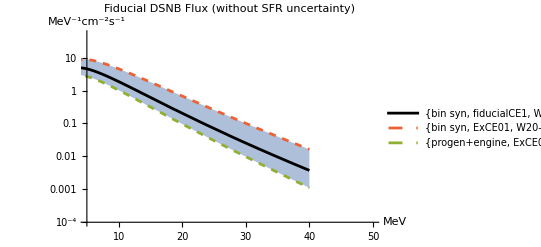

```mathematica
(*global DSNB flux*)
(*in units of MeV^-1 cm^-2 s^-1*)
globalDSNBFluxPlot=dsnbFluxPlotter[fiducialData,globalExtremaAll,"Fiducial DSNB Flux (without SFR uncertainty)"]
```

```mathematica
(*Export["globalDSNBFluxPlot.pdf",globalDSNBFluxPlot];*)
```

for no MSW data (omitting 1P criterion and all NS case i.e. without criterion)

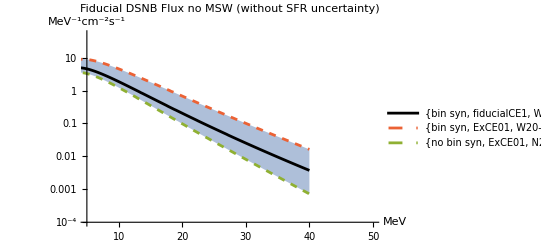

```mathematica
(*global DSNB flux no MSW*)
(*in units of MeV^-1 cm^-2 s^-1*)
globalDSNBFluxNoMSWPlot=dsnbFluxPlotter[fiducialData,globalExtremaAllnoMSW,"Fiducial DSNB Flux no MSW (without SFR uncertainty)"]
```

```mathematica
(*Export["globalDSNBFluxNoMSWPlot.pdf",globalDSNBFluxNoMSWPlot];*)
```

for IH data (omitting 1P criterion and all NS case i.e. without criterion)

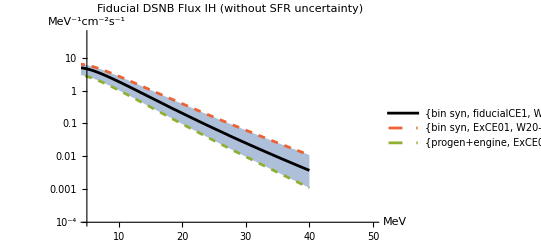

```mathematica
(*global DSNB flux IH only*)
(*in units of MeV^-1 cm^-2 s^-1*)
globalDSNBFluxIHPlot=dsnbFluxPlotter[fiducialData,globalExtremaAllIH,"Fiducial DSNB Flux IH (without SFR uncertainty)"]
```

```mathematica
(*Export["globalDSNBFluxIHPlot.pdf",globalDSNBFluxIHPlot];*)
```

for NH data (omitting 1P criterion and all NS case i.e. without criterion)

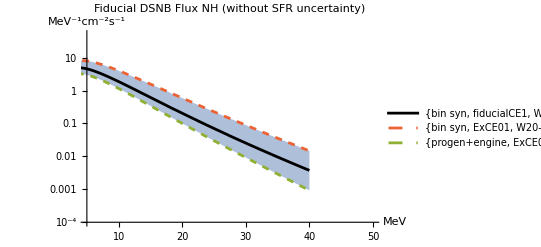

```mathematica
(*global DSNB flux NH only*)
(*in units of MeV^-1 cm^-2 s^-1*)
globalDSNBFluxNHPlot=dsnbFluxPlotter[fiducialData,globalExtremaAllNH,"Fiducial DSNB Flux NH (without SFR uncertainty)"]
```

```mathematica
(*Export["globalDSNBFluxNHPlot.pdf",globalDSNBFluxNHPlot];*)
```

raw data DSNB flux without SFR

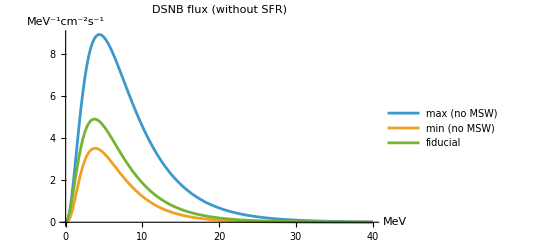

```mathematica
rawDSNBFluxDataPlot=ListPlot[{globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSW[[2,2]][[-1]],fiducialData[[1,-1]]},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"DSNB flux (without SFR)",PlotLegends->{"max (no MSW)","min (no MSW)","fiducial"}]
```

```mathematica
(*Export["rawDSNBFluxDataPlot.pdf",rawDSNBFluxDataPlot]*)
```

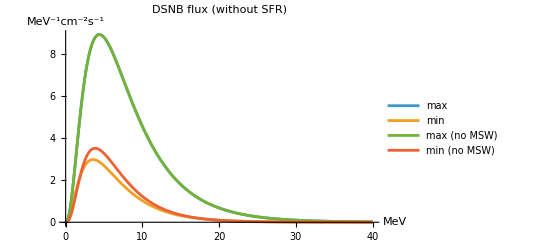

```mathematica
rawDSNBFluxDataExtremaPlot=ListPlot[{globalExtremaAll[[1,2]][[-1]],globalExtremaAll[[2,2]][[-1]],globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSW[[2,2]][[-1]]},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"DSNB flux (without SFR)",PlotLegends->{"max","min","max (no MSW)","min (no MSW)"}]
```

```mathematica
(*Export["rawDSNBFluxDataExtremaPlot.pdf",rawDSNBFluxDataExtremaPlot];*)
```

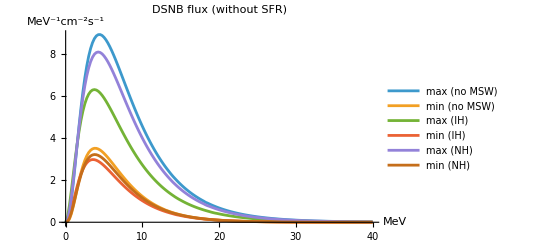

```mathematica
rawDSNBFluxDataExtremaPlotIHNH=ListPlot[{globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSW[[2,2]][[-1]],globalExtremaAllIH[[1,2]][[-1]],globalExtremaAllIH[[2,2]][[-1]],globalExtremaAllNH[[1,2]][[-1]],globalExtremaAllNH[[2,2]][[-1]]},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"DSNB flux (without SFR)",PlotLegends->{"max (no MSW)","min (no MSW)","max (IH)","min (IH)","max (NH)","min (NH)"}]
```

```mathematica
(*Export["rawDSNBFluxDataExtremaPlotIHNH.pdf",rawDSNBFluxDataExtremaPlotIHNH];*)
```

#### Plot global DSNB flux (with SFR uncertainty)

plot DSNB flux fiducial case with max and min cases

for all data (omitting 1P criterion and all NS case i.e. without criterion) with SFR uncertainty

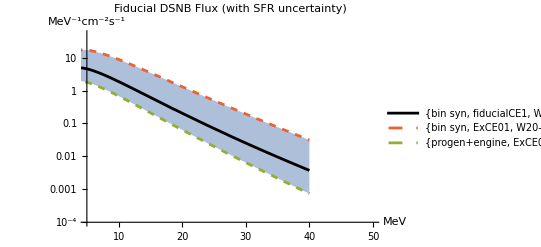

```mathematica
(*global DSNB flux*)
(*in units of MeV^-1 cm^-2 s^-1*)
globalDSNBFluxSFRPlot=dsnbFluxPlotter[fiducialData,globalExtremaAllSFR,"Fiducial DSNB Flux (with SFR uncertainty)"]
```

```mathematica
(*Export["globalDSNBFluxSFRPlot.pdf",globalDSNBFluxSFRPlot];*)
```

for no MSW data (omitting 1P criterion and all NS case i.e. without criterion) with SFR uncertainty

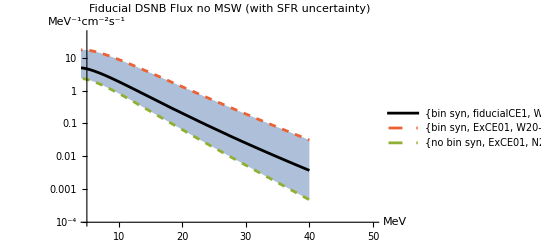

```mathematica
(*global DSNB flux no MSW*)
(*in units of MeV^-1 cm^-2 s^-1*)
globalDSNBFluxNoMSWSFRPlot=dsnbFluxPlotter[fiducialData,globalExtremaAllnoMSWSFR,"Fiducial DSNB Flux no MSW (with SFR uncertainty)"]
```

```mathematica
(*Export["globalDSNBFluxNoMSWSFRPlot.pdf",globalDSNBFluxNoMSWSFRPlot];*)
```

for IH data  (omitting 1P criterion and all NS case i.e. without criterion) with SFR uncertainty

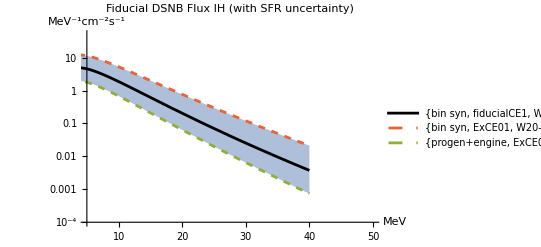

```mathematica
(*global DSNB flux IH*)
(*in units of MeV^-1 cm^-2 s^-1*)
globalDSNBFluxIHSFRPlot=dsnbFluxPlotter[fiducialData,globalExtremaAllIHSFR,"Fiducial DSNB Flux IH (with SFR uncertainty)"]
```

```mathematica
(*Export["globalDSNBFluxIHSFRPlot.pdf",globalDSNBFluxIHSFRPlot];*)
```

for NH data  (omitting 1P criterion and all NS case i.e. without criterion) with SFR uncertainty

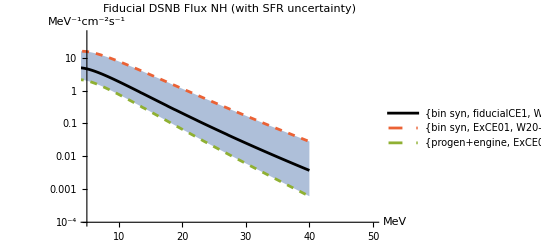

```mathematica
(*global DSNB flux NH*)
(*in units of MeV^-1 cm^-2 s^-1*)
globalDSNBFluxNHSFRPlot=dsnbFluxPlotter[fiducialData,globalExtremaAllNHSFR,"Fiducial DSNB Flux NH (with SFR uncertainty)"]
```

```mathematica
(*Export["globalDSNBFluxNHSFRPlot.pdf",globalDSNBFluxNHSFRPlot];*)
```

raw data DSNB flux with SFR

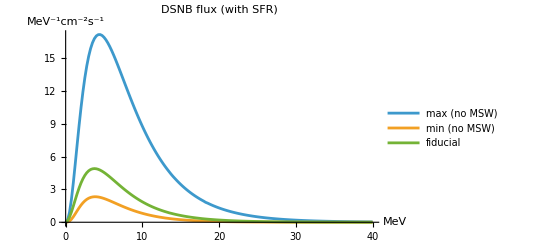

```mathematica
rawDSNBFluxDataPlotSFR=ListPlot[{globalExtremaAllnoMSWSFR[[1,2]][[-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]],fiducialData[[1,-1]]},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"DSNB flux (with SFR)",PlotLegends->{"max (no MSW)","min (no MSW)","fiducial"},PlotRange->All]
```

```mathematica
(*Export["rawDSNBFluxDataPlotSFR.pdf",rawDSNBFluxDataPlotSFR]*)
```

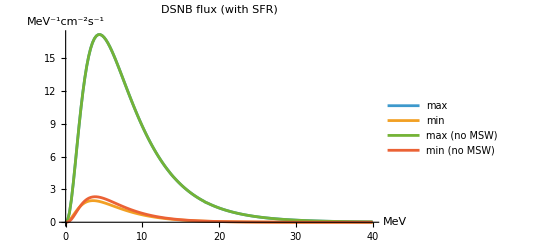

```mathematica
rawDSNBFluxDataExtremaPlotSFR=ListPlot[{globalExtremaAllSFR[[1,2]][[-1]],globalExtremaAllSFR[[2,2]][[-1]],globalExtremaAllnoMSWSFR[[1,2]][[-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]]},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"DSNB flux (with SFR)",PlotLegends->{"max","min","max (no MSW)","min (no MSW)"},PlotRange->All]
```

```mathematica
(*Export["rawDSNBFluxDataExtremaPlotSFR.pdf",rawDSNBFluxDataExtremaPlotSFR]*)
```

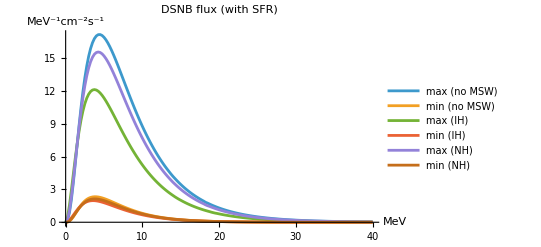

```mathematica
rawDSNBFluxDataExtremaPlotSFRIHNH=ListPlot[{globalExtremaAllnoMSWSFR[[1,2]][[-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]],globalExtremaAllIHSFR[[1,2]][[-1]],globalExtremaAllIHSFR[[2,2]][[-1]],globalExtremaAllNHSFR[[1,2]][[-1]],globalExtremaAllNHSFR[[2,2]][[-1]]},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"DSNB flux (with SFR)",PlotLegends->{"max (no MSW)","min (no MSW)","max (IH)","min (IH)","max (NH)","min (NH)"},PlotRange->All]
```

```mathematica
(*Export["rawDSNBFluxDataExtremaPlotSFRIHNH.pdf",rawDSNBFluxDataExtremaPlotSFRIHNH];*)
```

#### comparison to Lunardini et al. 2025

```mathematica
rawDSNBFluxDataPlot=ListPlot[{globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSW[[2,2]][[-1]],fiducialData[[1,-1]]},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"DSNB flux (without SFR)",PlotLegends->{"max (no MSW)","min (no MSW)","fiducial"}]
```

-Graphics-

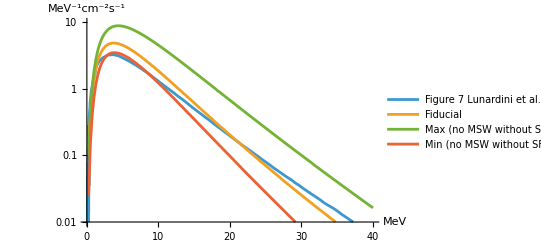

```mathematica
ListLogPlot[{fig7Lunardini,fiducialData[[1,-1]],globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSW[[2,2]][[-1]]},Joined->True,PlotLegends->{"Figure 7 Lunardini et al. 2025 (no MSW)","Fiducial","Max (no MSW without SFR uncertainty)","Min (no MSW without SFR uncertainty)"},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{{0,40},{0.01,10}}]
```

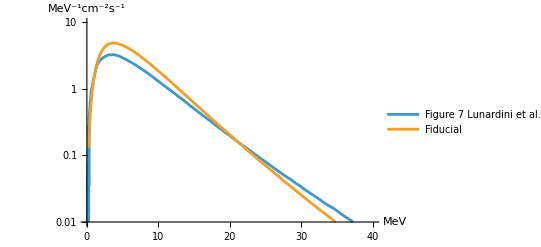

```mathematica
ListLogPlot[{fig7Lunardini,fiducialData[[1,-1]]},Joined->True,PlotLegends->{"Figure 7 Lunardini et al. 2025 (no MSW)","Fiducial","Max (no MSW without SFR uncertainty)","Min (no MSW without SFR uncertainty)"},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{{0,40},{0.01,10}}]
```

#### compare with Horiuchi et al. 2009

also compare with Horiuchi et al. 2009

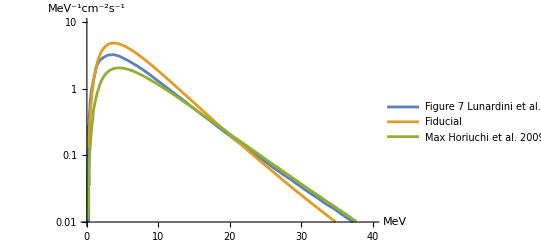

```mathematica
(**)
ListLogPlot[{fig7Lunardini,fiducialData[[1,-1]],(*Sort[fig6MeVbottom],*)Sort[fig6MeVtop]},Joined->True,PlotLegends->{"Figure 7 Lunardini et al. 2025 (no MSW)","Fiducial","Max Horiuchi et al. 2009 (T = 6 MeV)",None},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{{0,40},{0.01,10}},PlotStyle->{defaultColor[[1]],defaultColor[[2]],defaultColor[[3]],defaultColor[[3]]}]
```

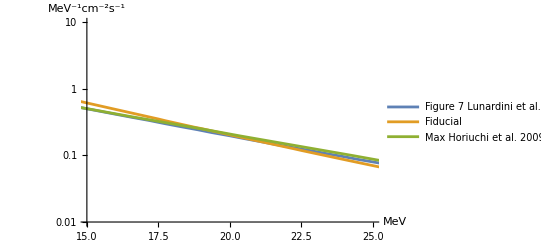

```mathematica
ListLogPlot[{fig7Lunardini,fiducialData[[1,-1]],(*Sort[fig6MeVbottom],*)Sort[fig6MeVtop]},Joined->True,PlotLegends->{"Figure 7 Lunardini et al. 2025 (no MSW)","Fiducial","Max Horiuchi et al. 2009 (T = 6 MeV)",None},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{{15,25},{0.01,10}},PlotStyle->{defaultColor[[1]],defaultColor[[2]],defaultColor[[3]],defaultColor[[3]]}]
```

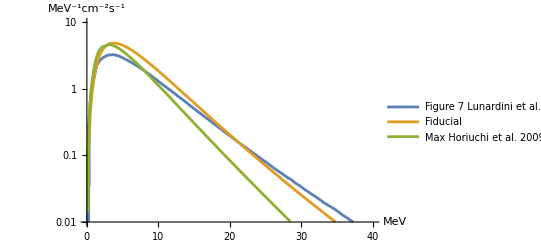

```mathematica
ListLogPlot[{fig7Lunardini,fiducialData[[1,-1]],(*Sort[fig4MeVbottom],*)Sort[fig4MeVtop]},Joined->True,PlotLegends->{"Figure 7 Lunardini et al. 2025 (no MSW)","Fiducial","Max Horiuchi et al. 2009 (T = 4 MeV)",None},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{{0,40},{0.01,10}},PlotStyle->{defaultColor[[1]],defaultColor[[2]],defaultColor[[3]],defaultColor[[3]]}]
```

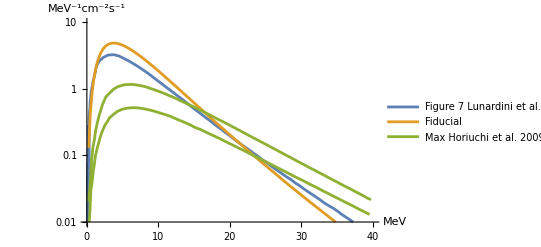

```mathematica
ListLogPlot[{fig7Lunardini,fiducialData[[1,-1]],Sort[fig8MeVbottom],Sort[fig8MeVtop]},Joined->True,PlotLegends->{"Figure 7 Lunardini et al. 2025 (no MSW)","Fiducial","Max Horiuchi et al. 2009 (T = 8 MeV)",None},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{{0,40},{0.01,10}},PlotStyle->{defaultColor[[1]],defaultColor[[2]],defaultColor[[3]],defaultColor[[3]]}]
```

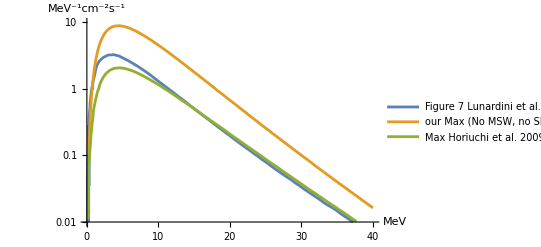

```mathematica
ListLogPlot[{fig7Lunardini,globalExtremaAllnoMSW[[1,2]][[-1]],Sort[fig6MeVtop]},Joined->True,PlotLegends->{"Figure 7 Lunardini et al. 2025 (no MSW)","our Max (No MSW, no SFR uncertainty)","Max Horiuchi et al. 2009 (T = 6 MeV)",None},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{{0,40},{0.01,10}},PlotStyle->{defaultColor[[1]],defaultColor[[2]],defaultColor[[3]],defaultColor[[3]]}]
```

#### Comparison with Kresse et al. 2021

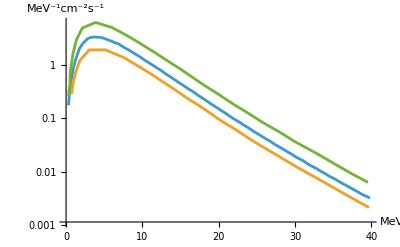

```mathematica
ListLogPlot[{fig5KresseFiducial,fig5KresseLower,fig5KresseUpper},Joined->True,PlotRange->All,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"}]
```

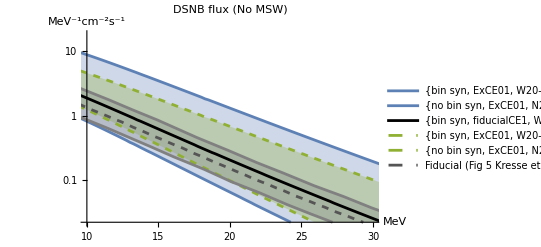

```mathematica
ListLogPlot[{globalExtremaAllnoMSWSFR[[1,2]][[-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]],fiducialData[[1,-1]],globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSW[[2,2]][[-1]],fig5KresseFiducial,fig5KresseLower,fig5KresseUpper},
Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},
PlotLabel->"DSNB flux (No MSW)",
PlotLegends->{ToString[globalExtremaAllnoMSWSFR[[1,2,1]]],ToString[globalExtremaAllnoMSWSFR[[2,2,1]]],ToString[fiducialData[[1,1]]],ToString[globalExtremaAllnoMSW[[1,2,1]]],ToString[globalExtremaAllnoMSW[[2,2,1]]],"Fiducial (Fig 5 Kresse et al. 2025)"},
PlotStyle->{{defaultColor[[1]]},{defaultColor[[1]]},{Black},{Dashed,defaultColor[[3]]},{Dashed,defaultColor[[3]]},{Dashed,Lighter[Black]},{Gray},{Gray}},
Filling->{1->{{2},{Opacity[0.3,defaultColor[[1]]]}},4->{{5},{Opacity[0.3,defaultColor[[3]]]}},7->{{8},Opacity[0.3,Gray]}},
PlotRange->{{10,30},{0,18}}
](*end plot*)
```

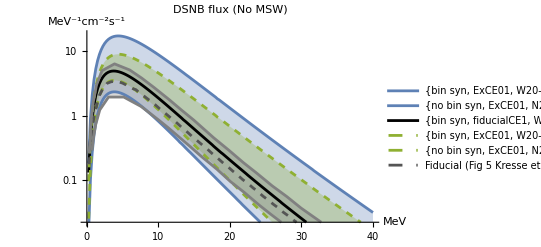

```mathematica
ListLogPlot[{globalExtremaAllnoMSWSFR[[1,2]][[-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]],fiducialData[[1,-1]],globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSW[[2,2]][[-1]],fig5KresseFiducial,fig5KresseLower,fig5KresseUpper},
Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},
PlotLabel->"DSNB flux (No MSW)",
PlotLegends->{ToString[globalExtremaAllnoMSWSFR[[1,2,1]]],ToString[globalExtremaAllnoMSWSFR[[2,2,1]]],ToString[fiducialData[[1,1]]],ToString[globalExtremaAllnoMSW[[1,2,1]]],ToString[globalExtremaAllnoMSW[[2,2,1]]],"Fiducial (Fig 5 Kresse et al. 2025)"},
PlotStyle->{{defaultColor[[1]]},{defaultColor[[1]]},{Black},{Dashed,defaultColor[[3]]},{Dashed,defaultColor[[3]]},{Dashed,Lighter[Black]},{Gray},{Gray}},
Filling->{1->{{2},{Opacity[0.3,defaultColor[[1]]]}},4->{{5},{Opacity[0.3,defaultColor[[3]]]}},7->{{8},Opacity[0.3,Gray]}},
PlotRange->{{0,40},{0,18}}
](*end plot*)
```

### Local Extrema

#### Vary only max NS mass

fix to fiducial model except vary max NS

```mathematica
fiducialCase
```

{bin syn,fiducialCE1,W18-BH2.7-a2.0,2.7,1,BHNS,no MSW}

plot these

```mathematica
(*global DSNB flux*)
(*in units of MeV^-1 cm^-2 s^-1*)
localDSNBFluxPlotmaxNS=dsnbFluxPlotter[fiducialData,localExtremaMaxNSm,"Fiducial DSNB Flux (without SFR uncertainty)"]
```

Part::partd: Part specification localExtremaMaxNSm⟦1,2,-1⟧ is longer than depth of object.

Part::partd: Part specification localExtremaMaxNSm⟦2,2,-1⟧ is longer than depth of object.

Part::partd: Part specification localExtremaMaxNSm⟦1,2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListLogPlot::lpn: {{{0.,Indeterminate},{0.25,-2.03519},{0.5,-0.781184},{0.75,-0.0773314},{1.,0.387642},{1.25,0.716873},{1.5,0.958477},{1.75,1.13904},{2.,1.27495},{2.25,1.37707},{2.5,1.45293},{2.75,1.50802},«28»,{10.,0.622471},{10.25,0.568938},{10.5,0.515061},{10.75,0.460875},{11.,0.406412},{11.25,0.351704},{11.5,0.296779},{11.75,0.241661},{12.,0.186376},{12.25,0.130946},«111»},{},{}} is not a list of numbers or pairs of numbers.

ListLogPlot[{{{0.,0.},{0.25,0.130656},{0.5,0.457864},{0.75,0.925583},{1.,1.4735},{1.25,2.04802},{1.5,2.60772},{1.75,3.12377},{2.,3.57854},{2.25,3.96325},{2.5,4.27563},{2.75,4.51778},{3.,4.69454},{3.25,4.8115},{3.5,4.87616},{3.75,4.89708},{4.,4.87982},{4.25,4.83066},{4.5,4.75525},{4.75,4.6586},{5.,4.5451},{5.25,4.41853},{5.5,4.28214},{5.75,4.13867},{6.,3.99045},{6.25,3.83943},{6.5,3.68722},{6.75,3.53516},{7.,3.38435},{7.25,3.23568},{7.5,3.08986},{7.75,2.94745},{8.,2.80891},{8.25,2.67455},{8.5,2.54462},{8.75,2.41928},{9.,2.29865},{9.25,2.18277},{9.5,2.07165},{9.75,1.96525},{10.,1.86353},{10.25,1.76639},{10.5,1.67374},{10.75,1.58546},{11.,1.50142},{11.25,1.42149},{11.5,1.34552},{11.75,1.27336},{12.,1.20488},{12.25,1.13991},{12.5,1.07831},{12.75,1.01993},{13.,0.964622},{13.25,0.912252},{13.5,0.857826},{13.75,0.815762},{14.,0.771402},{14.25,0.729443},{14.5,0.689739},{14.75,0.6522},{15.,0.616714},{15.25,0.583173},{15.5,0.551475},{15.75,0.521521},{16.,0.493218},{16.25,0.466476},{16.5,0.441212},{16.75,0.417344},{17.,0.394795},{17.25,0.373494},{17.5,0.35337},{17.75,0.332504},{18.,0.31462},{18.25,0.297727},{18.5,0.281769},{18.75,0.266693},{19.,0.253947},{19.25,0.240425},{19.5,0.227647},{19.75,0.215571},{20.,0.204159},{20.25,0.193371},{20.5,0.183175},{20.75,0.173535},{21.,0.164482},{21.25,0.155861},{21.5,0.147709},{21.75,0.14},{22.,0.132708},{22.25,0.125811},{22.5,0.118943},{22.75,0.112801},{23.,0.106988},{23.25,0.101487},{23.5,0.0962791},{23.75,0.0913495},{24.,0.0866822},{24.25,0.0822629},{24.5,0.0780779},{24.75,0.0741533},{25.,0.0703974},{25.25,0.0668393},{25.5,0.0634682},{25.75,0.060274},{26.,0.057247},{26.25,0.054378},{26.5,0.0516586},{26.75,0.0490807},{27.,0.0466366},{27.25,0.0440365},{27.5,0.0418549},{27.75,0.0397858},{28.,0.0378232},{28.25,0.0359614},{28.5,0.034195},{28.75,0.0325189},{29.,0.0309282},{29.25,0.0294186},{29.5,0.0279856},{29.75,0.0266253},{30.,0.0253338},{30.25,0.0241075},{30.5,0.0229429},{30.75,0.0218368},{31.,0.0207862},{31.25,0.0197882},{31.5,0.01884},{31.75,0.0179391},{32.,0.017083},{32.25,0.0162693},{32.5,0.0154959},{32.75,0.0147608},{33.,0.0140619},{33.25,0.0133974},{33.5,0.0127655},{33.75,0.0121646},{34.,0.0115931},{34.25,0.0110495},{34.5,0.0105323},{34.75,0.0100403},{35.,0.00957217},{35.25,0.00912669},{35.5,0.00870274},{35.75,0.00829923},{36.,0.00791514},{36.25,0.0075495},{36.5,0.00720139},{36.75,0.00686993},{37.,0.0065543},{37.25,0.00625371},{37.5,0.00596741},{37.75,0.00569471},{38.,0.00543493},{38.25,0.00518743},{38.5,0.00495162},{38.75,0.00472691},{39.,0.00451277},{39.25,0.00430868},{39.5,0.00411416},{39.75,0.00392873},{40.,0.00375195}},localExtremaMaxNSm⟦1,2,-1⟧,localExtremaMaxNSm⟦2,2,-1⟧},PlotLabel→Fiducial DSNB Flux (without SFR uncertainty),Joined→True,Filling→{1→{{2},{Opacity[0.5,RGBColor[0.368417, 0.506779, 0.709798]]}},1→{{3},{Opacity[0.5,RGBColor[0.368417, 0.506779, 0.709798]]}}},PlotStyle→{{GrayLevel[0]},{RGBColor[0.922526, 0.385626, 0.209179],Dashing[{Small,Small}]},{RGBColor[0.560181, 0.691569, 0.194885],Null,Dashing[{Small,Small}]}},PlotLegends→{{bin syn, fiducialCE1, W18-BH2.7-a2.0, 2.7, a2.0, 1, BHNS, no MSW},localExtremaMaxNSm[[1,2,1]],localExtremaMaxNSm[[2,2,1]]},AxesLabel→{MeV,MeV^-1cm^-2s^-1},PlotRange→{{5,50},{1/10000,50}}]

```mathematica
(*Export["localDSNBFluxPlotmaxNS.pdf",localDSNBFluxPlotmaxNS]*)
```

```mathematica
localExtremaMaxNSm[[1,2,1]]
```

Part::partd: Part specification localExtremaMaxNSm⟦1,2,1⟧ is longer than depth of object.

localExtremaMaxNSm⟦1,2,1⟧

```mathematica
localExtremaMaxNSm[[2,2,1]]
```

Part::partd: Part specification localExtremaMaxNSm⟦2,2,1⟧ is longer than depth of object.

localExtremaMaxNSm⟦2,2,1⟧

try plotting DSNB flux alternatively

```mathematica
DSNBFluxPlotmaxNS=ListLogPlot[{localExtremaMaxNSm[[1,2]][[-1]],fiducialData[[1,-1]],localExtremaMaxNSm[[2,2]][[-1]]},Joined->True,PlotRange->{{8,33},{0,50}},PlotStyle->{{Dashed,defaultColor[[1]]},{Lighter[Black]},{Dashed,defaultColor[[3]]}},
Filling->{1->{{2},{Opacity[0.3,defaultColor[[1]]]}},3->{{2},{Opacity[0.3,defaultColor[[3]]]}}},
PlotLegends->{ToString[localExtremaMaxNSm[[1,2,1]]],"Fiducial",ToString[localExtremaMaxNSm[[2,2,1]]]},PlotLabel->"max NS masses (without SFR)"]
```

Part::partd: Part specification localExtremaMaxNSm⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification localExtremaMaxNSm⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification localExtremaMaxNSm⟦1,2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListLogPlot::lpn: {{},{{0.,Indeterminate},{0.25,-2.03519},{0.5,-0.781184},{0.75,-0.0773314},{1.,0.387642},{1.25,0.716873},{1.5,0.958477},{1.75,1.13904},{2.,1.27495},{2.25,1.37707},{2.5,1.45293},{2.75,1.50802},«28»,{10.,0.622471},{10.25,0.568938},{10.5,0.515061},{10.75,0.460875},{11.,0.406412},{11.25,0.351704},{11.5,0.296779},{11.75,0.241661},{12.,0.186376},{12.25,0.130946},«111»},{}} is not a list of numbers or pairs of numbers.

ListLogPlot[{2,{{0.,0.},{0.25,0.130656},{0.5,0.457864},{0.75,0.925583},{1.,1.4735},{1.25,2.04802},{1.5,2.60772},{1.75,3.12377},{2.,3.57854},{2.25,3.96325},{2.5,4.27563},{2.75,4.51778},{3.,4.69454},{3.25,4.8115},{3.5,4.87616},{3.75,4.89708},{4.,4.87982},{4.25,4.83066},{4.5,4.75525},{4.75,4.6586},{5.,4.5451},{5.25,4.41853},{5.5,4.28214},{5.75,4.13867},{6.,3.99045},{6.25,3.83943},{6.5,3.68722},{6.75,3.53516},{7.,3.38435},{7.25,3.23568},{7.5,3.08986},{7.75,2.94745},{8.,2.80891},{8.25,2.67455},{8.5,2.54462},{8.75,2.41928},{9.,2.29865},{9.25,2.18277},{9.5,2.07165},{9.75,1.96525},{10.,1.86353},{10.25,1.76639},{10.5,1.67374},{10.75,1.58546},{11.,1.50142},{11.25,1.42149},{11.5,1.34552},{11.75,1.27336},{12.,1.20488},{12.25,1.13991},{12.5,1.07831},{12.75,1.01993},{13.,0.964622},{13.25,0.912252},{13.5,0.857826},{13.75,0.815762},{14.,0.771402},{14.25,0.729443},{14.5,0.689739},{14.75,0.6522},{15.,0.616714},{15.25,0.583173},{15.5,0.551475},{15.75,0.521521},{16.,0.493218},{16.25,0.466476},{16.5,0.441212},{16.75,0.417344},{17.,0.394795},{17.25,0.373494},{17.5,0.35337},{17.75,0.332504},{18.,0.31462},{18.25,0.297727},{18.5,0.281769},{18.75,0.266693},{19.,0.253947},{19.25,0.240425},{19.5,0.227647},{19.75,0.215571},{20.,0.204159},{20.25,0.193371},{20.5,0.183175},{20.75,0.173535},{21.,0.164482},{21.25,0.155861},{21.5,0.147709},{21.75,0.14},{22.,0.132708},{22.25,0.125811},{22.5,0.118943},{22.75,0.112801},{23.,0.106988},{23.25,0.101487},{23.5,0.0962791},{23.75,0.0913495},{24.,0.0866822},{24.25,0.0822629},{24.5,0.0780779},{24.75,0.0741533},{25.,0.0703974},{25.25,0.0668393},{25.5,0.0634682},{25.75,0.060274},{26.,0.057247},{26.25,0.054378},{26.5,0.0516586},{26.75,0.0490807},{27.,0.0466366},{27.25,0.0440365},{27.5,0.0418549},{27.75,0.0397858},{28.,0.0378232},{28.25,0.0359614},{28.5,0.034195},{28.75,0.0325189},{29.,0.0309282},{29.25,0.0294186},{29.5,0.0279856},{29.75,0.0266253},{30.,0.0253338},{30.25,0.0241075},{30.5,0.0229429},{30.75,0.0218368},{31.,0.0207862},{31.25,0.0197882},{31.5,0.01884},{31.75,0.0179391},{32.,0.017083},{32.25,0.0162693},{32.5,0.0154959},{32.75,0.0147608},{33.,0.0140619},{33.25,0.0133974},{33.5,0.0127655},{33.75,0.0121646},{34.,0.0115931},{34.25,0.0110495},{34.5,0.0105323},{34.75,0.0100403},{35.,0.00957217},{35.25,0.00912669},{35.5,0.00870274},{35.75,0.00829923},{36.,0.00791514},{36.25,0.0075495},{36.5,0.00720139},{36.75,0.00686993},{37.,0.0065543},{37.25,0.00625371},{37.5,0.00596741},{37.75,0.00569471},{38.,0.00543493},{38.25,0.00518743},{38.5,0.00495162},{38.75,0.00472691},{39.,0.00451277},{39.25,0.00430868},{39.5,0.00411416},{39.75,0.00392873},{40.,0.00375195}},2},Joined→True,PlotRange→{{8,33},{0,50}},PlotStyle→{{Dashing[{Small,Small}],RGBColor[0.368417, 0.506779, 0.709798]},{RGBColor[0.3333333333333333, 0.3333333333333333, 0.3333333333333333]},{Dashing[{Small,Small}],RGBColor[0.560181, 0.691569, 0.194885]}},Filling→{1→{{2},{Opacity[0.3,RGBColor[0.368417, 0.506779, 0.709798]]}},3→{{2},{Opacity[0.3,RGBColor[0.560181, 0.691569, 0.194885]]}}},PlotLegends→{localExtremaMaxNSm[[1,2,1]],Fiducial,localExtremaMaxNSm[[2,2,1]]},PlotLabel→max NS masses (without SFR)]

```mathematica
(*currentSKBoundPlotMaxNS=Show[DSNBFluxPlotmaxNS,intDSNBfluxObservedOnly,ImageSize->700]*)
```

### final DSNB flux plots

#### ours only (global)

for no MSW

```mathematica
fiducialData[[1,1]]
```

{bin syn,fiducialCE1,W18-BH2.7-a2.0,2.7,a2.0,1,BHNS,no MSW}

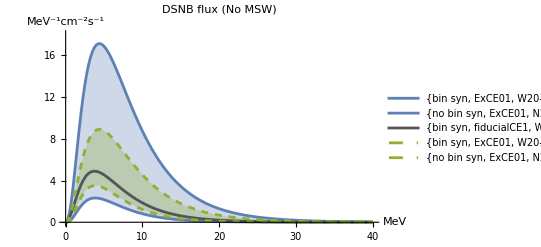

```mathematica
dsnbFluxSpreadPlotnoMSW=ListPlot[{globalExtremaAllnoMSWSFR[[1,2]][[-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]],fiducialData[[1,-1]],globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSW[[2,2]][[-1]]},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"DSNB flux (No MSW)",
PlotLegends->{ToString[globalExtremaAllnoMSWSFR[[1,2,1]]],ToString[globalExtremaAllnoMSWSFR[[2,2,1]]],ToString[fiducialData[[1,1]]],ToString[globalExtremaAllnoMSW[[1,2,1]]],ToString[globalExtremaAllnoMSW[[2,2,1]]]},
PlotStyle->{{defaultColor[[1]]},{defaultColor[[1]]},{Lighter[Black]},{Dashed,defaultColor[[3]]},{Dashed,defaultColor[[3]]}},
Filling->{1->{{2},{Opacity[0.3,defaultColor[[1]]]}},4->{{5},{Opacity[0.3,defaultColor[[3]]]}}},
PlotRange->{{All,All},{0,18}}
](*end plot*)
```

```mathematica
(*get plot data*)
dsnbFluxPlotDataNoMSW={{"noMSW max with SFR",ExportString[globalExtremaAllnoMSWSFR[[1,2]][[-1]],"PythonExpression"]},{"noMSW min with SFR",ExportString[globalExtremaAllnoMSWSFR[[2,2]][[-1]],"PythonExpression"]},{"fiducial case",ExportString[fiducialData[[1,-1]],"PythonExpression"]},{"noMSW max",ExportString[globalExtremaAllnoMSW[[1,2]][[-1]],"PythonExpression"]},{"noMSW min",ExportString[globalExtremaAllnoMSW[[2,2]][[-1]],"PythonExpression"]}};
```

```mathematica
(*export dsnb flux plot data for no MSW *)
(*Export["dsnbFluxPlotDataNoMSW.csv",dsnbFluxPlotDataNoMSW];*)
```

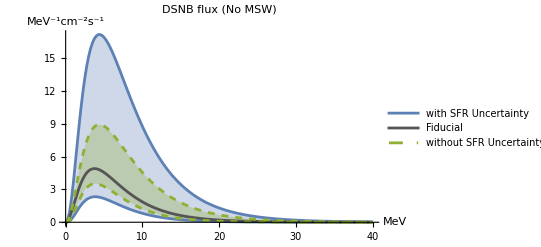

```mathematica
dsnbFluxSpreadPlotnoMSW2=ListPlot[{globalExtremaAllnoMSWSFR[[1,2]][[-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]],fiducialData[[1,-1]],globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSW[[2,2]][[-1]]},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"DSNB flux (No MSW)",PlotRange->All,
PlotLegends->{"with SFR Uncertainty",None,"Fiducial","without SFR Uncertainty"},
PlotStyle->{{defaultColor[[1]]},{defaultColor[[1]]},{Lighter[Black]},{Dashed,defaultColor[[3]]},{Dashed,defaultColor[[3]]}},
Filling->{1->{{2},{Opacity[0.3,defaultColor[[1]]]}},4->{{5},{Opacity[0.3,defaultColor[[3]]]}}}
](*end plot*)
```

```mathematica
(*Export["dsnbFluxSpreadPlotnoMSW2.pdf",dsnbFluxSpreadPlotnoMSW2]*)
```

```mathematica
defaultColor
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

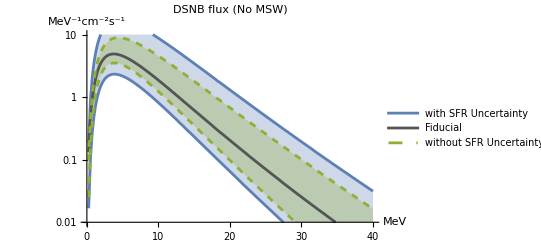

```mathematica
dsnbFluxSpreadPlotnoMSW3=ListLogPlot[{globalExtremaAllnoMSWSFR[[1,2]][[-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]],fiducialData[[1,-1]],globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSW[[2,2]][[-1]]},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"DSNB flux (No MSW)",PlotRange->{{0,40},{0.01,10}},
PlotLegends->{"with SFR Uncertainty",None,"Fiducial","without SFR Uncertainty"},
PlotStyle->{{defaultColor[[1]]},{defaultColor[[1]]},{Lighter[Black]},{Dashed,defaultColor[[3]]},{Dashed,defaultColor[[3]]}},
Filling->{1->{{2},{Opacity[0.3,defaultColor[[1]]]}},4->{{5},{Opacity[0.3,defaultColor[[3]]]}}}
](*end plot*)
```

for IH

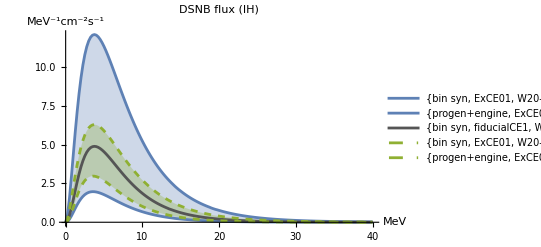

```mathematica
dsnbFluxSpreadPlotnIH=ListPlot[{globalExtremaAllIHSFR[[1,2]][[-1]],globalExtremaAllIHSFR[[2,2]][[-1]],fiducialData[[1,-1]],globalExtremaAllIH[[1,2]][[-1]],globalExtremaAllIH[[2,2]][[-1]]},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"DSNB flux (IH)",PlotRange->All,
(*PlotLegends->{"with SFR Uncertainty",None,"Fiducial","without SFR Uncertainty"},*)
PlotLegends->{ToString[globalExtremaAllIHSFR[[1,2,1]]],ToString[globalExtremaAllIHSFR[[2,2,1]]],ToString[fiducialData[[1,1]]],ToString[globalExtremaAllIH[[1,2,1]]],ToString[globalExtremaAllIH[[2,2,1]]]},
PlotStyle->{{defaultColor[[1]]},{defaultColor[[1]]},{Lighter[Black]},{Dashed,defaultColor[[3]]},{Dashed,defaultColor[[3]]}},
Filling->{1->{{2},{Opacity[0.3,defaultColor[[1]]]}},4->{{5},{Opacity[0.3,defaultColor[[3]]]}}}
](*end plot*)
```

```mathematica
(*Export["dsnbFluxSpreadPlotnIH.pdf",dsnbFluxSpreadPlotnIH];*)
```

```mathematica
(*get plot data for IH*)
dsnbFluxPlotDataIH={{"IH max with SFR",ExportString[globalExtremaAllIHSFR[[1,2]][[-1]],"PythonExpression"]},{"IH min with SFR",ExportString[globalExtremaAllIHSFR[[2,2]][[-1]],"PythonExpression"]},{"fiducial case",ExportString[fiducialData[[1,-1]],"PythonExpression"]},{"IH max",ExportString[globalExtremaAllIH[[1,2]][[-1]],"PythonExpression"]},{"IH min",ExportString[globalExtremaAllIH[[2,2]][[-1]],"PythonExpression"]}};
```

```mathematica
(*export dsnb flux plot data for no MSW *)
(*Export["dsnbFluxPlotDataIH.csv",dsnbFluxPlotDataIH];*)
```

for NH

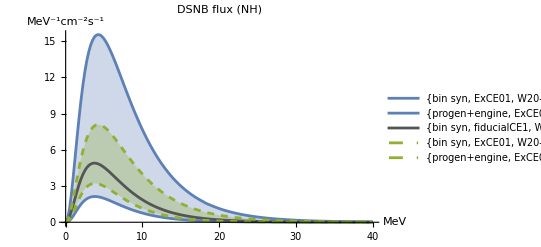

```mathematica
dsnbFluxSpreadPlotnNH=ListPlot[{globalExtremaAllNHSFR[[1,2]][[-1]],globalExtremaAllNHSFR[[2,2]][[-1]],fiducialData[[1,-1]],globalExtremaAllNH[[1,2]][[-1]],globalExtremaAllNH[[2,2]][[-1]]},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"DSNB flux (NH)",PlotRange->All,
(*PlotLegends->{"with SFR Uncertainty",None,"Fiducial","without SFR Uncertainty"},*)
PlotLegends->{ToString[globalExtremaAllNHSFR[[1,2,1]]],ToString[globalExtremaAllNHSFR[[2,2,1]]],ToString[fiducialData[[1,1]]],ToString[globalExtremaAllNH[[1,2,1]]],ToString[globalExtremaAllNH[[2,2,1]]]},
PlotStyle->{{defaultColor[[1]]},{defaultColor[[1]]},{Lighter[Black]},{Dashed,defaultColor[[3]]},{Dashed,defaultColor[[3]]}},
Filling->{1->{{2},{Opacity[0.3,defaultColor[[1]]]}},4->{{5},{Opacity[0.3,defaultColor[[3]]]}}}
](*end plot*)
```

```mathematica
(*Export["dsnbFluxSpreadPlotnNH.pdf",dsnbFluxSpreadPlotnNH];*)
```

```mathematica
(*get plot data for NH*)
dsnbFluxPlotDataNH={{"NH max with SFR",ExportString[globalExtremaAllNHSFR[[1,2]][[-1]],"PythonExpression"]},{"NH min with SFR",ExportString[globalExtremaAllNHSFR[[2,2]][[-1]],"PythonExpression"]},{"fiducial case",ExportString[fiducialData[[1,-1]],"PythonExpression"]},{"NH max",ExportString[globalExtremaAllNH[[1,2]][[-1]],"PythonExpression"]},{"NH min",ExportString[globalExtremaAllNH[[2,2]][[-1]],"PythonExpression"]}};
```

```mathematica
(*export dsnb flux plot data for no MSW *)
(*Export["dsnbFluxPlotDataNH.csv",dsnbFluxPlotDataNH];*)
```

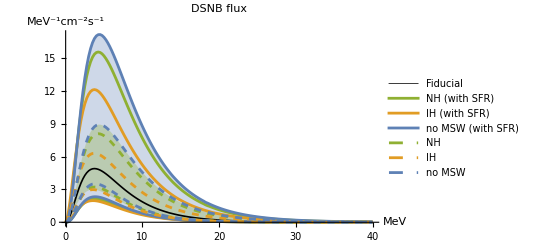

```mathematica
dsnbFluxSpreadPlotAll=ListPlot[{fiducialData[[1,-1]],globalExtremaAllNHSFR[[1,2]][[-1]],globalExtremaAllNHSFR[[2,2]][[-1]],globalExtremaAllIHSFR[[1,2]][[-1]],globalExtremaAllIHSFR[[2,2]][[-1]],globalExtremaAllnoMSWSFR[[1,2]][[-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]],globalExtremaAllNH[[1,2]][[-1]],globalExtremaAllNH[[2,2]][[-1]],globalExtremaAllIH[[1,2]][[-1]],globalExtremaAllIH[[2,2]][[-1]],globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSW[[2,2]][[-1]]},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"DSNB flux",PlotRange->All,
PlotStyle->{{Thickness[0.003],Black},{defaultColor[[3]]},{defaultColor[[3]]},{defaultColor[[2]]},{defaultColor[[2]]},{defaultColor[[1]]},{defaultColor[[1]]},{Dashed,defaultColor[[3]]},{Dashed,defaultColor[[3]]},{Dashed,defaultColor[[2]]},{Dashed,defaultColor[[2]]},{Dashed,defaultColor[[1]]},{Dashed,defaultColor[[1]]}},
(*Filling->{11->{{12},{Opacity[0.3,defaultColor[[13]]]}}},*)
Filling->{5->{{6},{Opacity[0.3,defaultColor[[1]]]}},{11->{{12},{Opacity[0.3,defaultColor[[3]]]}}}},
PlotLegends->{"Fiducial","NH (with SFR)",None,"IH (with SFR)",None,"no MSW (with SFR)",None,"NH",None,"IH",None,"no MSW"}
](*end plot*)
```

```mathematica
(*Export["dsnbFluxSpreadPlotAll.pdf",dsnbFluxSpreadPlotAll]*)
```

```mathematica
defaultColor
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
Length[defaultColor]
```

15

#### ours only (SFR uncertainty only)

DSNB flux instead of integrated flux

fix everything to be fiducial except the SFR rate

```mathematica
ListPlot[{fiducialData[[1,-1]],localExtremaSFR[[1,2,-1]],localExtremaSFR[[2,2,-1]]}]
```

Part::partd: Part specification localExtremaSFR⟦1,2,-1⟧ is longer than depth of object.

Part::partd: Part specification localExtremaSFR⟦2,2,-1⟧ is longer than depth of object.

ListPlot::lpn: {{{0.,0.},{0.25,0.130656},{0.5,0.457864},{0.75,0.925583},{1.,1.4735},{1.25,2.04802},{1.5,2.60772},{1.75,3.12377},{2.,3.57854},{2.25,3.96325},{2.5,4.27563},{2.75,4.51778},«27»,{9.75,1.96525},{10.,1.86353},{10.25,1.76639},{10.5,1.67374},{10.75,1.58546},{11.,1.50142},{11.25,1.42149},{11.5,1.34552},{11.75,1.27336},{12.,1.20488},{12.25,1.13991},«111»},{},{}} is not a list of numbers or pairs of numbers.

ListPlot[{{{0.,0.},{0.25,0.130656},{0.5,0.457864},{0.75,0.925583},{1.,1.4735},{1.25,2.04802},{1.5,2.60772},{1.75,3.12377},{2.,3.57854},{2.25,3.96325},{2.5,4.27563},{2.75,4.51778},{3.,4.69454},{3.25,4.8115},{3.5,4.87616},{3.75,4.89708},{4.,4.87982},{4.25,4.83066},{4.5,4.75525},{4.75,4.6586},{5.,4.5451},{5.25,4.41853},{5.5,4.28214},{5.75,4.13867},{6.,3.99045},{6.25,3.83943},{6.5,3.68722},{6.75,3.53516},{7.,3.38435},{7.25,3.23568},{7.5,3.08986},{7.75,2.94745},{8.,2.80891},{8.25,2.67455},{8.5,2.54462},{8.75,2.41928},{9.,2.29865},{9.25,2.18277},{9.5,2.07165},{9.75,1.96525},{10.,1.86353},{10.25,1.76639},{10.5,1.67374},{10.75,1.58546},{11.,1.50142},{11.25,1.42149},{11.5,1.34552},{11.75,1.27336},{12.,1.20488},{12.25,1.13991},{12.5,1.07831},{12.75,1.01993},{13.,0.964622},{13.25,0.912252},{13.5,0.857826},{13.75,0.815762},{14.,0.771402},{14.25,0.729443},{14.5,0.689739},{14.75,0.6522},{15.,0.616714},{15.25,0.583173},{15.5,0.551475},{15.75,0.521521},{16.,0.493218},{16.25,0.466476},{16.5,0.441212},{16.75,0.417344},{17.,0.394795},{17.25,0.373494},{17.5,0.35337},{17.75,0.332504},{18.,0.31462},{18.25,0.297727},{18.5,0.281769},{18.75,0.266693},{19.,0.253947},{19.25,0.240425},{19.5,0.227647},{19.75,0.215571},{20.,0.204159},{20.25,0.193371},{20.5,0.183175},{20.75,0.173535},{21.,0.164482},{21.25,0.155861},{21.5,0.147709},{21.75,0.14},{22.,0.132708},{22.25,0.125811},{22.5,0.118943},{22.75,0.112801},{23.,0.106988},{23.25,0.101487},{23.5,0.0962791},{23.75,0.0913495},{24.,0.0866822},{24.25,0.0822629},{24.5,0.0780779},{24.75,0.0741533},{25.,0.0703974},{25.25,0.0668393},{25.5,0.0634682},{25.75,0.060274},{26.,0.057247},{26.25,0.054378},{26.5,0.0516586},{26.75,0.0490807},{27.,0.0466366},{27.25,0.0440365},{27.5,0.0418549},{27.75,0.0397858},{28.,0.0378232},{28.25,0.0359614},{28.5,0.034195},{28.75,0.0325189},{29.,0.0309282},{29.25,0.0294186},{29.5,0.0279856},{29.75,0.0266253},{30.,0.0253338},{30.25,0.0241075},{30.5,0.0229429},{30.75,0.0218368},{31.,0.0207862},{31.25,0.0197882},{31.5,0.01884},{31.75,0.0179391},{32.,0.017083},{32.25,0.0162693},{32.5,0.0154959},{32.75,0.0147608},{33.,0.0140619},{33.25,0.0133974},{33.5,0.0127655},{33.75,0.0121646},{34.,0.0115931},{34.25,0.0110495},{34.5,0.0105323},{34.75,0.0100403},{35.,0.00957217},{35.25,0.00912669},{35.5,0.00870274},{35.75,0.00829923},{36.,0.00791514},{36.25,0.0075495},{36.5,0.00720139},{36.75,0.00686993},{37.,0.0065543},{37.25,0.00625371},{37.5,0.00596741},{37.75,0.00569471},{38.,0.00543493},{38.25,0.00518743},{38.5,0.00495162},{38.75,0.00472691},{39.,0.00451277},{39.25,0.00430868},{39.5,0.00411416},{39.75,0.00392873},{40.,0.00375195}},localExtremaSFR⟦1,2,-1⟧,localExtremaSFR⟦2,2,-1⟧}]

```mathematica
dsnbfluxSFRonly=dsnbFluxPlotter[fiducialData,localExtremaSFR,"Varying SFR uncertainty only"]
```

Part::partd: Part specification localExtremaSFR⟦1,2,-1⟧ is longer than depth of object.

Part::partd: Part specification localExtremaSFR⟦2,2,-1⟧ is longer than depth of object.

Part::partd: Part specification localExtremaSFR⟦1,2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListLogPlot::lpn: {{{0.,Indeterminate},{0.25,-2.03519},{0.5,-0.781184},{0.75,-0.0773314},{1.,0.387642},{1.25,0.716873},{1.5,0.958477},{1.75,1.13904},{2.,1.27495},{2.25,1.37707},{2.5,1.45293},{2.75,1.50802},«28»,{10.,0.622471},{10.25,0.568938},{10.5,0.515061},{10.75,0.460875},{11.,0.406412},{11.25,0.351704},{11.5,0.296779},{11.75,0.241661},{12.,0.186376},{12.25,0.130946},«111»},{},{}} is not a list of numbers or pairs of numbers.

ListLogPlot[{{{0.,0.},{0.25,0.130656},{0.5,0.457864},{0.75,0.925583},{1.,1.4735},{1.25,2.04802},{1.5,2.60772},{1.75,3.12377},{2.,3.57854},{2.25,3.96325},{2.5,4.27563},{2.75,4.51778},{3.,4.69454},{3.25,4.8115},{3.5,4.87616},{3.75,4.89708},{4.,4.87982},{4.25,4.83066},{4.5,4.75525},{4.75,4.6586},{5.,4.5451},{5.25,4.41853},{5.5,4.28214},{5.75,4.13867},{6.,3.99045},{6.25,3.83943},{6.5,3.68722},{6.75,3.53516},{7.,3.38435},{7.25,3.23568},{7.5,3.08986},{7.75,2.94745},{8.,2.80891},{8.25,2.67455},{8.5,2.54462},{8.75,2.41928},{9.,2.29865},{9.25,2.18277},{9.5,2.07165},{9.75,1.96525},{10.,1.86353},{10.25,1.76639},{10.5,1.67374},{10.75,1.58546},{11.,1.50142},{11.25,1.42149},{11.5,1.34552},{11.75,1.27336},{12.,1.20488},{12.25,1.13991},{12.5,1.07831},{12.75,1.01993},{13.,0.964622},{13.25,0.912252},{13.5,0.857826},{13.75,0.815762},{14.,0.771402},{14.25,0.729443},{14.5,0.689739},{14.75,0.6522},{15.,0.616714},{15.25,0.583173},{15.5,0.551475},{15.75,0.521521},{16.,0.493218},{16.25,0.466476},{16.5,0.441212},{16.75,0.417344},{17.,0.394795},{17.25,0.373494},{17.5,0.35337},{17.75,0.332504},{18.,0.31462},{18.25,0.297727},{18.5,0.281769},{18.75,0.266693},{19.,0.253947},{19.25,0.240425},{19.5,0.227647},{19.75,0.215571},{20.,0.204159},{20.25,0.193371},{20.5,0.183175},{20.75,0.173535},{21.,0.164482},{21.25,0.155861},{21.5,0.147709},{21.75,0.14},{22.,0.132708},{22.25,0.125811},{22.5,0.118943},{22.75,0.112801},{23.,0.106988},{23.25,0.101487},{23.5,0.0962791},{23.75,0.0913495},{24.,0.0866822},{24.25,0.0822629},{24.5,0.0780779},{24.75,0.0741533},{25.,0.0703974},{25.25,0.0668393},{25.5,0.0634682},{25.75,0.060274},{26.,0.057247},{26.25,0.054378},{26.5,0.0516586},{26.75,0.0490807},{27.,0.0466366},{27.25,0.0440365},{27.5,0.0418549},{27.75,0.0397858},{28.,0.0378232},{28.25,0.0359614},{28.5,0.034195},{28.75,0.0325189},{29.,0.0309282},{29.25,0.0294186},{29.5,0.0279856},{29.75,0.0266253},{30.,0.0253338},{30.25,0.0241075},{30.5,0.0229429},{30.75,0.0218368},{31.,0.0207862},{31.25,0.0197882},{31.5,0.01884},{31.75,0.0179391},{32.,0.017083},{32.25,0.0162693},{32.5,0.0154959},{32.75,0.0147608},{33.,0.0140619},{33.25,0.0133974},{33.5,0.0127655},{33.75,0.0121646},{34.,0.0115931},{34.25,0.0110495},{34.5,0.0105323},{34.75,0.0100403},{35.,0.00957217},{35.25,0.00912669},{35.5,0.00870274},{35.75,0.00829923},{36.,0.00791514},{36.25,0.0075495},{36.5,0.00720139},{36.75,0.00686993},{37.,0.0065543},{37.25,0.00625371},{37.5,0.00596741},{37.75,0.00569471},{38.,0.00543493},{38.25,0.00518743},{38.5,0.00495162},{38.75,0.00472691},{39.,0.00451277},{39.25,0.00430868},{39.5,0.00411416},{39.75,0.00392873},{40.,0.00375195}},localExtremaSFR⟦1,2,-1⟧,localExtremaSFR⟦2,2,-1⟧},PlotLabel→Varying SFR uncertainty only,Joined→True,Filling→{1→{{2},{Opacity[0.5,RGBColor[0.368417, 0.506779, 0.709798]]}},1→{{3},{Opacity[0.5,RGBColor[0.368417, 0.506779, 0.709798]]}}},PlotStyle→{{GrayLevel[0]},{RGBColor[0.922526, 0.385626, 0.209179],Dashing[{Small,Small}]},{RGBColor[0.560181, 0.691569, 0.194885],Null,Dashing[{Small,Small}]}},PlotLegends→{{bin syn, fiducialCE1, W18-BH2.7-a2.0, 2.7, a2.0, 1, BHNS, no MSW},localExtremaSFR[[1,2,1]],localExtremaSFR[[2,2,1]]},AxesLabel→{MeV,MeV^-1cm^-2s^-1},PlotRange→{{5,50},{1/10000,50}}]

```mathematica
SetDirectory[currentDir];
(*Export["dsnbfluxSFRonly.pdf",dsnbfluxSFRonly]*)
```

#### temp comparison

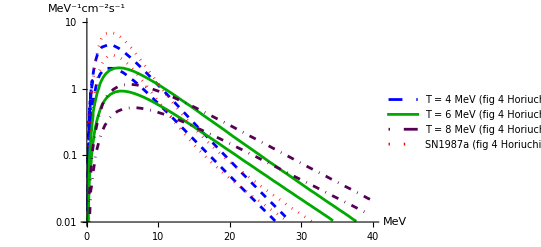

```mathematica
dsnbFluxTempHoriuchi2008=ListLogPlot[{fig4MeVbottom,fig4MeVtop,Sort[fig6MeVbottom],Sort[fig6MeVtop],Sort[fig8MeVbottom],Sort[fig8MeVtop],figSN1987abottom,figSN1987atop},
Joined->True,
PlotLegends->{"T = 4 MeV (fig 4 Horiuchi et al. 2009)",None,"T = 6 MeV (fig 4 Horiuchi et al. 2009)",None,"T = 8 MeV (fig 4 Horiuchi et al. 2009)",None,"SN1987a (fig 4 Horiuchi et al. 2008)",None},
AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},
PlotRange->{{0,40},{0.01,10}},
PlotStyle->{{Blue,Dashed},{Blue,Dashed},{Darker[Green]},{Darker[Green]},{Darker[Purple],DotDashed},{Darker[Purple],DotDashed},{Red,Dotted},{Red,Dotted}}

](*end plot*)
```

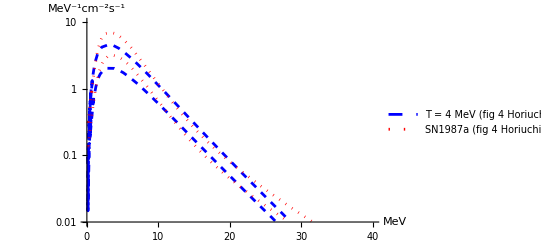

```mathematica
dsnbFluxTempHoriuchi2008JR=ListLogPlot[{fig4MeVbottom,fig4MeVtop,figSN1987abottom,figSN1987atop},
Joined->True,
PlotLegends->{"T = 4 MeV (fig 4 Horiuchi et al. 2009)",None,"SN1987a (fig 4 Horiuchi et al. 2008)",None},
AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},
PlotRange->{{0,40},{0.01,10}},
PlotStyle->{{Blue,Dashed},{Blue,Dashed},{Red,Dotted},{Red,Dotted}}

](*end plot*)
```

```mathematica
(*ListPlot[{fiducialData[[1,-1]],localExtremaSFR[[1,2,-1]],localExtremaSFR[[2,2,-1]]},PlotRange->{{0,40},{0.01,10}},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotStyle->]*)
```

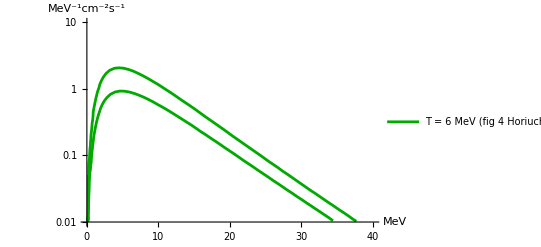

```mathematica
dsnbFluxTempHoriuchi2008Senior=ListLogPlot[{Sort[fig6MeVbottom],Sort[fig6MeVtop]},
Joined->True,
PlotLegends->{"T = 6 MeV (fig 4 Horiuchi et al. 2009)",None,"SN1987a (fig 4 Horiuchi et al. 2008)",None},
AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},
PlotRange->{{0,40},{0.01,10}},
PlotStyle->{{Darker[Green]},{Darker[Green]}}

](*end plot*)
```

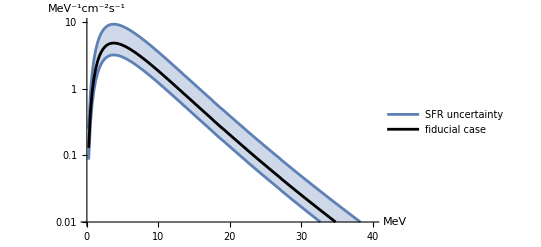

```mathematica
dsnbFluxSFRuncertaintyONLYplot=ListLogPlot[{localExtremaSFR[[1,2]][[-1]],localExtremaSFR[[2,2]][[-1]],fiducialData[[1,-1]]},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},
PlotLegends->{"SFR uncertainty",None,"fiducial case"},
PlotStyle->{{defaultColor[[1]]},{defaultColor[[1]]},{Black}},
Filling->{1->{{2},{Opacity[0.3,defaultColor[[1]]]}},4->{{5}}},
PlotRange->{{0,40},{0.01,10}}
](*end plot*)
```

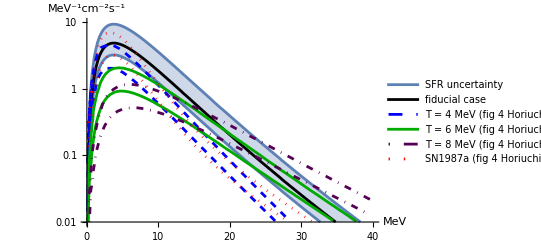

```mathematica
dsnbFluxTempComparePlot=Show[dsnbFluxSFRuncertaintyONLYplot,dsnbFluxTempHoriuchi2008]
```

```mathematica
(*Export["dsnbFluxTempComparePlot.pdf",dsnbFluxTempComparePlot];*)
```

compare with only T=4 and SN1987a from Horiuchi et al. 2009

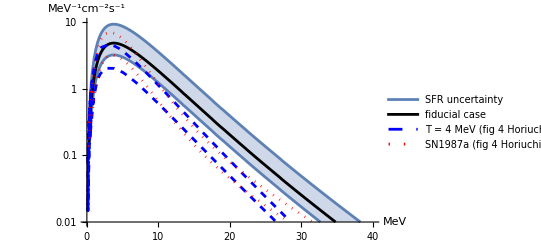

```mathematica
dsnbFluxTempComparePlotJR=Show[dsnbFluxSFRuncertaintyONLYplot,dsnbFluxTempHoriuchi2008JR]
```

```mathematica
(*Export["dsnbFluxTempComparePlotJR.pdf",dsnbFluxTempComparePlotJR];*)
```

compare to global plot (also varying everything else)

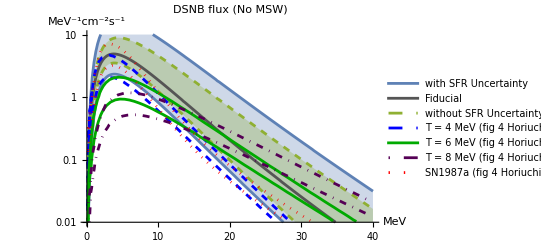

```mathematica
Show[dsnbFluxSpreadPlotnoMSW3,dsnbFluxTempHoriuchi2008]
```

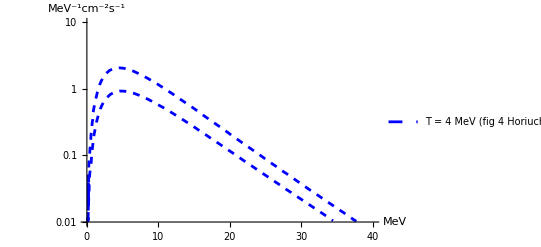

```mathematica
dsnbFluxTempHoriuchi2008Senior
```

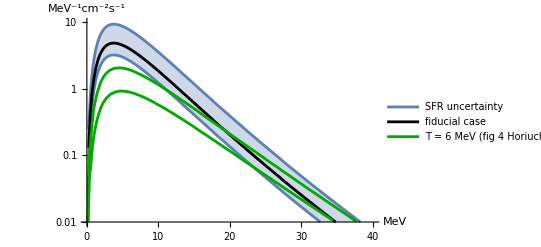

```mathematica
dsnbFluxTempComparePlotSenior=Show[dsnbFluxSFRuncertaintyONLYplot,dsnbFluxTempHoriuchi2008Senior]
```

```mathematica
(*Export["dsnbFluxTempComparePlotSenior.pdf",dsnbFluxTempComparePlotSenior];*)
```

## Integrated DSNB flux

### Local Extrema

#### get local extrema

vary only binary model

```mathematica
(*fix fiducial model except vary only binary synthesis model*)
(*get data*)
binModData=selectorRecursive[dataAll,{"bin syn","W18-BH2.7-a2.0",2.7,1,"BHNS","no MSW"},1];
Length[binModData]
(*find extrema*)
localExtremaBinMod=extremaFinder[binModData];
```

6

vary only engine model

```mathematica
(*fix fiducial model except vary only engine model*)
(*get data*)
engineModData=selectorRecursive[dataAll,{"bin syn","fiducialCE1",2.7,1,"BHNS","no MSW","a2.0"},1];
Length[engineModData]
(*find extrema*)
localExtremaEngineMod=extremaFinder[engineModData];
```

5

vary only no MSW vs IH/NH

```mathematica
(*fix fiducial model except vary only no MSW vs IH/NH*)
noMSWIHNHdata=selectorRecursive[dataAll,{"bin syn","fiducialCE1","W18-BH2.7-a2.0",2.7,1,"BHNS"},1];
Length[noMSWIHNHdata]
(*find extrema*)
localExtremaNoMSWIHNH=extremaFinder[noMSWIHNHdata];
```

3

vary only max NS mass

```mathematica
(*fix fiducial model except vary only max NS mass i.e. baryonic NS mass prior to BH formation*)
(*varying only max NS mass*)
(*since selectorRecursive only gets all engines when unfixing max NS mass*)
(*because engine formated as "W18-BH2.3-a2.0",2.3*)
(*need to select only engines that are W18 (i.e. discard N20, W15, S19.8, W20, since there is only these are all fixed at 2.7 Msol)*)
(*i.e. only having vary mass NS mass for W18 engine*)
(*therefore use selectorStr function as well*)

(*get data*)
maxMnsData=selectorStr[selectorRecursive[dataAll,{"bin syn","fiducialCE1",1,"BHNS","no MSW","a2.0"},1],"W18"];
Length[maxMnsData]
(*find extrema*)
localExtremaMaxNSm=extremaFinder[maxMnsData];
```

4

vary only alpha or pinching parameter

```mathematica
(*fix fiducial model except vary only alpha or pinching parameter*)
(*select all fiducial cases, i.e. will only vary via alpha*)
(*then extract*)
(*get data*)
alphaCheck=selectorStr[selectorRecursive[dataAll,{"bin syn","fiducialCE1",2.7,1,"no MSW","BHNS"},1],"W18"];
Length[alphaCheck]
(*find extrema*)
localExtremaAlpha=extremaFinder[alphaCheck];
```

5

vary only single VS binary stars (i.e. data set)

```mathematica
(*fix fiducial model except vary only single VS binary stars i.e. data set*)
(*binaries = binary synthesis data*)
(*single stars = progen+engine data or no binary synthesis data*)
singleVsbinarydata=selectorRecursive[dataAll,{"fiducialCE1","W18-BH2.7-a2.0",2.7,1,"BHNS","no MSW"},1];
Length[singleVsbinarydata]
(*find extrema*)
localExtremaSingleVbinary=extremaFinder[singleVsbinarydata];
```

3

vary only stellar distribution (combo of two)

```mathematica
(*essentially vary only single vs binary stars AND binary model*)
(*combination of two case variables varying*)
stellarDistdata=selectorRecursive[dataAll,{"W18-BH2.7-a2.0",2.7,1,"BHNS","no MSW"},1];
Length[stellarDistdata]
(*find extrema*)
localExtremaStellarDist=extremaFinder[stellarDistdata];
```

18

vary only 1P vs 2P criterion

```mathematica
(*fix fiducial model except vary only 1P vs 2P criterion*)
criterionData=selectorRecursive[dataAll,{"bin syn","fiducialCE1","W18-BH2.7-a2.0",2.7,"BHNS","no MSW"},1];
Length[criterionData]
(*find extrema*)
localExtrema1P2PCriterion=extremaFinder[criterionData];
```

2

vary only with SFR uncertainty

```mathematica
(*fix fiducial model except vary SFR uncertainty*)
(*make fake fiducial max and min data (these are exactly the same*)
fakeExtremaSFR={{"Max",fiducialData[[1]]},{"Min",fiducialData[[1]]}};
(*then offset them by SFR uncertainty*)
localExtremaSFR=SFRuncertaintyIncorporator[fakeExtremaSFR];
Length[localExtremaSFR]
```

2

#### plot local extrema

form data lists and titles

```mathematica
(*form lists for all cases to plot*)
(*format as fiducialModel,globalExtrema,caseName*)
(*for local extrema*)
(*for bin syn*)
binModIntDSNBList={fiducialData,localExtremaBinMod,"BPS Models"};
engineModIntDSNBList={fiducialData,localExtremaEngineMod,"CE Models"};
maxNSmassIntDSNBList={fiducialData,localExtremaMaxNSm,"Max NS Mass"};
noMSWIHNHIntDSNBList={fiducialData,localExtremaNoMSWIHNH,"Flavor Conversions"};
alphaIntDSNBList={fiducialData,localExtremaAlpha,"Spectral Pinching"};
singleVbinaryIntDSNBList={fiducialData,localExtremaSingleVbinary,"1 vs 2 stars"};
stellarDistIntDSNBList={fiducialData,localExtremaStellarDist,"Stellar Distribution"};
criterion1P2PintDSNBList={fiducialData,localExtrema1P2PCriterion,"BH/NS Criterion"};
SFRuncertaintyIntDSNBList={fiducialData,localExtremaSFR,"SFR uncertainty"};
```

plot these

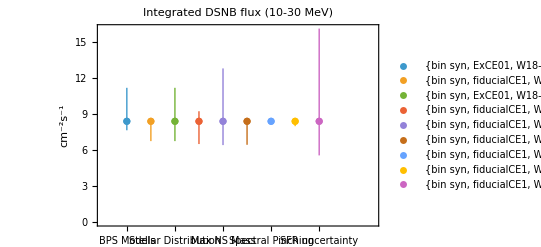

```mathematica
intDSNBplotSFR=intDSNBerrBarPlotter[{binModIntDSNBList,singleVbinaryIntDSNBList,stellarDistIntDSNBList,engineModIntDSNBList,maxNSmassIntDSNBList,noMSWIHNHIntDSNBList,alphaIntDSNBList,criterion1P2PintDSNBList,SFRuncertaintyIntDSNBList},"Integrated DSNB flux (10-30 MeV)"]
```

```mathematica
(*Export["intDSNBplotSFR.pdf",intDSNBplotSFR];*)
```

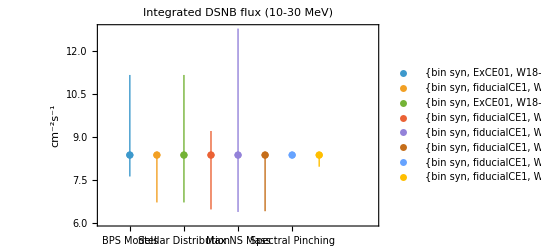

```mathematica
intDSNBplot=intDSNBerrBarPlotter[{binModIntDSNBList,singleVbinaryIntDSNBList,stellarDistIntDSNBList,engineModIntDSNBList,maxNSmassIntDSNBList,noMSWIHNHIntDSNBList,alphaIntDSNBList,criterion1P2PintDSNBList},"Integrated DSNB flux (10-30 MeV)"]
```

```mathematica
(*Export["intDSNBplot.pdf",intDSNBplot];*)
```

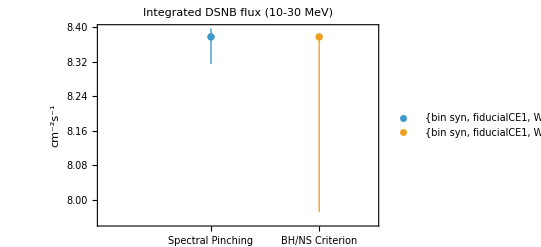

```mathematica
intDSNBplotZoomed=intDSNBerrBarPlotter[{alphaIntDSNBList,criterion1P2PintDSNBList},"Integrated DSNB flux (10-30 MeV)"]
```

```mathematica
(*Export["intDSNBplotZoomed.pdf",intDSNBplotZoomed];*)
```

```mathematica
intDSNBplotSFR=intDSNBerrBarPlotter[{binModIntDSNBList,singleVbinaryIntDSNBList,stellarDistIntDSNBList,engineModIntDSNBList,maxNSmassIntDSNBList,noMSWIHNHIntDSNBList,alphaIntDSNBList,criterion1P2PintDSNBList,SFRuncertaintyIntDSNBList},"Integrated DSNB flux (10-30 MeV)"]
```

-Graphics-

### SK-Gd Bounds

#### Prelims

SK-Gd integrated DSNB bound

```mathematica
(*latest constraint from SK collaboration*)
(*"Diffuse Supernova Neutrino Background Search at Super-Kamiokande" Abe et al. 2021*)
(*instead of old bound used in Kresse et al. 2021*)
intDSNBfluxBound=2.7;(*cm^-2 s^-1*)
EnuBound=17.3;(*MeV*)
(*for neutrino energies > 17.3 MeV*)
(*thus integrated from *)
```

#### Replicate fig

replicating fig 10 left from Kresse et al. 2021

```mathematica
(*-Graphics-*)
```

```mathematica
(*"W18-BH2.7-a2.0"
"W18-BH2.7-a1.0"
"W18-BH3.5-a2.0"
"W18-BH3.5-a1.0"
"W20-BH2.7-a2.0"
"W20-BH2.7-a1.0"
"W20-BH3.5-a2.0"
"W20-BH3.5-a1.0"*)
```

```mathematica
fig10EngineList={"W18-BH2.7-a2.0","W20-BH2.7-a2.0","W18-BH2.7-a1.0","W18-BH3.5-a2.0","W20-BH3.5-a2.0","W20-BH2.7-a1.0","W18-BH3.5-a1.0","W20-BH3.5-a1.0"};
```

form module to speed this process up

```mathematica
fiducialCase
```

{bin syn,fiducialCE1,W18-BH2.7-a2.0,2.7,1,BHNS,no MSW}

```mathematica
(*take in engine name and assume all other parameters are fiducial*)
(*and output list to be plotted via intDSNBerrBarPlotter*)
listGenEngine[x_]:=Module[{engineName=x},
(*chose all fiducial parameters*)
(*save for given engine model per se*)
tempDataPE=selectorRecursive[dataPE,{1,"BHNS","no MSW",engineName,"fiducialCE1"},1];
tempDataExtremaPE=extremaFinder[tempDataPE];
(*dataListPE={fiducialDataPE,tempDataExtremaPE,engineName}*)
dataListPE={{tempDataExtremaPE[[1,2]]},tempDataExtremaPE,engineName}
];(*end module*)
```

```mathematica
(*listGenEngine["W18-BH2.7-a2.0"]*)
```

```mathematica
fig10EngineListPlotData=Table[listGenEngine[x],{x,fig10EngineList}];
```

```mathematica
(*fig10EngineListPlotData[[2]]*)
```

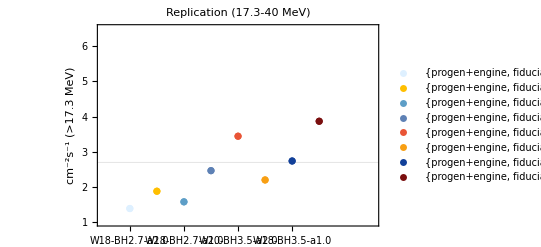

```mathematica
intDSNBplotterII[fig10EngineListPlotData,"Replication",{EnuBound,40,intDSNBfluxBound}]
```

#### Global plot (without SFR uncertainty)

get titles and list of data

```mathematica
(*make a list for comparing to SK bound later*)
globalIntDSNBList={fiducialData,globalExtremaAll,"Global"};
globalIntDSNBListnoMSW={fiducialData,globalExtremaAllnoMSW,"Global (no MSW)"};
```

plot them

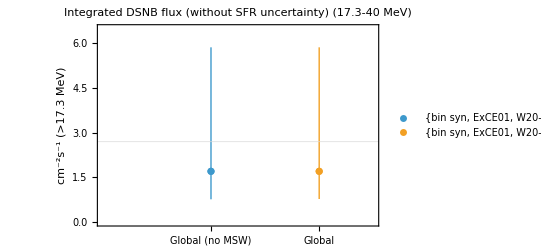

```mathematica
globalIntDSNBskBoundPlot=intDSNBplotter[{globalIntDSNBListnoMSW,globalIntDSNBList},"Integrated DSNB flux (without SFR uncertainty)",{EnuBound,40,intDSNBfluxBound}]
```

```mathematica
(*Export["globalIntDSNBskBoundPlot.pdf",globalIntDSNBskBoundPlot]*)
```

compare global with all uncertainties

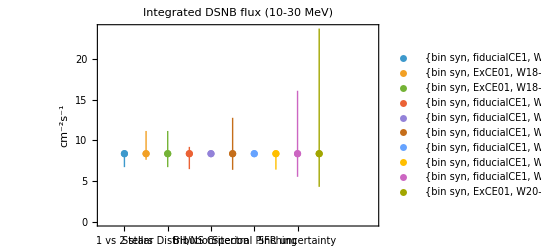

```mathematica
intDSNBplotSFRGlobal=intDSNBerrBarPlotter[{singleVbinaryIntDSNBList,binModIntDSNBList,stellarDistIntDSNBList,engineModIntDSNBList,criterion1P2PintDSNBList,maxNSmassIntDSNBList,alphaIntDSNBList,noMSWIHNHIntDSNBList,SFRuncertaintyIntDSNBList,globalIntDSNBList},"Integrated DSNB flux (10-30 MeV)"]
```

```mathematica
(*Export["intDSNBplotSFRGlobal.pdf",intDSNBplotSFRGlobal];*)
```

#### Local extrema plot

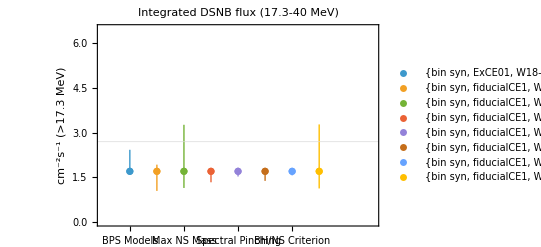

```mathematica
localIntDSNBskBoundPlot=intDSNBplotter[{binModIntDSNBList,engineModIntDSNBList,maxNSmassIntDSNBList,noMSWIHNHIntDSNBList,alphaIntDSNBList,singleVbinaryIntDSNBList,criterion1P2PintDSNBList,SFRuncertaintyIntDSNBList},"Integrated DSNB flux",{EnuBound,40,intDSNBfluxBound}]
```

```mathematica
(*Export["localIntDSNBskBoundPlot.pdf",localIntDSNBskBoundPlot];*)
```

also compare with global

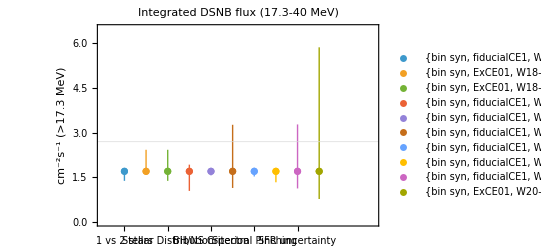

```mathematica
localGlobalIntDSNBskBoundPlot=intDSNBplotter[{singleVbinaryIntDSNBList,binModIntDSNBList,stellarDistIntDSNBList,engineModIntDSNBList,criterion1P2PintDSNBList,maxNSmassIntDSNBList,alphaIntDSNBList,noMSWIHNHIntDSNBList,SFRuncertaintyIntDSNBList,globalIntDSNBList},"Integrated DSNB flux",{EnuBound,40,intDSNBfluxBound}]
```

```mathematica
(*Export["localGlobalIntDSNBskBoundPlot.pdf",localGlobalIntDSNBskBoundPlot];*)
```

make a table of these

```mathematica
(*make a table of these*)
LocalIntDSNBskBoundData=intDSNBplotter3[{singleVbinaryIntDSNBList,binModIntDSNBList,stellarDistIntDSNBList,engineModIntDSNBList,criterion1P2PintDSNBList,maxNSmassIntDSNBList,alphaIntDSNBList,noMSWIHNHIntDSNBList,SFRuncertaintyIntDSNBList,globalIntDSNBList},"Integrated DSNB flux",{EnuBound,40,intDSNBfluxBound}];
```

```mathematica
tableTitle={{"Integrated DSNB (cm^-2s^-1)","E_ν={"<>ToString[EnuBound]<>"-40 MeV}"},{{"min","fiducial","max"},"case"}}
```

{{Integrated DSNB (cm^-2s^-1),E_ν={17.3-40 MeV}},{{min,fiducial,max},case}}

```mathematica
tableData=Join[tableTitle,LocalIntDSNBskBoundData[[All,1;;2]]]
```

{{Integrated DSNB (cm^-2s^-1),E_ν={17.3-40 MeV}},{{min,fiducial,max},case},{{1.38655,1.70638,1.70638},1 vs 2 stars},{{1.59229,1.70638,2.42953},BPS Models},{{1.38655,1.70638,2.42953},Stellar Distribution},{{1.04896,1.70638,1.93021},CE Models},{{1.56983,1.70638,1.70638},BH/NS Criterion},{{1.14767,1.70638,3.26902},Max NS Mass},{{1.53272,1.70638,1.82227},Spectral Pinching},{{1.33838,1.70638,1.70638},Flavor Conversions},{{1.13121,1.70638,3.2809},SFR uncertainty},{{0.777002,1.70638,5.87023},Global}}

```mathematica
intDSNBtable=Grid[Join[tableTitle,LocalIntDSNBskBoundData[[All,1;;2]]],Frame->All]
```

Integrated DSNB (cm^-2s^-1) | E_ν={17.3-40 MeV}
{min,fiducial,max} | case
{1.38655,1.70638,1.70638} | 1 vs 2 stars
{1.59229,1.70638,2.42953} | BPS Models
{1.38655,1.70638,2.42953} | Stellar Distribution
{1.04896,1.70638,1.93021} | CE Models
{1.56983,1.70638,1.70638} | BH/NS Criterion
{1.14767,1.70638,3.26902} | Max NS Mass
{1.53272,1.70638,1.82227} | Spectral Pinching
{1.33838,1.70638,1.70638} | Flavor Conversions
{1.13121,1.70638,3.2809} | SFR uncertainty
{0.777002,1.70638,5.87023} | Global

```mathematica
(*Export["intDSNBtable.pdf",intDSNBtable];*)
```

```mathematica
TeXForm[intDSNBtable]
```

\begin{array}{cc}
 \left.\text{Integrated DSNB (}\text{cm}^{-2}s^{-1}\right) & E_{\nu }\text{=$\{$17.3-40 MeV$\}$} \\
 \{\text{min},\text{fiducial},\text{max}\} & \text{case} \\
 \{1.38655,1.70638,1.70638\} & \text{1 vs 2 stars} \\
 \{1.59229,1.70638,2.42953\} & \text{BPS Models} \\
 \{1.38655,1.70638,2.42953\} & \text{Stellar Distribution} \\
 \{1.04896,1.70638,1.93021\} & \text{CE Models} \\
 \{1.56983,1.70638,1.70638\} & \text{BH/NS Criterion} \\
 \{1.14767,1.70638,3.26902\} & \text{Max NS Mass} \\
 \{1.53272,1.70638,1.82227\} & \text{Spectral Pinching} \\
 \{1.33838,1.70638,1.70638\} & \text{Flavor Conversions} \\
 \{1.13121,1.70638,3.2809\} & \text{SFR uncertainty} \\
 \{0.777002,1.70638,5.87023\} & \text{Global} \\
\end{array}

exporting the plot/table data for python

```mathematica
intDSNBPlotData=Map[{ExportString[#[[1]],"PythonExpression"],ToString[#[[2]]]}&,LocalIntDSNBskBoundData]
```

{{[1.3865460453269467, 1.706375103307346, 1.706375103307346],1 vs 2 stars},{[1.59229211250301, 1.706375103307346, 2.429531679123016],BPS Models},{[1.3865460453269467, 1.706375103307346, 2.429531679123016],Stellar Distribution},{[1.0489593055492512, 1.706375103307346, 1.9302144056294823],CE Models},{[1.569830239439969, 1.706375103307346, 1.706375103307346],BH/NS Criterion},{[1.147665367927925, 1.706375103307346, 3.2690249794965993],Max NS Mass},{[1.5327175908222863, 1.706375103307346, 1.8222720890063038],Spectral Pinching},{[1.3383777129070993, 1.706375103307346, 1.706375103307346],Flavor Conversions},{[1.1312139542642206, 1.706375103307346, 3.28090263424268],SFR uncertainty},{[0.7770016424863659, 1.706375103307346, 5.870227306562492],Global}}

```mathematica
(*Export["intDSNBPlotData.csv",intDSNBPlotData]*)
```

### without SK bound

#### 9-40 vs 16-40 MeV ranges

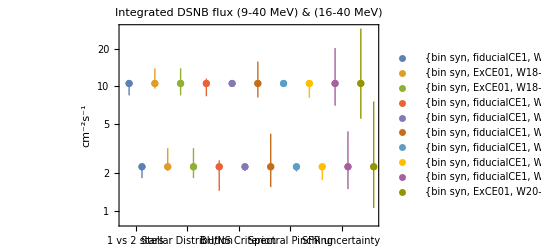

```mathematica
intDSNBplotterDual[{singleVbinaryIntDSNBList,binModIntDSNBList,stellarDistIntDSNBList,engineModIntDSNBList,criterion1P2PintDSNBList,maxNSmassIntDSNBList,alphaIntDSNBList,noMSWIHNHIntDSNBList,SFRuncertaintyIntDSNBList,globalIntDSNBList},"Integrated DSNB flux",{9,40},{16,40}]
```

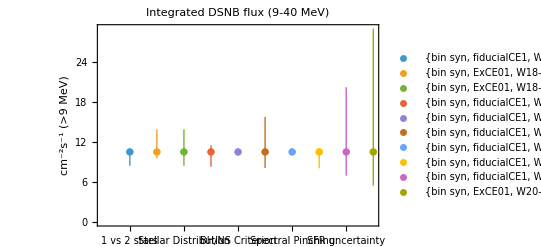

```mathematica
intDSNBplotter0[{singleVbinaryIntDSNBList,binModIntDSNBList,stellarDistIntDSNBList,engineModIntDSNBList,criterion1P2PintDSNBList,maxNSmassIntDSNBList,alphaIntDSNBList,noMSWIHNHIntDSNBList,SFRuncertaintyIntDSNBList,globalIntDSNBList},"Integrated DSNB flux",{9,40}]
```

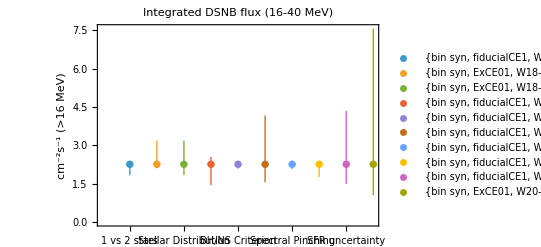

```mathematica
intDSNBplotter0[{singleVbinaryIntDSNBList,binModIntDSNBList,stellarDistIntDSNBList,engineModIntDSNBList,criterion1P2PintDSNBList,maxNSmassIntDSNBList,alphaIntDSNBList,noMSWIHNHIntDSNBList,SFRuncertaintyIntDSNBList,globalIntDSNBList},"Integrated DSNB flux",{16,40}]
```

exporting the plot/table data for python

```mathematica
(*make tables of integrated values*)
(*for 9 to 40 MeV*)
localINDSNBdata940=intDSNBplotter3[{singleVbinaryIntDSNBList,binModIntDSNBList,stellarDistIntDSNBList,engineModIntDSNBList,criterion1P2PintDSNBList,maxNSmassIntDSNBList,alphaIntDSNBList,noMSWIHNHIntDSNBList,SFRuncertaintyIntDSNBList,globalIntDSNBList},"Integrated DSNB flux",{9,40,intDSNBfluxBound}];
(*for 16 to 40 MeV*)
localINDSNBdata1640=intDSNBplotter3[{singleVbinaryIntDSNBList,binModIntDSNBList,stellarDistIntDSNBList,engineModIntDSNBList,criterion1P2PintDSNBList,maxNSmassIntDSNBList,alphaIntDSNBList,noMSWIHNHIntDSNBList,SFRuncertaintyIntDSNBList,globalIntDSNBList},"Integrated DSNB flux",{16,40,intDSNBfluxBound}];
```

```mathematica
(*prepare for export*)
intDSNBPlotData940=Map[{ExportString[#[[1]],"PythonExpression"],ToString[#[[2]]]}&,localINDSNBdata940]
intDSNBPlotData1640=Map[{ExportString[#[[1]],"PythonExpression"],ToString[#[[2]]]}&,localINDSNBdata1640]
```

{{[8.468403817034982, 10.550125036321027, 10.550125036321027],1 vs 2 stars},{[9.590258393620035, 10.550125036321027, 13.957882787468321],BPS Models},{[8.468403817034982, 10.550125036321027, 13.957882787468321],Stellar Distribution},{[8.327162064275495, 10.550125036321027, 11.557785283804954],CE Models},{[10.06882858355618, 10.550125036321027, 10.550125036321027],BH/NS Criterion},{[8.148667443331112, 10.550125036321027, 15.800470741174298],Max NS Mass},{[10.530640739317805, 10.550125036321027, 10.546919163155383],Spectral Pinching},{[8.098725891177075, 10.550125036321027, 10.550125036321027],Flavor Conversions},{[6.994035858344962, 10.550125036321027, 20.285066839152524],SFR uncertainty},{[5.4979428431302875, 10.550125036321027, 29.09688026240048],Global}}

{{[1.835356694763986, 2.2631020462251397, 2.2631020462251397],1 vs 2 stars},{[2.103784323132869, 2.2631020462251397, 3.1882506776199317],BPS Models},{[1.835356694763986, 2.2631020462251397, 3.1882506776199317],Stellar Distribution},{[1.4523852949869416, 2.2631020462251397, 2.54960787262455],CE Models},{[2.094623519162365, 2.2631020462251397, 2.2631020462251397],BH/NS Criterion},{[1.5562529301216828, 2.2631020462251397, 4.168717004793701],Max NS Mass},{[2.0731973975820512, 2.2631020462251397, 2.3862922691136004],Spectral Pinching},{[1.7660397507748267, 2.2631020462251397, 2.2631020462251397],Flavor Conversions},{[1.500287134787552, 2.2631020462251397, 4.351339544645653],SFR uncertainty},{[1.0546043352471748, 2.2631020462251397, 7.567886535805356],Global}}

```mathematica
(*(*export integrated DSNB from 9 to 40 MeV*)
Export["intDSNBPlotData940.csv",intDSNBPlotData940]
(*export integrated DSNB from 16 to 40 MeV*)
Export["intDSNBPlotData1640.csv",intDSNBPlotData1640]*)
```

```mathematica
(*minimum diff*)
localINDSNBdata940[[All, 1]][[All,2]]-localINDSNBdata940[[All, 1]][[All,1]]
localINDSNBdata1640[[All, 1]][[All,2]]-localINDSNBdata1640[[All, 1]][[All,1]]
```

{2.08172,0.959867,2.08172,2.22296,0.481296,2.40146,0.0194843,2.4514,3.55609,5.05218}

{0.427745,0.159318,0.427745,0.810717,0.168479,0.706849,0.189905,0.497062,0.762815,1.2085}

```mathematica
(*maximia diff*)
localINDSNBdata940[[All, 1]][[All,3]]-localINDSNBdata940[[All, 1]][[All,2]]
localINDSNBdata1640[[All, 1]][[All,3]]-localINDSNBdata1640[[All, 1]][[All,2]]
```

{0.,3.40776,3.40776,1.00766,0.,5.25035,-0.00320587,0.,9.73494,18.5468}

{0.,0.925149,0.925149,0.286506,0.,1.90561,0.12319,0.,2.08824,5.30478}

```mathematica
localINDSNBdata940[[All, 1]][[All,3]]
localINDSNBdata940[[All, 1]][[All,2]]
```

{10.5501,13.9579,13.9579,11.5578,10.5501,15.8005,10.5469,10.5501,20.2851,29.0969}

{10.5501,10.5501,10.5501,10.5501,10.5501,10.5501,10.5501,10.5501,10.5501,10.5501}

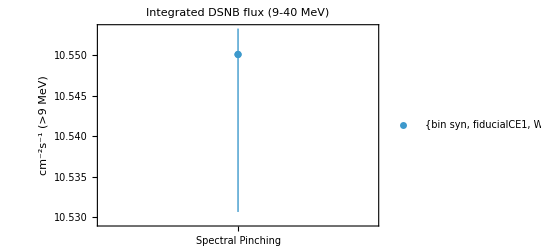

```mathematica
intDSNBplotter0[{alphaIntDSNBList},"Integrated DSNB flux",{9,40}]
```

```mathematica
localINDSNBdata940[[All,1]]
```

{{8.4684,10.5501,10.5501},{9.59026,10.5501,13.9579},{8.4684,10.5501,13.9579},{8.32716,10.5501,11.5578},{10.0688,10.5501,10.5501},{8.14867,10.5501,15.8005},{10.5306,10.5501,10.5469},{8.09873,10.5501,10.5501},{6.99404,10.5501,20.2851},{5.49794,10.5501,29.0969}}

#### make a table (9-40 and 16-40 MeV ranges)

make a table of these

```mathematica
(*make a table of these*)
LocalIntDSNBdata940=intDSNBplotter3[{singleVbinaryIntDSNBList,binModIntDSNBList,stellarDistIntDSNBList,engineModIntDSNBList,criterion1P2PintDSNBList,maxNSmassIntDSNBList,alphaIntDSNBList,noMSWIHNHIntDSNBList,SFRuncertaintyIntDSNBList,globalIntDSNBList},"Integrated DSNB flux",{9,40,intDSNBfluxBound}];
LocalIntDSNBdata1640=intDSNBplotter3[{singleVbinaryIntDSNBList,binModIntDSNBList,stellarDistIntDSNBList,engineModIntDSNBList,criterion1P2PintDSNBList,maxNSmassIntDSNBList,alphaIntDSNBList,noMSWIHNHIntDSNBList,SFRuncertaintyIntDSNBList,globalIntDSNBList},"Integrated DSNB flux",{16,40,intDSNBfluxBound}];
```

```mathematica
tableTitle940={{"Integrated DSNB (cm^-2s^-1)","E_ν={9-40 MeV}"},{{"min","fiducial","max"},"case"}}
tableTitle1640={{"Integrated DSNB (cm^-2s^-1)","E_ν={16-40 MeV}"},{{"min","fiducial","max"},"case"}}
```

{{Integrated DSNB (cm^-2s^-1),E_ν={9-40 MeV}},{{min,fiducial,max},case}}

{{Integrated DSNB (cm^-2s^-1),E_ν={16-40 MeV}},{{min,fiducial,max},case}}

```mathematica
(*create table to show*)
tableData940=Join[tableTitle940,LocalIntDSNBdata940[[All,1;;2]]];
tableData1640=Join[tableTitle1640,LocalIntDSNBdata1640[[All,1;;2]]];
```

```mathematica
intDSNBtable940=Grid[tableData940,Frame->All]
```

Integrated DSNB (cm^-2s^-1) | E_ν={9-40 MeV}
{min,fiducial,max} | case
{8.4684,10.5501,10.5501} | 1 vs 2 stars
{9.59026,10.5501,13.9579} | BPS Models
{8.4684,10.5501,13.9579} | Stellar Distribution
{8.32716,10.5501,11.5578} | CE Models
{10.0688,10.5501,10.5501} | BH/NS Criterion
{8.14867,10.5501,15.8005} | Max NS Mass
{10.5306,10.5501,10.5469} | Spectral Pinching
{8.09873,10.5501,10.5501} | Flavor Conversions
{6.99404,10.5501,20.2851} | SFR uncertainty
{5.49794,10.5501,29.0969} | Global

```mathematica
intDSNBtable1640=Grid[tableData1640,Frame->All]
```

Integrated DSNB (cm^-2s^-1) | E_ν={16-40 MeV}
{min,fiducial,max} | case
{1.83536,2.2631,2.2631} | 1 vs 2 stars
{2.10378,2.2631,3.18825} | BPS Models
{1.83536,2.2631,3.18825} | Stellar Distribution
{1.45239,2.2631,2.54961} | CE Models
{2.09462,2.2631,2.2631} | BH/NS Criterion
{1.55625,2.2631,4.16872} | Max NS Mass
{2.0732,2.2631,2.38629} | Spectral Pinching
{1.76604,2.2631,2.2631} | Flavor Conversions
{1.50029,2.2631,4.35134} | SFR uncertainty
{1.0546,2.2631,7.56789} | Global

#### 0-20 MeV and 20-40 MeV ranges

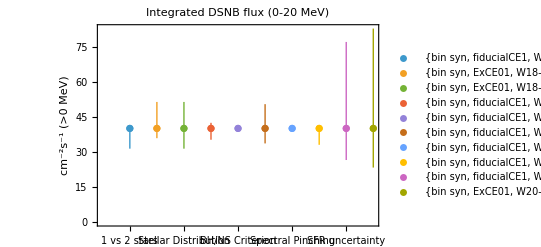

```mathematica
intDSNBplotter0[{singleVbinaryIntDSNBList,binModIntDSNBList,stellarDistIntDSNBList,engineModIntDSNBList,criterion1P2PintDSNBList,maxNSmassIntDSNBList,alphaIntDSNBList,noMSWIHNHIntDSNBList,SFRuncertaintyIntDSNBList,globalIntDSNBList},"Integrated DSNB flux",{0,20}]
```

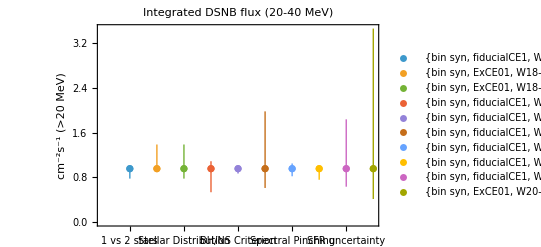

```mathematica
intDSNBplotter0[{singleVbinaryIntDSNBList,binModIntDSNBList,stellarDistIntDSNBList,engineModIntDSNBList,criterion1P2PintDSNBList,maxNSmassIntDSNBList,alphaIntDSNBList,noMSWIHNHIntDSNBList,SFRuncertaintyIntDSNBList,globalIntDSNBList},"Integrated DSNB flux",{20,40}]
```

### Evading bounds

#### test greatest contributions

since bin syn model and maxNS mass are the largest contributions

see if any of these are fully ruled out

```mathematica
Length[maxMnsData]
Length[binModData]
```

4

6

```mathematica
maxMnsData[[1,1]]
maxMnsData[[1,1,4]]
binModData[[1,1,2]]
```

{bin syn,fiducialCE1,W18-BH2.3-a2.0,2.3,a2.0,1,BHNS,no MSW}

2.3

ExCE01

```mathematica
Table[maxMnsData[[i]][[1,4]],{i,1,Length[maxMnsData]}]
```

{2.3,2.7,3.1,3.5}

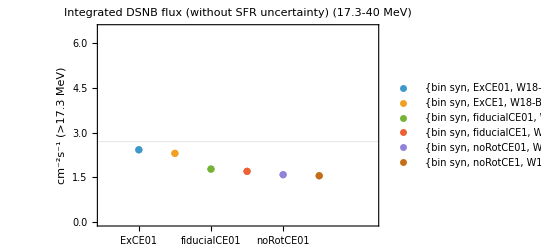

```mathematica
intDSNBplotter[skBoundEvader[binModData,2],"Integrated DSNB flux (without SFR uncertainty)",{EnuBound,40,intDSNBfluxBound}]
```

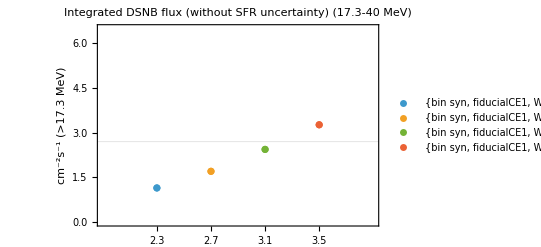

```mathematica
localMaxNSmassIntDSNBskBoundPlot=intDSNBplotter[skBoundEvader[maxMnsData,4],"Integrated DSNB flux (without SFR uncertainty)",{EnuBound,40,intDSNBfluxBound}]
```

```mathematica
(*Export["localMaxNSmassIntDSNBskBoundPlot.pdf",localMaxNSmassIntDSNBskBoundPlot];*)
```

#### attempt to evade bounds

see if fixing to each maxNSmass and varying everything else

can you evade the SK bound?

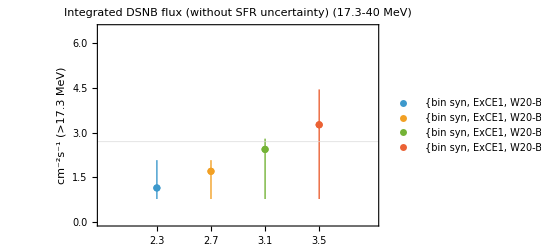

```mathematica
MaxNSmassIntDSNBskBoundAttemptToEvadePlot=intDSNBplotter[skBoundEvaderII[maxMnsData,4],"Integrated DSNB flux (without SFR uncertainty)",{EnuBound,40,intDSNBfluxBound}]
```

```mathematica
(*Export["MaxNSmassIntDSNBskBoundAttemptToEvadePlot.pdf",MaxNSmassIntDSNBskBoundAttemptToEvadePlot];*)
```

look at range of SK integrated DSNB constraint

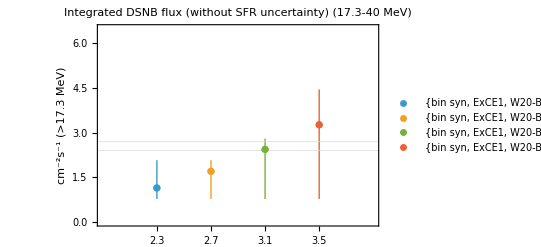

```mathematica
MaxNSmassIntDSNBskBoundAttemptToEvadePlot2=intDSNBplotter2[skBoundEvaderII[maxMnsData,4],"Integrated DSNB flux (without SFR uncertainty)",{EnuBound,40,intDSNBfluxBound}]
```

```mathematica
(*Export["MaxNSmassIntDSNBskBoundAttemptToEvadePlot2.pdf",MaxNSmassIntDSNBskBoundAttemptToEvadePlot2];*)
```

## Latest SK-Gd Constraint Plot

replicating fig 12 from Abe et al. 2025 (latest constraints on DSNB flux from SK-Gd)

```mathematica
(*replicating fig 12 from Abe et al.2025 (latest constraints on DSNB flux from SK-Gd)*)
```

### modules

#### data binner

```mathematica
(*make bins for data*)
(*take in data: {{x,y},...} of Enu (MeV), DSNB flux in cm^-2 MeV^-1 s^-1*)
(*and uneven bin intervals {{x1,x2},{x3,x4}...}*)
(*then return {{x1,x2,<y>},{x3,x4,<y>},...}*)
dataBinner[in1_,in2_]:=Module[{data=in1,binIntervals=in2},
newData={};
Do[
tempEmin=binIntervals[[i,1]];
tempEmax=binIntervals[[i,2]];
tempData=Select[data,(tempEmin<=#[[1]]<=tempEmax)&];
avgDSNBFlux=Mean[tempData[[All,2]]];
AppendTo[newData,{{tempEmin,tempEmax},avgDSNBFlux}];
,{i,1,Length[binIntervals]}
];(*end do loop*)
(*output the new data*)
newData
];(*end module*)
```

#### binned data Converter

```mathematica
(*take in {{data,"name"},...}*)
(*convert into plot ready data*)
binnedDataConverter[x_]:=Module[{fullDataNames=x},
allData={};

Do[
(*get data and name*)
tempdata=fullDataNames[[i,1]];
tempName=fullDataNames[[i,2]];
(*start loop over data*)
(*convert data to error bar points*)
tempNewData={};
(*Print[tempdata,tempName];*)
	Do[
		(*format point as {{x+/-max/min, y}...}*)
		(*Print[tempdata[[j]]];*)
		(*get mean of x data*)
		tempMean=(tempdata[[j]][[1,2]]+tempdata[[j]][[1,1]])/2;
		(*tempMean=Median[{tempdata[[j]][[1,2]],tempdata[[j]][[1,1]]}];*)
		tempMin=tempMean-tempdata[[j]][[1,1]];
		tempMax=tempdata[[j]][[1,2]]-tempMean;
		(*create point {x+/-max/min, y}*)
		tempNewPoint={Around[tempMean,{tempMin,tempMax}],tempdata[[j]][[2]]};
		(*Print[tempNewPoint];*)
		(*save to new data*)
		AppendTo[tempNewData,tempNewPoint],
	{j,1,Length[tempdata]}
	];(*end internal loop*)
(*save all new data to list of data sets with its corresponding name*)
AppendTo[allData,{tempNewData,tempName}];
,{i,1,Length[fullDataNames]}];(*end do loop*)
(*output all data*)
allData
];(*end module*)
```

#### error bar point maker

```mathematica
(*take in data as*)
(*(*{{xmin,xmax,xval},{ymin,ymax,yval}},...*)*)
(*convert into plot ready data*)
(*(*{{x+/-max/min, y+/-max/min}...}*)*)
errorBarPointMaker[x_]:=Module[{data=x},

(*create empty list for output*)
outputData={};

(*separate into x, y, and y (with SFR uncertainty)*)
(*each formated as {{min,max,val},...}*)
xData=Transpose[data][[1,All]];
yData=Transpose[data][[2,All]];

(*convert data to create error bar points*)
Do[
(*get {min, max}*)
tempMinMaxX={xData[[i]][[3]]-xData[[i]][[1]],xData[[i]][[2]]-xData[[i]][[3]]};
tempMinMaxY={yData[[i]][[3]]-yData[[i]][[1]],yData[[i]][[2]]-yData[[i]][[3]]};

(*create x error bar point*)
tempX=Around[xData[[i]][[3]],tempMinMaxX];
(*create y error bar point*)
tempY=Around[yData[[i]][[3]],tempMinMaxY];

(*create plot point without SFR uncertainty*)
tempPoint = {tempX,tempY};
(*Print[i,tempPoint];*)
(*and append to full output*)
AppendTo[outputData,tempPoint];
,{i,1,Length[xData]}];
(*end do loop*)

(*output all data*)
(*without and with SFR uncertainty respectively*)
outputData
];(*end module*)
```

#### converted binned data plotter

```mathematica
(*take in {{data,"name"},...}*)
(*where the binned data is now in format of*)
(*{{x+/-max/min, y}...}*)
convertedBinDataPlotter[x_]:=Module[{listData=x},
(*separate into data sets and names list for legends*)
dataSets=listData[[All,1]];
nameSets=listData[[All,2]];
ListLogPlot[dataSets,
PlotLegends->nameSets,
PlotRange->{{9,31},{10^-2,8*10^2}},
AxesLabel->{"MeV","cm^-2s^-1MeV^-1"},
PlotLabel->"DSNB Flux";
PlotStyle->{defaultColor[[-1]],Gray,Gray,defaultColor[[4]],{Dashed,defaultColor[[8]]},{Dashed,defaultColor[[4]]},{defaultColor[[1]]}}
](*end plot*)

];(*end module*)
```

```mathematica
defaultColor
defaultColor[[8]]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

RGBColor[1, 0.75, 0]

```mathematica
Gray
```

GrayLevel[0.5]

#### Interpolation binner

interpolate fiducial or global extrema DSNB flux

can use module herein to create binned average DSNB flux

```mathematica
(*input data must be in format of fiducial data*)
(*taken in Enu bin intervals and min and max ranges*)
interpolatorBinner[x_,y_,e1_,e2_]:=Module[{DSNBFluxData=x,binIntervals=y,Emin=e1,Emax=e2},
(*interpolate the data in same format as fiducial data format*)
tempFunc=Interpolation[DSNBFluxData];
(*create tabulated data*)
tempTabData=Table[{i,tempFunc[i]},{i,Emin,Emax,0.1}];
(*bin all these points*)
dataBinner [tempTabData,binIntervals]

];
```

#### converted binned data integrator

convert binned DSNB flux data into event rates per bin

```mathematica
binnedDataIntegrator[x_]:=Module[{allbinnedData=x},
(*format as {{integratedDSNB, case},...}*)
(*in units of cm^-2 s^-1*)
output={};
Do[
(*get the case*)
tempCase=binnedData[[2]];
(*tempData3=binnedData[[1]];*)
tempData3=binnedData[[1,-2;;-1]];
tempIntegratedDSNBvalue=Total[Table[(tempData3[[i]][[1,2]]-tempData3[[i]][[1,1]])*tempData3[[i]][[2]],{i,1,Length[tempData3]}]];
(*append to output*)
AppendTo[output,{tempIntegratedDSNBvalue,tempCase}]
,{binnedData,allbinnedData}]; (*end do outer loop for all cases*)
(*throw out the output*)
output
]
```

#### DSNB flux selector

```mathematica
(*take in DSNB flux data*)
(*in format of {{Enu,flux},...}*)
(*and select only in relevant energy range*)
dsnbSelector[z_,x_,y_]:=Module[{dsnbFlux=z,min=x,max=y},
Select[dsnbFlux ,min<#[[1]]<max&]
];(*end module*)
```

#### binner

take energy bins and DSNB flux and create listStepPlot data

```mathematica
(*create data for ListStepPlot*)
(*based on DSNB flux data {{Enu,flux}...}, and energy bins {{x1a,x1b},{x2a,x2b},...}*)
(*x is energy Enu and y is DSNB flux (cm^-2 s^-1 MeV^-1)*)
binner[x_,y_]:=Module[{data=x,bins=y},
(*select only DSNB data within the range of max and min energy bin values*)
tempData=Select[data,bins[[1,1]]<=#[[1]]<=bins[[-1,2]]&];

(*make function of selected DSNB data*)
tempFunc=Interpolation[tempData];

(*get y i.e. DSNB flux values*)
yList={};
(*get midpoints then get corresponding DSNB flux*)
Do[
tempMid=(bins[[i]][[2]]+bins[[i]][[1]])/2;
tempY=tempFunc[tempMid];
AppendTo[yList,tempY];
,{i,1,Length[bins]}]; (*end do loop*)
(*get x start values*)
xStarts=bins[[All,1]];

(*following format required*)
(*add last x value*)
(*xStarts2= Join[xStarts,{bins[[-1,2]]}];*)
(*add last midpoint*)
xStarts2= Join[xStarts,{tempMid}];
(*add duplicate last y value*)
yList2=Join[yList,{yList[[-1]]}];
(*format output data{{x,y}}*)
outputList=Table[{xStarts2[[i]],yList2[[i]]},{i,1,Length[yList2]}];
(*toss out the output*)
outputList
];(*module*)
```

### fiducial case

#### binning prelims

chose bin range

```mathematica
(*chose bin range*)
(*in MeV*)
EnuBinMin=9.29;
EnuBinMax=31.29;

(*bin intervals start-end*)
(*format as {{x1,x2},{x3,x4},...}*)
(*corresponding to fig 12 or table 6 of Abe et al 2025*)
EnuBinIntervals={{9.29,11.29},{11.29,13.29},{13.29,17.29},{17.29,25.29},{25.29,31.29}};
```

```mathematica
(*from table V of Abe et al. 2021*)
(*slightly different binning*)
EnuBinIntervals2={{9.3,11.3},{11.3,13.3},{13.3,15.3},{15.3,17.3},{17.3,19.3},{19.3,21.3},{21.3,23.3},{23.3,25.3},{25.3,27.3},{27.3,29.3},{29.3,31.3}};
EnuBinMax2=9.3;
EnuBinMin2=31.3;
```

#### DSNB flux interpolation and Binning

for fiducial case

```mathematica
fiducialData[[1,1]]
(*fiducialData[[1,-1]]*)
```

{bin syn,fiducialCE1,W18-BH2.7-a2.0,2.7,a2.0,1,BHNS,no MSW}

```mathematica
binnedfidInterpData=interpolatorBinner[fiducialData[[1,-1]],EnuBinIntervals,EnuBinMin,EnuBinMax]
```

{{{9.29,11.29},1.76434},{{11.29,13.29},1.13963},{{13.29,17.29},0.598283},{{17.29,25.29},0.175369},{{25.29,31.29},0.038185}}

for global extrema (without SFR)

```mathematica
(*max and min respectively*)
(*globalExtremaAll[[1,2]]*)
(*globalExtremaAll[[1,2]]*)
```

```mathematica
(*only BHNS (i.e.throw away all NS i.e.without criterion case) and 2P criterion (i.e.do not use 1P criterion)*)
(*global extrema*)
binGlobalMax=interpolatorBinner[globalExtremaAll[[1,2]][[-1]],EnuBinIntervals,EnuBinMin,EnuBinMax];
binGlobalMin=interpolatorBinner[globalExtremaAll[[2,2]][[-1]],EnuBinIntervals,EnuBinMin,EnuBinMax];
(*global extrema no MSW*)
binGlobalMaxNoMSW=interpolatorBinner[globalExtremaAllnoMSW[[1,2]][[-1]],EnuBinIntervals,EnuBinMin,EnuBinMax];
binGlobalMinNoMSW=interpolatorBinner[globalExtremaAllnoMSW[[2,2]][[-1]],EnuBinIntervals,EnuBinMin,EnuBinMax];
```

```mathematica
binGlobalMax
```

{{{9.29,11.29},4.34719},{{11.29,13.29},3.02532},{{13.29,17.29},1.73947},{{17.29,25.29},0.583964},{{25.29,31.29},0.146466}}

#### Binning comparison data

get other theoretical predictions from Kaplinghat et al. 2000 and Nakazato et al. 2015

```mathematica
(*DSNB flux other theoretical predictions from optimistic Kaplinghat et al.2000 and pessimistic Nakazato et al.2015*)
(*from table 6 from Abe et al. 2025*)
(*corresponds to same Enu intervals in EnuBinIntervals*)
(*upper and lower bounds per interval*)
dsnbFluxTheoryLow={0.2,0.13,0.67,0.02,0.01};
dsnbFluxTheoryHigh={2.4,1.66,0.94,0.3,0.07};
```

bin all these points

```mathematica
(*bin the other theoretical bounds*)
binnedOtherPredictLow=Table[{EnuBinIntervals[[i]],dsnbFluxTheoryLow[[i]]},{i,1,Length[EnuBinIntervals]}]
binnedOtherPredictHigh=Table[{EnuBinIntervals[[i]],dsnbFluxTheoryHigh[[i]]},{i,1,Length[EnuBinIntervals]}]
```

{{{9.29,11.29},0.2},{{11.29,13.29},0.13},{{13.29,17.29},0.67},{{17.29,25.29},0.02},{{25.29,31.29},0.01}}

{{{9.29,11.29},2.4},{{11.29,13.29},1.66},{{13.29,17.29},0.94},{{17.29,25.29},0.3},{{25.29,31.29},0.07}}

observed DSNB flux at joint super-kamiokande VI+VII

```mathematica
(*observed DSNB flux at joint super-kamiokande VI+VII*)
(*from table 6 from Abe et al. 2025*)
(*observed upper limit in cm^-2 MeV^-1 s^-1*)
(*includes SK-VI+VII*)
(*boosted decision tree BDT algorithm for neutron detection in pure water*)
(*956.2 days*)
obsSKVIVIIBDT={33.20,8.14,2.76,0.37,0.16};
(*neutral network NN algorithm, retrained BDT to include neutron cpatures on Gd*)
(*956.2 days*)
obsSKVIVIINN={23.79,7.48,3.07,0.37,0.13};
```

observed DSNB flux at super-kamiokande VI only

```mathematica
(*observed DSNB flux at super-kamiokande VI ONLY*)
(*from table 6 from Abe et al. 2025*)
(*observed upper limit in cm^-2 MeV^-1 s^-1*)
(*includes SK-VI+VII*)
(*only boosted decision tree BDT algorithm for neutron detection in pure water*)
(*956.2 days*)
obsSKVIBDT={37.30,20.43,4.77,0.17,0.04};
```

observed DSNB flux at at super-kamiokande IV only

```mathematica
(*observed DSNB flux at super-kamiokande IV ONLY*)
(*from table 5 from Abe et al. 2021*)
(*observed upper limit in cm^-2 MeV^-1 s^-1*)
(*includes SK-VI+VII*)
(*only boosted decision tree BDT algorithm for neutron detection in pure water*)
(*NOTE: this uses slightly different binning*)
(*2970 days*)
obsSKIVBDT={37.1,20.4,9.34,3.29,0.508,0.684,0.127,0.375,0.0777,0.242,0.0709};
```

bin all these points

```mathematica
(*for SK VI+VII BDT algorithm*)
binobsSKVIVIIBDT=Table[{EnuBinIntervals[[i]],obsSKVIVIIBDT[[i]]},{i,1,Length[EnuBinIntervals]}]
(*for SK VI+VII NN algorithm*)
binobsSKVIVIINN=Table[{EnuBinIntervals[[i]],obsSKVIVIINN[[i]]},{i,1,Length[EnuBinIntervals]}]
(*for SK VI BDT algorithm*)
binobsSKVIBDT=Table[{EnuBinIntervals[[i]],obsSKVIBDT[[i]]},{i,1,Length[EnuBinIntervals]}]
```

{{{9.29,11.29},33.2},{{11.29,13.29},8.14},{{13.29,17.29},2.76},{{17.29,25.29},0.37},{{25.29,31.29},0.16}}

{{{9.29,11.29},23.79},{{11.29,13.29},7.48},{{13.29,17.29},3.07},{{17.29,25.29},0.37},{{25.29,31.29},0.13}}

{{{9.29,11.29},37.3},{{11.29,13.29},20.43},{{13.29,17.29},4.77},{{17.29,25.29},0.17},{{25.29,31.29},0.04}}

also bin the SK-IV using slightly diff bin interval

```mathematica
(*also bin the SK-IV using slightly diff bin interval*)
(*for SK IV BDT algorithm*)
binobsSKIVBDT=Table[{EnuBinIntervals2[[i]],obsSKIVBDT[[i]]},{i,1,Length[EnuBinIntervals2]}]
```

{{{9.3,11.3},37.1},{{11.3,13.3},20.4},{{13.3,15.3},9.34},{{15.3,17.3},3.29},{{17.3,19.3},0.508},{{19.3,21.3},0.684},{{21.3,23.3},0.127},{{23.3,25.3},0.375},{{25.3,27.3},0.0777},{{27.3,29.3},0.242},{{29.3,31.3},0.0709}}

#### Plotting data

testing to plot just fiducial data

```mathematica
(*form list of binned data and corresponding name*)
(*for other theoretical predictions from optimistic Kaplinghat et al.2000 and pessimistic Nakazato et al.2015*)
(*versus out fiducial case*)
binnedTheoryDataList={{binnedfidInterpData,"fiducial case"},{binnedOtherPredictLow,"theory low"},{binnedOtherPredictHigh,"theory high"}};
(*for observations*)
binnedObservDataList={{binobsSKVIVIIBDT,"observed SK VI+VII BDT"},{binobsSKVIVIINN,"observed SK VI+VII NN"},{binobsSKVIBDT,"observed SK IV BDT"},{binobsSKIVBDT,"observed SK IV BDT (2021)"}};
(*combine*)
binDataSetall=Join[binnedTheoryDataList,binnedObservDataList];
binnedPlotData=binnedDataConverter[binDataSetall];
```

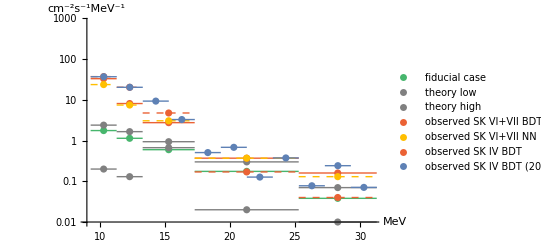

```mathematica
testSKBoundPlot=convertedBinDataPlotter[binnedPlotData]
```

```mathematica
(*Export["testSKBoundPlot.pdf",testSKBoundPlot];*)
```

```mathematica
(*Abe et al. 2025*)
-Graphics-
```

-Graphics-

compare to our theory max and min theories

```mathematica
(*form list of binned data and corresponding name*)
(*for our theory and*)
(*for max and min theory that SK considered*)
(*i.e. for other theoretical predictions from optimistic Kaplinghat et al.2000 and pessimistic Nakazato et al.2015*)
binnedTheoryDataList3={{binnedfidInterpData,"fiducial case"},{binGlobalMaxNoMSW,"max (no MSW) without SFR uncertainty"},{binGlobalMinNoMSW,"min (no MSW) without SFR uncertainty"},{binnedOtherPredictHigh,"theory high"},{binnedOtherPredictLow,"theory low"}};


(*combine*)
binnedPlotData3=binnedDataConverter[binnedTheoryDataList3];
```

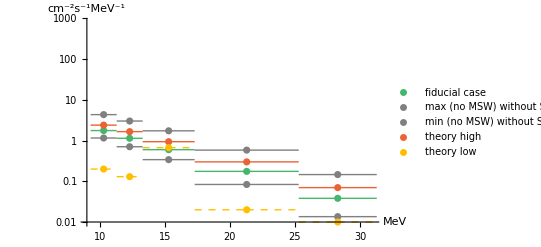

```mathematica
theorySKBoundPlot=convertedBinDataPlotter[binnedPlotData3]
```

```mathematica
(*Export["theorySKBoundPlot.pdf",theorySKBoundPlot];*)
```

```mathematica
fiducialCase
```

{bin syn,fiducialCE1,W18-BH2.7-a2.0,2.7,1,BHNS,no MSW}

plot our theory bounds

```mathematica
(*form list of binned data and corresponding name*)
(*for our theory only*)
binnedTheoryDataList2={{binnedfidInterpData,"fiducial case"},{binGlobalMaxNoMSW,"max (no MSW) without SFR uncertainty"},{binGlobalMinNoMSW,"min (no MSW) without SFR uncertainty"}};
(*for observations*)
binnedObservDataList;
(*combine*)
binDataSetall2=Join[binnedTheoryDataList2,binnedObservDataList];
binnedPlotData2=binnedDataConverter[binDataSetall2];
```

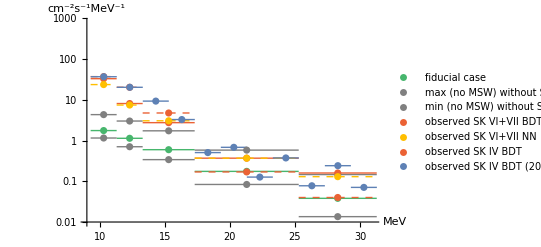

```mathematica
currentSKBoundPlot=convertedBinDataPlotter[binnedPlotData2]
```

```mathematica
(*Export["currentSKBoundPlot.pdf",currentSKBoundPlot];*)
```

export binned plot data

```mathematica
outputErrorPlotData=binDataSetall2
```

{{{{{9.29,11.29},1.76434},{{11.29,13.29},1.13963},{{13.29,17.29},0.598283},{{17.29,25.29},0.175369},{{25.29,31.29},0.038185}},fiducial case},{{{{9.29,11.29},4.34719},{{11.29,13.29},3.02532},{{13.29,17.29},1.73947},{{17.29,25.29},0.583964},{{25.29,31.29},0.146466}},max (no MSW) without SFR uncertainty},{{{{9.29,11.29},1.15752},{{11.29,13.29},0.707116},{{13.29,17.29},0.340822},{{17.29,25.29},0.0836561},{{25.29,31.29},0.0135468}},min (no MSW) without SFR uncertainty},{{{{9.29,11.29},33.2},{{11.29,13.29},8.14},{{13.29,17.29},2.76},{{17.29,25.29},0.37},{{25.29,31.29},0.16}},observed SK VI+VII BDT},{{{{9.29,11.29},23.79},{{11.29,13.29},7.48},{{13.29,17.29},3.07},{{17.29,25.29},0.37},{{25.29,31.29},0.13}},observed SK VI+VII NN},{{{{9.29,11.29},37.3},{{11.29,13.29},20.43},{{13.29,17.29},4.77},{{17.29,25.29},0.17},{{25.29,31.29},0.04}},observed SK IV BDT},{{{{9.3,11.3},37.1},{{11.3,13.3},20.4},{{13.3,15.3},9.34},{{15.3,17.3},3.29},{{17.3,19.3},0.508},{{19.3,21.3},0.684},{{21.3,23.3},0.127},{{23.3,25.3},0.375},{{25.3,27.3},0.0777},{{27.3,29.3},0.242},{{29.3,31.3},0.0709}},observed SK IV BDT (2021)}}

```mathematica
(*Export["output_ErrorPlotData.csv",outputErrorPlotData];*)
```

```mathematica
binDataSetall2
```

{{{{{9.29,11.29},1.76434},{{11.29,13.29},1.13963},{{13.29,17.29},0.598283},{{17.29,25.29},0.175369},{{25.29,31.29},0.038185}},fiducial case},{{{{9.29,11.29},4.34719},{{11.29,13.29},3.02532},{{13.29,17.29},1.73947},{{17.29,25.29},0.583964},{{25.29,31.29},0.146466}},max (no MSW) without SFR uncertainty},{{{{9.29,11.29},1.15752},{{11.29,13.29},0.707116},{{13.29,17.29},0.340822},{{17.29,25.29},0.0836561},{{25.29,31.29},0.0135468}},min (no MSW) without SFR uncertainty},{{{{9.29,11.29},33.2},{{11.29,13.29},8.14},{{13.29,17.29},2.76},{{17.29,25.29},0.37},{{25.29,31.29},0.16}},observed SK VI+VII BDT},{{{{9.29,11.29},23.79},{{11.29,13.29},7.48},{{13.29,17.29},3.07},{{17.29,25.29},0.37},{{25.29,31.29},0.13}},observed SK VI+VII NN},{{{{9.29,11.29},37.3},{{11.29,13.29},20.43},{{13.29,17.29},4.77},{{17.29,25.29},0.17},{{25.29,31.29},0.04}},observed SK IV BDT},{{{{9.3,11.3},37.1},{{11.3,13.3},20.4},{{13.3,15.3},9.34},{{15.3,17.3},3.29},{{17.3,19.3},0.508},{{19.3,21.3},0.684},{{21.3,23.3},0.127},{{23.3,25.3},0.375},{{25.3,27.3},0.0777},{{27.3,29.3},0.242},{{29.3,31.3},0.0709}},observed SK IV BDT (2021)}}

#### integrated binned DSNB flux data

```mathematica
binDataSetall2[[1,1]]
```

{{{9.29,11.29},1.76434},{{11.29,13.29},1.13963},{{13.29,17.29},0.598283},{{17.29,25.29},0.175369},{{25.29,31.29},0.038185}}

```mathematica
binDataSetall2[[1,1]][[1]][[2]]
```

1.76434

```mathematica
(binDataSetall2[[1,1]][[1]][[1,2]]-binDataSetall2[[1,1]][[1]][[1,1]])*binDataSetall2[[1,1]][[1]][[2]]
```

3.52868

```mathematica
binDataSetall2[[4]]
```

{{{{9.29,11.29},33.2},{{11.29,13.29},8.14},{{13.29,17.29},2.76},{{17.29,25.29},0.37},{{25.29,31.29},0.16}},observed SK VI+VII BDT}

```mathematica
binDataSetall2[[1]][[1,-2;;-1]]
```

{{{17.29,25.29},0.175369},{{25.29,31.29},0.038185}}

```mathematica
binDataSetall2[[1]][[1]]
```

{{{9.29,11.29},1.76434},{{11.29,13.29},1.13963},{{13.29,17.29},0.598283},{{17.29,25.29},0.175369},{{25.29,31.29},0.038185}}

look at integrated DSNB for each

assume energy range 17.3 above, i . e . last two bins

```mathematica
(*assume energy range 17.3 above, i.e. last two bins*)
```

```mathematica
integratedDSNBpoints=binnedDataIntegrator[binDataSetall2]
```

{{1.63206,fiducial case},{5.55051,max (no MSW) without SFR uncertainty},{0.750529,min (no MSW) without SFR uncertainty},{3.92,observed SK VI+VII BDT},{3.74,observed SK VI+VII NN},{1.6,observed SK IV BDT},{0.6258,observed SK IV BDT (2021)}}

using all SK observed bounds

```mathematica
Mean[integratedDSNBpoints[[-3;;-1]][[All,1]]]
```

1.9886

using just SK BDT neutron capture identification algorithm

```mathematica
Mean[integratedDSNBpoints[[{-3,-1}]][[All,1]]]
```

2.1829

create table

```mathematica
(*make rows*)
titleRow={{"integrated DSNB(cm^-2s^-1)","Scenario"}};
row1={{Mean[integratedDSNBpoints[[{-3,-1}]][[All,1]]],"average (BDT only)"},{Mean[integratedDSNBpoints[[-3;;-1]][[All,1]]],"average"}};
row2=integratedDSNBpoints[[-3;;-1]];(*only observed SK*)

integratedDSNBtabRows=Join[titleRow,row1,row2];
```

```mathematica
integratedDSNBtable=Grid[integratedDSNBtabRows,Frame->{{True,True},{1,0}}]
```

integrated DSNB(cm^-2s^-1) | Scenario
2.1829 | average (BDT only)
1.9886 | average
3.74 | observed SK VI+VII NN
1.6 | observed SK IV BDT
0.6258 | observed SK IV BDT (2021)

```mathematica
(*Export["integratedDSNBtable.pdf",integratedDSNBtable];*)
```

### final (money) plot

SK error bar bounds VS continuous DSNB flux prediction

```mathematica
binnedObservDataList
```

{{{{{9.29,11.29},33.2},{{11.29,13.29},8.14},{{13.29,17.29},2.76},{{17.29,25.29},0.37},{{25.29,31.29},0.16}},observed SK VI+VII BDT},{{{{9.29,11.29},23.79},{{11.29,13.29},7.48},{{13.29,17.29},3.07},{{17.29,25.29},0.37},{{25.29,31.29},0.13}},observed SK VI+VII NN},{{{{9.29,11.29},37.3},{{11.29,13.29},20.43},{{13.29,17.29},4.77},{{17.29,25.29},0.17},{{25.29,31.29},0.04}},observed SK IV BDT},{{{{9.3,11.3},37.1},{{11.3,13.3},20.4},{{13.3,15.3},9.34},{{15.3,17.3},3.29},{{17.3,19.3},0.508},{{19.3,21.3},0.684},{{21.3,23.3},0.127},{{23.3,25.3},0.375},{{25.3,27.3},0.0777},{{27.3,29.3},0.242},{{29.3,31.3},0.0709}},observed SK IV BDT (2021)}}

```mathematica
binnedPlotData3=binnedDataConverter[binnedObservDataList]
```

{{{{10.31.01.0,33.2},{12.31.01.0,8.14},{15.32.02.0,2.76},{21.4.4.,0.37},{28.33.03.0,0.16}},observed SK VI+VII BDT},{{{10.31.01.0,23.79},{12.31.01.0,7.48},{15.32.02.0,3.07},{21.4.4.,0.37},{28.33.03.0,0.13}},observed SK VI+VII NN},{{{10.31.01.0,37.3},{12.31.01.0,20.43},{15.32.02.0,4.77},{21.4.4.,0.17},{28.33.03.0,0.04}},observed SK IV BDT},{{{10.31.01.0,37.1},{12.31.01.0,20.4},{14.31.01.0,9.34},{16.31.01.0,3.29},{18.31.01.0,0.508},{20.31.01.0,0.684},{22.31.01.0,0.127},{24.31.01.0,0.375},{26.31.01.0,0.0777},{28.31.01.0,0.242},{30.31.01.0,0.0709}},observed SK IV BDT (2021)}}

choose range for both plots

```mathematica
(*choose x and y ranges*)
xRange={3,40};
yRange={0.005,55};
```

SK observations only

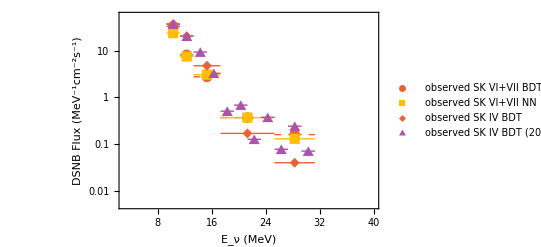

```mathematica
intDSNBfluxObservedOnly=ListLogPlot[binnedPlotData3[[All,1]],
PlotLegends->binnedPlotData3[[All,2]],
(*PlotRange->{{9,31},{10^-2,8*10^2}},*)
Frame->True,FrameLabel->{"E_ν (MeV)","DSNB Flux (MeV^-1cm^-2s^-1)"},
PlotLabel->"DSNB Flux";
PlotStyle->{{Dashed,defaultColor[[4]]},defaultColor[[8]],{defaultColor[[4]]},{Lighter[Purple]}(*{defaultColor[[-1]]}*)},
PlotMarkers->Automatic,
PlotRange->{xRange,yRange}
](*end plot*)
```

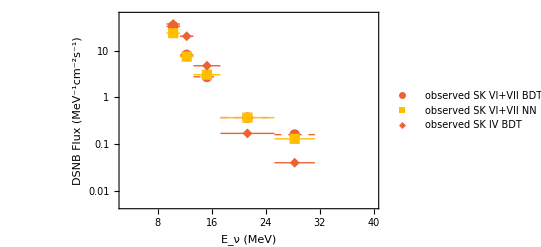

```mathematica
intDSNBfluxObservedOnly2=ListLogPlot[Drop[binnedPlotData3[[All,1]],-1],
PlotLegends->binnedPlotData3[[All,2]],
(*PlotRange->{{9,31},{10^-2,8*10^2}},*)
Frame->True,FrameLabel->{"E_ν (MeV)","DSNB Flux (MeV^-1cm^-2s^-1)"},
PlotLabel->"DSNB Flux";
PlotStyle->{{Dashed,defaultColor[[4]]},defaultColor[[8]],{defaultColor[[4]]},{Lighter[Purple]}(*{defaultColor[[-1]]}*)},
PlotMarkers->Automatic,
PlotRange->{xRange,yRange}
](*end plot*)
```

```mathematica
binnedPlotData3[[All,1]]
```

{{{10.31.01.0,33.2},{12.31.01.0,8.14},{15.32.02.0,2.76},{21.4.4.,0.37},{28.33.03.0,0.16}},{{10.31.01.0,23.79},{12.31.01.0,7.48},{15.32.02.0,3.07},{21.4.4.,0.37},{28.33.03.0,0.13}},{{10.31.01.0,37.3},{12.31.01.0,20.43},{15.32.02.0,4.77},{21.4.4.,0.17},{28.33.03.0,0.04}},{{10.31.01.0,37.1},{12.31.01.0,20.4},{14.31.01.0,9.34},{16.31.01.0,3.29},{18.31.01.0,0.508},{20.31.01.0,0.684},{22.31.01.0,0.127},{24.31.01.0,0.375},{26.31.01.0,0.0777},{28.31.01.0,0.242},{30.31.01.0,0.0709}}}

```mathematica
dsnbfluxPlotDataFinale=ExportString[binnedObservDataList,"PythonExpression"]
```

[[[[[9.29, 11.29], 33.2], [[11.29, 13.29], 8.14], [[13.29, 17.29], 2.76], [[17.29, 25.29], 0.37], [[25.29, 31.29], 0.16]], "observed SK VI+VII BDT"], [[[[9.29, 11.29], 23.79], [[11.29, 13.29], 7.48], [[13.29, 17.29], 3.07], [[17.29, 25.29], 0.37], [[25.29, 31.29], 0.13]], "observed SK VI+VII NN"], [[[[9.29, 11.29], 37.3], [[11.29, 13.29], 20.43], [[13.29, 17.29], 4.77], [[17.29, 25.29], 0.17], [[25.29, 31.29], 0.04]], "observed SK IV BDT"], [[[[9.3, 11.3], 37.1], [[11.3, 13.3], 20.4], [[13.3, 15.3], 9.34], [[15.3, 17.3], 3.29], [[17.3, 19.3], 0.508], [[19.3, 21.3], 0.684], [[21.3, 23.3], 0.127], [[23.3, 25.3], 0.375], [[25.3, 27.3], 0.0777], [[27.3, 29.3], 0.242], [[29.3, 31.3], 0.0709]], "observed SK IV BDT (2021)"]]

```mathematica
binnedObservDataList[[All,2]]
```

{observed SK VI+VII BDT,observed SK VI+VII NN,observed SK IV BDT,observed SK IV BDT (2021)}

```mathematica
outputBinnedObservDataList=Table[{binnedObservDataList[[i,2]]},{i,1,Length[binnedObservDataList]}]
```

{{observed SK VI+VII BDT},{observed SK VI+VII NN},{observed SK IV BDT},{observed SK IV BDT (2021)}}

```mathematica
Flatten[binnedObservDataList[[All,1]],1][[All,1]]
```

{{9.29,11.29},{11.29,13.29},{13.29,17.29},{17.29,25.29},{25.29,31.29},{9.29,11.29},{11.29,13.29},{13.29,17.29},{17.29,25.29},{25.29,31.29},{9.29,11.29},{11.29,13.29},{13.29,17.29},{17.29,25.29},{25.29,31.29},{9.3,11.3},{11.3,13.3},{13.3,15.3},{15.3,17.3},{17.3,19.3},{19.3,21.3},{21.3,23.3},{23.3,25.3},{25.3,27.3},{27.3,29.3},{29.3,31.3}}

```mathematica
(*export SK intDSNB bound values*)
(*(already exported our DSNB prediction below in previous section)*)
(*Export["dsnbfluxPlotDataFinale.csv",dsnbfluxPlotDataFinale]*)
```

our DSNB prediction (no MSW)

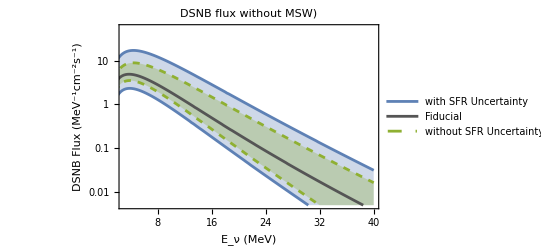

```mathematica
dsnbFluxSpreadPlotnoMSWLogScale=ListLogPlot[{globalExtremaAllnoMSWSFR[[1,2]][[-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]],fiducialData[[1,-1]],globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSW[[2,2]][[-1]]},Joined->True,
Frame->True,FrameLabel->{"E_ν (MeV)","DSNB Flux (MeV^-1cm^-2s^-1)"},
PlotLabel->"DSNB flux without MSW)",
PlotRange->{xRange,yRange},
PlotStyle->{{defaultColor[[1]]},{defaultColor[[1]]},{Lighter[Black]},{Dashed,defaultColor[[3]]},{Dashed,defaultColor[[3]]}},
Filling->{1->{{2},{Opacity[0.3,defaultColor[[1]]]}},4->{{5},{Opacity[0.3,defaultColor[[3]]]}}},
PlotLegends->{"with SFR Uncertainty",None,"Fiducial","without SFR Uncertainty"}
](*end plot*)
```

```mathematica
defaultColor
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
defaultColor[[4]]
```

RGBColor[0.922526, 0.385626, 0.209179]

```mathematica
(*ListLogPlot[{globalExtremaAllnoMSWSFR[[1,2]][[-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]],fiducialData[[1,-1]],globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSW[[2,2]][[-1]],binnedPlotData3[[All,1]][[1]],binnedPlotData3[[All,1]][[2]],binnedPlotData3[[All,1]][[3]]},Joined->{True,True,True,True,True,False,False,False},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"DSNB flux (No MSW)",

(*PlotLegends->{ToString[globalExtremaAllnoMSWSFR[[1,2,1]]],ToString[globalExtremaAllnoMSWSFR[[2,2,1]]],ToString[fiducialData[[1,1]]],ToString[globalExtremaAllnoMSW[[1,2,1]]],ToString[globalExtremaAllnoMSW[[2,2,1]]],binnedPlotData3[[All,2]][[1]],binnedPlotData3[[All,2]][[2]],binnedPlotData3[[All,2]][[3]]},*)

PlotStyle->{{defaultColor[[1]]},{defaultColor[[1]]},{Lighter[Black]},{Dashed,defaultColor[[3]]},{Dashed,defaultColor[[3]]},{Thickness[0.004],defaultColor[[4]]},defaultColor[[8]],defaultColor[[6]]},
Filling->{1->{{2},{Opacity[0.3,defaultColor[[1]]]}},4->{{5},{Opacity[0.3,defaultColor[[3]]]}}},
PlotRange->{{10,35},{0,18}}]*)
```

```mathematica
(*ListLogPlot[{binnedPlotData3[[All,1]][[1]],binnedPlotData3[[All,1]][[2]],binnedPlotData3[[All,1]][[3]],globalExtremaAllnoMSWSFR[[1,2]][[-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]],fiducialData[[1,-1]],globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSW[[2,2]][[-1]]},Joined->{False,False,False,True,True,True,True,True},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"DSNB flux (No MSW)",

(*PlotLegends->{ToString[globalExtremaAllnoMSWSFR[[1,2,1]]],ToString[globalExtremaAllnoMSWSFR[[2,2,1]]],ToString[fiducialData[[1,1]]],ToString[globalExtremaAllnoMSW[[1,2,1]]],ToString[globalExtremaAllnoMSW[[2,2,1]]],binnedPlotData3[[All,2]][[1]],binnedPlotData3[[All,2]][[2]],binnedPlotData3[[All,2]][[3]]},*)

PlotStyle->{{Thickness[0.004],defaultColor[[4]]},defaultColor[[8]],defaultColor[[6]],defaultColor[[1]],{defaultColor[[1]]},{Lighter[Black]},{Dashed,defaultColor[[3]]},{Dashed,defaultColor[[3]]}},

(*Filling->{4->{{5},{Opacity[0.3,defaultColor[[1]]]}},7->{{8},{Opacity[0.3,defaultColor[[3]]]}}},*)
PlotRange->{{10,35},{0,18}}]*)
```

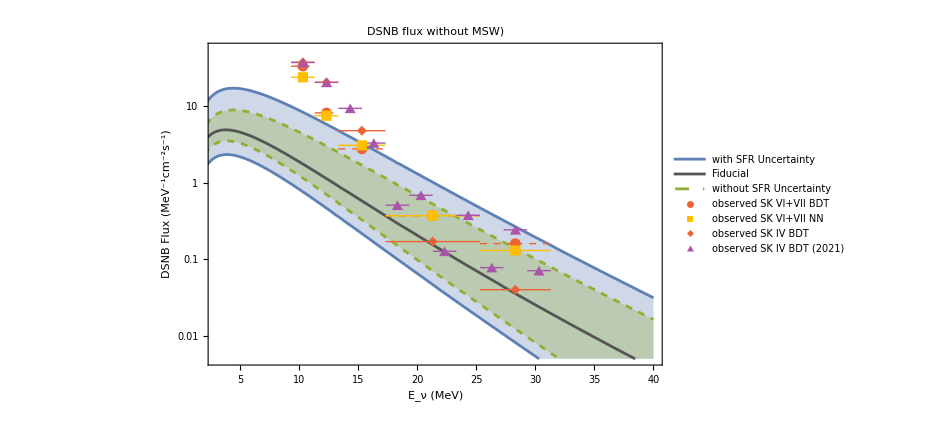

```mathematica
currentSKBoundPlotCont=Show[dsnbFluxSpreadPlotnoMSWLogScale,intDSNBfluxObservedOnly,ImageSize->700]
```

```mathematica
(*Export["currentSKBoundPlotCont.pdf",currentSKBoundPlotCont];*)
```

```mathematica
defaultColor
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

### final (money) plot 2 binned I

SK error bar bounds VS continuous DSNB flux prediction

#### binning our DSNB flux

bin the DSNB flux fiducial

```mathematica
(*x range used for SK et al. 2025 plot*)
EnuBinIntervals
```

{{9.29,11.29},{11.29,13.29},{13.29,17.29},{17.29,25.29},{25.29,31.29}}

```mathematica
(*format as bin min, bin max, bin width*)
xbinsMinMaxWidth=Table[{EnuBinIntervals[[i,1]],EnuBinIntervals[[i,2]],EnuBinIntervals[[i,2]]-EnuBinIntervals[[i,1]]},{i,1,Length[EnuBinIntervals]}]
(*get only edges*)
(*1st then only 2nd values thereafter*)
xEdges = Join[{xbinsMinMaxWidth[[1,1]]},xbinsMinMaxWidth[[All,2]]]
(*x values*)
xVals=Table[(EnuBinIntervals[[i,1]]+EnuBinIntervals[[i,2]])/2,{i,1,Length[EnuBinIntervals]}]
```

{{9.29,11.29,2.},{11.29,13.29,2.},{13.29,17.29,4.},{17.29,25.29,8.},{25.29,31.29,6.}}

{9.29,11.29,13.29,17.29,25.29,31.29}

{10.29,12.29,15.29,21.29,28.29}

get counts (disuse)

```mathematica
xCountsFiducial = BinCounts[fiducialData[[1,-1]][[All,1]],{xEdges}]
```

{8,8,16,32,24}

```mathematica
(*fiducialData[[1,-1]][[All,1]]*)
```

```mathematica
(*{globalExtremaAllnoMSWSFR[[1,2]][[-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]],fiducialData[[1,-1]],globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSW[[2,2]][[-1]]*)
```

get y values (from fiducial)

```mathematica
(*interpolate fiducial DSNB flux*)
fidFunc=Interpolation[fiducialData[[1,-1]]];

(*get y values corresponding to x medians*)
yVals=Table[fidFunc[x],{x,xVals}]
```

{1.75127,1.12983,0.57798,0.154526,0.0356725}

get counts (disuse)

```mathematica
BinCounts[fiducialData[[1,-1]][[All,2]],1]
```

{0,113,14,10,10,14}

get y min and max values

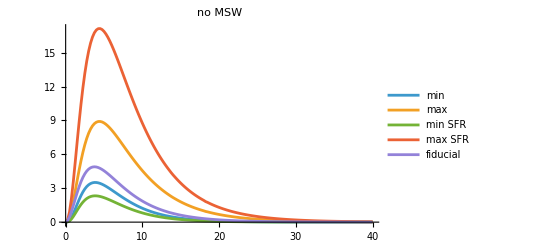

```mathematica
ListPlot[{globalExtremaAllnoMSW[[2,2]][[-1]],globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]],globalExtremaAllnoMSWSFR[[1,2]][[-1]],fiducialData[[1,-1]]},PlotLegends->{"min","max","min SFR","max SFR","fiducial"},PlotLabel->"no MSW",Joined->True,PlotRange->All]
```

```mathematica
(*interpolate max/min with/without SFR uncertainty no MSW*)
(*without SFR*)
maxFuncNoMSW=Interpolation[globalExtremaAllnoMSW[[1,2]][[-1]]];
minFuncNoMSW=Interpolation[globalExtremaAllnoMSW[[2,2]][[-1]]];
(*with SFR*)
maxFuncNoMSWSFR=Interpolation[globalExtremaAllnoMSWSFR[[1,2]][[-1]]];
minFuncNoMSWSFR=Interpolation[globalExtremaAllnoMSWSFR[[2,2]][[-1]]];

(*without SFR uncertainty*)
ymaxList=Table[maxFuncNoMSW[x],{x,xVals}];
yminList=Table[minFuncNoMSW[x],{x,xVals}];

(*with SFR uncertainty*)
ymaxListSFR=Table[maxFuncNoMSWSFR[x],{x,xVals}];
yminListSFR=Table[minFuncNoMSWSFR[x],{x,xVals}];
```

```mathematica
(*ymaxList
yminList*)
```

make y bin ranges

i.e. make y interval values

```mathematica
(*without SFR uncertainty*)
fluxBinIntervals=Table[{yminList[[i]],ymaxList[[i]]},{i,1,Length[ymaxList]}];
(*with SFR uncertainty*)
fluxBinIntervalsSFR=Table[{yminListSFR[[i]],ymaxListSFR[[i]]},{i,1,Length[ymaxListSFR]}];
```

select only 10 - 30 MeV (in order for interpolation to work later)

```mathematica
(*select only the 10-30 MeV range*)
(*otherwise inverting x,y to y,x yields two dep values for 1 dep values*)
(*which cannot be handled by interpolation*)
xMin=4.5;
xMax=30;

(*without SFR uncertainty*)
extremaAllnoMSWmax=dsnbSelector[globalExtremaAllnoMSW[[1,2]][[-1]],xMin,xMax];
extremaAllnoMSWmin=dsnbSelector[globalExtremaAllnoMSW[[2,2]][[-1]],xMin,xMax];
(*with SFR uncertainty*)
extremaAllnoMSWmaxSFR=dsnbSelector[globalExtremaAllnoMSWSFR[[1,2]][[-1]],xMin,xMax];
extremaAllnoMSWminSFR=dsnbSelector[globalExtremaAllnoMSWSFR[[2,2]][[-1]],xMin,xMax];
```

get x min and max values (instead of using xVals bins of SK)

```mathematica
(*get inverse lists*)
(*i.e. {x,y}->{y,x}*)
(*without SFR uncertainty*)
InverseglobalExtremaAllnoMSWmax=Table[{extremaAllnoMSWmax[[i,2]],extremaAllnoMSWmax[[i,1]]},{i,1,Length[extremaAllnoMSWmax]}];
InverseglobalExtremaAllnoMSWmin=Table[{extremaAllnoMSWmin[[i,2]],extremaAllnoMSWmin[[i,1]]},{i,1,Length[extremaAllnoMSWmin]}];
(*with SFR uncertainty*)
InverseglobalExtremaAllnoMSWmaxSFR=Table[{extremaAllnoMSWmaxSFR[[i,2]],extremaAllnoMSWmaxSFR[[i,1]]},{i,1,Length[extremaAllnoMSWmaxSFR]}];
InverseglobalExtremaAllnoMSWminSFR=Table[{extremaAllnoMSWminSFR[[i,2]],extremaAllnoMSWminSFR[[i,1]]},{i,1,Length[extremaAllnoMSWminSFR]}];
```

confirm it works properly

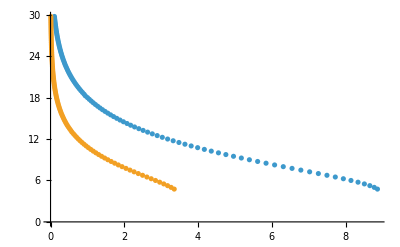

```mathematica
ListPlot[{InverseglobalExtremaAllnoMSWmax,InverseglobalExtremaAllnoMSWmin}]
```

```mathematica
(*inverse interpolate max/min with/without SFR uncertainty no MSW*)
(*i.e. x(y) insteda of y(x)*)
(*without SFR*)
maxInverseFuncNoMSW=Interpolation[InverseglobalExtremaAllnoMSWmax];
minInverseFuncNoMSW=Interpolation[InverseglobalExtremaAllnoMSWmin];
(*with SFR*)
maxInverseFuncNoMSWSFR=Interpolation[InverseglobalExtremaAllnoMSWmaxSFR];
minInverseFuncNoMSWSFR=Interpolation[InverseglobalExtremaAllnoMSWminSFR];

(*creatre tables*)
(*without SFR uncertainty*)
xmaxList=Table[maxInverseFuncNoMSW[y],{y,yVals}];
xminList=Table[minInverseFuncNoMSW[y],{y,yVals}];
(*with SFR uncertainty*)
xmaxListSFR=Table[maxInverseFuncNoMSWSFR[y],{y,yVals}];
xminListSFR=Table[minInverseFuncNoMSWSFR[y],{y,yVals}];
```

InterpolatingFunction::dmval: Input value {0.0356725} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.154526} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0356725} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
InverseglobalExtremaAllnoMSWmax[[5]]
maxInverseFuncNoMSW[InverseglobalExtremaAllnoMSWmax[[5]][[1]]]
```

{8.33856,5.75}

5.75

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

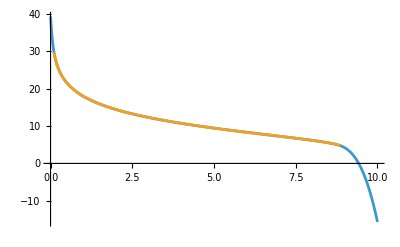

```mathematica
ListPlot[{Table[{i,maxInverseFuncNoMSW[i]},{i,0,10,0.01}],InverseglobalExtremaAllnoMSWmax},Joined->True]
```

make x bin ranges

i.e. make y interval values

```mathematica
(*without SFR uncertainty*)
energyBinIntervals=Table[{xminList[[i]],xmaxList[[i]]},{i,1,Length[xmaxList]}];
(*with SFR uncertainty*)
energyBinIntervalsSFR=Table[{xminListSFR[[i]],xmaxListSFR[[i]]},{i,1,Length[xmaxListSFR]}];
```

create full data set

```mathematica
(*format as*)
(*{{xmin,xmax,xval},{ymin,ymax,yval},...}*)
(*no MSW without SFR uncertainty*)
fiducialDataBinned=Table[{Join[energyBinIntervals[[i]],{xVals[[i]]}],Join[fluxBinIntervals[[i]],{yVals[[i]]}]},{i,1,Length[EnuBinIntervals]}]
(*no MSW with SFR uncertainty*)
fiducialDataBinnedSFR=Table[{Join[energyBinIntervalsSFR[[i]],{xVals[[i]]}],Join[fluxBinIntervalsSFR[[i]],{yVals[[i]]}]},{i,1,Length[EnuBinIntervals]}]
```

{{{8.46822,15.1261,10.29},{1.14692,4.32864,1.75127}},{{10.3523,17.3792,12.29},{0.699983,3.0082,1.12983}},{{13.0198,20.8186,15.29},{0.325996,1.69656,0.57798}},{{18.2031,27.709,21.29},{0.0704061,0.527469,0.154526}},{{23.9891,34.9363,28.29},{0.0123498,0.13855,0.0356725}}}

{{{6.43832,18.4795,10.29},{0.760331,8.32283,1.75127}},{{8.59044,20.7335,12.29},{0.464043,5.78396,1.12983}},{{11.411,24.2035,15.29},{0.216114,3.26202,0.57798}},{{16.5976,31.2032,21.29},{0.0466746,1.01418,0.154526}},{{22.3407,36.873,28.29},{0.0081871,0.266395,0.0356725}}}

```mathematica
fiducialDataBinned[[1]]
fiducialDataBinnedSFR[[1]]
```

{{8.46822,15.1261,10.29},{1.14692,4.32864,1.75127}}

{{6.43832,18.4795,10.29},{0.760331,8.32283,1.75127}}

```mathematica
Transpose[fiducialDataBinned][[1,All]]
```

{{8.46822,15.1261,10.29},{10.3523,17.3792,12.29},{13.0198,20.8186,15.29},{18.2031,27.709,21.29},{23.9891,34.9363,28.29}}

#### create error bar plot

(fiducial DSNB max/min with/without SFR)

```mathematica
ListPlot[{globalExtremaAllnoMSW[[2,2]][[-1]],globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]],globalExtremaAllnoMSWSFR[[1,2]][[-1]],fiducialData[[1,-1]]},PlotLegends->{"min","max","min SFR","max SFR","fiducial"},PlotLabel->"no MSW",Joined->True,PlotRange->All]
```

-Graphics-

create error bar points

```mathematica
errorBarPlotDSNBdata=errorBarPointMaker[fiducialDataBinned]
errorBarPlotDSNBdataSFR=errorBarPointMaker[fiducialDataBinnedSFR]
```

{{10.31.85.,1.80.62.6},{12.31.95.,1.10.41.9},{15.32.36.,0.580.251.1},{21.33.16.,0.150.080.4},{28.4.7.,0.0360.0230.10}}

{{10.4.8.,1.81.07.},{12.4.8.,1.10.75.},{15.4.9.,0.60.42.7},{21.5.10.,0.150.110.9},{28.6.9.,0.0360.0270.23}}

plot em to confirm

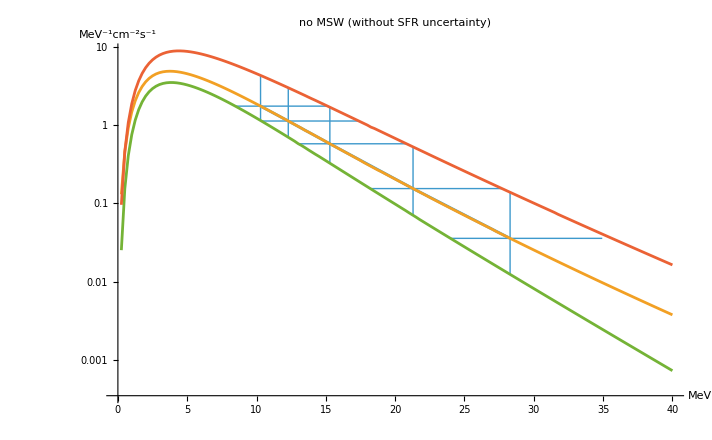

```mathematica
ListLogPlot[{errorBarPlotDSNBdata,fiducialData[[1,-1]],globalExtremaAllnoMSW[[2,2]][[-1]],globalExtremaAllnoMSW[[1,2]][[-1]]},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"no MSW (without SFR uncertainty)"]
```

```mathematica
maxInverseFuncNoMSW[1.14]
minInverseFuncNoMSW[1.14]
```

17.3332

10.3151

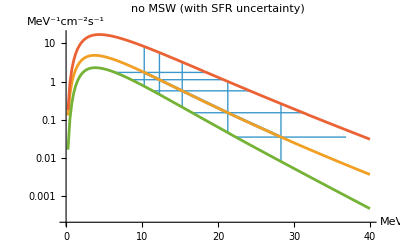

```mathematica
ListLogPlot[{errorBarPlotDSNBdataSFR,fiducialData[[1,-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]],globalExtremaAllnoMSWSFR[[1,2]][[-1]]},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"no MSW (with SFR uncertainty)"]
```

#### plot with SK bounds

```mathematica
intDSNBfluxObservedOnly
```

-Graphics-

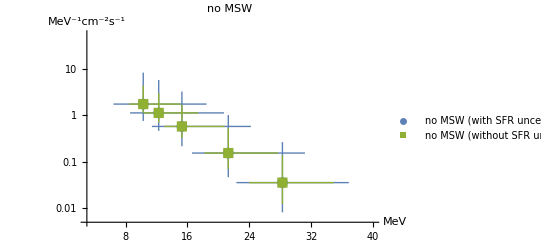

```mathematica
errorBarDSNBplot=ListLogPlot[{errorBarPlotDSNBdataSFR,errorBarPlotDSNBdata},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLabel->"no MSW",PlotLegends->{"no MSW (with SFR uncertainty)","no MSW (without SFR uncertainty)"},PlotRange->{xRange,yRange},PlotMarkers->Automatic,PlotRangePadding->None,PlotStyle->{defaultColor[[1]],defaultColor[[3]]}]
```

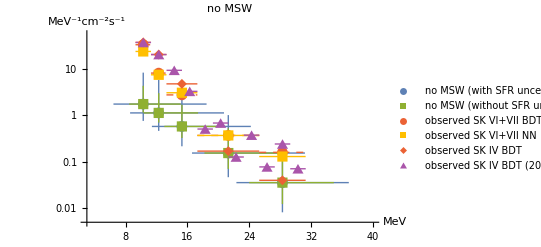

```mathematica
Show[errorBarDSNBplot,intDSNBfluxObservedOnly]
```

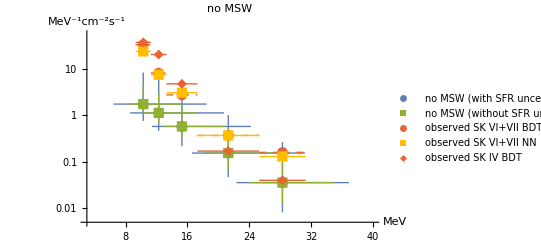

```mathematica
Show[errorBarDSNBplot,intDSNBfluxObservedOnly2]
```

### final (money) plot 3 binned II

SK error bar bounds VS DSNB flux prediction binned

#### binning x values (Enu)

```mathematica
(*x range used for SK et al. 2025 plot*)
EnuBinIntervals
```

{{9.29,11.29},{11.29,13.29},{13.29,17.29},{17.29,25.29},{25.29,31.29}}

```mathematica
(*format as bin min, bin max, bin width*)
xbinsMinMaxWidth
(*get only edges*)
(*1st then only 2nd values thereafter*)
xEdges 
(*x values*)
xVals
```

{{9.29,11.29,2.},{11.29,13.29,2.},{13.29,17.29,4.},{17.29,25.29,8.},{25.29,31.29,6.}}

{9.29,11.29,13.29,17.29,25.29,31.29}

{10.29,12.29,15.29,21.29,28.29}

get counts (disuse)

```mathematica
xCountsFiducial
```

{8,8,16,32,24}

```mathematica
fiducialData[[1,-1]][[All,1]]
```

{0.,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.,5.25,5.5,5.75,6.,6.25,6.5,6.75,7.,7.25,7.5,7.75,8.,8.25,8.5,8.75,9.,9.25,9.5,9.75,10.,10.25,10.5,10.75,11.,11.25,11.5,11.75,12.,12.25,12.5,12.75,13.,13.25,13.5,13.75,14.,14.25,14.5,14.75,15.,15.25,15.5,15.75,16.,16.25,16.5,16.75,17.,17.25,17.5,17.75,18.,18.25,18.5,18.75,19.,19.25,19.5,19.75,20.,20.25,20.5,20.75,21.,21.25,21.5,21.75,22.,22.25,22.5,22.75,23.,23.25,23.5,23.75,24.,24.25,24.5,24.75,25.,25.25,25.5,25.75,26.,26.25,26.5,26.75,27.,27.25,27.5,27.75,28.,28.25,28.5,28.75,29.,29.25,29.5,29.75,30.,30.25,30.5,30.75,31.,31.25,31.5,31.75,32.,32.25,32.5,32.75,33.,33.25,33.5,33.75,34.,34.25,34.5,34.75,35.,35.25,35.5,35.75,36.,36.25,36.5,36.75,37.,37.25,37.5,37.75,38.,38.25,38.5,38.75,39.,39.25,39.5,39.75,40.}

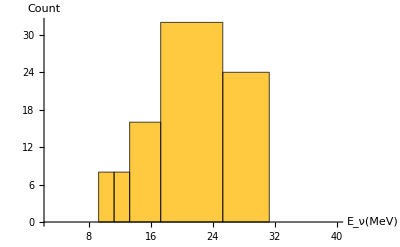

```mathematica
fidXbinnedHist=Histogram[fiducialData[[1,-1]][[All,1]],{xEdges},PlotRange->{xRange,All},AxesLabel->{"E_ν(MeV)","Count"}]
```

#### binning y values (flux) ONLY fiducial

```mathematica
yVals
```

{1.75127,1.12983,0.57798,0.154526,0.0356725}

```mathematica
fiducialData[[1,-1]][[All,2]]
```

{0.,0.130656,0.457864,0.925583,1.4735,2.04802,2.60772,3.12377,3.57854,3.96325,4.27563,4.51778,4.69454,4.8115,4.87616,4.89708,4.87982,4.83066,4.75525,4.6586,4.5451,4.41853,4.28214,4.13867,3.99045,3.83943,3.68722,3.53516,3.38435,3.23568,3.08986,2.94745,2.80891,2.67455,2.54462,2.41928,2.29865,2.18277,2.07165,1.96525,1.86353,1.76639,1.67374,1.58546,1.50142,1.42149,1.34552,1.27336,1.20488,1.13991,1.07831,1.01993,0.964622,0.912252,0.857826,0.815762,0.771402,0.729443,0.689739,0.6522,0.616714,0.583173,0.551475,0.521521,0.493218,0.466476,0.441212,0.417344,0.394795,0.373494,0.35337,0.332504,0.31462,0.297727,0.281769,0.266693,0.253947,0.240425,0.227647,0.215571,0.204159,0.193371,0.183175,0.173535,0.164482,0.155861,0.147709,0.14,0.132708,0.125811,0.118943,0.112801,0.106988,0.101487,0.0962791,0.0913495,0.0866822,0.0822629,0.0780779,0.0741533,0.0703974,0.0668393,0.0634682,0.060274,0.057247,0.054378,0.0516586,0.0490807,0.0466366,0.0440365,0.0418549,0.0397858,0.0378232,0.0359614,0.034195,0.0325189,0.0309282,0.0294186,0.0279856,0.0266253,0.0253338,0.0241075,0.0229429,0.0218368,0.0207862,0.0197882,0.01884,0.0179391,0.017083,0.0162693,0.0154959,0.0147608,0.0140619,0.0133974,0.0127655,0.0121646,0.0115931,0.0110495,0.0105323,0.0100403,0.00957217,0.00912669,0.00870274,0.00829923,0.00791514,0.0075495,0.00720139,0.00686993,0.0065543,0.00625371,0.00596741,0.00569471,0.00543493,0.00518743,0.00495162,0.00472691,0.00451277,0.00430868,0.00411416,0.00392873,0.00375195}

#### plotting only fiducial

```mathematica
(*x start stop and width*)
xbinsMinMaxWidth
(*x start of bin*)
xbinsMinMaxWidth[[All,1]]
```

{{9.29,11.29,2.},{11.29,13.29,2.},{13.29,17.29,4.},{17.29,25.29,8.},{25.29,31.29,6.}}

{9.29,11.29,13.29,17.29,25.29}

```mathematica
(*midpoints or x values*)
xVals
```

{10.29,12.29,15.29,21.29,28.29}

```mathematica
(*y values or heights*)
yVals
```

{1.75127,1.12983,0.57798,0.154526,0.0356725}

create points for step plot

```mathematica
(*start values plus last midpoint*)
xStartPlus=Join[xbinsMinMaxWidth[[All,1]],{xVals[[-1]]}]
```

{9.29,11.29,13.29,17.29,25.29,28.29}

```mathematica
(*yVals plus one duplicate end*)
yValsPlus=Join[yVals,{yVals[[-1]]}]
```

{1.75127,1.12983,0.57798,0.154526,0.0356725,0.0356725}

plot em

```mathematica
xStartyValsPlus=Table[{xStartPlus[[i]],yValsPlus[[i]]},{i,1,Length[yValsPlus]}]
```

{{9.29,1.75127},{11.29,1.12983},{13.29,0.57798},{17.29,0.154526},{25.29,0.0356725},{28.29,0.0356725}}

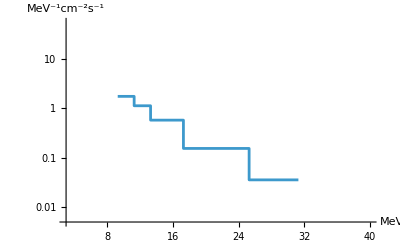

```mathematica
fiducialStepPlot=ListStepPlot[xStartyValsPlus,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{xRange,yRange},ScalingFunctions->"Log"]
```

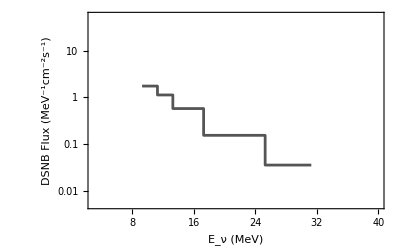

```mathematica
fiducialStepPlot2=ListStepPlot[xStartyValsPlus,PlotRange->{xRange,yRange},ScalingFunctions->"Log",PlotStyle->Lighter[Black],Frame->True,FrameLabel->{"E_ν (MeV)","DSNB Flux (MeV^-1cm^-2s^-1)"}]
```

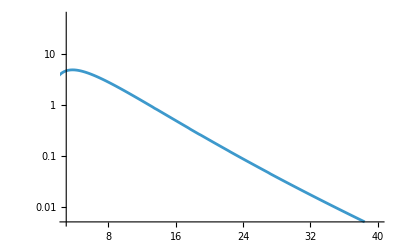

```mathematica
dsnbFluxFiducial =ListPlot[fiducialData[[1,-1]],Joined->True,PlotRange->{xRange,yRange},ScalingFunctions->"Log"]
```

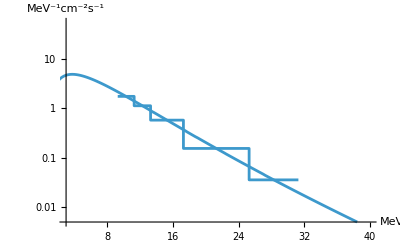

```mathematica
Show[fiducialStepPlot,dsnbFluxFiducial]
```

```mathematica
intDSNBfluxObservedOnly2
```

-Graphics-

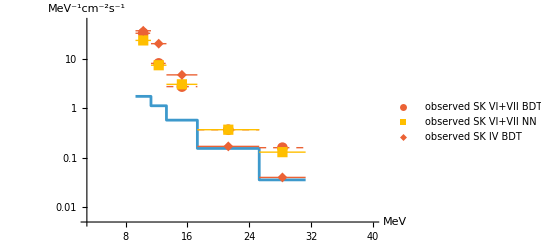

```mathematica
Show[fiducialStepPlot,intDSNBfluxObservedOnly2]
```

#### Plotting all (without MSW)

only fiducial up until now
just need y values and repeat previous steps

assumes no MSW effect

```mathematica
(*interpolate max/min DSNB flux without SFR uncertianty*)
maxFunc=Interpolation[globalExtremaAllnoMSW[[1,2]][[-1]]];
minFunc=Interpolation[globalExtremaAllnoMSW[[2,2]][[-1]]];

(*interpolate max/min DSNB flux with SFR uncertianty*)
maxFuncSFR=Interpolation[globalExtremaAllnoMSWSFR[[1,2]][[-1]]];
minFuncSFR=Interpolation[globalExtremaAllnoMSWSFR[[2,2]][[-1]]];

(*get y values corresponding to x medians*)
(*without SFR*)
yValsMax=Table[maxFunc[x],{x,xVals}];
yValsMin=Table[minFunc[x],{x,xVals}];
(*with SFR*)
yValsMaxSFR=Table[maxFuncSFR[x],{x,xVals}];
yValsMinSFR=Table[minFuncSFR[x],{x,xVals}];
```

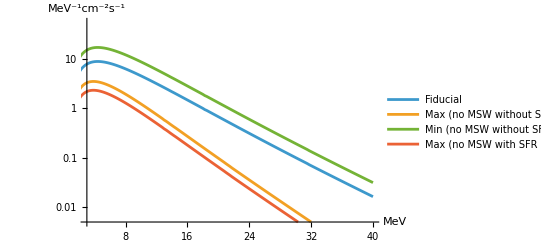

```mathematica
dsnbFluxplotExtrema=ListLogPlot[{globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSW[[2,2]][[-1]],globalExtremaAllnoMSWSFR[[1,2]][[-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]]},Joined->True,PlotLegends->{"Fiducial","Max (no MSW without SFR uncertainty)","Min (no MSW without SFR uncertainty)","Max (no MSW with SFR uncertainty)","Min (no MSW with SFR uncertainty)"},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{xRange,yRange}]
```

make step plot data for extrema (with/without SFR)

```mathematica
(*yVals plus one duplicate end*)
(*without SFR*)
yValsMaxPlus=Join[yValsMax,{yValsMax[[-1]]}];
yValsMinPlus=Join[yValsMin,{yValsMin[[-1]]}];
(*with SFR*)
yValsMaxSFRPlus=Join[yValsMaxSFR,{yValsMaxSFR[[-1]]}];
yValsMinSFRPlus=Join[yValsMinSFR,{yValsMinSFR[[-1]]}];
```

```mathematica
(*combine yPlus and xPlus *)
(*already made x values plus last midpoint*)
xStartPlus
```

{9.29,11.29,13.29,17.29,25.29,28.29}

```mathematica
(*combine yPlus and xPlus *)
(*without SFR*)
xStartyValsPlusMax=Table[{xStartPlus[[i]],yValsMaxPlus[[i]]},{i,1,Length[yValsMaxPlus]}];
xStartyValsPlusMin=Table[{xStartPlus[[i]],yValsMinPlus[[i]]},{i,1,Length[yValsMinPlus]}];
(*with SFR*)
xStartyValsPlusMaxSFR=Table[{xStartPlus[[i]],yValsMaxSFRPlus[[i]]},{i,1,Length[yValsMaxSFRPlus]}];
xStartyValsPlusMinSFR=Table[{xStartPlus[[i]],yValsMinSFRPlus[[i]]},{i,1,Length[yValsMinSFRPlus]}];
```

confirm plots work

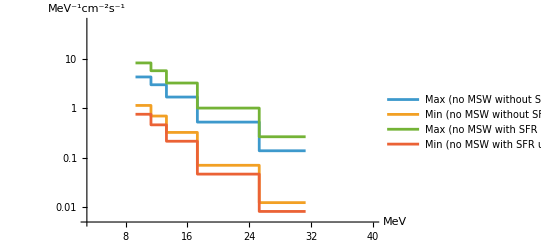

```mathematica
stepPlotExtrema=ListStepPlot[{xStartyValsPlusMax,xStartyValsPlusMin,xStartyValsPlusMaxSFR,xStartyValsPlusMinSFR},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{xRange,yRange},ScalingFunctions->"Log",PlotLegends->{"Max (no MSW without SFR uncertainty)","Min (no MSW without SFR uncertainty)","Max (no MSW with SFR uncertainty)","Min (no MSW with SFR uncertainty)"}]
```

```mathematica
stepPlotExtrema=ListStepPlot[{xStartyValsPlusMax,xStartyValsPlusMin,xStartyValsPlusMaxSFR,xStartyValsPlusMinSFR},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{xRange,yRange},ScalingFunctions->"Log",PlotLegends->{"Max (no MSW without SFR uncertainty)","Min (no MSW without SFR uncertainty)","Max (no MSW with SFR uncertainty)","Min (no MSW with SFR uncertainty)"}]
```

-Graphics-

```mathematica
Show[fiducialStepPlot,dsnbFluxFiducial]
```

-Graphics-

final plot

```mathematica
intDSNBfluxObservedOnly2
```

-Graphics-

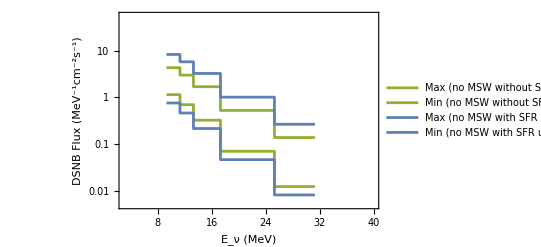

```mathematica
stepPlotExtrema2=ListStepPlot[{xStartyValsPlusMax,xStartyValsPlusMin,xStartyValsPlusMaxSFR,xStartyValsPlusMinSFR},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{xRange,yRange},ScalingFunctions->"Log",PlotLegends->{"Max (no MSW without SFR uncertainty)","Min (no MSW without SFR uncertainty)","Max (no MSW with SFR uncertainty)","Min (no MSW with SFR uncertainty)"},PlotStyle->{defaultColor[[3]],defaultColor[[3]],defaultColor[[1]],defaultColor[[1]]},Frame->True,FrameLabel->{"E_ν (MeV)","DSNB Flux (MeV^-1cm^-2s^-1)"}]
```

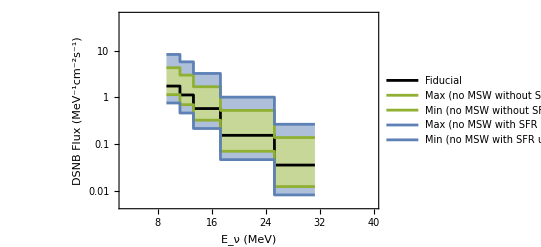

```mathematica
stepPlotAll=ListStepPlot[{xStartyValsPlus,xStartyValsPlusMax,xStartyValsPlusMin,xStartyValsPlusMaxSFR,xStartyValsPlusMinSFR},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{xRange,yRange},ScalingFunctions->"Log",PlotLegends->{"Fiducial","Max (no MSW without SFR uncertainty)","Min (no MSW without SFR uncertainty)","Max (no MSW with SFR uncertainty)","Min (no MSW with SFR uncertainty)"},PlotStyle->{Black,defaultColor[[3]],defaultColor[[3]],defaultColor[[1]],defaultColor[[1]]},Frame->True,FrameLabel->{"E_ν (MeV)","DSNB Flux (MeV^-1cm^-2s^-1)"},Filling->{1->{{2},{Opacity[0.5,defaultColor[[3]]]}},1->{{3},{Opacity[0.5,defaultColor[[3]]]}},2->{{4},{Opacity[0.5,defaultColor[[1]]]}},5->{{3},{Opacity[0.5,defaultColor[[1]]]}}}]
```

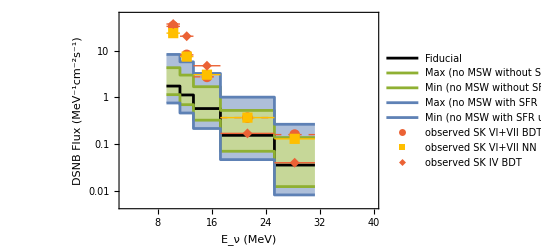

```mathematica
Show[stepPlotAll,intDSNBfluxObservedOnly2]
```

#### Step plot Exportation for python

make step plot data for python extrema (with/without SFR) and fiducial

for y values

```mathematica
(*yVals plus one duplicate in front*)
(*without SFR*)
yValsMaxPlus2=Prepend[yValsMax,yValsMax[[1]]];
yValsMinPlus2=Prepend[yValsMin,yValsMin[[1]]];
(*with SFR*)
yValsMaxSFRPlus2=Prepend[yValsMaxSFR,yValsMaxSFR[[1]]];
yValsMinSFRPlus2=Prepend[yValsMinSFR,yValsMinSFR[[1]]];
(*fiducial*)
(*yVals plus one duplicate end*)
yValsPlus2=Prepend[yVals,yVals[[1]]]
```

{1.75127,1.75127,1.12983,0.57798,0.154526,0.0356725}

for x values

```mathematica
(*start values plus last x end value*)
xStartPlus2=Join[xbinsMinMaxWidth[[All,1]],{xbinsMinMaxWidth[[All,2]][[-1]]}]
```

{9.29,11.29,13.29,17.29,25.29,31.29}

combine x and y values

```mathematica
(*combine yPlus and xPlus *)
(*without SFR*)
xStartyValsPlusMax2=Table[{xStartPlus2[[i]],yValsMaxPlus2[[i]]},{i,1,Length[yValsMaxPlus2]}];
xStartyValsPlusMin2=Table[{xStartPlus2[[i]],yValsMinPlus2[[i]]},{i,1,Length[yValsMinPlus2]}];
(*with SFR*)
xStartyValsPlusMaxSFR2=Table[{xStartPlus2[[i]],yValsMaxSFRPlus2[[i]]},{i,1,Length[yValsMaxSFRPlus2]}];
xStartyValsPlusMinSFR2=Table[{xStartPlus2[[i]],yValsMinSFRPlus2[[i]]},{i,1,Length[yValsMinSFRPlus2]}];
(*fiducial*)
xStartyValsPlus2=Table[{xStartPlus2[[i]],yValsPlus2[[i]]},{i,1,Length[yValsPlus2]}]
```

{{9.29,1.75127},{11.29,1.75127},{13.29,1.12983},{17.29,0.57798},{25.29,0.154526},{31.29,0.0356725}}

export the step plot data for python

```mathematica
ExportString[xStartyValsPlus2,"PythonExpression"]
```

[[9.29, 1.7512684283527438], [11.29, 1.7512684283527438], [13.29, 1.1298272636961868], [17.29, 0.5779803371199599], [25.29, 0.15452600679218578], [31.29, 0.0356724996547319]]

```mathematica
(*export step plot data for python*)
Export["xStartyValsPlus2.csv",ExportString[xStartyValsPlus2,"PythonExpression"]];
Export["xStartyValsPlusMax2.csv",ExportString[xStartyValsPlusMax2,"PythonExpression"]];
Export["xStartyValsPlusMaxSFR2.csv",ExportString[xStartyValsPlusMaxSFR2,"PythonExpression"]];
Export["xStartyValsPlusMinSFR2.csv",ExportString[xStartyValsPlusMinSFR2,"PythonExpression"]];
Export["xStartyValsPlusMin2.csv",ExportString[xStartyValsPlusMin2,"PythonExpression"]];
```

also export SK bounds

```mathematica
(*export SK intDSNB bound values*)
(*(already exported our DSNB prediction below in previous section)*)
(*Export["dsnbfluxPlotDataSK.csv",dsnbfluxPlotDataFinale]*)
```

## finding temperature

### DSNB fluxes (many)

#### plot DSNB fluxes for many cases

after getting local extrema (see integrated DSNB flux)

varying binary models only

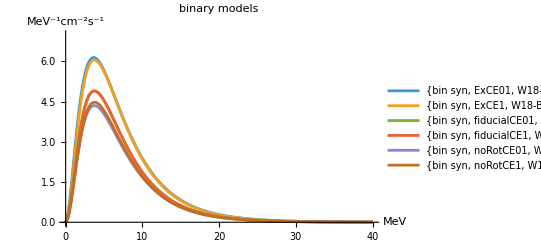

```mathematica
dsnbFluxesPlotter[binModData,"binary models"]
```

varying engine models only

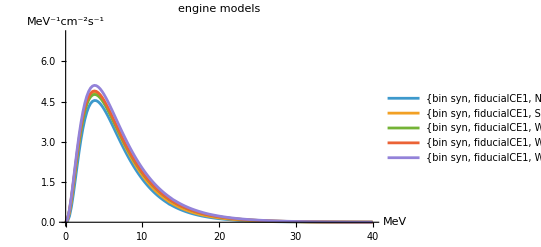

```mathematica
dsnbFluxesPlotter[engineModData,"engine models"]
```

varying flavor conversions

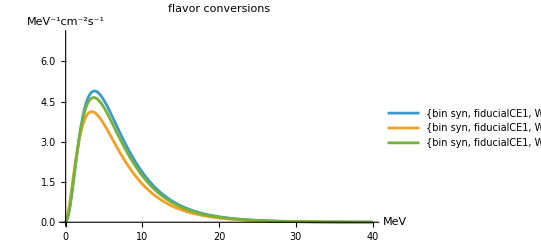

```mathematica
dsnbFluxesPlotter[noMSWIHNHdata,"flavor conversions"]
```

varying max NS mass

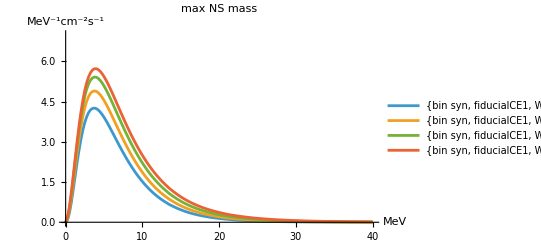

```mathematica
dsnbFluxesPlotter[maxMnsData,"max NS mass"]
```

varying alpha

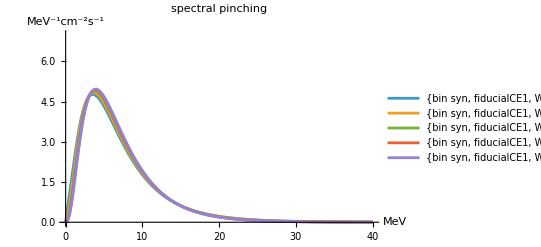

```mathematica
dsnbFluxesPlotter[alphaCheck,"spectral pinching"]
```

varying single stars vs binary stars

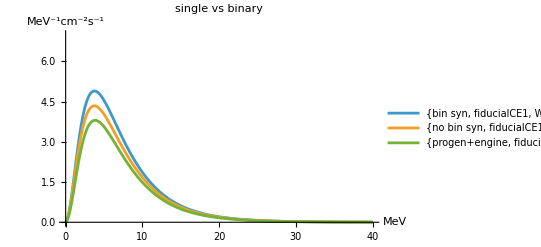

```mathematica
dsnbFluxesPlotter[singleVsbinarydata,"single vs binary"]
```

varying stellar distribution (singleVSbinary and binary model)

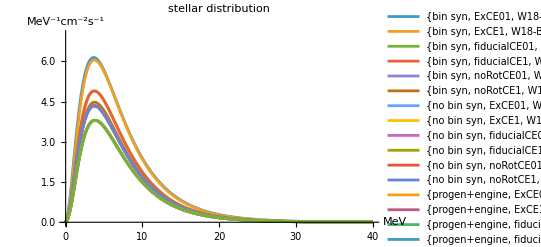

```mathematica
dsnbFluxesPlotter[stellarDistdata,"stellar distribution"]
```

varying 1P vs 2P criterion

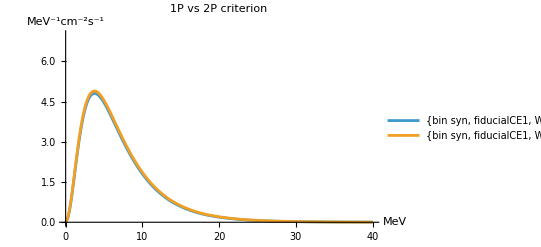

```mathematica
dsnbFluxesPlotter[criterionData,"1P vs 2P criterion"]
```

```mathematica
(*all runs*)
Length[dataAll]
```

18000

```mathematica
(*all runs excluding all NS case since it is non-physical*)
(*this coincides with expected number*)
Length[selectorRecursive[dataAll,{"BHNS"},1]]
```

10800

```mathematica
(*100 iterations*)
(*iterations=100;
dsnbFluxesPlotterJR[selectorRecursive[dataAll,{"BHNS"},1][[1;;iterations]],ToString[Length[selectorRecursive[dataAll,{"BHNS"},1][[1;;iterations]]]]<>" iterations"]*)
```

```mathematica
(*1000 iterations*)
(*iterations=1000;
dsnbFluxesPlotterJR[selectorRecursive[dataAll,{"BHNS"},1][[1;;iterations]],ToString[Length[selectorRecursive[dataAll,{"BHNS"},1][[1;;iterations]]]]<>" iterations"]*)
```

```mathematica
(*all iterations (without all NS case)*)
(*iterations=Length[selectorRecursive[dataAll,{"BHNS"},1]];
dsnbFluxesPlotterJR[selectorRecursive[dataAll,{"BHNS"},1][[1;;iterations]],ToString[Length[selectorRecursive[dataAll,{"BHNS"},1][[1;;iterations]]]]<>" iterations"]*)
```

### find temperature (ours)

#### fiducial case (test)

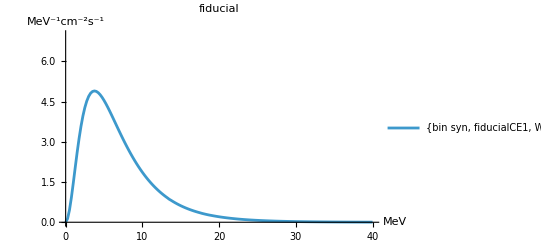

```mathematica
dsnbFluxesPlotter[fiducialData,"fiducial"]
```

```mathematica
(*fiducialData[[1]]*)
```

```mathematica
(*fiducialData[[1]][[-1]]*)
```

```mathematica
(*temp, coefficent, maxIndex*)
tempFinder[fiducialData[[1]][[-1]]]
```

{4.71056,17.4157,16}

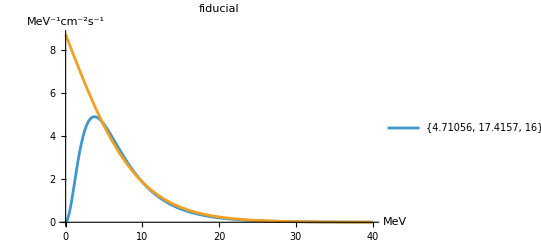

```mathematica
dsnbFluxesTemperaturePlotter[fiducialData,"fiducial"]
```

#### multiple cases (without SFR uncertainty)

vary only binary synthesis models

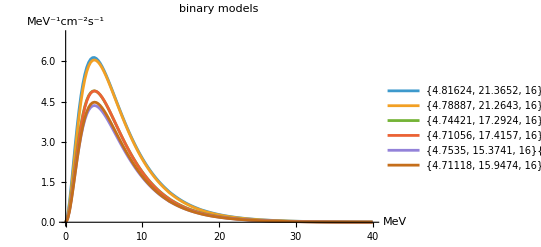

```mathematica
dsnbFluxesTemperaturePlotterJR[binModData,"binary models"]
```

varying engine models only

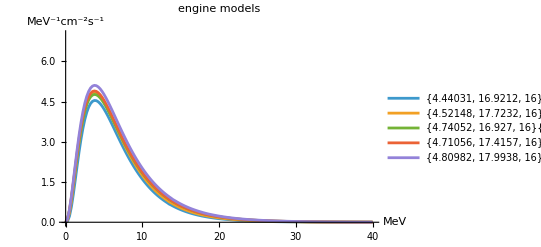

```mathematica
dsnbFluxesTemperaturePlotterJR[engineModData,"engine models"]
```

varying flavor conversions

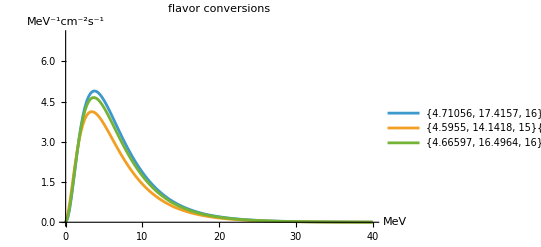

```mathematica
dsnbFluxesTemperaturePlotterJR[noMSWIHNHdata,"flavor conversions"]
```

varying max NS mass

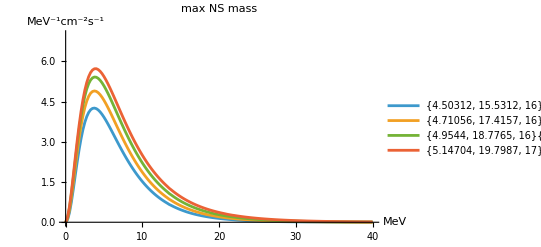

```mathematica
dsnbFluxesTemperaturePlotterJR[maxMnsData,"max NS mass"]
```

varying alpha

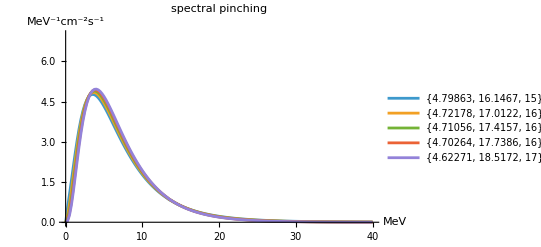

```mathematica
dsnbFluxesTemperaturePlotterJR[alphaCheck,"spectral pinching"]
```

varying single stars vs binary stars

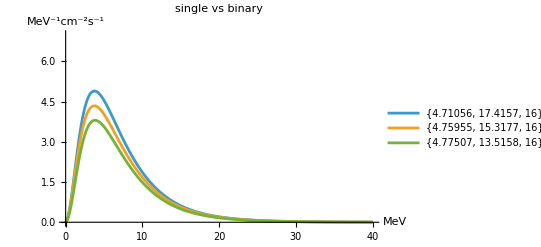

```mathematica
dsnbFluxesTemperaturePlotterJR[singleVsbinarydata,"single vs binary"]
```

varying stellar distribution (singleVSbinary and binary model)

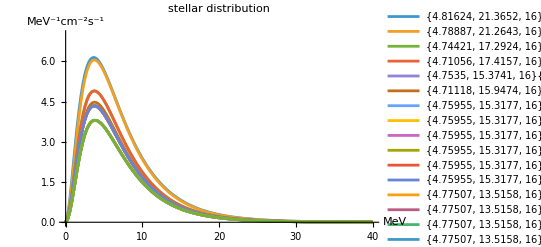

```mathematica
dsnbFluxesTemperaturePlotterJR[stellarDistdata,"stellar distribution"]
```

varying 1P vs 2P criterion

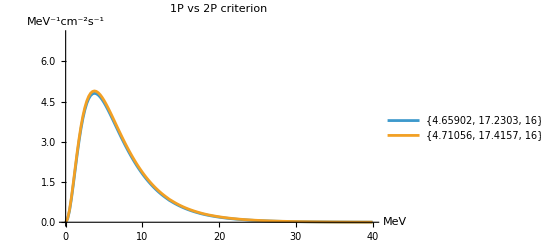

```mathematica
dsnbFluxesTemperaturePlotterJR[criterionData,"1P vs 2P criterion"]
```

#### global extrema no MSW (without SFR uncertainty)

```mathematica
minMaxFid=Join[{globalExtremaAllnoMSW[[1,2]]},{globalExtremaAllnoMSW[[2,2]]},{fiducialData[[1]]}];
```

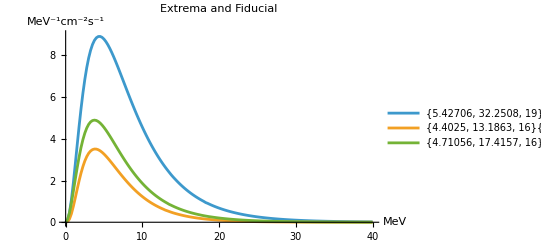

```mathematica
dsnbFluxesTemperaturePlotter3[minMaxFid,"Extrema and Fiducial"]
```

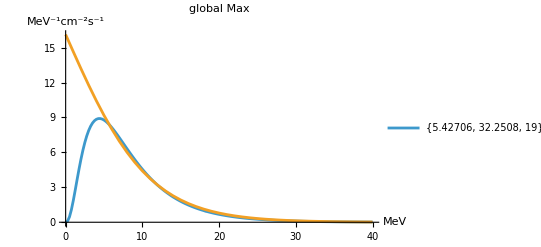

```mathematica
dsnbFluxesTemperaturePlotter[{globalExtremaAllnoMSW[[1,2]]},"global Max"]
```

#### global extrema no MSW (with SFR uncertainty)

```mathematica
minMaxFidSFR=Join[{globalExtremaAllnoMSWSFR[[1,2]]},{globalExtremaAllnoMSWSFR[[2,2]]},{fiducialData[[1]]}];
```

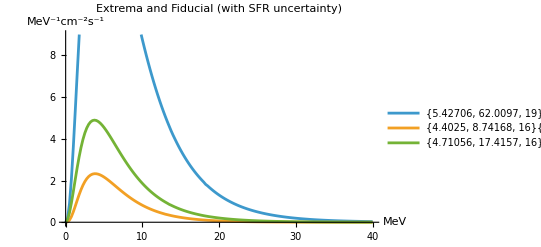

```mathematica
dsnbFluxesTemperaturePlotter3[minMaxFidSFR,"Extrema and Fiducial (with SFR uncertainty)"]
```

appears to make no difference for the fitting

also double check alpha (pinching parameter case)

```mathematica
dsnbFluxesTemperaturePlotterJR[alphaCheck,"spectral pinching"]
```

-Graphics-

1

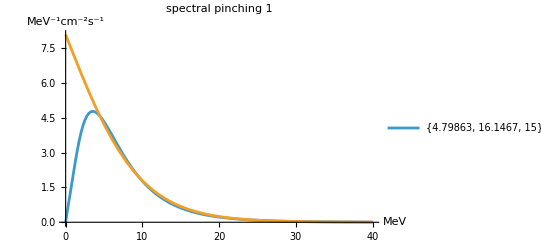

```mathematica
index=1
dsnbFluxesTemperaturePlotter[{alphaCheck[[index]]},"spectral pinching "<>ToString[index]]
```

2

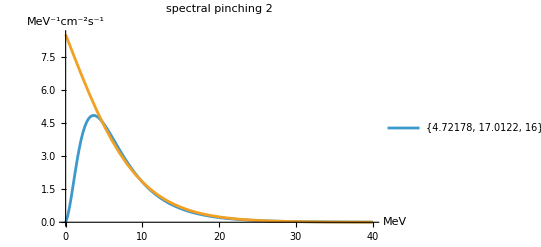

```mathematica
index=2
dsnbFluxesTemperaturePlotter[{alphaCheck[[index]]},"spectral pinching "<>ToString[index]]
```

#### global extrema IH/NH (without SFR uncertainty)

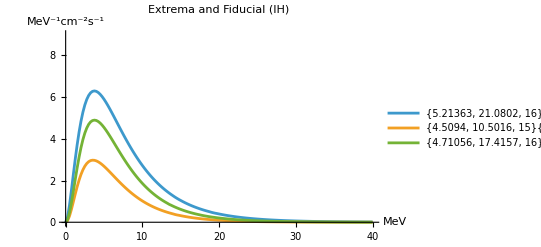

```mathematica
minMaxFidIH=Join[{globalExtremaAllIH[[1,2]]},{globalExtremaAllIH[[2,2]]},{fiducialData[[1]]}];
dsnbFluxesTemperaturePlotter3[minMaxFidIH,"Extrema and Fiducial (IH)"]
```

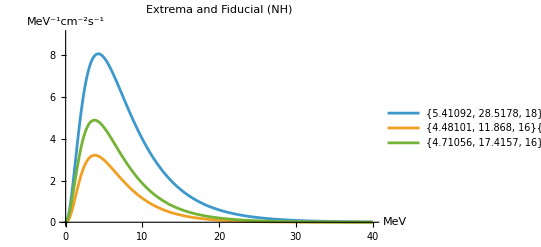

```mathematica
minMaxFidNH=Join[{globalExtremaAllNH[[1,2]]},{globalExtremaAllNH[[2,2]]},{fiducialData[[1]]}];
dsnbFluxesTemperaturePlotter3[minMaxFidNH,"Extrema and Fiducial (NH)"]
```

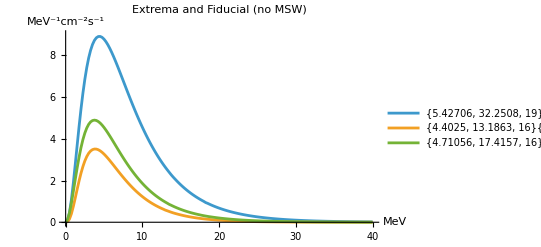

```mathematica
dsnbFluxesTemperaturePlotter3[minMaxFid,"Extrema and Fiducial (no MSW)"]
```

### find temperature (theirs: theory comparison)

#### extrema in fig 1 from Abe et al. 2025 (Sk collab)

```mathematica
(*list of DSNB flux from fig 1 of Abe et al. 2025 theory plot*)
(*from SK collab*)
(*barranco18 was not in indep var ascending order*)
theoryDSNB={ivanez23,nakazato24,Sort[barranco18],kaplinghat00};
theoryDSNBnames={"Ivanez23","Nakazato24","barranco18","kaplinghat00"};
```

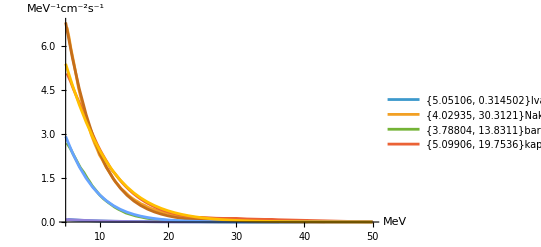

```mathematica
dsnbFluxesTemperaturePlotter4[theoryDSNB,theoryDSNBnames]
```

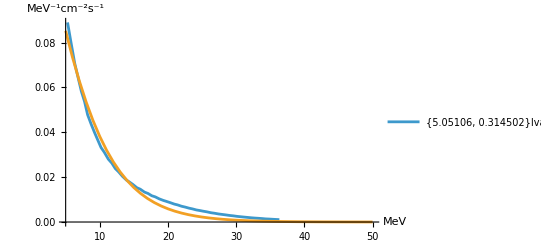

```mathematica
dsnbFluxesTemperaturePlotter4[{theoryDSNB[[1]]},{theoryDSNBnames[[1]]}]
```

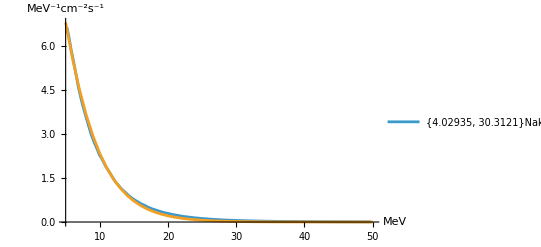

```mathematica
dsnbFluxesTemperaturePlotter4[{theoryDSNB[[2]]},{theoryDSNBnames[[2]]}]
```

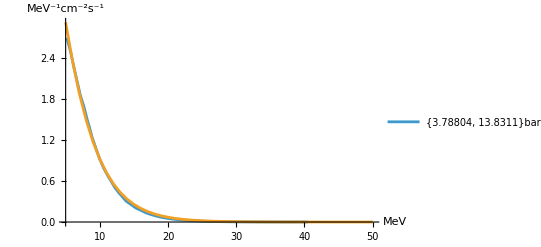

```mathematica
dsnbFluxesTemperaturePlotter4[{theoryDSNB[[3]]},{theoryDSNBnames[[3]]}]
```

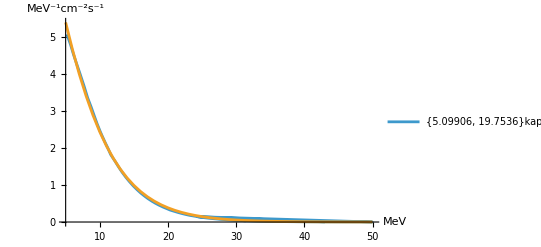

```mathematica
dsnbFluxesTemperaturePlotter4[{theoryDSNB[[4]]},{theoryDSNBnames[[4]]}]
```

#### fig 7 lunardini et al. 2025

```mathematica
(*dsnbFluxesTemperaturePlotter[{1,2,3,4,5,fig7Lunardini},"Figure 7 No MSW Lunardini et al. 2025"]*)
```

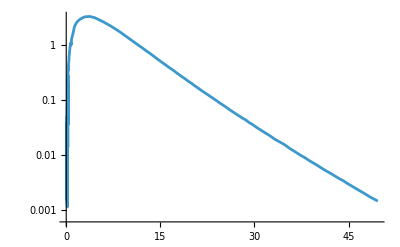

```mathematica
ListLogPlot[fig7Lunardini,Joined->True]
```

```mathematica
lunardiniTcoe=tempFinder[fig7Lunardini]
```

{5.09298,10.6683,70}

```mathematica
lunardiniFermiDirac=Table[{x,fermiDirac[x,lunardiniTcoe[[1]],lunardiniTcoe[[2]]]},{x,fig7Lunardini[[All,1]]}];
```

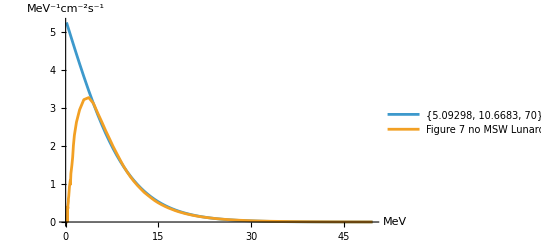

```mathematica
ListPlot[{lunardiniFermiDirac,fig7Lunardini},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLegends->{ToString[lunardiniTcoe],"Figure 7 no MSW Lunardini et al. 2025"}]
```

#### fig 5 kresse et al. 2021

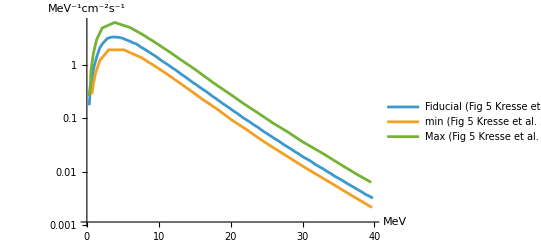

```mathematica
ListLogPlot[{fig5KresseFiducial,fig5KresseLower,fig5KresseUpper},Joined->True,PlotRange->All,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotLegends->{"Fiducial (Fig 5 Kresse et al. 2021)","min (Fig 5 Kresse et al. 2021)","Max (Fig 5 Kresse et al. 2021)"}]
```

```mathematica
kresseTcoeUp=tempFinder[fig5KresseUpper]
kresseTcoeFid=tempFinder[fig5KresseFiducial]
kresseTcoeLow=tempFinder[fig5KresseLower]
```

{4.90577,20.9906,9}

{4.85439,11.759,17}

{5.49067,5.95528,5}

```mathematica
DuplicateFreeQ[fig5KresseLower]
```

True

```mathematica
DuplicateFreeQ[fig5KresseUpper]
```

True

### shape analysis (ON)

#### find all fit parameters

test for just fiducial

```mathematica
(*output is in format of {{FD parameters, caseName, DSNB flux},...}*)
(*dsnbFluxesTemperatureJR[fiducialData]*)
```

fit to all DSNB flux data (Except without all NS case and 1 parameter criterion)

```mathematica
(*all iterations (without all NS case and 1P criterion)*)
iterations=Length[selectorRecursive[dataAll,{1,"BHNS"},1]]
(*output is in format of {{FD temp,FD coef,index} caseName, DSNB flux},...}*)
allDSNBfitted=dsnbFluxesTemperatureJR[selectorRecursive[dataAll,{1,"BHNS"},1][[1;;iterations]]];
```

5400

```mathematica
(*allDSNBfitted[[All,1]]*)
```

```mathematica
(*allDSNBfitted[[1]]*)
```

#### sort by only temperature

```mathematica
(*sort by temperaure only*)
allDSNBorderedTemp=Sort[allDSNBfitted,#1[[1,1]]<#2[[1,1]]&];
```

```mathematica
(*allDSNBorderedTemp[[All,1]]*)
```

```mathematica
ListPlot[allDSNBorderedTemp[[-3;;-1,3]],PlotLegends->allDSNBorderedTemp[[-3;;-1,2]],Joined->True,PlotLabel->"Max Temp"]
```

-Graphics-

```mathematica
Join[allDSNBorderedTemp[[1;;3,2]],allDSNBorderedTemp[[-3;;-1,2]]]
```

{{4.35239, 16.7093}{bin syn, ExCE01, N20-BH2.3-a3.0, 2.3, a3.0, 1, BHNS, no MSW},{4.35375, 17.8792}{bin syn, ExCE01, S19.8-BH2.3-a3.0, 2.3, a3.0, 1, BHNS, no MSW},{4.36476, 16.7934}{bin syn, ExCE01, S19.8-BH2.3-a3.0, 2.3, a3.0, 1, BHNS, NH},{5.71244, 24.9679}{bin syn, ExCE01, W18-BH3.5-a1.0, 3.5, a1.0, 1, BHNS, no MSW},{5.75163, 24.2351}{bin syn, ExCE01, W15-BH3.5-a1.0, 3.5, a1.0, 1, BHNS, no MSW},{5.78082, 25.4752}{bin syn, ExCE01, W20-BH3.5-a1.0, 3.5, a1.0, 1, BHNS, no MSW}}

```mathematica
ListPlot[Join[allDSNBorderedTemp[[-3;;-1,3]],allDSNBorderedTemp[[1;;3,3]]],PlotLegends->Join[allDSNBorderedTemp[[-3;;-1,2]],allDSNBorderedTemp[[1;;3,2]]],Joined->True,PlotLabel->"Max/Min Temp",PlotRange->{{0,All},{0,10}},AxesLabel->{"MeV","cm^-2s^-1MeV^-1"}]
```

-Graphics-

#### sort by only coefficient

```mathematica
(*sort by temperaure only*)
allDSNBorderedCoef=Sort[allDSNBfitted,#1[[1,2]]<#2[[1,2]]&];
```

```mathematica
(*allDSNBorderedCoef[[All,1]]*)
```

```mathematica
ListPlot[Join[allDSNBorderedCoef[[-3;;-1,3]],allDSNBorderedCoef[[{1,13,25},3]]],PlotLegends->Join[allDSNBorderedCoef[[-3;;-1,2]],allDSNBorderedCoef[[{1,13,25},2]]],Joined->True,PlotLabel->"Max/Min Coefficient",PlotRange->{{0,All},{0,10}},AxesLabel->{"MeV","cm^-2s^-1MeV^-1"}]
```

-Graphics-

```mathematica
(*ListPlot[allDSNBorderedCoef[[1;;12,3]],PlotLegends->allDSNBorderedCoef[[1;;14,2]],Joined->True,PlotLabel->"Min Coefficient"]*)
```

```mathematica
(*ListPlot[allDSNBorderedCoef[[12;;24,3]],PlotLegends->allDSNBorderedCoef[[12;;24,2]],Joined->True,PlotLabel->"Min Coefficient"]*)
```

#### self comparisons

compare max

```mathematica
ListPlot[Join[allDSNBorderedCoef[[-3;;-1,3]],allDSNBorderedTemp[[-3;;-1,3]]],PlotLegends->Join[allDSNBorderedCoef[[-3;;-1,2]],allDSNBorderedTemp[[-3;;-1,2]]],Joined->True,PlotLabel->"Max Coef (solid) vs Max Temp (dotted)",PlotRange->{{0,All},{0,10}},AxesLabel->{"MeV","cm^-2s^-1MeV^-1"},PlotStyle->{Line,Line, Line,Dotted,Dotted,Dotted}]
```

-Graphics-

```mathematica
ListPlot[Join[allDSNBorderedCoef[[-3;;-1,3]],allDSNBorderedTemp[[-3;;-1,3]]],PlotLegends->Join[allDSNBorderedCoef[[-3;;-1,2]],allDSNBorderedTemp[[-3;;-1,2]]],Joined->True,PlotLabel->"Max Coef (solid) vs Max Temp (dotted)",PlotRange->{{10,30},{0,2}},AxesLabel->{"MeV","cm^-2s^-1MeV^-1"},PlotStyle->{Line,Line, Line,Dotted,Dotted,Dotted}]
```

-Graphics-

compare min

```mathematica
ListPlot[Join[allDSNBorderedCoef[[{1,13,25},3]],allDSNBorderedTemp[[1;;3,3]]],PlotLegends->Join[allDSNBorderedCoef[[{1,13,25},2]],allDSNBorderedTemp[[1;;3,2]]],Joined->True,PlotRange->{{0,30},{0,5}},AxesLabel->{"MeV","cm^-2s^-1MeV^-1"},PlotLabel->"Min Coef (solid) vs Min Temp (dotted)",PlotStyle->{Line,Line, Line,Dotted,Dotted,Dotted}]
```

-Graphics-

```mathematica
ListPlot[Join[allDSNBorderedCoef[[{1,13,25},3]],allDSNBorderedTemp[[1;;3,3]]],PlotLegends->Join[allDSNBorderedCoef[[{1,13,25},2]],allDSNBorderedTemp[[1;;3,2]]],Joined->True,PlotRange->{{10,30},{0,2}},AxesLabel->{"MeV","cm^-2s^-1MeV^-1"},PlotLabel->"Min Coef (solid) vs Min Temp (dotted)",PlotStyle->{Line,Line, Line,Dotted,Dotted,Dotted}]
```

-Graphics-

#### comparison with Horiuchi et al. 2009 and Lunardini et al. 2025

show previous DSNB flux plots

```mathematica
ListLogPlot[allDSNBorderedTemp[[-3;;-1,3]],PlotLegends->allDSNBorderedTemp[[-3;;-1,2]],Joined->True,PlotLabel->"Max Temp",PlotStyle->{defaultColor[[3]],defaultColor[[3]],defaultColor[[3]]},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"}]
```

-Graphics-

```mathematica
ListLogPlot[allDSNBorderedCoef[[-3;;-1,3]],PlotLegends->allDSNBorderedCoef[[-3;;-1,2]],Joined->True,PlotLabel->"Max Coefficient",PlotStyle->{defaultColor[[3]],defaultColor[[3]],defaultColor[[3]]},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"}]
```

-Graphics-

```mathematica
ListLogPlot[{fig7Lunardini,fiducialData[[1,-1]],Sort[fig6MeVtop],Flatten[allDSNBorderedTemp[[-3;;-1,3]],1]},Joined->True,PlotLegends->{"Figure 7 Lunardini et al. 2025 (no MSW)","Fiducial (T = 4.7 MeV, coef = 17.4)","Max Horiuchi et al. 2009 (T = 6 MeV)","Max temp T = 5.7-5.8 MeV,, coef = 24-25",None},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotRange->{{0,40},{0.01,10}},PlotStyle->{defaultColor[[1]],defaultColor[[2]],defaultColor[[4]],defaultColor[[3]],defaultColor[[3]],defaultColor[[3]]}]
```

-Graphics-

```mathematica
(*allDSNBorderedTemp[[-3;;-1,3]][[1]]*)
```

create energy bins to play with

```mathematica
energyBins2=Table[{i,i+2},{i,15,25,2}]
energyBins1=Table[{i,i+1},{i,15,25,1}]
energyBins05=Table[{i,i+0.5},{i,15,25,0.5}]
```

{{15,17},{17,19},{19,21},{21,23},{23,25},{25,27}}

{{15,16},{16,17},{17,18},{18,19},{19,20},{20,21},{21,22},{22,23},{23,24},{24,25},{25,26}}

{{15.,15.5},{15.5,16.},{16.,16.5},{16.5,17.},{17.,17.5},{17.5,18.},{18.,18.5},{18.5,19.},{19.,19.5},{19.5,20.},{20.,20.5},{20.5,21.},{21.,21.5},{21.5,22.},{22.,22.5},{22.5,23.},{23.,23.5},{23.5,24.},{24.,24.5},{24.5,25.},{25.,25.5}}

test binner works properly

```mathematica
bob1=ListStepPlot[binner[fiducialData[[1,-1]],energyBins1],PlotRange->{{15,25},{0,1}}];
bob2=ListPlot[fiducialData[[1,-1]],PlotRange->{{15,25},{0,1}},Joined->True];
Show[bob1,bob2]
```

-Graphics-

```mathematica
bob1=ListStepPlot[binner[fiducialData[[1,-1]],energyBins05],PlotRange->{{15,25},{0,1}}];
bob2=ListPlot[fiducialData[[1,-1]],PlotRange->{{15,25},{0,1}},Joined->True];
Show[bob1,bob2]
```

-Graphics-

zoomed in version about 20 MeV

```mathematica
ListStepPlot[{
binner[fig7Lunardini,energyBins2],
binner[fiducialData[[1,-1]],energyBins2],
binner[Sort[fig6MeVtop],energyBins2]
},
PlotLabel->"Bin width: "<>ToString[energyBins2[[1,2]]-energyBins2[[1,1]]]<>" MeV",
Joined->True,PlotLegends->{"Figure 7 Lunardini et al. 2025 (no MSW)","Fiducial (T = 4.7 MeV, coef = 17.4)","Max Horiuchi et al. 2009 (T = 6 MeV)","Max temp T = 5.7-5.8 MeV",None},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotStyle->{defaultColor[[1]],defaultColor[[2]],defaultColor[[4]],defaultColor[[3]],defaultColor[[3]],defaultColor[[3]]},ScalingFunctions->"Log"]
```

-Graphics-

comparison to top 3 max temp

```mathematica
ListStepPlot[{
binner[fig7Lunardini,energyBins2],
binner[fiducialData[[1,-1]],energyBins2],
binner[Sort[fig6MeVtop],energyBins2],
binner[allDSNBorderedTemp[[-3;;-1,3]][[1]],energyBins2],
binner[allDSNBorderedTemp[[-3;;-1,3]][[2]],energyBins2],
binner[allDSNBorderedTemp[[-3;;-1,3]][[3]],energyBins2]
},
PlotLabel->"Bin width: "<>ToString[energyBins2[[1,2]]-energyBins2[[1,1]]]<>" MeV",
Joined->True,PlotLegends->{"Figure 7 Lunardini et al. 2025 (no MSW)","Fiducial (T = 4.7 MeV, coef = 17.4)","Max Horiuchi et al. 2009 (T = 6 MeV, coef = 24-25)","Max temp T = 5.7-5.8 MeV",None},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotStyle->{defaultColor[[1]],defaultColor[[2]],defaultColor[[4]],defaultColor[[3]],defaultColor[[3]],defaultColor[[3]]}(*,ScalingFunctions->"Log"*)]
```

-Graphics-

```mathematica
(*greatest coeff minus max Horiuchi et al. 2009*)
binner[allDSNBorderedTemp[[-3;;-1,3]][[1]],energyBins2][[All,2]]-binner[Sort[fig6MeVtop],energyBins2][[All,2]]
```

{0.943558,0.695202,0.517792,0.388337,0.292999,0.220306,0.220306}

```mathematica
ListStepPlot[{
binner[fig7Lunardini,energyBins05],
binner[fiducialData[[1,-1]],energyBins05],
binner[Sort[fig6MeVtop],energyBins05],
binner[allDSNBorderedTemp[[-3;;-1,3]][[1]],energyBins05],
binner[allDSNBorderedTemp[[-3;;-1,3]][[2]],energyBins05],
binner[allDSNBorderedTemp[[-3;;-1,3]][[3]],energyBins05]
},
PlotLabel->"Bin width: "<>ToString[energyBins05[[1,2]]-energyBins05[[1,1]]]<>" MeV",
Joined->True,PlotLegends->{"Figure 7 Lunardini et al. 2025 (no MSW)","Fiducial (T = 4.7 MeV, coef = 17.4)","Max Horiuchi et al. 2009 (T = 6 MeV)","Max temp T = 5.7-5.8 MeV, coef = 24-25",None},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotStyle->{defaultColor[[1]],defaultColor[[2]],defaultColor[[4]],defaultColor[[3]],defaultColor[[3]],defaultColor[[3]]}(*,ScalingFunctions->"Log"*)]
```

InterpolatingFunction::dmval: Input value {15.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {25.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

comparison to top 3 max coefficient

```mathematica
ListStepPlot[{
binner[fig7Lunardini,energyBins2],
binner[fiducialData[[1,-1]],energyBins2],
binner[Sort[fig6MeVtop],energyBins2],
binner[allDSNBorderedCoef[[-3;;-1,3]][[1]],energyBins2],
binner[allDSNBorderedCoef[[-3;;-1,3]][[2]],energyBins2],
binner[allDSNBorderedCoef[[-3;;-1,3]][[3]],energyBins2]
},
PlotLabel->"Bin width: "<>ToString[energyBins2[[1,2]]-energyBins2[[1,1]]]<>" MeV",
Joined->True,PlotLegends->{"Figure 7 Lunardini et al. 2025 (no MSW)","Fiducial (T = 4.7 MeV, coef = 17.4)","Max Horiuchi et al. 2009 (T = 6 MeV)","T = 5.1-5.4 MeV, coeff = 31-32",None},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotStyle->{defaultColor[[1]],defaultColor[[2]],defaultColor[[4]],defaultColor[[3]],defaultColor[[3]],defaultColor[[3]]}(*,ScalingFunctions->"Log"*)]
```

-Graphics-

```mathematica
(*greatest coeff minus max Horiuchi et al. 2009*)
binner[allDSNBorderedCoef[[-3;;-1,3]][[1]],energyBins2][[All,2]]-binner[Sort[fig6MeVtop],energyBins2][[All,2]]
```

{0.982322,0.651806,0.43303,0.28776,0.191389,0.128343,0.128343}

```mathematica
ListStepPlot[{
binner[fig7Lunardini,energyBins05],
binner[fiducialData[[1,-1]],energyBins05],
binner[Sort[fig6MeVtop],energyBins05],
binner[allDSNBorderedCoef[[-3;;-1,3]][[1]],energyBins05],
binner[allDSNBorderedCoef[[-3;;-1,3]][[2]],energyBins05],
binner[allDSNBorderedCoef[[-3;;-1,3]][[3]],energyBins05]
},
PlotLabel->"Bin width: "<>ToString[energyBins05[[1,2]]-energyBins05[[1,1]]]<>" MeV",
Joined->True,PlotLegends->{"Figure 7 Lunardini et al. 2025 (no MSW)","Fiducial (T = 4.7 MeV, coef = 17.4)","Max Horiuchi et al. 2009 (T = 6 MeV)","T = 5.1-5.4 MeV, coeff = 31-32",None},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},PlotStyle->{defaultColor[[1]],defaultColor[[2]],defaultColor[[4]],defaultColor[[3]],defaultColor[[3]],defaultColor[[3]]}(*,ScalingFunctions->"Log"*)]
```

InterpolatingFunction::dmval: Input value {15.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {25.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## finding ratio (kresse et al. 2021)

find ratio of Kresse et al. 2021 fiducial model and our fiducial model (no MSW)

### DSNB flux comparison plot (from “DSNB Flux”)

```mathematica
ListLogPlot[{globalExtremaAllnoMSWSFR[[1,2]][[-1]],globalExtremaAllnoMSWSFR[[2,2]][[-1]],fiducialData[[1,-1]],globalExtremaAllnoMSW[[1,2]][[-1]],globalExtremaAllnoMSW[[2,2]][[-1]],fig5KresseFiducial,fig5KresseLower,fig5KresseUpper},
Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},
PlotLabel->"DSNB flux (No MSW)",
PlotLegends->{ToString[globalExtremaAllnoMSWSFR[[1,2,1]]],ToString[globalExtremaAllnoMSWSFR[[2,2,1]]],ToString[fiducialData[[1,1]]],ToString[globalExtremaAllnoMSW[[1,2,1]]],ToString[globalExtremaAllnoMSW[[2,2,1]]],"Fiducial (Fig 5 Kresse et al. 2025)"},
PlotStyle->{{defaultColor[[1]]},{defaultColor[[1]]},{Black},{Dashed,defaultColor[[3]]},{Dashed,defaultColor[[3]]},{Dashed,Lighter[Black]},{Gray},{Gray}},
Filling->{1->{{2},{Opacity[0.3,defaultColor[[1]]]}},4->{{5},{Opacity[0.3,defaultColor[[3]]]}},7->{{8},Opacity[0.3,Gray]}},
PlotRange->{{0,40},{0,18}}
](*end plot*)
```

-Graphics-

```mathematica
ListLogPlot[{fiducialData[[1,-1]],fig5KresseFiducial},
Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2s^-1"},
PlotLabel->"DSNB flux (No MSW)",
PlotLegends->{ToString[fiducialData[[1,1]]],"Fiducial (Fig 5 Kresse et al. 2025)"},
PlotStyle->{{Black},{Dashed,Lighter[Black]}},
PlotRange->{{0,40},{0,18}}
](*end plot*)
```

-Graphics-

look at maxima

```mathematica
(*decimal e.g. 0.1*)
Print["fid/kresse"]
(4.88/3.37)
Print["kresse/fid"]
(3.37/4.88)
```

fid/kresse

1.44807

kresse/fid

0.690574

```mathematica
3.37*1.44
```

4.8528

```mathematica
(*percentage 0.1*100=10%*)
Print["fid/kresse percentage"]
(4.88/3.37)*100"%"
Print["kresse/fid percentage"]
(3.37/4.88)*100 "%"
```

fid/kresse percentage

144.807 %

kresse/fid percentage

69.0574 %

### fitting parameter comparison

fit DSNB flux to Fermi-Dirac distribution and find coeffiient/normalization and temperature

```mathematica
kresseTcoeFid=tempFinder[fig5KresseFiducial]
```

{4.85439,11.759,17}

```mathematica
fiducialTcoe=tempFinder[fiducialData[[1,-1]]]
```

{4.71056,17.4157,16}

compare coefficient/normalization ratios

```mathematica
(*compare normalizations/coefficients*)
fiducialTcoe[[2]]
kresseTcoeFid[[2]]
fiducialTcoe[[2]]/kresseTcoeFid[[2]]
kresseTcoeFid[[2]]/fiducialTcoe[[2]]
```

17.4157

11.759

1.48105

0.675194

compare temp ratios

```mathematica
(*compare normalizations/coefficients*)
fiducialTcoe[[1]]
kresseTcoeFid[[1]]
fiducialTcoe[[2]]/kresseTcoeFid[[1]]
kresseTcoeFid[[2]]/fiducialTcoe[[1]]
```

4.71056

4.85439

3.58763

2.49631

### integrated fiducial DSNB to ratios

#### full range: 0-40 MeV

```mathematica
E1=0;
E2=40;
(*our fiducial integrated DSNB*)
intDSNBfidFull=dsnbFluxIntegrator[fiducialData[[1,-1]],{E1,E2}]
(*kresse et al. 2021 fiducial data*)
intDSNBkresseFull=dsnbFluxIntegrator[fig5KresseFiducial,{E1,E2}]
intDSNBfidFull/intDSNBkresseFull
intDSNBkresseFull/intDSNBfidFull
```

41.1018

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 40 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

28.6104

1.4366

0.696086

```mathematica
1-intDSNBkresseFull/intDSNBfidFull
```

0.303914

#### below crossing range: 0-20 MeV

```mathematica
E1=0;
E2=20;
(*our fiducial integrated DSNB*)
intDSNBfidFull=dsnbFluxIntegrator[fiducialData[[1,-1]],{E1,E2}]
(*kresse et al. 2021 fiducial data*)
intDSNBkresseFull=dsnbFluxIntegrator[fig5KresseFiducial,{E1,E2}]
intDSNBkresseFull/intDSNBfidFull
intDSNBfidFull/intDSNBkresseFull
```

40.145

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

27.8962

0.694887

1.43908

#### above crossing range range: 20-40 MeV

```mathematica
E1=20;
E2=40;
(*our fiducial integrated DSNB*)
intDSNBfidFull=dsnbFluxIntegrator[fiducialData[[1,-1]],{E1,E2}]
(*kresse et al. 2021 fiducial data*)
intDSNBkresseFull=dsnbFluxIntegrator[fig5KresseFiducial,{E1,E2}]
intDSNBkresseFull/intDSNBfidFull
intDSNBfidFull/intDSNBkresseFull
```

0.956873

InterpolatingFunction::dmvali: The integration endpoint 40 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

0.7142

0.746389

1.33978

#### detection range: 10-30 MeV

```mathematica
E1=10;
E2=30;
(*our fiducial integrated DSNB*)
intDSNBfidFull=dsnbFluxIntegrator[fiducialData[[1,-1]],{E1,E2}]
(*kresse et al. 2021 fiducial data*)
intDSNBkresseFull=dsnbFluxIntegrator[fig5KresseFiducial,{E1,E2}]
intDSNBfidFull/intDSNBkresseFull
intDSNBkresseFull/intDSNBfidFull
```

8.36363

6.05449

1.38139

0.723906

```mathematica
1-intDSNBkresseFull/intDSNBfidFull
```

0.276094

## finding ratio (others)

### comparing to fiducial

#### fiducial vs no bin syn

compare int dsnb fiducial to no bin syn (assume all else is fiducial)

```mathematica
singleVsbinarydata[[2]][[1]]
singleVsbinarydata[[2]][[-1]]
```

{no bin syn,fiducialCE1,W18-BH2.7-a2.0,2.7,a2.0,1,BHNS,no MSW}

{{0.,0.},{0.25,0.125196},{0.5,0.432937},{0.75,0.86414},{1.,1.36079},{1.25,1.87448},{1.5,2.36951},{1.75,2.82195},{2.,3.21781},{2.25,3.55066},{2.5,3.81943},{2.75,4.0266},{3.,4.17601},{3.25,4.274},{3.5,4.32813},{3.75,4.34348},{4.,4.32594},{4.25,4.28095},{4.5,4.21338},{4.75,4.12756},{5.,4.02727},{5.25,3.91575},{5.5,3.79581},{5.75,3.66981},{6.,3.53974},{6.25,3.40728},{6.5,3.27382},{6.75,3.14052},{7.,3.00832},{7.25,2.87797},{7.5,2.75011},{7.75,2.62521},{8.,2.50364},{8.25,2.38571},{8.5,2.27161},{8.75,2.16149},{9.,2.05544},{9.25,1.9535},{9.5,1.85569},{9.75,1.76197},{10.,1.6723},{10.25,1.5866},{10.5,1.5048},{10.75,1.42679},{11.,1.35246},{11.25,1.28171},{11.5,1.2144},{11.75,1.15041},{12.,1.08961},{12.25,1.03188},{12.5,0.977096},{12.75,0.92512},{13.,0.875834},{13.25,0.829115},{13.5,0.784869},{13.75,0.738999},{14.,0.703208},{14.25,0.665622},{14.5,0.630019},{14.75,0.596321},{15.,0.564433},{15.25,0.534261},{15.5,0.505717},{15.75,0.478715},{16.,0.453175},{16.25,0.429019},{16.5,0.406173},{16.75,0.384567},{17.,0.364135},{17.25,0.344813},{17.5,0.326542},{17.75,0.307468},{18.,0.291199},{18.25,0.275817},{18.5,0.261271},{18.75,0.247517},{19.,0.23451},{19.25,0.223598},{19.5,0.211903},{19.75,0.20084},{20.,0.190374},{20.25,0.180473},{20.5,0.171104},{20.75,0.162297},{21.,0.153905},{21.25,0.145962},{21.5,0.138444},{21.75,0.131328},{22.,0.124592},{22.25,0.118214},{22.5,0.112176},{22.75,0.106168},{23.,0.100778},{23.25,0.0956722},{23.5,0.0908351},{23.75,0.0862521},{24.,0.0819094},{24.25,0.0777939},{24.5,0.0738933},{24.75,0.070234},{25.,0.0667275},{25.25,0.0634029},{25.5,0.0602505},{25.75,0.057261},{26.,0.0544257},{26.25,0.0517363},{26.5,0.0491851},{26.75,0.0467646},{27.,0.044468},{27.25,0.0420085},{27.5,0.039956},{27.75,0.0380078},{28.,0.0361584},{28.25,0.0344026},{28.5,0.0327356},{28.75,0.0311525},{29.,0.0296491},{29.25,0.0282211},{29.5,0.0268646},{29.75,0.025576},{30.,0.0243516},{30.25,0.0231881},{30.5,0.0220824},{30.75,0.0210315},{31.,0.0200326},{31.25,0.019083},{31.5,0.0181802},{31.75,0.0173217},{32.,0.0165054},{32.25,0.015729},{32.5,0.0149905},{32.75,0.0142881},{33.,0.0136198},{33.25,0.0129839},{33.5,0.0123789},{33.75,0.0118032},{34.,0.0112552},{34.25,0.0107336},{34.5,0.0102371},{34.75,0.00976445},{35.,0.00931442},{35.25,0.00888589},{35.5,0.0084778},{35.75,0.00808915},{36.,0.00771896},{36.25,0.00736633},{36.5,0.0070304},{36.75,0.00671034},{37.,0.00640537},{37.25,0.00611476},{37.5,0.0058378},{37.75,0.00557383},{38.,0.00532222},{38.25,0.00508237},{38.5,0.00485371},{38.75,0.00463569},{39.,0.0044278},{39.25,0.00422955},{39.5,0.00404049},{39.75,0.00386017},{40.,0.00368816}}

detection range

```mathematica
E1=10;
E2=30;
(*our fiducial integrated DSNB*)
intDSNBfidFull=dsnbFluxIntegrator[fiducialData[[1,-1]],{E1,E2}]
(*no bin syn but keep everything else fiducial*)
intDSNBnoBinSynFull=dsnbFluxIntegrator[singleVsbinarydata[[2]][[-1]],{E1,E2}]
intDSNBfidFull/intDSNBnoBinSynFull
intDSNBnoBinSynFull/intDSNBfidFull
```

8.36363

7.63075

1.09604

0.912373

```mathematica
1-intDSNBnoBinSynFull/intDSNBfidFull
```

0.087627

full range

```mathematica
E1=0;
E2=40;
(*our fiducial integrated DSNB*)
intDSNBfidFull=dsnbFluxIntegrator[fiducialData[[1,-1]],{E1,E2}]
(*no bin syn but keep everything else fiducial*)
intDSNBnoBinSynFull=dsnbFluxIntegrator[singleVsbinarydata[[2]][[-1]],{E1,E2}]
intDSNBfidFull/intDSNBnoBinSynFull
intDSNBnoBinSynFull/intDSNBfidFull
```

41.1018

36.8284

1.11604

0.896028

```mathematica
1-intDSNBnoBinSynFull/intDSNBfidFull
```

0.103972

#### fiducial vs progen+engine

compare int dsnb fiducial to progen+engine (assume all else is fiducial)

```mathematica
singleVsbinarydata[[3]][[1]]
singleVsbinarydata[[3]][[-1]]
```

{progen+engine,fiducialCE1,W18-BH2.7-a2.0,2.7,a2.0,1,BHNS,no MSW}

{{0.,0.},{0.25,0.0977862},{0.5,0.337475},{0.75,0.681146},{1.,1.08902},{1.25,1.5229},{1.5,1.95141},{1.75,2.35166},{2.,2.70885},{2.25,3.01492},{2.5,3.26693},{2.75,3.46555},{3.,3.6138},{3.25,3.71608},{3.5,3.77746},{3.75,3.80192},{4.,3.7973},{4.25,3.767},{4.5,3.71538},{4.75,3.64636},{5.,3.56339},{5.25,3.46947},{5.5,3.36717},{5.75,3.2587},{6.,3.14592},{6.25,3.03041},{6.5,2.91348},{6.75,2.79623},{7.,2.67957},{7.25,2.56423},{7.5,2.45081},{7.75,2.3398},{8.,2.23157},{8.25,2.12641},{8.5,2.02454},{8.75,1.92611},{9.,1.83124},{9.25,1.73999},{9.5,1.65237},{9.75,1.56837},{10.,1.48798},{10.25,1.41114},{10.5,1.33777},{10.75,1.26781},{11.,1.20115},{11.25,1.13769},{11.5,1.07734},{11.75,1.01998},{12.,0.965499},{12.25,0.913785},{12.5,0.864724},{12.75,0.818202},{13.,0.774109},{13.25,0.732335},{13.5,0.692771},{13.75,0.655313},{14.,0.619859},{14.25,0.586311},{14.5,0.554574},{14.75,0.524556},{15.,0.496169},{15.25,0.464592},{15.5,0.439447},{15.75,0.419993},{16.,0.397319},{16.25,0.37589},{16.5,0.355638},{16.75,0.336499},{17.,0.318413},{17.25,0.301323},{17.5,0.285173},{17.75,0.269911},{18.,0.25549},{18.25,0.241861},{18.5,0.228982},{18.75,0.21681},{19.,0.205306},{19.25,0.194433},{19.5,0.184155},{19.75,0.17444},{20.,0.165255},{20.25,0.156572},{20.5,0.148361},{20.75,0.140598},{21.,0.133256},{21.25,0.126312},{21.5,0.119744},{21.75,0.113531},{22.,0.107653},{22.25,0.102092},{22.5,0.0968293},{22.75,0.0918491},{23.,0.0871356},{23.25,0.0826738},{23.5,0.0784499},{23.75,0.0744508},{24.,0.0706641},{24.25,0.067078},{24.5,0.0636815},{24.75,0.06051},{25.,0.0574597},{25.25,0.0545697},{25.5,0.0513952},{25.75,0.0488269},{26.,0.0463924},{26.25,0.0440845},{26.5,0.0418963},{26.75,0.0398213},{27.,0.0378535},{27.25,0.0359871},{27.5,0.0342166},{27.75,0.032537},{28.,0.0309433},{28.25,0.029431},{28.5,0.0279958},{28.75,0.0266335},{29.,0.0253404},{29.25,0.0241127},{29.5,0.022947},{29.75,0.02184},{30.,0.0207888},{30.25,0.0197902},{30.5,0.0188417},{30.75,0.0179405},{31.,0.0170843},{31.25,0.0162706},{31.5,0.0154973},{31.75,0.0147623},{32.,0.0140636},{32.25,0.0133994},{32.5,0.0127679},{32.75,0.0121673},{33.,0.0115962},{33.25,0.011053},{33.5,0.0105363},{33.75,0.0100447},{34.,0.00957701},{34.25,0.00913199},{34.5,0.00870849},{34.75,0.00830543},{35.,0.00792179},{35.25,0.00755658},{35.5,0.00720889},{35.75,0.00687784},{36.,0.0065626},{36.25,0.00626238},{36.5,0.00597645},{36.75,0.00570409},{37.,0.00544463},{37.25,0.00519744},{37.5,0.00496191},{37.75,0.00473747},{38.,0.00452358},{38.25,0.00431972},{38.5,0.0041254},{38.75,0.00394016},{39.,0.00376355},{39.25,0.00359516},{39.5,0.00343459},{39.75,0.00328146},{40.,0.00313541}}

detection range

```mathematica
E1=10;
E2=30;
(*our fiducial integrated DSNB*)
intDSNBfidFull=dsnbFluxIntegrator[fiducialData[[1,-1]],{E1,E2}]
(*no bin syn but keep everything else fiducial*)
intDSNBprogenEngineFull=dsnbFluxIntegrator[singleVsbinarydata[[3]][[-1]],{E1,E2}]
intDSNBfidFull/intDSNBprogenEngineFull
intDSNBprogenEngineFull/intDSNBfidFull
```

8.36363

6.72141

1.24433

0.803648

```mathematica
1-intDSNBprogenEngineFull/intDSNBfidFull
```

0.196352

full range

```mathematica
E1=0;
E2=40;
(*our fiducial integrated DSNB*)
intDSNBfidFull=dsnbFluxIntegrator[fiducialData[[1,-1]],{E1,E2}]
(*no bin syn but keep everything else fiducial*)
intDSNBprogenEngineFull=dsnbFluxIntegrator[singleVsbinarydata[[3]][[-1]],{E1,E2}]
intDSNBfidFull/intDSNBprogenEngineFull
intDSNBprogenEngineFull/intDSNBfidFull
```

41.1018

32.2521

1.27439

0.784688

```mathematica
1-intDSNBprogenEngineFull/intDSNBfidFull
```

0.215312

### comparing progen+engine to Kresse et al. 2021

```mathematica
singleVsbinarydata[[3]][[1]]
```

{progen+engine,fiducialCE1,W18-BH2.7-a2.0,2.7,a2.0,1,BHNS,no MSW}

detection range

```mathematica
E1=10;
E2=30;
(*our progen+engine data (keep all else fiducial) integrated DSNB*)
intDSNBprogenEngineFull=dsnbFluxIntegrator[singleVsbinarydata[[3]][[-1]],{E1,E2}]
(*kresse et al. 2021 fiducial data*)
intDSNBkresseFull=dsnbFluxIntegrator[fig5KresseFiducial,{E1,E2}]
intDSNBprogenEngineFull/intDSNBkresseFull
intDSNBkresseFull/intDSNBprogenEngineFull
```

6.72141

6.05449

1.11015

0.900776

```mathematica
intDSNBprogenEngineFull/intDSNBkresseFull
intDSNBkresseFull/intDSNBprogenEngineFull
```

1.11015

0.900776

```mathematica
1-intDSNBkresseFull/intDSNBprogenEngineFull
```

0.0992242

full range

```mathematica
E1=0;
E2=40;
(*our progen+engine data (keep all else fiducial) integrated DSNB*)
intDSNBprogenEngineFull=dsnbFluxIntegrator[singleVsbinarydata[[3]][[-1]],{E1,E2}]
(*kresse et al. 2021 fiducial data*)
intDSNBkresseFull=dsnbFluxIntegrator[fig5KresseFiducial,{E1,E2}]
intDSNBprogenEngineFull/intDSNBkresseFull
intDSNBkresseFull/intDSNBprogenEngineFull
```

32.2521

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 40 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

28.6104

1.12729

0.887087

```mathematica
intDSNBprogenEngineFull/intDSNBkresseFull
intDSNBkresseFull/intDSNBprogenEngineFull
```

1.12729

0.887087

```mathematica
1-intDSNBkresseFull/intDSNBprogenEngineFull
```

0.112913

### comparing horiuchi et al. 2021 internally

```mathematica
ListPlot[{fig7H21Fiducial,fig7H21noBinary},ScalingFunctions->"Log",Joined->True]
```

-Graphics-

detection range

```mathematica
intDSNBH21fid=dsnbFluxIntegrator[fig7H21Fiducial,{10,30}]
intDSNBH21noBinary=dsnbFluxIntegrator[fig7H21noBinary[[10;;-1]],{10,30}]
```

4.6614

4.00028

```mathematica
intDSNBH21fid/intDSNBH21noBinary
```

1.16527

```mathematica
intDSNBH21noBinary/intDSNBH21fid
```

0.858173

```mathematica
1-intDSNBH21noBinary/intDSNBH21fid
```

0.141827

full range

```mathematica
intDSNBH21fid=dsnbFluxIntegrator[fig7H21Fiducial,{0,40}]
intDSNBH21noBinary=dsnbFluxIntegrator[fig7H21noBinary[[10;;-1]],{0,40}]
```

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 40 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

20.7669

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 40 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

18.4504

```mathematica
intDSNBH21fid/intDSNBH21noBinary
```

1.12555

```mathematica
intDSNBH21noBinary/intDSNBH21fid
```

0.888454

```mathematica
1-intDSNBH21noBinary/intDSNBH21fid
```

0.111546

## integrated DSNB flux values (DSNB hints discovered!)

SK hints of DSNB flux (June 25th 2026): https://www-sk.icrr.u-tokyo.ac.jp/en/news/detail/1258 
slides here: https://indico.global/event/15740/contributions/155621/attachments/72866/141218/20260625_Neutrino2026_SK_Sekiya_pub.pdf

“The estimated DSNB flux is 3.6 ± 1.6 cm⁻.b2 s⁻.b9, consistent with the range predicted by several theoretical models (for example, the Horiuchi et al. 2009 6 MeV model, which predicts 2.1–3.9 cm⁻.b2 s⁻.b9).”
“SK observed the first indication of the DSNB. The best-fit DSNB signal flux obtained from
a joint fit of SK-Ntag era phases (SK-IV, V, VI, VII, VII.5, VIII) is 3.6 +1.6/-1.5 cm-2 s-1 (4.8 +2.2/-
2.0 events yr-1) for E > 13.3 MeV, assuming the Horiuchi+09, 6 MeV, max model. This
corresponds to a 2.6σ tension with a null hypothesis (5x10-3 one-sided p-value). Similar
significance was obtained for two other DSNB models with varying spectral shapes.”

```mathematica
3.6+1.6
3.6-1.5
```

5.2

2.1

```mathematica
(*report energy range for analysis*)
EnuSKlow=13.3
EnuSKhigh=40
```

13.3

40

horiuchi et al. 2009 for 6 MeV

```mathematica
dsnbFluxIntegrator[Sort[fig6MeVtop][[10;;-1]],{EnuSKlow,EnuSKhigh}]
dsnbFluxIntegrator[Sort[fig6MeVbottom][[10;;-1]],{EnuSKlow,EnuSKhigh}]
```

InterpolatingFunction::dmvali: The integration endpoint 40 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

3.86045

InterpolatingFunction::dmvali: The integration endpoint 40 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

2.05164

our fiducial model and extrema

```mathematica
dsnbFid=dsnbFluxIntegrator[fiducialData[[1,-1]],{EnuSKlow,EnuSKhigh}]
```

4.09023

```mathematica
(*max and min without SFR uncertainty*)
dsnbMax=dsnbFluxIntegrator[globalExtremaAll[[1,2]][[-1]],{EnuSKlow,EnuSKhigh}]
dsnbMin=dsnbFluxIntegrator[globalExtremaAll[[2,2]][[-1]],{EnuSKlow,EnuSKhigh}]
```

12.8064

1.99417

```mathematica
(*error values WITHOUT SFR uncertainty*)
dsnbMax-dsnbFid
dsnbFid-dsnbMin
```

8.71617

2.09606

```mathematica
(*max and min with SFR uncertainty*)
dsnbMaxSFR=dsnbFluxIntegrator[globalExtremaAllSFR[[1,2]][[-1]],{EnuSKlow,EnuSKhigh}]
dsnbMinSFR=dsnbFluxIntegrator[globalExtremaAllSFR[[2,2]][[-1]],{EnuSKlow,EnuSKhigh}]
```

24.6233

1.322

```mathematica
(*error values WITH SFR uncertainty*)
dsnbMaxSFR-dsnbFid
dsnbFid-dsnbMinSFR
```

20.533

2.76822

Kresse et al. min, fiducial, and max

```mathematica
dsnbFluxIntegrator[fig5KresseLower,{EnuSKlow,EnuSKhigh}]
dsnbFluxIntegrator[fig5KresseFiducial,{EnuSKlow,EnuSKhigh}]
dsnbFluxIntegrator[fig5KresseUpper[[5;;-1]],{EnuSKlow,EnuSKhigh}]
```

InterpolatingFunction::dmvali: The integration endpoint 40 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

1.95162

InterpolatingFunction::dmvali: The integration endpoint 40 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

3.00048

InterpolatingFunction::dmvali: The integration endpoint 40 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

5.57458